## 31 March 2011 Thursday

### Overview of exploration of hough-peak-model-based synthetic data

Simulate 30 samples from something like the peak model of the hough transform method with 20 peaks in the samples.  All peaks are present in all samples.  A key factor to a nice ordering appearing is that the sample parameters vary greatly in magnitude.  Further, the range of the multiplied sample parameters must be significantly smaller than the range of mean peak positions in order for the sorted sample plot to look right.

Below is a table reproduced when there are 3 parameters, all with a standard deviation of 0.7 (after sorting by the position of the green peak)

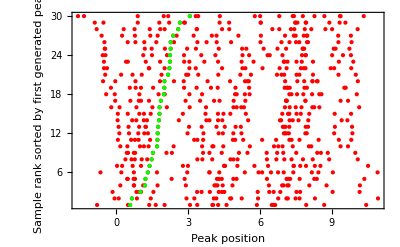

Below that is a table when the parameters had standard deviations of and 1,0.1,0.01  It looks much more like what we observe in the real-life urine spectra.

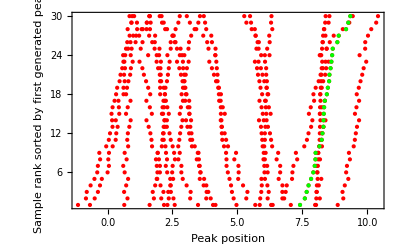

### Set up the global variables that contain the synthetic data for the experiments

s is the sample parameters for each sample

```mathematica
s=Table[{1,.3,.1} RandomReal[NormalDistribution[0,1],3],{30}];
```

a is the peak multipliers for each sample

```mathematica
a=Table[RandomReal[{-1,1},3],{20}];
```

k is the peak mean for each sample

```mathematica
k=RandomReal[{11,0},20];
```

pos is peak positions in each sample

```mathematica
pos=Map[Function[sj,MapThread[Function[{ai,ki},ki+Dot[ai, sj]],{a,k}]],s];
```

### Raw data plot

First, plot the raw data by sample number

```mathematica
allAgainstRawSampleNumber=Flatten[MapThread[Function[{sample,sampleNumber},Map[{sampleNumber,#}&,sample]],{pos,Range[Length[pos]]}],1];
```

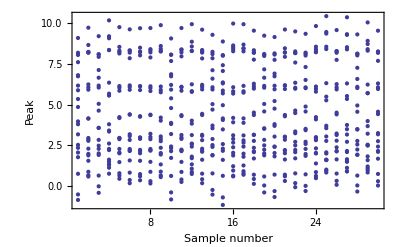

```mathematica
ListPlot[allAgainstRawSampleNumber,Frame->{True,True,False,False},FrameLabel->{"Sample number","Peak"}]
```

### Data plotted against correct peak correspondence

Look at scatter plot to see if I see any structure when all are plotted against one peak

It looks like we have (roughly) lines.  So, a first order predictor based on peak position could be linear.  Choose a one peak in the reference spectrum.  Then choose another

```mathematica
allAgainstFirst=Flatten[Map[Function[sample,With[{f=First[sample]},
Map[{f,#}&,Rest[sample]]]],pos],1];
```

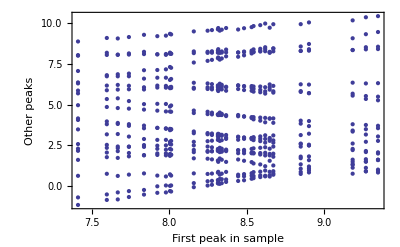

```mathematica
ListPlot[allAgainstFirst,Frame->{True,True,False,False},FrameLabel->{"First peak in sample","Other peaks"}]
```

### Data plotted against random peak correspondence

Compare that when each is paired with a random element from the same sample

```mathematica
allAgainstRandom=Flatten[Map[Function[rawSample,With[{sample=RandomSample[rawSample]},With[{f=First[sample]},
Map[{f,#}&,Rest[sample]]]]],pos],1];
```

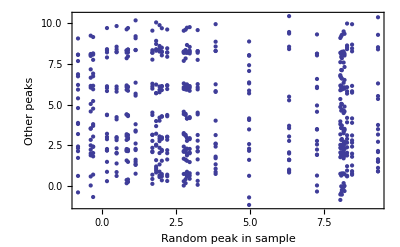

```mathematica
ListPlot[allAgainstRandom,Frame->{True,True,False,False},FrameLabel->{"Random peak in sample","Other peaks"}]
```

### Subtracting known peak

I'm going to investigate what happens when you subtract the first peak and then order by sample number - is the increase in order visible/detectable?

```mathematica
posAllMinusFirst=Map[Function[sample,With[{f=First[sample]},
Map[#-f&,sample]]],pos];
```

```mathematica
posAllMinusFirstAgainstRawSampleNumber=Flatten[MapThread[Function[{sample,sampleNumber},Map[{sampleNumber,#}&,sample]],{posAllMinusFirst,Range[Length[posAllMinusFirst]]}],1];
```

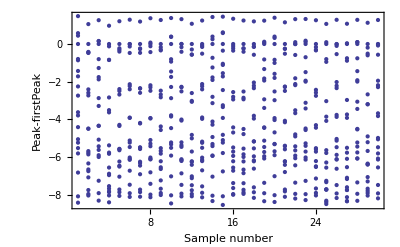

```mathematica
ListPlot[posAllMinusFirstAgainstRawSampleNumber,Frame->{True,True,False,False},FrameLabel->{"Sample number","Peak-firstPeak"}]
```

For comparison, here is the raw data

```mathematica
ListPlot[allAgainstRawSampleNumber,Frame->{True,True,False,False},FrameLabel->{"Sample number","Peak"}]
```

-Graphics-

### Plot sorted by position of first peak in list (to match diagram from paper)

```mathematica
rankOrdering[l_List,numElts_Integer,predicate_Function]:=Map[#[[2]]&,Sort[Thread[{Ordering[l,numElts,predicate],Range[Length[pos]]}]]]
```

```mathematica
rankPos=With[{rank=rankOrdering[pos,Length[pos],First[#1]<First[#2]&]},
MapThread[{#1,#2}&,{pos,rank}]];
```

```mathematica
allAgainstRank=	Flatten[Map[Function[sample,With[{r=sample[[2]],data=sample[[1]]},
Map[{#,r}&,data]]],rankPos],1];
```

```mathematica
firstAgainstRank=Map[{First[#[[1]]],#[[2]]}&,rankPos];
```

```mathematica
ListPlot[{allAgainstRank,firstAgainstRank},PlotStyle->{Red,Green},Frame->{True,True,False,False},FrameLabel->{"Peak position","Sample rank sorted by first generated peak"}]
```

-Graphics-

## 4 April 2011 Monday

### Implement beam search - description

I am going to try implementing the beam search idea with the following limitations: # peaks is same throughout and every peak is detected every time.

#### Variables

There will be a couple of variables:

initialPeakPositions: 2d array of the initial permutation of peaks: initialPeakPositions[[sample,peak]]  locations are given in ppm

beam: list of candidates with their current evaluation, sorted by evaluation

beamSize: number of candidates that will be in the beam at the start of each iteration

newCandidates: list of every possible candidate with one inversion different from a candidate in the initial beam

#### Types

candidate: each candidate is a list of permutations, one permutation per sample.  Each candidate is a potential solution.  If it is a correct solution, when each permutation is applied to the appropriate sample in initialPeakPositions, the first entries should correspond, the second entries should correspond, etc.

evaluation: an evaluation (evaluation[numEigenvalues,percentVarianceExplained] is better if there are fewer eigenvalues, but if the number of eigenvalues are equal, it is better if there is more variance explained by those eigenvalues.  This should be expanded into some notion of the compactness of the representation.

#### Functions

evaluate[candidate, initialPositions, pctVar]: applies the candidate to the given positions then calculates a PCA choosing enough eigenvectors to account for pctVar of the variance.  The evaluation returned gives the number of such eigenvectors and the proportion of the variance explained by them

isBetter[evaluation1,evaluation2]: returns true if evaluation1 is better than evaluation 2.

beamCorrespondence[peakPositions, beamSize, pctVar]: returns a candidate that gives the best correspondence found for the given peak positions

childCandidates[candidate, sampleIndex]: returns a list of all candidates that can be generated by swapping individual peaks in the sample at sampleIndex in the given candidate

applyCandidate[candidate, initialPositions]: applies the given candidate to the given list of initial positions, returning a permuted list of peak positions

### Code

```mathematica
childCandidates[candidate_List,sampleIndex_Integer]:=
With[{swaps=Append[Union[Select[Map[Sort,Tuples[Range[Length[candidate[[sampleIndex]] ] ],2]],#[[1]]≠#[[2]]&]],{1,1}],
(*TODO: Change swapped and newCandidate to use ReplacePart*)
swapped=Function[{permutation,swap},Table[Which[
i==swap[[1]],permutation[[swap[[2]]]],
i==swap[[2]],permutation[[swap[[1]]]],
True,permutation[[i]] ],{i,Length[permutation]}
]]},
With[{newCandidate=Function[swap,Table[If[i==sampleIndex,swapped[candidate[[i]],swap],candidate[[i]]],{i,Length[candidate]}]]},
Map[newCandidate,swaps]
]]
```

```mathematica
isBetter[ev1_evaluation, ev2_evaluation] := ev1[[1]] < ev2[[1]] || (ev1[[1]] == ev2[[1]] && ev1[[2]] > ev2[[2]])
```

```mathematica
applyCandidate[candidate_List, initialPositions_List]:=MapThread[#2[[#1]]&,{candidate,initialPositions}]
```

```mathematica
evaluate[candidate_List, initialPositions_List, pctVar_]/;NumberQ[pctVar]:=With[{permuted=applyCandidate[candidate,initialPositions]},
With[{varForEig=Normalize[Eigenvalues[Covariance[permuted]],Total]},
With[{cumVar=Accumulate[varForEig]},
With[{satisfiesPercent=First[First[Position[cumVar,x_/;x≥pctVar]]]},
evaluation[satisfiesPercent,cumVar[[satisfiesPercent]]]
]]]]
```

```mathematica
beamCorrespondence[peakPositions_List, beamSize_,pctVar_]/;(NumberQ[beamSize]&&NumberQ[pctVar]&&pctVar≥0&&pctVar≤1):=
With[{idPermutation=Table[Range[Dimensions[peakPositions][[2]]],{Length[peakPositions]}],
numSamples=Length[peakPositions],
numPeaks=Dimensions[peakPositions][[2]]},
With[{newBeam=Function[{oldBeam,sampleIndexToModify},
With[{children=Flatten[Map[childCandidates[#,sampleIndexToModify]&,oldBeam],1]},
With[{evaluated=Map[{#,evaluate[#,peakPositions,pctVar]}&,children]},
With[{sorted=Map[First,Sort[evaluated,isBetter[#1[[2]],#2[[2]]]&]]},
Take[sorted,beamSize]
]]]]},
With[{doIteration=Function[beam,Fold[newBeam,beam,Range[numSamples]]
]},
FixedPoint[doIteration, {idPermutation}][[1]]
]]]
```

#### Simple bench test

```mathematica
(*Note that the following could do just one inversion if it inverted the second sample first*)
```

```mathematica
beamCorrespondence[{{1,2},{2.21,1.15},{3.01,6.05}},1,9/10]
```

{{{2,1},{1,2},{2,1}}}

```mathematica
childCandidates[{{1,2},{1,2},{1,2}},1]
```

{{{2,1},{1,2},{1,2}},{{1,2},{1,2},{1,2}}}

```mathematica
idCandidate=Table[Range[20],{30}];
```

```mathematica
appliedIDCandidate=applyCandidate[idCandidate,pos];
```

```mathematica
pos==appliedIDCandidate
```

True

```mathematica
posEvaluation=evaluate[idCandidate,pos,9/10]
```

evaluation[1,0.940709]

```mathematica
(*Note that this next one uses the definition of permutedPos from the experiment looking at what happens to the eigenvalues when the values in the matrix are swapped*)
```

```mathematica
permutedPosEvaluation=evaluate[idCandidate,permutedPos,9/10]
```

evaluation[2,0.969265]

```mathematica
isBetter[posEvaluation,permutedPosEvaluation]
```

True

```mathematica
isBetter[permutedPosEvaluation,posEvaluation]
```

False

```mathematica
isBetter[posEvaluation,posEvaluation]
```

False

```mathematica
childCandidates[{{1,2},{3,4}},2]
```

{{{1,2},{4,3}},{{1,2},{3,4}}}

```mathematica
childCandidates[{{1,2,3},{3,4}},1]
```

{{{2,1,3},{3,4}},{{3,2,1},{3,4}},{{1,3,2},{3,4}},{{1,2,3},{3,4}}}

#### Code for permuted items eigenvalue test

```mathematica
meanCenterSamples[samples_List]:=With[{means=Mean[samples]},Map[#-means&,samples]]
```

```mathematica
adjustedRSquareds::usage="adjustedRSquareds[rsquareds, sampleSize] Given a list of R^2 values for each potential variable in a PCA model and the sample size from which the model was derived, uses the formula for adjusted R^2 from Wikipedia to calculate an estimate of the variance explained for the composite model that accounts for the size of the model.";
```

```mathematica
adjustedRSquareds[rsquareds_List,sampleSize_Integer]:=With[{cumRSq=Accumulate[rsquareds]},MapThread[Function[{rsq,p},1-((1-rsq)(sampleSize-1)/(sampleSize-p-1))],{cumRSq,Range[Length[rsquareds]]}]]
```

### See what happens to eigenvalue list when items are permuted

```mathematica
permutedPos=pos;
```

```mathematica
{permutedPos[[1,1]],permutedPos[[1,2]]}={permutedPos[[1,2]],permutedPos[[1,1]]}
```

{1.79079,8.54244}

```mathematica
{permutedPos[[1,1]],permutedPos[[1,2]]}
```

{1.79079,8.54244}

```mathematica
{pos[[1,1]],pos[[1,2]]}
```

{8.54244,1.79079}

```mathematica
MatrixRank[meanCenterSamples[permutedPos]]
```

4

p2pos is permutedPermutedPos (permute a second element)

```mathematica
p2pos=permutedPos;
```

```mathematica
{p2pos[[2,3]],p2pos[[2,5]]}={p2pos[[2,5]],p2pos[[2,3]]};
```

```mathematica
MatrixRank[meanCenterSamples[p2pos]]
```

5

```mathematica
p2posRSquareds=Normalize[#^2&/@SingularValueList[meanCenterSamples[p2pos]],Total]
```

{0.634855,0.319313,0.025804,0.0142224,0.00580569}

```mathematica
Normalize[Eigenvalues[Covariance[meanCenterSamples[p2pos]]],Total] (*Verify that the singular values of the mean-centered matrix are indeed the square roots of the eigenvalues*)
```

{0.634855,0.319313,0.025804,0.0142224,0.00580569,-1.37986×10^-16,7.73308×10^-17,-7.33128×10^-17,6.63941×10^-17,-4.79549×10^-17,-2.69968×10^-17,2.58742×10^-17,1.2538×10^-17,-1.23165×10^-17,-6.76716×10^-18,4.70851×10^-18,-3.39183×10^-18,-1.97652×10^-18,1.34887×10^-18,3.48221×10^-19}

```mathematica
Accumulate[p2posRSquareds]
```

{0.634855,0.954168,0.979972,0.994194,1.}

```mathematica
adjustedRSquareds[p2posRSquareds,Length[p2pos]]
```

{0.621814,0.950773,0.977661,0.993265,1.}

```mathematica
permutedPosRSquareds=Normalize[#^2&/@SingularValueList[meanCenterSamples[permutedPos]],Total]
```

{0.645185,0.32408,0.0221624,0.00857246}

```mathematica
Accumulate[permutedPosRSquareds]
```

{0.645185,0.969265,0.991428,1.}

```mathematica
adjustedRSquareds[permutedPosRSquareds,Length[permutedPos]]
```

{0.632513,0.966988,0.990438,1.}

```mathematica
Normalize[Eigenvalues[Covariance[permutedPos]],Total]
```

{0.645185,0.32408,0.0221624,0.00857246,9.51846×10^-17,-7.9391×10^-17,-5.50015×10^-17,2.76457×10^-17,-2.75428×10^-17,-2.16227×10^-17,1.8312×10^-17,-1.41181×10^-17,-9.35058×10^-18,7.33525×10^-18,-6.33149×10^-18,4.10511×10^-18,-3.34419×10^-18,2.53761×10^-18,8.01315×10^-19,1.95031×10^-19}

```mathematica
MatrixRank[Covariance[pos]]
```

3

```mathematica
posRSquareds=Normalize[#^2&/@SingularValueList[meanCenterSamples[pos]],Total]
```

{0.940709,0.0477953,0.0114957}

```mathematica
Accumulate[posRSquareds]
```

{0.940709,0.988504,1.}

## 5 April 2011 Tuesday

### Write code for generating a set of peaks and the permutation that would return it to the original

#### Peak generation code

```mathematica
randomPeaksAndPermutation::usage="randomPeaksAndPermutation[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange] 

Returns a list of rules {\"peaks\"→...,\"permutation\"→...}.

\"peaks\" gives a list of samples, each sample is a list of peaks sorted by their location.

\"permutation\" gives a list of permutations that, when applied to the corresponding sample, will make the i^th position in that sample contain the position of the i^th peak.  Thus, after applying all the permutations, the corresponding positions in the sample will contain corresponding peaks.

numPeaks and numSamples determine how many peaks and samples will be generated

Each sample has a number of latent factors s_j.  Each peak has the same number of latent response variables a_i.  Each peak also has a base location k_i.  The latent factors are selected from a multidimensional Gaussian with mean 0 and standard deviations given by factorStdDev.  Similarly the responses are selected from a Gaussian with mean 0 and standard deviations in peakResponseStdDev.  The peak means are selected independently from a uniform distribution over peakRange.

The i^th peak in the j^th sample is given a location:
δ_ij=k_i+a_i·s_j+ξ_ij

Where ξ_ij is a normally distributed random variable with mean 0 and standard deviation noiseStdDev.";
```

```mathematica
randomPeaksAndPermutation[numPeaks_Integer,numSamples_Integer,factorStdDev_List,noiseStdDev_,peakResponseStdDev_List,peakRange_List]/;Length[factorStdDev]==Length[peakResponseStdDev]&&NumberQ[noiseStdDev]&&noiseStdDev>0&&Length[peakRange]==2:=
With[{
s=Table[factorStdDev RandomReal[NormalDistribution[0,1],Length[factorStdDev]],{numSamples}],
a=Table[peakResponseStdDev RandomReal[NormalDistribution[0,1],Length[peakResponseStdDev]],{numPeaks}],
k=RandomReal[peakRange,numPeaks]},
With[{rawPos=Map[Function[sj,MapThread[Function[{ai,ki},ki+Dot[ai, sj]+RandomReal[NormalDistribution[0,noiseStdDev]]],{a,k}]],s]},
With[{sortOrdering=Map[Ordering,rawPos],
sortedPos=Map[Sort,rawPos]},
With[{unsortOrdering=Map[Ordering,sortOrdering]},
{"peaks"->sortedPos,"permutation"->unsortOrdering}
]]]]
```

#### Peak plotting code

```mathematica
asPeakPlotTuples::usage ="asPeakPlotTuples[peaks]
Returns a list of two lists, the first is a list of pairs of the peak locations in each sample plotted against the first peak location in that sample and the second is the first point in each sample plotted against itself.  If fed to ListPlot, it will show the ordering obtained by accounting for the variation in the first peak.";
```

```mathematica
asPeakPlotTuples[peaks_List]:=
With[{firsts=Map[First,peaks]},
With[{pairs=Flatten[MapThread[Function[{sample,first},Map[{#,first}&,sample]],{peaks,firsts}],1]},
{pairs,Map[{#,#}&,firsts]}]]
```

```mathematica
asSortedPlotTuples::usage ="asSortedPlotTuples[peaks]
Returns a list of two lists, the first is a list of pairs of the peak locations in each sample plotted against the sample number in that sample and the second is the first point in each sample plotted against the sample.  The samples are sorted according to the location of the location of the first peak.  

If fed to ListPlot, it will show the ordering obtained by accounting for the variation in the first peak as would be obtained by sorting according to one peak's location.";
```

```mathematica
asSortedPlotTuples[unsortedPeaks_List]:=
With[{sortedPeaks=Sort[unsortedPeaks,First[#1]<First[#2]&]},
With[{listOfPairs=MapThread[Function[{sample,sampleNum},Map[{#,sampleNum}&,sample]],{sortedPeaks,Range[Length[sortedPeaks]]}]},
{Flatten[listOfPairs,1],Map[First,listOfPairs]}
]]
```

#### Peak plotting code usage examples

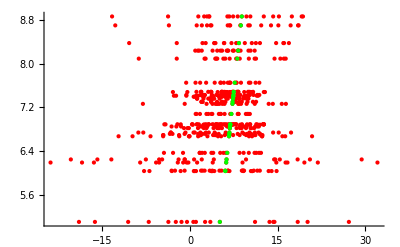

```mathematica
With[{raw=randomPeaksAndPermutation[20,30,{0.7,0.5,0.2},0.2,{10,1,1},{0,11}]},
With[{pks="peaks"/.raw,perm="permutation"/.raw},
ListPlot[asPeakPlotTuples[applyCandidate[perm,pks]],PlotStyle->{Red,Green}]
]]
```

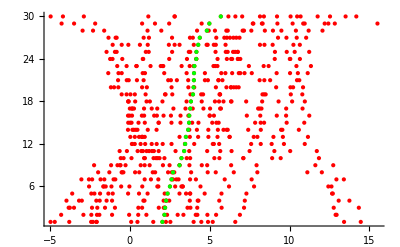

```mathematica
With[{raw=randomPeaksAndPermutation[20,30,{1,1,0.1},0.1,{3,0.5,1},{0,11}]},
With[{pks="peaks"/.raw,perm="permutation"/.raw},
ListPlot[asSortedPlotTuples[applyCandidate[perm,pks]],PlotStyle->{Red,Green}]
]]
```

### Write code for determining the % error between an ideal permutation and a calculated one

Since we only care about correspondence not the actual ordering in which the peaks were originally generated, we can sort the two correspondences based on their first permutation.

#### Difference code

```mathematica
fracDifferent::usage="fracDifferent[perm1,perm2] 
Returns the fraction of correspondences that are different between the two permutations"
```

fracDifferent[perm1,perm2] 
Returns the fraction of correspondences that are different between the two permutations

```mathematica
fracDifferent[perm1_List,perm2_List]/;Dimensions[perm1]==Dimensions[perm2]&&Length[perm1]≥1:=
With[{o1=Ordering[perm1[[1]]],o2=Ordering[perm2[[1]]]},
With[{sortP1=Map[#[[o1]]&,perm1],sortP2=Map[#[[o2]]&,perm2]},
With[{numDiff=MapThread[HammingDistance,{sortP1,sortP2}]},
Total[numDiff]/(Times@@(Dimensions[perm1]))
]]]
```

#### Bench test difference code

Each test below should be true

```mathematica
And[
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{2,3,1},{1,2,3}}]==0,
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{1,2,3},{1,2,3}}]==1/3,
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{3,2,1},{1,2,3}}]==2/9,
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{3,2,1},{1,3,2}}]==4/9
]
```

True

### Test beam search algorithm accuracy using synthetic data - it fails

#### Test one randomly chosen test sample - doesn't produce good results

```mathematica
With[{raw=randomPeaksAndPermutation[5,5,{1,0.1,0.01},0.0001,{1,1,1},{0,11}]},
With[{peaks="peaks"/.raw,correctPerm="permutation"/.raw},
With[{beamPerm=beamCorrespondence[peaks,1,90/100]},
fracDifferent[correctPerm,beamPerm]
]]]
```

1/5

#### Look at raw data - the permutation found by the beam search has a better evaluation than the true model

```mathematica
oneTestRun=With[{raw=randomPeaksAndPermutation[5,5,{1,0.1,0.01},0.0001,{1,1,1},{0,11}]},
With[{peaks="peaks"/.raw,correctPerm="permutation"/.raw},
With[{beamPerm=beamCorrespondence[peaks,5,9999/10000]},
With[{oCorrect=Ordering[correctPerm[[1]]],oBeam=Ordering[beamPerm[[1]]]},
{"correct"->Map[#[[oCorrect]]&,correctPerm],"beam"->Map[#[[oBeam]]&,beamPerm],"peaks"->peaks,"error"->fracDifferent[correctPerm,beamPerm]}
]]]]
```

{correct→{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}},beam→{{1,2,3,4,5},{1,2,3,4,5},{1,5,3,4,2},{1,2,3,4,5},{1,5,3,4,2}},peaks→{{0.982303,3.63468,5.27682,7.31836,10.611},{1.09605,3.54101,5.11142,7.303,10.5128},{0.614794,3.96991,5.75573,7.35231,10.6706},{2.05887,2.34062,3.69852,7.16685,10.2326},{0.0335904,4.72263,6.62224,7.43858,10.85}},error→4/25}

```mathematica
pks="peaks"/.oneTestRun
```

{{0.982303,3.63468,5.27682,7.31836,10.611},{1.09605,3.54101,5.11142,7.303,10.5128},{0.614794,3.96991,5.75573,7.35231,10.6706},{2.05887,2.34062,3.69852,7.16685,10.2326},{0.0335904,4.72263,6.62224,7.43858,10.85}}

```mathematica
correct="correct"/.oneTestRun
```

{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
beam="beam"/.oneTestRun
```

{{1,2,3,4,5},{1,2,3,4,5},{1,5,3,4,2},{1,2,3,4,5},{1,5,3,4,2}}

```mathematica
evaluate[correct,pks,9999/10000]
```

evaluation[3,1.]

```mathematica
evaluate[beam,pks,9999/10000]
```

evaluation[2,0.999999]

## 7 April 2011 Thursday

### Theoretical background to cross-validation evaluation function

I want to try to come up with a routine that uses cross-validation to evaluate model fit.  One open question is whether to use the minimum or average value over all folds as the evaluation.

I spent several hours calculating to discover that (if samples are in columns) then the shift factors (s in the paper) are the columns of the transformed samples and the reaction factors are the columns of the PCA eigenvector matrix.  If X is the mean-centered data, we have X=ΑS where A=P^T=P^-1 where P is the matrix of eigenvectors of the covariance matrix 1/(n-1)X X^T.  This relationship still holds even if you grab only the most significant eigenvectors.

## 11-13 April 2011 Monday-Wednesday

Discuss and investigate different options for version control and hosting for the development of the metabolomics code.

## 14 April 2011 Thursday

### Install fresh ubuntu on bio-db

### Work on creating evaluation based on cross-validation

#### First attempt is to use the expectation maximization algorithm

The following is a direct translation from the paper (I didn't use the missing values formulation yet).  I can't get it to work

```mathematica
emPCA[y_List,numEigenvectors_Integer]:=With[
{eStep = Function[c,With[{ct=Transpose[c]},Inverse[ct.c].ct.y]],
mStep=Function[x,With[{xt=Transpose[x]},y.xt.Inverse[x.xt]]]},
With[{iteration=Function[c,mStep[eStep[c]]],
initialMatrix=
Table[RandomReal[{-1/(1+numEigenvectors),1/(1+numEigenvectors)},numEigenvectors],{Length[y]}]},
FixedPoint[iteration,initialMatrix]
]]
```

```mathematica
Dimensions[testPCAValues]
```

{10,3}

#### I can't get it to work because it doesn't

Here I demonstrate symbolically that the steps given in the paper will always yield the same estimate for c when there are two eigenvectors for a space of 2D points.  I, however, saw the same equations (with different letters) in another paper.  So, there must be something I am not understanding here.

```mathematica
y=Transpose[{{a,b},{k,d},{e,f},{l,m}}]
```

{{a,k,e,l},{b,d,f,m}}

```mathematica
c={{g,h},{i,j}}
```

{{g,h},{i,j}}

```mathematica
ct=Transpose[c]
```

{{g,i},{h,j}}

```mathematica
x=Inverse[ct.c].ct.y
```

{{a ((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2))+b ((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)),d ((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2))+((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)) k,e ((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2))+f ((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)),((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)) l+((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)) m},{a ((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2))+b (((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)),d (((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2))+((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)) k,e ((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2))+f (((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)),((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)) l+(((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)) m}}

```mathematica
xt=Transpose[x];
```

```mathematica
cnew=Simplify[y.xt.Inverse[x.xt]]
```

{{g,h},{i,j}}

```mathematica
c=cnew
```

{{0.0300051,0.0431783,-0.0176582},{-0.149382,0.144852,0.226486},{-0.0168415,-0.221313,0.0661678}}

```mathematica
Clear[c,ct,cnew,x,xt,y]
```

#### Here is some old code I used to test my implementation and discover that it didn't work

```mathematica
testPCAValues=
With[{rotxy=RotationTransform[π/4,{{1,0,0},{0,1,0}}]},Table[rotxy[{1,5,2} RandomReal[NormalDistribution[0,1],3]],{10}]
];
```

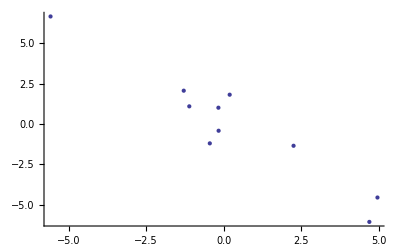

```mathematica
ListPlot[{First[#],#[[2]]}&/@testPCAValues]
```

```mathematica
Eigenvectors[Covariance[testPCAValues]]
```

{{0.645036,-0.760198,-0.0776321},{0.139212,0.0170112,0.990116},{0.751364,0.649468,-0.116801}}

```mathematica
emPCA[Transpose[testPCAValues],3]
```

{{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}}}

## 15 April 2011 Friday

### Try a different approach to see if EM method works

Maybe it didn't work because my eigenvector matrix had all included.  It doesn't give the same result.  Whether it converges to something or not, I'll have to check in the sequel.

```mathematica
y=Transpose[{{a,b},{k,d},{e,f},{l,m}}]
```

{{a,k,e,l},{b,d,f,m}}

```mathematica
c={{g},{h}}
```

{{g},{h}}

```mathematica
ct=Transpose[c]
```

{{g,h}}

```mathematica
x=Inverse[ct.c].ct.y
```

{{(a g)/(g^2+h^2)+(b h)/(g^2+h^2),(d h)/(g^2+h^2)+(g k)/(g^2+h^2),(e g)/(g^2+h^2)+(f h)/(g^2+h^2),(g l)/(g^2+h^2)+(h m)/(g^2+h^2)}}

```mathematica
xt=Transpose[x];
```

```mathematica
cnew=Simplify[y.xt.Inverse[x.xt]]
```

{{((g^2+h^2) (a^2 g+e^2 g+a b h+e f h+d h k+g k^2+g l^2+h l m))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)},{((g^2+h^2) (a b g+e f g+b^2 h+d^2 h+f^2 h+d g k+g l m+h m^2))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)}}

```mathematica
c=cnew
```

{{((g^2+h^2) (a^2 g+e^2 g+a b h+e f h+d h k+g k^2+g l^2+h l m))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)},{((g^2+h^2) (a b g+e f g+b^2 h+d^2 h+f^2 h+d g k+g l m+h m^2))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)}}

```mathematica
Clear[c,ct,cnew,x,xt,y]
```

### I tried testing the EM method with fewer eigenvectors — it still doesn't work

```mathematica
testPCAValues=
With[{rotxy=RotationTransform[π/4,{{1,0,0},{0,1,0}}]},Table[rotxy[{1,5,2} RandomReal[NormalDistribution[0,1],3]],{20}]
];
```

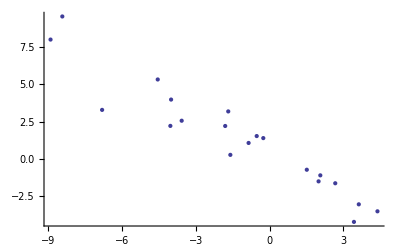

```mathematica
ListPlot[{First[#],#[[2]]}&/@testPCAValues]
```

```mathematica
Eigenvectors[Covariance[testPCAValues]]
```

{{-0.74049,0.672054,-0.00431347},{0.0236204,0.0324388,0.999195},{-0.671653,-0.739791,0.0398948}}

```mathematica
emPCA[Transpose[testPCAValues],1]
```

$Aborted

### Tried writing cross-validation without using missing values

This section also includes work I did on 19 April.  It relies on the description of PCA and SVD given in Practical approaches to principal component analysis in the presence of missing values by Ilin and Raiko.  That description is available in many places, but I wanted to note where I got it.

This section also includes bug fixes from 21 April and 22 April

```mathematica
wxDecompose::usage="wxDecompose[matrix,fracVar,minComponents]
Given a matrix whose columns have data and whose rows have zero mean, decomposes it into W and X so that W.X≈the original matrix and they have at least minComponents dimensions and sufficient dimensions to capture fracVar fraction of the variance 

See 19 April 2011 for how wx decomposition relates to sample and peak parameter sets

Returns {W,X}";
```

```mathematica
wxDecompose[matrix_List,fracVar_,minComponents_Integer:0]/;Length[Dimensions[matrix]]==2&&NumberQ[fracVar]:=
With[{svd=SingularValueDecomposition[matrix]},
With[{u=svd[[1]],Σ=svd[[2]], vt=ConjugateTranspose[svd[[3]]],numSing=Min[Dimensions[svd[[2]]]]},
With[{singularValues=Map[Σ[[#,#]]&,Range[numSing]]},
With[{fracVariances=Normalize[singularValues singularValues,Total]},
With[{cumulativeVars=Accumulate[fracVariances]},
With[{componentsForFracvar=First[First[Position[cumulativeVars,x_/;x≥fracVar,1]]]},
With[{componentsRequired=Max[minComponents,componentsForFracvar]},
With[{w=Transpose[Transpose[u][[Range[componentsRequired]]]],x=(Σ.vt)[[Range[componentsRequired]]]},
{w,x}
]]]]]]]]
```

```mathematica
reactionParameters::usage="reactionParameters[positions,excludedSamples,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  Samples at indices given by excludedSamples are not used to create the estimatereactionParameters

positions is an array of dimensions samples×peaks

Returns {means,reactionCoefficients} where means is a 1×peaks array and reactionCoefficients is a peaks×d array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger";
```

```mathematica
reactionParameters[positions_List, excludedSamples_List,fracVar_,minComponents_Integer:0]/;NumberQ[fracVar]:=
With[{includedSamples=Complement[Range[Length[positions]],excludedSamples]},
With[{editedPositions=positions[[includedSamples]]},
With[{means=Mean[editedPositions]},
With[{meanCenteredPos=Map[#-means&,editedPositions]},
With[{wxd=wxDecompose[Transpose[meanCenteredPos],fracVar,minComponents]},
With[{w=wxd[[1]],x=wxd[[2]]},
{means, w}
]]]]]]
```

```mathematica
sampleParameters::usage="sampleParameters[positions,excludedPeaks,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  peaks at indices given by excludedPeaks are not used to create the estimate

positions is an array of dimensions samples×peaks

Returns sampleCoefficients, a d×samples array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger";
```

```mathematica
sampleParameters[positions_List, excludedPeaks_List,fracVar_,minComponents_Integer:0]/;NumberQ[fracVar]:=
With[{includedPeaks=Complement[Range[Dimensions[positions][[2]]],excludedPeaks]},
With[{editedPositions=Transpose[Transpose[positions][[includedPeaks]]]},
With[{means=Mean[editedPositions]},
With[{meanCenteredPos=Map[#-means&,editedPositions]},
With[{wxd=wxDecompose[Transpose[meanCenteredPos],fracVar,minComponents]},
With[{w=wxd[[1]],x=wxd[[2]]},
x
]]]]]]
```

```mathematica
evaluationExcludingData::usage="estimationError[positions,testSamples,testPeaks,fracVar]
Returns an evaluation object from estimating the testPeaks peaks in the testSamples samples using the data from the rest of the corresponding peak positions and the hough-transform linear model - in this case, gives negative root sum of squared error (rather than variance accounted for) and the number of dimensions required to get it

LIMITATION: does not handle the case where the number of principal components in one direction is greater than the number of training variables in the other direction (and thus greater than the maximum number of variables the other can supply) -- TODO: need to fix this
";
```

```mathematica
evaluationExcludingData[positions_List, testSamples_List, testPeaks_List, fracVar_]/;NumberQ[fracVar]:=
Module[{
sampCoeff=sampleParameters[positions,testPeaks,fracVar],
reactCoeff=reactionParameters[positions,testSamples,fracVar]},
With[{reactCompNeeded=Dimensions[reactCoeff[[2]]][[2]],sampCompNeeded=Length[sampCoeff]},
reactCoeff=If[reactCompNeeded<sampCompNeeded,reactionParameters[positions,testSamples,fracVar,sampCompNeeded],reactCoeff];
sampCoeff=If[sampCompNeeded<reactCompNeeded,sampleParameters[positions,testPeaks,fracVar,reactCompNeeded],sampCoeff];
With[{estimatedPositions=Map[#+First[reactCoeff]&,Transpose[reactCoeff[[2]].sampCoeff]]},
With[{errors=positions-estimatedPositions,prinCompNeeded=Max[reactCompNeeded,sampCompNeeded]},
With[{testErrors=Transpose[Transpose[errors[[testSamples]]][[testPeaks]]]},
evaluation[prinCompNeeded,-Norm[testErrors,"Frobenius"]]
]]]]]
```

## 18 April 2011 Monday

### Investigate using techniques from compressed sampling for peak matching

#### The technique

Compressed sampling reconstructs a sparse coefficient matrix from a random sample of a signal.  Let f be a big vector containing the signal.  We assume that there is a basis in which f  is sparse, that is, if β is a matrix of basis vectors and c is a sparse matrix of coefficients.

f=β c

Further, if ϕ is a sampling operator matrix (could be a subset of the identity matrix, for a random sample, or could be another matrix involving sampling averages of several function values) we can construct b, a sample of f, by writing

b=ϕ f

Note that ϕ has to carry a significant amount of information.  For example, if all the entries in ϕ are the same, then each sample adds no new information, and the problem cannot be solved.  If the samples all come from the beginning of the signal, then certain components may not be able to be reconstructed (this will depend on how the information about the signal is spread over the sparse basis vectors).

The reconstruction takes place by solving for

A x = b where A = ϕ β, that is, where A is a sample of the basis vectors.

Then we approximate f by f ≈ β x.

Since the sampling matrix takes a very small subset of the original vectors, the system of equations, A x = b is underdetermined.  The magic of the compressed reconstruction is to assume that c is sparse.  Then it turns out that (1) maximizing sparsity usually gives a unique solution (2) that solution is highly likely to be the correct one (3) you can maximize sparsity by minimizing the L_1 norm of x with the linear constraints given by A and b.

#### Why I was interested

I saw a linear combination involving a sparse matrix and thought such a linear combination resembles what we are doing.  In particular a permutation matrix is a sparse matrix and the β matrix bears a resemblance to the linear model

#### Why I don't think it will work now

The technique requires knowing a sampling matrix and the matrix of basis vectors, or, at least their product.  This doesn't seem to translate well to our problem where we'd have to a priori know the linear model (peak responses and sample parameters) which would take the place of the basis vectors.

#### Potential profit

The idea of being able to solve for the permutation by minimizing the L_1 norm of a particular matrix with constraints determined by the peak samples is still intriguing to me.  I have a feeling I might be able to make something out of this.

### Meet with Dan and Paul

We discussed moving from sending matlab scripts around to sending platform-dependent executables.

The scientists have trouble finding which thing they should click on to accomplish their tasks amid the myriad of .m files.

In order to do the deployment, we'll have VMs of Linux, Windows, and OS X running.  We run the Matlab deployment in each of these.

Further, for our development of the website code, we'll distribute a VM containing an ubuntu system on which rails etc has been already configured.  Then the current code can be downloaded into this VM and developers can run it within the VM, all having the same setup as the final deployment platform.  We may just run the final deployment as another instance of this VM.  But not sure if it would be too slow.  The benefits of VMWare and VirtualBox were discussed and it seems (from a cursory inspection of benchmarks) that they are the same.  Dan, however, has a bad experience running a game-server on VirtualBox, but it worked better under VMWare.

In order to run the deployment virtual machines on the development server, we decided to install ubuntu desktop (since virtualbox apparently can't run without an x server).  I'm not sure about that, but I don't do system administration.

## 19 April 2011 Tuesday

### Cross-validation evaluation fit

#### Completed existing code

I modified the code for cross validation under April 15^th.  Made it functional

#### Bench Tested

##### wxDecompose

Combining gives back initial matrix

Check that combining the decomposition gives us back our initial matrix

```mathematica
{w,x} =With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
wxDecompose[mc,1]
]]]
```

{{{-3/(2 √5)},{-1/(2 √5)},{1/(2 √5)},{3/(2 √5)}},{{√5,3 √5,2 √5}}}

Here is the original matrix

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
mc
]]]
```

{{-3/2,-9/2,-3},{-1/2,-3/2,-1},{1/2,3/2,1},{3/2,9/2,3}}

Here is w.x

```mathematica
w.x
```

{{-3/2,-9/2,-3},{-1/2,-3/2,-1},{1/2,3/2,1},{3/2,9/2,3}}

It is the eigenvectors of mc (the mean centered matrix) times its transpose.

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
Normalize/@Eigenvectors[mc.Transpose[mc]]
]]]
```

{{-3/(2 √5),-1/(2 √5),1/(2 √5),3/(2 √5)},{1/(√2),0,0,1/(√2)},{1/(√10),0,3/(√10),0},{-1/(√10),3/(√10),0,0}}

```mathematica
With[{p={{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}},Covariance[p]]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
With[{p={{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}},Covariance[Transpose[p]]]
```

{{5/3,5,10/3},{5,15,10},{10/3,10,20/3}}

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
mc.Transpose[mc]
]]]
```

{{63/2,21/2,-21/2,-63/2},{21/2,7/2,-7/2,-21/2},{-21/2,-7/2,7/2,21/2},{-63/2,-21/2,21/2,63/2}}

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
Transpose[mc].mc
]]]
```

{{5,15,10},{15,45,30},{10,30,20}}

Try to recover w and x from w.x

Looking at it later, this is a fool's errand - you need to make sure that the maximum variance is along the axes before you can recover the matrices

```mathematica
Normalize[{2, 0, 2, -1}]
```

{2/3,0,2/3,-1/3}

```mathematica
x=.
```

Find some nice unit vectors

```mathematica
rational4DUnitVectorsFromRange[maxElt_Integer]:=With[{r=maxElt},
Normalize/@With[{range=Range[2 r+1]-r-1},Select[Tuples[{range,range,range,range}],Function[{l},With[{len=Norm[l]},len ≠ 0&&And@@Map[Element[#/len,Rationals]&,l]]]]
]]
```

```mathematica
Sort[DeleteDuplicates[rational4DUnitVectorsFromRange[7],Sort[Abs[#1]]==Sort[Abs[#2]]&],Max[Denominator/@#1]<Max[Denominator/@#2]&]
```

{{-1,0,0,0},{-1/2,-1/2,-1/2,-1/2},{-2/3,-2/3,-1/3,0},{-4/5,-2/5,-2/5,-1/5},{-4/5,-3/5,0,0},{-5/6,-1/2,-1/6,-1/6},{-4/7,-4/7,-4/7,-1/7},{-5/7,-4/7,-2/7,-2/7},{-6/7,-3/7,-2/7,0},{-2/3,-5/9,-4/9,-2/9},{-7/9,-4/9,-4/9,0},{-7/10,-1/2,-1/2,-1/10},{-7/10,-7/10,-1/10,-1/10},{-7/11,-6/11,-6/11,0}}

It looks like any orthogonal basis w with only two basis vectors that will produce a zero mean requires that the two rows of the x vector be linearly dependent.  (Though I only tried two different w1 vectors)

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2={ea,eb,ec,ed}},Reduce[Mean[Transpose[{w1,w2}].{{aa,ab,ac,ad},{ba,bb,bc,bd}}]=={0,0,0,0}&&w1.w2==0]]]
```

5 ea+3 eb+ec+ed==0&&25 ad==6 bd (eb+2 (ec+ed))&&25 ac==6 bc (eb+2 (ec+ed))&&25 ab==6 bb (eb+2 (ec+ed))&&25 aa==6 ba (eb+2 (ec+ed))

So, I need to try a 3D basis

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2={ea,eb,ec,ed},w3={fa,fb,fc,fd}},Reduce[Mean[Transpose[{w1,w2,w3}].{{aa,ab,ac,ad},{ba,bb,bc,bd},{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0&&Norm[w3]≠0&&Norm[w2]≠0]]]
```

((eb≠0&&eb+9 ec==0&&eb+9 ed==0&&fb==0&&√((25 Abs[eb]^2+25 Abs[ec]^2+25 Abs[ed]^2+Abs[3 eb+ec+ed]^2) (25 Abs[fc]^2+25 Abs[fd]^2+Abs[fc+fd]^2))≠0)||(√((25 Abs[eb]^2+25 Abs[ec]^2+25 Abs[ed]^2+Abs[3 eb+ec+ed]^2) (25 Abs[fb]^2+25 Abs[fc]^2+25 Abs[fd]^2+Abs[3 fb+fc+fd]^2))≠0&&((3 eb+ec+26 ed==0&&((35 eb+3 ec) fb)/(3 (eb+9 ec))+fc==0&&eb+9 ec≠0)||((34 eb fb+3 ec fb+3 ed fb+3 eb fc+26 ec fc+ed fc)/(3 eb+ec+26 ed)+fd==0&&3 eb+ec+26 ed≠0))))&&5 fa+3 fb+fc+fd==0&&5 ea+3 eb+ec+ed==0&&5 ad==3 (bd (ea+eb+ec+ed)+cd (fa+fb+fc+fd))&&5 ac==3 (bc (ea+eb+ec+ed)+cc (fa+fb+fc+fd))&&5 ab==3 (bb (ea+eb+ec+ed)+cb (fa+fb+fc+fd))&&5 aa==3 (ba (ea+eb+ec+ed)+ca (fa+fb+fc+fd))

That looks more promising.  Substitue numbers and see how things simplify then substitute again until we get a tautology.

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2={-10/13,1,1,-2/13},w3={1/5,-15/13,19/13,1}},Reduce[Mean[Transpose[{w1,w2,w3}].{42/325{ba+ca,bb+cb,bc+cc,bd+cd},1/5{ba,bb,bc,bd},1/7{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0&&Norm[w3]≠0&&Norm[w2]≠0]]]
```

True

But when we make the vectors unit - there is a problem - b becomes a multiple of c, continuing anyway for now

```mathematica
With[{w1={-5/6,-1/2,-1/6,-1/6},w2={-5 √(2/221),√(13/34),√(13/34),-√(2/221)},w3={13/138,-25/46,95/138,65/138}},
With[{x2=1/5{ba,bb,bc,bd},x3=1/7{ca,cb,cc,cd}},
With[{x1=42/325(5x2+7x3)},
Reduce[Mean[Transpose[{w1,w2,w3}].{x1,x2,x3}]=={0,0,0,0}]
]]]
```

bd==(1241 cd)/(69 (-34+√442))&&bc==(1241 cc)/(69 (-34+√442))&&bb==(1241 cb)/(69 (-34+√442))&&ba==(1241 ca)/(69 (-34+√442))

```mathematica
With[{w1={-5/6,-1/2,-1/6,-1/6},w2={-10/13,1,1,-2/13},w3={1/5,-15/13,19/13,1}},
With[{x2=1/5{1,2,3,4},x3=1/7{1,3,3,1}},
With[{x1=42/325(5x2+7x3)},
{Evaluate[Transpose[{w1,w2,w3}]],Evaluate[{x1,x2,x3}]}
]]]
```

{{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

Now, I can substitue my favorite numbers in for the b and c vectors and get my test data.

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},px={{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}},{0,0,0,0},{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

```mathematica
Transpose[Normalize/@Transpose[testResultPw]]//N
```

{{-0.833333,-0.475651,0.0942029},{-0.5,0.618347,-0.543478},{-0.166667,0.618347,0.688406},{-0.166667,-0.0951303,0.471014}}

```mathematica
Normalize/@testResultPx//N
```

{{0.210819,0.527046,0.632456,0.527046},{0.182574,0.365148,0.547723,0.730297},{0.223607,0.67082,0.67082,0.223607}}

```mathematica
{w,x}= wxDecompose[testResultMc//N,1]
```

{{{0.69989,-0.30243},{0.0935089,0.849027},{-0.702206,-0.134908},{-0.0911933,-0.41169}},{{-0.51032,-1.24003,-1.53096,-1.38313},{-0.0545877,-0.355264,-0.163763,0.519916}}}

Maybe I have to have w=orthogonal unit vectors to get it back from the decomposition

```mathematica
rotated4DUnit[θ1_,θ2_,θ3_]:=With[{u1={1,0,0,0},u2={0,1,0,0},u3={0,0,1,0},u4={0,0,0,1}},
RotationTransform[θ1,{u2,u1}][
RotationTransform[θ2,{u3,u2}][
RotationTransform[θ3,{u4,u3}][u4
]]]]
```

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2=rotated4DUnit[e1,e2,e3],w3=rotated4DUnit[f1,f2,f3]},Reduce[Mean[Transpose[{w1,w2,w3}].{{aa,ab,ac,ad},{ba,bb,bc,bd},{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0]
]]
```

$Aborted

```mathematica
Simplify[With[{w1={0,0,0,1},w2={0,0,1,0},w3={0,1,0,0}},Reduce[Mean[Transpose[{w1,w2,w3}].{{aa,ab,ac,ad},{ba,bb,bc,bd},{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0]
]]
```

ad+bd+cd==0&&ac+bc+cc==0&&ab+bb+cb==0&&aa+ba+ca==0

```mathematica
With[{w1={0,0,0,1},w2={0,0,1,0},w3={0,1,0,0}},Transpose[{w1,w2,w3}]
]
```

{{0,0,0},{0,0,1},{0,1,0},{1,0,0}}

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{0,0,0},{0,0,1},{0,1,0},{1,0,0}},px={{1,2,3,4},{-1,-1,-2,-2},{0,-1,-1,-2}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{0,0,0,0},{0,-1,-1,-2},{-1,-1,-2,-2},{1,2,3,4}},{0,0,0,0},{{0,0,0},{0,0,1},{0,1,0},{1,0,0}},{{1,2,3,4},{-1,-1,-2,-2},{0,-1,-1,-2}}}

```mathematica
{w,x}=Simplify[ wxDecompose[testResultMc,1]]
```

{{{0},{(-5125-920 √31)/(√(424124764+76175054 √31))},{-(3 (2243+403 √31))/(√(424124764+76175054 √31))},{(11854+2129 √31)/(√(424124764+76175054 √31))}},{{1/165 √(1669/3-18583/(6 √31)) (409+74 √31),1/55 √(1669/3-18583/(6 √31)) (262+47 √31),1/33 √(1669/3-18583/(6 √31)) (239+43 √31),1/55 √(6676/3-37166/(3 √31)) (262+47 √31)}}}

```mathematica
FullSimplify[w.x]
```

{{0,0,0,0},{-5/(2 √31),-1/2-2/(√31),-1/2-9/(2 √31),-1-4/(√31)},{-1/2-1/(2 √31),-1/2-7/(2 √31),-1-4/(√31),-1-7/(√31)},{1/2+3/(√31),1+11/(2 √31),3/2+17/(2 √31),2+11/(√31)}}

```mathematica
Eigensystem[testResultMc.Transpose[testResultMc]]
```

{{23+4 √31,23-4 √31,0,0},{{0,-47/4+1/4 (23+4 √31),43/4+1/4 (-23-4 √31),1},{0,-47/4+1/4 (23-4 √31),43/4+1/4 (-23+4 √31),1},{0,1,1,1},{1,0,0,0}}}

#### Earlier attempts at generating test data

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{0,2/(√21)},{2/3,√(3/7)},{-2/3,2/(√21)},{1/3,-2/(√21)}},px={{-4/5,-2/5,-2/5,1/5},{4/7,4/7,-4/7,-1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{1/15+(√(3/7))/7,1/30+(√(3/7))/7,1/30-(√(3/7))/7,-1/60-(√(3/7))/28},{-7/15+1/(√21),-7/30+1/(√21),-7/30-1/(√21),7/60-1/(4 √21)},{3/5+(√(3/7))/7,3/10+(√(3/7))/7,3/10-(√(3/7))/7,-3/20-(√(3/7))/28},{-1/5-13/(7 √21),-1/10-13/(7 √21),-1/10+13/(7 √21),1/20+13/(28 √21)}},{-1/15+5/(7 √21),-1/30+5/(7 √21),-1/30-5/(7 √21),1/60-5/(28 √21)},{{0,2/(√21)},{2/3,√(3/7)},{-2/3,2/(√21)},{1/3,-2/(√21)}},{{-4/5,-2/5,-2/5,1/5},{4/7,4/7,-4/7,-1/7}}}

```mathematica
testResultPw//N
```

{{0.,0.436436},{0.666667,0.654654},{-0.666667,0.436436},{0.333333,-0.436436}}

```mathematica
testResultMc//N
```

{{0.160189,0.126855,-0.0601886,-0.0400472},{-0.248449,-0.0151154,-0.451551,0.0621122},{0.693522,0.393522,0.206478,-0.17338},{-0.605262,-0.505262,0.305262,0.151315}}

```mathematica
{w,x}= wxDecompose[testResultMc//N,1]
```

{{{-0.175154,-0.107135},{0.194271,-0.766008},{-0.69198,0.335173},{0.672863,0.537971}},{{-0.963485,-0.637437,-0.0146604,0.240871},{0.0799882,-0.141931,0.585768,-0.0199971}}}

```mathematica
{w,x}//N
```

{{{-0.175154},{0.194271},{-0.69198},{0.672863}},{{-0.963485,-0.637437,-0.0146604,0.240871}}}

```mathematica
w.x//N
```

{{0.227105,0.15422,-0.00844949,-0.0567763},{-0.256712,-0.174325,0.00955103,0.0641781},{0.710922,0.482765,-0.02645,-0.177731},{-0.681315,-0.46266,0.0253485,0.170329}}

### Explanation between PCA (or equiv. WX decomposition) and sample and peak parameter sets

PCA finds Y = W X + M where

Y is d × n

Data is in columns of Y

X is c × n

Weights for each eigenvector in the n^th sample are in the n^th row of x

W is d × c

Basis vectors for projected subspace (eigenvectors) are columns of W

M is d × n (n copies of bias vector)

d = number of dimensions per data point

n = number of data points

c = number of principal components

If Y=P^Twhere P is the peak position matrix, P is samples × peaks and Y is samples × peaks

Thus, d= peaks and n=samples

X = c × samples and W is peaks × c.

#### Crucial point

Y=P^T=W X+M

each column of X is a list of sample parameters

each row of W is a list of peak parameters

each row column of M is the same list of peak biases (potentially means)

#### Relation with SVD (added 2 June 2011)

SVD(Y-M) = UΣV^T

W=U, X=Σ V^T  (One can as easily define W=U Σ, X=V^T)

### Mean-centering makes distributional assumptions

By subtracting the mean, from the peaks we implicitly look for the axis of most variation with respect to the mean.  Is that a good assumption?  Does it mean that the things driving the peak movements are varying around a known center?  This needs more thought.

## 21 April 2011 Thursday

### Bench tested wxDecompose

#### First, try to combine and get back the initial matrix using my fools-errand created initial vectors -- it didn't work

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},px={{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}},{0,0,0,0},{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

```mathematica
{testResultW,testResultX}=wxDecompose[testResultMc,1]; N[{testResultW,testResultX}]
```

{{{-0.69989},{-0.0935089},{0.702206},{0.0911933}},{{0.51032,1.24003,1.53096,1.38313}}}

It doesn't work

```mathematica
testResultW.testResultX//N
```

{{-0.357168,-0.867882,-1.0715,-0.968037},{-0.0477195,-0.115953,-0.143158,-0.129335},{0.35835,0.870754,1.07505,0.971239},{0.0465378,0.113082,0.139613,0.126132}}

```mathematica
testResultMc//N
```

{{-0.340659,-0.76044,-1.02198,-1.12527},{-0.0940659,-0.417582,-0.282198,0.312088},{0.365714,0.918681,1.09714,0.901099},{0.069011,0.259341,0.207033,-0.0879121}}

The SVD does work.

```mathematica
{testResultU,testResultΣ,testResultV}=SingularValueDecomposition[testResultMc];
```

```mathematica
FullSimplify[testResultU.testResultΣ.Transpose[testResultV]]
```

{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}}

The problem is that I am only getting one component when I should get two (there are two non-zero singular values, so to get 100%(=1 as a fraction), I should be getting two components).

```mathematica
testResultΣ
```

{{1/455 √(6/5 (559079+√235738817841)),0,0,0},{0,1/455 √(6/5 (559079-√235738817841)),0,0},{0,0,0,0},{0,0,0,0}}

#### Fix bug from last test

##### Hand execute wxDecompose on the results to find out where it is getting only one

```mathematica
Min[Dimensions[testResultΣ]]
```

4

```mathematica
testResultSingularValues=Map[testResultΣ[[#,#]]&,Range[4]]
```

{1/455 √(6/5 (559079+√235738817841)),1/455 √(6/5 (559079-√235738817841)),0,0}

```mathematica
testResultFracVariances=FullSimplify[Normalize[testResultSingularValues testResultSingularValues,Total]]
```

{1/2+(√235738817841)/1118158,1/2-(√235738817841)/1118158,0,0}

```mathematica
testResultCumulativeVars=Accumulate[testResultFracVariances]
```

{1/2+(√235738817841)/1118158,1,1,1}

The bug is that the first element in the list of fractional variances is not an integer or a real but an expression, thus values of one or more are found in many different places within it -- need to restrict to the top level

```mathematica
testResultComponentsRequired=Position[testResultCumulativeVars,x_/;x≥1]
```

{{1,2,2,1},{1,2,2},{2},{3},{4}}

Restricted to the top level, produces the correct result

```mathematica
testResultComponentsRequired=First[First[Position[testResultCumulativeVars,x_/;x≥1,1]]]
```

2

#### Now repeat the first test on the fixed code

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},px={{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}},{0,0,0,0},{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

```mathematica
{testResultW,testResultX}=wxDecompose[testResultMc,1]; N[{testResultW,testResultX}]
```

{{{-0.69989,-0.30243},{-0.0935089,0.849027},{0.702206,-0.134908},{0.0911933,-0.41169}},{{0.51032,1.24003,1.53096,1.38313},{-0.0545877,-0.355264,-0.163763,0.519916}}}

It works

```mathematica
FullSimplify[testResultW.testResultX]
```

{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}}

#### Test with eigenvector-transformed 4-Gaussian

I will generate a large dataset of zero-mean 4-d Gaussian points with maximum variance on the axes and multiply them by an orthogonal matrix and see if the orthogonal matrix is recovered

```mathematica
testResultGaussianPoints=Transpose[Table[Map[RandomReal[NormalDistribution[0,#]]&,{10,10,10,10}],{1000}]];
```

```mathematica
Precision[testResultGaussianPoints[[2,1]]]
```

MachinePrecision

To transform these, I will need a 4-d basis - so I need to choose a vector orthogonal to the ones I already have.  And make it a unit basis

```mathematica
Transpose[{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1}}

```mathematica
Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1}}
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138}}

```mathematica
Reduce[With[{v={aa,ab,ac,1}},And@@Map[v.#==0&,{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1}}]],Reals]
```

ac==-494/1249&&ab==390/1249&&aa==-385/1249

```mathematica
testResultPwTransp=Simplify[Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1},{-385/1249,390/1249,-494/1249,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138},{-385/(69 √442),(5 √(26/17))/23,-(19 √(26/17))/69,1249/(69 √442)}}

Verify that I do indeed have a unit, orthogonal basis

```mathematica
testResultPwTransp.Transpose[testResultPwTransp]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

Now perform the test

```mathematica
Timing[{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw=Transpose[testResultPwTransp],px=testResultGaussianPoints},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]];testResultPw//N]
```

{0.04,{{-0.833333,-0.475651,0.0942029,-0.2654},{-0.5,0.618347,-0.543478,0.268846},{-0.166667,0.618347,0.688406,-0.340539},{-0.166667,-0.0951303,0.471014,0.860998}}}

```mathematica
Timing[{testResultW,testResultX}=wxDecompose[testResultMc,1];]
```

{0.25,Null}

Surprisingly, I get only 3 components - due to rounding error?  (This happens even at precisions up to 512 bits)  I tried with exact numbers but even 20 Gaussian samples took more than 3 hours (at which point I gave up).  I gave up after half an hour for 5 samples with exact numbers.  I also tried 20 samples at a precision of 1048560 (that is about 3.5 million bits) and still came up with 3 components.

```mathematica
Dimensions/@{testResultW,testResultX}
```

{{4,3},{3,1000}}

The reconstruction is still very close to the original

```mathematica
Norm[testResultW.testResultX-testResultMc,"Frobenius"]
```

4.71774×10^-13

#### Find out what is happening with only getting 3 components

If I leave out the matrix multiplication, I get 4 components -- ergo, the multiplication is doing something and my algorithm is working correctly.

```mathematica
{testResultU,testResultΣ,testResultV}=SingularValueDecomposition[testResultGaussianPoints];
```

```mathematica
Dimensions[testResultΣ]
```

{4,1000}

```mathematica
Transpose[testResultΣ[[1;;4]]][[1;;5]]
```

{{328.706,0.,0.,0.},{0.,319.026,0.,0.},{0.,0.,314.489,0.},{0.,0.,0.,305.559},{0.,0.,0.,0.}}

```mathematica
Min[Dimensions[testResultΣ]]
```

4

```mathematica
testResultSingularValues=Map[testResultΣ[[#,#]]&,Range[4]]
```

{328.586,315.895,307.377,0.}

## 22 April 2011 Friday

### Bench test wxDecompose

#### Smaller point list and calculating exact eigenvalues a different way confirms that only 3 non-zero eigenvalues

Before giving up on figuring out what was going on yesterday, I decided to try one more time, but this time, use 16 exact integers and calculate the eigenvalues of the covariance matrix only (rather than calculating the full svd).  This confirmed that there are only 3 non-zero eigenvalues.  However, reconstruction works just fine and I get the original matrix back.

Maybe it has something to do with subtracting the mean before calculating the covariance?  I sent an email to Raymer.  If he doesn't know, I'll try math.stackexchange.com.

```mathematica
testResultPwTransp=Simplify[Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1},{-385/1249,390/1249,-494/1249,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138},{-385/(69 √442),(5 √(26/17))/23,-(19 √(26/17))/69,1249/(69 √442)}}

```mathematica
testResultPwTransp//MatrixForm
```

(-5/6 | -1/2 | -1/6 | -1/6
-5 √(2/221) | √(13/34) | √(13/34) | -√(2/221)
13/138 | -25/46 | 95/138 | 65/138
-385/(69 √442) | (5 √(26/17))/23 | -(19 √(26/17))/69 | 1249/(69 √442))

```mathematica
N[testResultPwTransp,17]
```

{{-0.83333333333333333,-0.5,-0.16666666666666667,-0.16666666666666667},{-0.47565149415449408,0.6183469424008423,0.6183469424008423,-0.095130298830898816},{0.094202898550724638,-0.54347826086956522,0.68840579710144928,0.47101449275362319},{-0.26539974673837713,0.26884649669601839,-0.34053889581495663,0.86099813941878711}}

```mathematica
NullSpace[testResultPwTransp]
```

{}

```mathematica
testResultGaussianPoints=Map[SetPrecision[#,Infinity]&,Transpose[Table[Map[RandomReal[NormalDistribution[0,#]]&,{10,10,10,10}],{16}]]];
```

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw=Transpose[testResultPwTransp],px=testResultGaussianPoints},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]];testResultPw//N
```

{{-0.833333,-0.475651,0.0942029,-0.2654},{-0.5,0.618347,-0.543478,0.268846},{-0.166667,0.618347,0.688406,-0.340539},{-0.166667,-0.0951303,0.471014,0.860998}}

```mathematica
Eigenvalues[testResultMc.Transpose[testResultMc]]
```

{Root[4103751445729196886614018685640926466230075967789174322279240742460125003296252843596780514839831856986909751844824702885275612767120251736961199177385334338187002977769132512776997836194369012565050154288364432703271257-17205939235490824456496886003445662563747462156720529644199805787342515838957895112324352677995775505787110428298705616443090525005363544173443000149016311575481616689562872574735731372692023274354566049745693759766528 #1+29199408282447549536667404739514093854469991024039219080254450686537539353264382534072987838793217643348151664035085414126778857070238655659552283632371346370427855630199755046541495714984825574054751939567227502592 #1^2-25652600795607857257235919562487183918915128243475394274868492208414509899633031681348745998239089079785336616221730204498590036611633332836604660509128282952195891063630459226337701677278749302289658412242305024 #1^3+12306587703225562599239900234414350282265133724584378277184727890641014452252772223083622109909302220128512217585338224938066246273171782658797046245767254801354782076153716335804603381398336183983952598401024 #1^4-3059236660303027234289880936161573095214406546367119959122707604859610431425256627139487338203338593558110128736432904930644063879275540039984780919550515453900810024369095208699956141886070414315286953984 #1^5+308289118508351828982161898446894982453331957737189564268114590603366819892269465859140522399709895986021501977620665491056182610517855907665965827968244184503828211244913864842071996472321467171733504 #1^6&,5],Root[4103751445729196886614018685640926466230075967789174322279240742460125003296252843596780514839831856986909751844824702885275612767120251736961199177385334338187002977769132512776997836194369012565050154288364432703271257-17205939235490824456496886003445662563747462156720529644199805787342515838957895112324352677995775505787110428298705616443090525005363544173443000149016311575481616689562872574735731372692023274354566049745693759766528 #1+29199408282447549536667404739514093854469991024039219080254450686537539353264382534072987838793217643348151664035085414126778857070238655659552283632371346370427855630199755046541495714984825574054751939567227502592 #1^2-25652600795607857257235919562487183918915128243475394274868492208414509899633031681348745998239089079785336616221730204498590036611633332836604660509128282952195891063630459226337701677278749302289658412242305024 #1^3+12306587703225562599239900234414350282265133724584378277184727890641014452252772223083622109909302220128512217585338224938066246273171782658797046245767254801354782076153716335804603381398336183983952598401024 #1^4-3059236660303027234289880936161573095214406546367119959122707604859610431425256627139487338203338593558110128736432904930644063879275540039984780919550515453900810024369095208699956141886070414315286953984 #1^5+308289118508351828982161898446894982453331957737189564268114590603366819892269465859140522399709895986021501977620665491056182610517855907665965827968244184503828211244913864842071996472321467171733504 #1^6&,4],Root[4103751445729196886614018685640926466230075967789174322279240742460125003296252843596780514839831856986909751844824702885275612767120251736961199177385334338187002977769132512776997836194369012565050154288364432703271257-17205939235490824456496886003445662563747462156720529644199805787342515838957895112324352677995775505787110428298705616443090525005363544173443000149016311575481616689562872574735731372692023274354566049745693759766528 #1+29199408282447549536667404739514093854469991024039219080254450686537539353264382534072987838793217643348151664035085414126778857070238655659552283632371346370427855630199755046541495714984825574054751939567227502592 #1^2-25652600795607857257235919562487183918915128243475394274868492208414509899633031681348745998239089079785336616221730204498590036611633332836604660509128282952195891063630459226337701677278749302289658412242305024 #1^3+12306587703225562599239900234414350282265133724584378277184727890641014452252772223083622109909302220128512217585338224938066246273171782658797046245767254801354782076153716335804603381398336183983952598401024 #1^4-3059236660303027234289880936161573095214406546367119959122707604859610431425256627139487338203338593558110128736432904930644063879275540039984780919550515453900810024369095208699956141886070414315286953984 #1^5+308289118508351828982161898446894982453331957737189564268114590603366819892269465859140522399709895986021501977620665491056182610517855907665965827968244184503828211244913864842071996472321467171733504 #1^6&,1],0}

```mathematica
N[Eigenvalues[testResultMc.Transpose[testResultMc]],100]
```

{2370.280565228951390749315483049632204088453934647562875239101886801702207489469341453033925464197687,1735.473916677741756717975620817037229778137489027422623606832598629511971574989099684275273920998501,937.4925337888882496139626700060102624858129730603548470778265454639538604097402250132258402224232925,0}

```mathematica
Log[2,10^256]//N
```

850.414

```mathematica
Eigenvalues[testResultPwTransp]
```

{(-2210+1073 √442+ⅈ √(37 (11252878+128180 √442)))/30498,(-2210+1073 √442-ⅈ √(37 (11252878+128180 √442)))/30498,-1,1}

```mathematica
Eigenvectors[testResultPwTransp]//N
```

{{0.253291-0.183664 ⅈ,-1.18036+0.677073 ⅈ,-0.5602-1.50966 ⅈ,1.},{0.253291+0.183664 ⅈ,-1.18036-0.677073 ⅈ,-0.5602+1.50966 ⅈ,1.},{9.81369,2.90203,0.107614,1.},{-0.292537,0.632831,0.319411,1.}}

```mathematica
Inverse[testResultPwTransp]
```

{{-5/6,-5 √(2/221),13/138,-385/(69 √442)},{-1/2,√(13/34),-25/46,(5 √(26/17))/23},{-1/6,√(13/34),95/138,-(19 √(26/17))/69},{-1/6,-√(2/221),65/138,1249/(69 √442)}}

```mathematica
testResultReconstructed=Simplify[Inverse[Transpose[testResultPwTransp]].Map[#+testResultM&,testResultMc]];
```

```mathematica
N[Eigenvalues[testResultGaussianPoints.Transpose[testResultGaussianPoints]],100]
```

{2511.976146247600455161225595252217682356222066580081673952956909736326493099657919683498976764417305,2204.223171098558594386953576796031022571202603371118787787323471292401224520021093940801292330873336,1401.623805811389952134180445028426323692416857117411336317599425680814709171453100714656623572608269,852.4219760065726020578265049098098896236488005660189297878148482256657242342177065450459456158783272}

#### Found the problem: I was mean centering incorrectly in my test harness

I was mean-centering incorrectly, subtracting the mean of each point from that point rather than the mean of each dimension from that dimension.  This is merely a bug in my test-code (my real code does things correctly).

```mathematica
testResultPwTransp=Simplify[Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1},{-385/1249,390/1249,-494/1249,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138},{-385/(69 √442),(5 √(26/17))/23,-(19 √(26/17))/69,1249/(69 √442)}}

```mathematica
testResultGaussianPoints=Map[SetPrecision[#,Infinity]&,Transpose[Table[Map[RandomReal[NormalDistribution[0,#]]&,{10,10,10,10}],{16}]]];
```

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw=Transpose[testResultPwTransp],px=testResultGaussianPoints},
With[{p=pw.px},
With[{m=Mean[Transpose[p]]},
With[{mc=Transpose[Map[#-m&,Transpose[p]]]},
{mc,m,pw,px}
]]]]];testResultPw//N
```

{{-0.833333,-0.475651,0.0942029,-0.2654},{-0.5,0.618347,-0.543478,0.268846},{-0.166667,0.618347,0.688406,-0.340539},{-0.166667,-0.0951303,0.471014,0.860998}}

```mathematica
Eigenvalues[testResultMc.Transpose[testResultMc]]//N
```

{2661.62,1465.26,877.283,633.675}

```mathematica
Eigenvectors[testResultPwTransp]//N
```

```mathematica
testResultReconstructed=Simplify[Inverse[Transpose[testResultPwTransp]].Transpose[Map[#+testResultM&,Transpose[testResultMc]]]];
```

```mathematica
testResultReconstructed==testResultGaussianPoints
```

True

### Bench test reactionParameters

#### Does reactionParameters result match wxDecompose on a hand-edited matrix

Make a matrix of 16 samples containing 4 peaks, each peak position a Gaussian with a given mean and standard deviation.

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}];
```

```mathematica
testPeaksBySamp=Transpose[testSampByPeaks];
```

```mathematica
?reactionParameters
```

reactionParameters[positions,excludedSamples,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  Samples at indices given by excludedSamples are not used to create the estimatereactionParameters

positions is an array of dimensions samples×peaks

Returns {means,reactionCoefficients} where means is a 1×peaks array and reactionCoefficients is a peaks×d array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

Remove odd numbered samples

```mathematica
testSampByPeaksHandEdited=Map[testSampByPeaks[[2 #]]&,Range[Floor[Length[testSampByPeaks]/2]]];
```

Calculate means of remaining samples

```mathematica
testMeansHandEdited=Mean[testSampByPeaksHandEdited]
```

{1.66742,1.02765,12.316,3.39709}

Create a mean-centered transpose

```mathematica
testPeaksBySampCenteredHandEdited=Transpose[Map[#-testMeansHandEdited&,testSampByPeaksHandEdited]]
```

{{2.45418,1.28816,1.77805,-0.956324,-0.735922,-2.97522,0.590948,-1.44387},{-1.15913,2.98948,0.915817,-1.6844,-1.35313,1.36523,0.105605,-1.17947},{-8.10812,0.177516,4.29917,6.89081,-7.95323,-4.40902,1.61183,7.49104},{-1.25494,1.35454,1.05012,-0.7791,-3.74807,0.711164,0.495429,2.17086}}

```mathematica
Map[Mean,testPeaksBySampCenteredHandEdited]
```

{-1.11022×10^-16,-2.77556×10^-17,4.44089×10^-16,-2.22045×10^-16}

Calculate the decomposition

```mathematica
{testWHandEdited,testXHandEdited}=wxDecompose[testPeaksBySampCenteredHandEdited,9/10]
```

{{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}},{{8.28099,-0.405284,-4.35679,-6.62021,8.51492,4.06209,-1.65615,-7.81956},{0.322437,3.41431,1.5732,-2.70289,-2.54179,0.512382,0.441136,-1.01879}}}

```mathematica
Dimensions /@{testWHandEdited,testXHandEdited}
```

{{4,2},{2,8}}

So, our expected result is {means, w}

```mathematica
testExpected={testMeansHandEdited,testWHandEdited}
```

{{1.66742,1.02765,12.316,3.39709},{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}}}

Actual: it works (after fixing a bug)

```mathematica
reactionParameters[testSampByPeaks,{1,3,5,7,9,11,13,15},9/10,0]
```

{{1.66742,1.02765,12.316,3.39709},{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}}}

#### Check that wxDecompose works with my new additions

To fix a bug in reactionParameters and sampleParameters, I had to add a minComponents argument to wxDecompose - see if it works (use the data from the previous code)

```mathematica
wxDecompose[testPeaksBySampCenteredHandEdited,9/10]
```

{{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}},{{8.28099,-0.405284,-4.35679,-6.62021,8.51492,4.06209,-1.65615,-7.81956},{0.322437,3.41431,1.5732,-2.70289,-2.54179,0.512382,0.441136,-1.01879}}}

```mathematica
wxDecompose[testPeaksBySampCenteredHandEdited,9/10,3]
```

{{{0.0363703,0.428824,-0.900837},{-0.00202959,0.719169,0.302498},{-0.978909,-0.0960845,-0.0950022},{-0.201025,0.538214,0.296583}},{{8.28099,-0.405284,-4.35679,-6.62021,8.51492,4.06209,-1.65615,-7.81956},{0.322437,3.41431,1.5732,-2.70289,-2.54179,0.512382,0.441136,-1.01879},{-2.16335,0.128755,-1.42168,-0.533746,-0.102413,3.72296,-0.506594,0.876076}}}

### Bench test sampleParameters

#### Does sampleParameters result match wxDecompose on a hand-edited matrix

Make a matrix of 16 samples containing 4 peaks, each peak position a Gaussian with a given mean and standard deviation.

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}];
```

```mathematica
testPeaksBySamp=Transpose[testSampByPeaks];
```

```mathematica
?sampleParameters
```

sampleParameters[positions,excludedPeaks,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  peaks at indices given by excludedPeaks are not used to create the estimate

positions is an array of dimensions samples×peaks

Returns sampleCoefficients, a d×samples array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

Remove odd numbered peaks

```mathematica
testSampByPeaksHandEdited=Transpose[With[{tsp=Transpose[testSampByPeaks]},Map[tsp[[2 #]]&,Range[Floor[Length[tsp]/2]]]]];
```

Calculate means of remaining samples

```mathematica
testMeansHandEdited=Mean[testSampByPeaksHandEdited]
```

{0.855489,3.88602}

Create a mean-centered transpose

```mathematica
testPeaksBySampCenteredHandEdited=Transpose[Map[#-testMeansHandEdited&,testSampByPeaksHandEdited]]
```

{{-2.47841,-0.361622,0.692891,0.441066,0.700603,-1.79898,0.0286435,-0.355295,-0.207824,-1.58021,-1.42142,-0.540145,1.54163,4.91875,0.181398,0.238928},{-0.656025,-2.23688,1.69972,-2.1136,-1.46461,-1.1204,3.96912,-1.71445,0.103764,4.69084,0.570654,1.27566,-1.19739,-0.171862,-0.602481,-1.03206}}

```mathematica
Map[Mean,testPeaksBySampCenteredHandEdited]
```

{0.,-3.60822×10^-16}

Calculate the decomposition

```mathematica
{testWHandEdited,testXHandEdited}=wxDecompose[testPeaksBySampCenteredHandEdited,9/10]
```

{{{-0.325554,-0.945523},{0.945523,-0.325554}},{{0.186571,-1.9973,1.38155,-2.14205,-1.61291,-0.4737,3.74357,-1.50538,0.165769,4.94975,1.00232,1.38201,-1.63404,-1.76382,-0.628714,-1.05362},{2.55697,1.07015,-1.2085,0.271053,-0.185627,2.06573,-1.31925,0.894086,0.162722,-0.0329944,1.15821,0.0954226,-1.06784,-4.59484,0.0246242,0.11008}}}

```mathematica
Dimensions /@{testWHandEdited,testXHandEdited}
```

{{2,2},{2,16}}

So, our expected result is x

```mathematica
testExpected=testXHandEdited
```

{{0.186571,-1.9973,1.38155,-2.14205,-1.61291,-0.4737,3.74357,-1.50538,0.165769,4.94975,1.00232,1.38201,-1.63404,-1.76382,-0.628714,-1.05362},{2.55697,1.07015,-1.2085,0.271053,-0.185627,2.06573,-1.31925,0.894086,0.162722,-0.0329944,1.15821,0.0954226,-1.06784,-4.59484,0.0246242,0.11008}}

Actual: it works

```mathematica
sampleParameters[testSampByPeaks,{1,3},9/10,0]
```

{{0.186571,-1.9973,1.38155,-2.14205,-1.61291,-0.4737,3.74357,-1.50538,0.165769,4.94975,1.00232,1.38201,-1.63404,-1.76382,-0.628714,-1.05362},{2.55697,1.07015,-1.2085,0.271053,-0.185627,2.06573,-1.31925,0.894086,0.162722,-0.0329944,1.15821,0.0954226,-1.06784,-4.59484,0.0246242,0.11008}}

### Bench test evaluationExcludingData

#### First try

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}];
```

```mathematica
testSampParams=sampleParameters[testSampByPeaks,{1},9/10,3]
```

{{3.91822,3.21829,-5.96299,5.02237,3.63363,3.88322,-8.64533,0.895955,2.39139,-6.18128,4.61417,-2.10595,-6.72639,-1.49296,5.81412,-2.27644},{1.09785,-3.15485,-0.460441,-1.36546,-2.48923,-0.505837,1.8227,-0.0729183,2.47041,-0.734755,1.88289,0.725565,-2.53705,4.95815,0.716558,-2.35359},{-0.801743,2.47416,1.12307,-2.03132,-0.0239668,-0.197503,-0.0636734,2.31413,0.23762,-0.89666,1.37207,1.65484,-0.556712,-0.83242,-1.51073,-2.26116}}

```mathematica
{testMeans,testReactParams}=reactionParameters[testSampByPeaks,{1,3,5,7,9,11,13,15},9/10,0]
```

{{1.84212,3.79608,11.8842,2.97015},{{-0.197581,0.609171,0.261982},{-0.124431,0.527909,0.512726},{0.965833,0.125289,0.211602},{0.112454,0.578382,-0.789748}}}

```mathematica
Dimensions/@{testMeans,testReactParams,testSampParams}
```

{{4},{4,3},{3,16}}

```mathematica
testReconstruction=testMeans+#&/@Transpose[testReactParams.testSampParams]
```

{{1.52668,3.47702,15.6364,4.67892},{-0.0674121,2.99872,15.1208,-0.446614},{3.03403,4.87082,6.3049,1.14634},{-0.514176,1.40879,16.1341,4.34941},{-0.398465,2.01757,15.0767,1.95797},{0.714981,2.94459,15.5296,3.27024},{4.64393,5.8014,3.74914,3.10245},{2.22693,4.83262,13.2301,1.20114},{2.93678,4.92451,14.5537,4.48025},{2.38092,3.7176,5.63232,2.55821},{2.4369,4.91942,16.8669,3.49447},{3.13375,5.28964,10.2913,1.84607},{1.47978,3.00827,4.95196,1.18602},{4.93938,6.1725,10.8873,6.32736},{0.734076,2.67631,17.2698,5.23151},{0.26578,1.6775,8.91219,3.13863}}

```mathematica
testSampByPeaks
```

{{-3.07495,4.55958,15.456,1.03068},{0.338181,1.51289,15.3514,5.50434},{5.56847,2.69435,5.88351,3.97343},{2.76579,5.92148,16.8618,3.25954},{0.597144,3.97313,15.6518,4.65984},{2.26946,4.04149,15.6375,2.6545},{1.5193,3.75076,2.9136,2.00375},{-0.41874,1.50247,12.6435,2.75041},{2.78031,3.44458,13.7724,-0.072811},{4.28997,4.72523,5.68368,4.16779},{1.29972,2.34891,16.0638,0.276012},{-0.411408,2.11038,9.55661,2.32011},{-2.29589,4.48028,5.38296,6.04144},{1.6304,4.37039,9.58521,-2.08086},{2.03931,5.29287,17.3786,1.12168},{4.27327,6.1843,9.75381,5.18535}}

```mathematica
testDifference=testReconstruction-testSampByPeaks
```

{{4.60164,-1.08256,0.180429,3.64823},{-0.405593,1.48583,-0.230648,-5.95096},{-2.53444,2.17647,0.421384,-2.8271},{-3.27997,-4.51269,-0.727774,1.08987},{-0.995609,-1.95556,-0.57512,-2.70187},{-1.55448,-1.0969,-0.107894,0.615738},{3.12463,2.05064,0.83554,1.0987},{2.64567,3.33014,0.586561,-1.54927},{0.156469,1.47992,0.781263,4.55306},{-1.90905,-1.00764,-0.0513558,-1.60959},{1.13718,2.57052,0.803094,3.21846},{3.54515,3.17926,0.734659,-0.47404},{3.77567,-1.47201,-0.430998,-4.85543},{3.30898,1.80211,1.30209,8.40822},{-1.30523,-2.61657,-0.108869,4.10983},{-4.00749,-4.5068,-0.841614,-2.04672}}

```mathematica
testDifferenceEdited=Transpose[testDifference[[{1,3,5,7,9,11,13,15}]]][[1]]
```

{4.60164,-2.53444,-0.995609,3.12463,0.156469,1.13718,3.77567,-1.30523}

```mathematica
testError=Norm[testDifferenceEdited,"Frobenius"]
```

7.45855

```mathematica
testExpected=evaluation[3,-testError]
```

evaluation[3,-7.45855]

#### It doesn't work

```mathematica
?evaluationExcludingData
```

estimationError[positions,testSamples,testPeaks,fracVar]
Returns an evaluation object from estimating the testPeaks peaks in the testSamples samples using the data from the rest of the corresponding peak positions and the hough-transform linear model - in this case, gives negative root sum of squared error (rather than variance accounted for) and the number of dimensions required to get it

LIMITATION: does not handle the case where the number of principal components in one direction is greater than the number of training variables in the other direction (and thus greater than the maximum number of variables the other can supply) -- TODO: need to fix this

```mathematica
testActual=evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

Dot::dotsh: Tensors {{-0.19758141992678907`, 0.6091705741769861`, 0.26198162959281684`}, {-0.12443094911435482`, 0.5279094293457202`, 0.5127264748113546`}, {0.965832615364494`, 0.12528853678586`, 0.21160186765143907`}, {0.11245390389130784`, 0.5783819054178786`, -0.7897479581422396`}} and {{3.918217025069692`, 3.2182916360565734`, -5.96299297374556`, 5.022367456216888`, 3.6336265712832705`, 3.883217064668928`, -8.645331181213345`, 0.8959554062880761`, 2.391389007565333`, -6.181277439017554`, 4.614166369069345`, -2.1059548789161067`, -6.726389454735485`, -1.4929611924726356`, 5.81411587556331`, -2.276439291680733`}, {1.09784722980855`, -3.1548457900082796`, -0.4604406772848858`, -1.365457683100565`, -2.489229259426125`, -0.505837329065317`, 1.822703257445851`, -0.07291826665179886`, 2.470413453693612`, -0.734754681212881`, 1.8828911061280253`, 0.7255646057492372`, -2.537053874200374`, 4.958145384555803`, 0.7165577874873963`, -2.353585263918249`}} have incompatible shapes.

Thread::tdlen: Objects of unequal length in {{3.918217025069692`, 3.2182916360565734`, -5.96299297374556`, 5.022367456216888`, 3.6336265712832705`, 3.883217064668928`, -8.645331181213345`, 0.8959554062880761`, 2.391389007565333`, -6.181277439017554`, 4.614166369069345`, -2.1059548789161067`, -6.726389454735485`, -1.4929611924726356`, 5.81411587556331`, -2.276439291680733`}, {1.09784722980855`, -3.1548457900082796`, -0.4604406772848858`, -1.365457683100565`, -2.489229259426125`, -0.505837329065317`, 1.822703257445851`, -0.07291826665179886`, 2.470413453693612`, -0.734754681212881`, 1.8828911061280253`, 0.7255646057492372`, -2.537053874200374`, 4.958145384555803`, 0.7165577874873963`, -2.353585263918249`}} + {1.8421161540046709`, « 19 », « 18 », « 18 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {{3.918217025069692`, 3.2182916360565734`, -5.96299297374556`, 5.022367456216888`, 3.6336265712832705`, 3.883217064668928`, -8.645331181213345`, 0.8959554062880761`, 2.391389007565333`, -6.181277439017554`, 4.614166369069345`, -2.1059548789161067`, -6.726389454735485`, -1.4929611924726356`, 5.81411587556331`, -2.276439291680733`}, {« 1 »}, {-0.8017425645624143`, 2.4741642872942675`, 1.1230683951845977`, -2.0313229321189423`, -0.023966790655937605`, -0.19750255322899593`, -0.06367340383775343`, 2.31413489866695`, 0.23762028773169996`, -0.8966598198278535`, 1.372065652404681`, 1.6548446759850732`, -0.5567122511594833`, -0.8324199627618282`, -1.5107340019335884`, -2.2611639171804647`}} {« 1 »} cannot be combined.

General::stop: Further output of Thread will be suppressed during this calculation.

{{3.91822,3.21829,-5.96299,5.02237,3.63363,3.88322,-8.64533,0.895955,2.39139,-6.18128,4.61417,-2.10595,-6.72639,-1.49296,5.81412,-2.27644},{«1»},{-0.801743,2.47416,1.12307,-2.03132,-0.0239668,-0.197503,-0.0636734,2.31413,0.23762,-0.89666,1.37207,1.65484,-0.556712,-0.83242,-1.51073,-2.26116}} {«1»}

#### Find out what went wrong

```mathematica
evaluationExcludingData[positions_List, testSamples_List, testPeaks_List, fracVar_]/;NumberQ[fracVar]:=
Module[{
sampCoeff=sampleParameters[positions,testPeaks,fracVar],
reactCoeff=reactionParameters[positions,testSamples,fracVar]},
With[{reactCompNeeded=Dimensions[reactCoeff[[2]]][[2]],sampCompNeeded=Length[sampCoeff]},
reactCoeff=If[reactCompNeeded<sampCompNeeded,reactionParameters[positions,testSamples,fracVar,sampCompNeeded],reactCoeff];
sampCoeff=If[sampCompNeeded<reactCompNeeded,sampleParameters[positions,testPeaks,fracVar,reactCompNeeded],sampCoeff];
With[{estimatedPositions=Map[#+First[reactCoeff]&,Transpose[reactCoeff[[2]].sampCoeff]]},
With[{errors=positions-estimatedPositions,prinCompNeeded=Max[reactCompNeeded,sampCompNeeded]},
With[{testErrors=Transpose[Transpose[errors[[testSamples]]][[testPeaks]]]},
evaluation[prinCompNeeded,-Norm[testErrors,"Frobenius"]]
]]]]]
```

```mathematica
?reactionParameters
```

reactionParameters[positions,excludedSamples,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  Samples at indices given by excludedSamples are not used to create the estimatereactionParameters

positions is an array of dimensions samples×peaks

Returns {means,reactionCoefficients} where means is a 1×peaks array and reactionCoefficients is a peaks×d array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

```mathematica
?sampleParameters
```

sampleParameters[positions,excludedPeaks,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  peaks at indices given by excludedPeaks are not used to create the estimate

positions is an array of dimensions samples×peaks

Returns sampleCoefficients, a d×samples array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

```mathematica
sampleParameters[positions_List, excludedPeaks_List,fracVar_,minComponents_Integer:0]/;NumberQ[fracVar]:=
With[{includedPeaks=Complement[Range[Dimensions[positions][[2]]],excludedPeaks]},
With[{editedPositions=Transpose[Transpose[positions][[includedPeaks]]]},
With[{means=Mean[editedPositions]},
With[{meanCenteredPos=Map[#-means&,editedPositions]},
With[{wxd=wxDecompose[Transpose[meanCenteredPos],fracVar,minComponents]},
With[{w=wxd[[1]],x=wxd[[2]]},
x
]]]]]]
```

```mathematica
sampleParameters[testSampByPeaks,{1,3,5,7,9,11,13,15},9/10,3]
```

{2,4}

```mathematica
evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

{{-0.197581,0.609171,0.261982},{-0.124431,0.527909,0.512726},{0.965833,0.125289,0.211602},{0.112454,0.578382,-0.789748}}

```mathematica
evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

evaluation[3,-7.45855]

#### New and improved with obvious bugs fixed

```mathematica
testActual=evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

evaluation[3,-7.45855]

```mathematica
testExpected==testActual
```

True

### Write leave-one-out cross-validation

```mathematica
leaveOneOutEvaluation::usage="leaveOneOutEvaluation[positions, fracVar]
Uses leave-one-out cross-validation to evaluate the consistency of positions with the hough transform paper linear model, generating a model that explains fracVar of the variance using all but one entry.  

Returns the mean of those generated.";
```

```mathematica
leaveOneOutEvaluation[positions_List,fracVar_]/;NumberQ[fracVar]:=
With[{evals=Map[evaluationExcludingData[positions,{#[[1]]},{#[[2]]},fracVar]&,Tuples[Range/@Dimensions[positions]]]},(*With[{worst=Fold[ If[isBetter[#1,#2],#2,#1]&, First[evals],Rest[evals]]},
worst]*)Mean[#[[2]]&/@evals]]
```

#### Quick smoke test

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}]
```

{{-4.34758,1.41009,17.4295,6.53562},{0.765501,-3.06518,5.53136,4.0803},{1.98843,3.64932,17.3524,7.55296},{-1.74185,-0.662074,12.2032,3.0309},{0.0864594,-0.694446,20.5745,0.700475},{5.46606,-1.00103,24.6367,3.55863},{-0.687757,2.43445,6.37725,3.69319},{1.10918,-0.329085,16.2459,1.20119},{-0.724949,0.921336,9.33442,0.587941},{0.321571,0.00866622,8.86903,1.91253},{-1.47437,3.73251,17.1485,0.180903},{-1.43725,1.12291,7.25608,4.15267},{2.32859,7.05829,7.16912,4.47214},{-3.69043,2.14698,14.3057,3.53923},{-0.835496,2.33885,13.7471,0.613853},{5.09113,1.25054,16.7289,-0.0189622}}

```mathematica
leaveOneOutEvaluation[testSampByPeaks,9/10]
```

evaluation[3,-16.8501]

```mathematica
4!
```

24

```mathematica
4!^5
```

7962624

### See how well leave one out cross-validation works on test data (not perfect)

#### Doesn't work on a small (3 × 3 matrix (though typically only one error))

```mathematica
?randomPeaksAndPermutation
```

randomPeaksAndPermutation[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange] 

Returns a list of rules {"peaks"→...,"permutation"→...}.

"peaks" gives a list of samples, each sample is a list of peaks sorted by their location.

"permutation" gives a list of permutations that, when applied to the corresponding sample, will make the i^th position in that sample contain the position of the i^th peak.  Thus, after applying all the permutations, the corresponding positions in the sample will contain corresponding peaks.

numPeaks and numSamples determine how many peaks and samples will be generated

Each sample has a number of latent factors s_j.  Each peak has the same number of latent response variables a_i.  Each peak also has a base location k_i.  The latent factors are selected from a multidimensional Gaussian with mean 0 and standard deviations given by factorStdDev.  Similarly the responses are selected from a Gaussian with mean 0 and standard deviations in peakResponseStdDev.  The peak means are selected independently from a uniform distribution over peakRange.

The i^th peak in the j^th sample is given a location:
δ_ij=k_i+a_i·s_j+ξ_ij

Where ξ_ij is a normally distributed random variable with mean 0 and standard deviation noiseStdDev.

```mathematica
initialOutput=randomPeaksAndPermutation[3,3,{1},0.00001,{1},{0,11}]
```

{peaks→{{1.75353,7.51815,9.86965},{1.37697,7.08827,11.9369},{2.28015,6.97876,8.11934}},permutation→{{2,1,3},{2,1,3},{3,1,2}}}

```mathematica
positions="peaks"/.initialOutput;correctPermutation="permutation"/.initialOutput;
```

```mathematica
positionPermutations=Tuples[Map[Permutations,positions]];
```

```mathematica
Length[positionPermutations]
```

216

```mathematica
evals=Map[leaveOneOutEvaluation[#,9/10]&,positionPermutations];
```

```mathematica
evalsPlusPerm=Thread[{evals,positionPermutations}];
```

```mathematica
Fold[If[#1[[1]]>#2[[1]],#1,#2]&,First[evalsPlusPerm],Rest[evalsPlusPerm]]
```

{-0.974098,{{7.51815,1.75353,9.86965},{7.08827,1.37697,11.9369},{6.97876,2.28015,8.11934}}}

```mathematica
correctPositions=applyCandidate[correctPermutation,positions]
```

{{7.51815,1.75353,9.86965},{7.08827,1.37697,11.9369},{8.11934,2.28015,6.97876}}

```mathematica
leaveOneOutEvaluation[correctPositions,1]
```

-1.21234

```mathematica
leaveOneOutEvaluation[{{7.518152550315021,1.7535274014935776,9.869654063421674},{7.088265835187146,1.376970215128852,11.936883822401727},{6.978763565462136,2.2801503827625194,8.119342059361193}},1]
```

-0.975071

#### Before giving up, I'll try it on a larger sample (4 × 4)

```mathematica
initialOutput=randomPeaksAndPermutation[4,4,{1},0.00001,{1},{0,11}]
```

{peaks→{{0.607333,4.46871,7.68797,8.10978},{1.94375,3.72151,8.89418,9.64175},{1.46472,3.98935,8.46182,9.09262},{0.388273,4.59117,7.49024,7.85865}},permutation→{{1,2,4,3},{1,2,4,3},{1,2,4,3},{1,2,4,3}}}

```mathematica
positions="peaks"/.initialOutput;correctPermutation="permutation"/.initialOutput;
```

```mathematica
positionPermutations=Tuples[Map[Permutations,positions]];
```

```mathematica
Length[positionPermutations]
```

331776

```mathematica
Timing[evals=Map[leaveOneOutEvaluation[#,9/10]&,positionPermutations];]
```

{4529.77,Null}

```mathematica
evalsPlusPerm=Thread[{evals,positionPermutations}];
```

```mathematica
Fold[If[#1[[1]]>#2[[1]],#1,#2]&,First[evalsPlusPerm],Rest[evalsPlusPerm]]
```

{-0.536316,{{4.46871,8.10978,7.68797,0.607333},{3.72151,9.64175,8.89418,1.94375},{3.98935,9.09262,8.46182,1.46472},{4.59117,7.85865,7.49024,0.388273}}}

```mathematica
correctPositions=applyCandidate[correctPermutation,positions]
```

{{0.607333,4.46871,8.10978,7.68797},{1.94375,3.72151,9.64175,8.89418},{1.46472,3.98935,9.09262,8.46182},{0.388273,4.59117,7.85865,7.49024}}

```mathematica
leaveOneOutEvaluation[correctPositions,9/10]
```

-1.18771

```mathematica
leaveOneOutEvaluation[correctPositions,1]
```

-1.18771

```mathematica
leaveOneOutEvaluation[{{4.468712860151824,8.10978143092246,7.687965619244198,0.6073333792249511},{3.7215113690944315,9.641748960490586,8.894176557520533,1.9437491299893621},{3.989345830674273,9.092624558726845,8.461819751050875,1.464719021675608},{4.591173220211834,7.858646064847546,7.490239621934476,0.38827339658180915}},1]
```

-0.536316

About 1 in 1000 permutations are "better than" the correct permutation

```mathematica
Length[Select[evals,#>-1.1877102538099518&]]
```

494

```mathematica
494/331776*100//N
```

0.148896

### Unanswered questions

1) My evaluation function isn't perfect, but how does it compare to the other available methods - is it better than the Hough transform or the edit-distance method?

2) What happens when a better cross-validation strategy is used (e.g. 2-fold 50 repetitions) - is the best any better?

3) Is there a better way to fit a linear model and/or a better way of evaluating how good the fit is?

4) How does my beam-search/hill-climbing with cross-validation compare to the available methods -- maybe the sorted peaks will put it in the basin of attraction of a local maximum that only contains the correct permutation.

5) Does the algorithm (with hill-climbing) perform better on larger data sets (since there are more constraints to violate)?

## 25 April 2011 Monday

### Read about hough transform

I checked two books out of the library - one on the hough transform and the other on parallelization.  Through reading some of the chapters of the first book I have some ideas and found a few papers.  One is titled "On the sensitivity of the hough transform..." and the other two concern a statistical treatment of the transform as a hypothesis tesgint method when used for object recognition.

I wonder what is the best cell size etc for our application.

#### Sample param+peak param hough inference idea

I think it might be possible to do the inference for the sample parameters also using the hough transform - the special structure may let us marginalize treat it as several different accumulator arrays - one for each sample-parameter set then with extra dimensions for the peak position parameters

## 26 April 2011 Tuesday

### Web-site configuration

I spent some time looking for cheap mac server OS packages and also looking at server burn in to test bio-db.  I sent my findings to Paul and Dan.

### Reading about the hough transform

I continued reading "A Formal Definition of the Hough Transform: Properties and Relationships."  I won't finish it today.  It contains a number of things that are hard to visualize.

### Hough variations to try

1. Use the known (model) peaks to derive the sample parameters but then calculate peak parameters for all peaks in the sample.  See how this works compared to the normal way.  Also see how it works in the face of errors in the model peaks - especially using the input of another matching algorithm as the model

2. See what happens to error when different quantization shapes (and quantizations) are used

### First crack at hough transform prototype

The basic paradigm is read/write space-separated line oriented data file using the standard streams

#### hough_sample_params

hough_sample_params [fractionVariance] < known_peaks > sample_params

Reads a known peak correspondence list from standard_input and writes the calculated sample parameters to standard_output.  The peaks must be present in all samples.  Outputs the sample parameters for each sample - calculated by choosing the principal components that explain fractionVariance portion of the variance.

##### Input

The input peaks are one per line.  Each line begins with a type string.  The format for each line is:
known_peak sample_number  peak_id peak_group_id  peak_position

sample_number is a non-negative number identifying a sample
peak_id is a non-negative integer uniquely identifying this peak in this sample
peak_group_id is a non-negative integer identifying a group of corresponding peaks - if a peak_group_id is present for one sample it must be present for all the samples
peak_position is a decimal rational number expected to be ppm (though it doesn't really matter)
All peaks with the same group identifier are expected to correspond

##### Output

The sample_params are output one per line in the format:
sample_param sample_number  param_1 param_2 param_3 ...
param_stats fraction_variance_1 fraction_variance_2

Each line begins with a type string.  

Exactly one line has the string "param_stats".  Its fields are the fraction of the variance explained by parameter 1, the fraction of the variance explained by parameter 2, etc.

The other lines begin with the string "sample param"  their fields are:
sample_number is an integer corresponding to the sample number in the input
param_1..param_n are the calculated principal components for that sample

#### simple_hough

simple_hough centralLocationResolution baseResolution < sample_params_and_peaks > correspondence

Reads sample_params_and_peaks on the standard input and calculates the hough transform correspondence which it writes to stdout.  The hough transform is calculated using centralLocationResolution bins for the location of the peak center and baseResonlution bins for the first principal component.  The other principal components are allocated bins according to the fraction of the first's variance that they explain.  Thus if component 1 explains 30% of the variance and component 2 explains 15% of the variance then component 2 would be allocated baseResolution/2 =(baseResolution*15/30)

##### Input

The input is one record per line.  Each line begins with a string indicating its type

The first two types are the "sample_param" and "param_stats" types from the output of hough_sample_params

The third type is "unknown_peak" with a format:
unknown_peak sample_number peak_id peak_position

sample number is a non-negative integer
peak_id is a non-negative integer uniquely identifying this peak in the sample
peak_position is is a decimal rational number expected to be ppm (though it doesn't really matter)

Any lines beginning with "known_peak", "human_verified_peak", and "peak_group_params" will be ignored.

##### Output

The output is also one record per line with each line beginning with a string indicating its type

"peak_group_params"
peak_group_params peak_group_id location_param param_1...param_n

peak_group_id the identifier of the detected peak grouping whose parameters are being given
location_param the base location of the detected peak
param_1..param_n  the peak reaction parameter for

"known_peak"
The format is the same as the "known_peak" input to hough_sample_params

peak_id will correspond to one of the unknown_peak ids (in the future it may also correspond to one of the known_peak  peak_id's)
peak_group_id will correspond to one of the peak_group_params lines

"unknown_peak"
The format is the same as the "unknown_peak" input to this program and will be one of those entries unmodified

Future versions may also output "human_verified_peak" entries.

## 27 April 2011 Wednesday

### Improved design for hough transform prototype

#### Goals

Easy to implement

Extensible to humans verifying/modifying correspondence and then adding more samples and repeating the analysis.

Should do the correspondence not just predicted points

Can interact with Matlab

#### File-format

##### Overview

The file-format can be viewed as a serialization of database tables describing the relationships shown in the following diagram.  I do not use SQLite because I want a text-based format that is easily written by Matlab (and Mathematica, but that is not essential).

One constraint that is not drawn in the diagram is that the parameters vectors in sample params and in peak groups must have the same dimension.

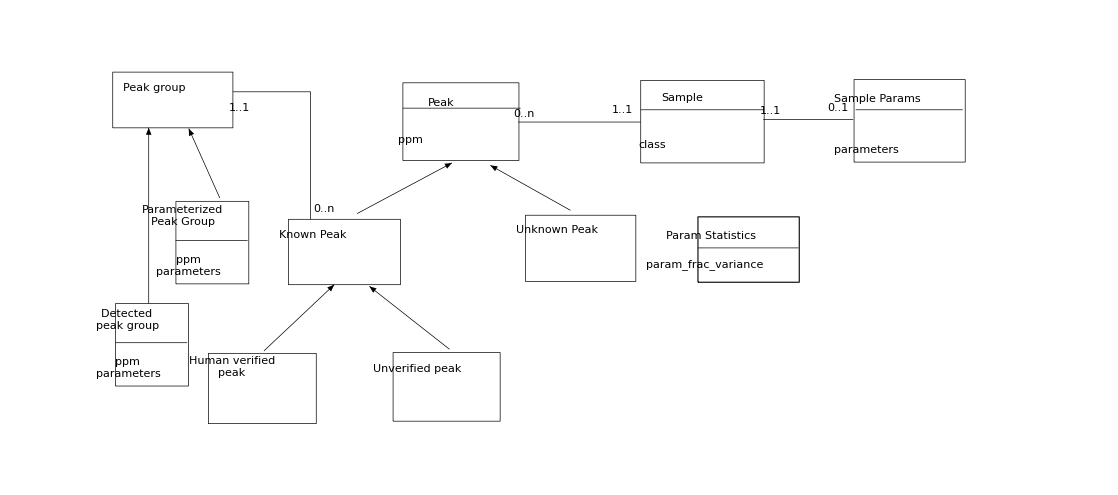

The hough tools use a file format consisting of lines of space-separated values.  The first value in each line is a type identifier.  It would be the table name in the database.  There is a table for each of the following classes: parameterized_peak_group, detected_peak_group, sample, sample_parameters, param_statistics, human_verified_peak, unverified_peak, and unknown_peak.

It is assumed that there is a peak group for any peak_group_id referenced in a known_peak object, this avoids materializing the list of peak_group_ids directly

A peak is identified by a two-part primary key: (sample_id, peak_id) - I did this because the natural way to identify peaks is to sort them by ppm within each sample and then sort the samples in some way and give the sample number and peak number.  This also makes merging new samples into the database a little easier - no need to renumber the peaks, just give each sample a unique id.

##### Fields for each table (that is each line-type)

Each table has fixed fields.  Thus each line of the file, depending on its type has well defined fields to model the relations and data shown in the table.

Each description begins with a prototype line of the file and then a description of each field.

parameterized_peak_group

parametersized_peak_group peak_group_id ppm param_1 param_2 ... param_n

peak_group_id non-negative integer uniquely identifying the peak_group to which the parameters apply

ppm the base location of the peak group

param_1 ... param_n a vector of n reaction parameters so that the predicted location of a peak in this group is ppm + peak_group.parameters · sample.sample_parameters

detected_peak_group

detected_peak_group peak_group_id ppm param_1 param_2 ... param_n

peak_group_id non-negative integer uniquely identifying the peak_group to which the parameters apply

ppm the base location of the peak group

param_1 ... param_n a vector of n reaction parameters so that the predicted location of a peak in this group is ppm + peak_group.parameters · sample.sample_parameters

human_verified_peak

human_verified_peak sample_id peak_id ppm peak_group_id

sample_id non-negative integer uniquely identifying the sample to which this peak belongs

peak_id non-negative integer uniquely identifying this peak within all peaks belonging to that sample

peak_group_id the id of the peak group to which this peak belongs

unverified_peak

unverified_peak sample_id peak_id ppm peak_group_id

Fields are the same as in human_verified_peak

unknown_peak

unknown_peak sample_id peak_id ppm

The fields are the same as in human_verified_peak

sample

sample sample_id class

sample_id a non-negative integer uniquely identifying the sample described by this line

class a string (without spaces) indicating which treatment class this sample came from.  If two samples have different strings, then they came from different classes, same string, same classes

sample_params

sample_params sample_id param_1 param_2 ... param_n

sample_id a non-negative integer uniquely identifying the samle to which these parameters apply

param_1 ... param_n a vector of n sample parameters so that the predicted location of a peak in this sample is peak_group.ppm + peak_group.parameters · sample.sample_parameters

param_stats

param_stats fracvar_1 fracvar_2 ... fracvar_n

fracvar_1 ... fracvar_n is a vector of n decimal rational numbers that give fraction of variance explained by the corresponding sample parameter in the group of known peaks used to generate the sample parameters

#### hough_sample_params

hough_sample_params options fractionVariance   <   initial_db   >   db_with_sample_params

Reads a peak database from standard input.  Extracts the set of peak_groups that have a representative in every sample.  Creates a set of sample parameters that accounts for at least fractionVariance (0..1) of the variance of the peaks in those peak groups.  Outputs a database with these new sample parameters along with a param_stats object added.

If there are already sample_params objects in the database, then three things differ.  First, the number of parameters is set to be the same as the number of parameters in the existing objects.  Second, only samples not associated with an extant sample_params object are given new sample_params objects.  Third, the param_stats object will be left unchanged.  (Maybe I should update it? - check for later version.)

##### Options

The only option is --remove-sample-params which, when present, removes all sample_params objects from the input database before processing it

#### simple_hough

simple_hough centralLocationResolution baseResolution standardDeviation max_GiB_RAM   <   initial_db   >   db_with_detected_peaks

Reads a peak database from standard input.  This database must have sample_params objects defined for every sample and also a param_stats object.  Uses the Alm et. al. Hough transform algorithm to infer the existence of peak groups.  The output database has a set of detected_peak_group objects.

centralLocationResolution gives the number of steps to use in definining the central location of the peaks.

baseResolution gives the number of steps to use for the first principal component.  If another principal component explains 25% of the variance of the first it will be given 25% of the steps.

standardDeviation gives the standard deviation of the Gaussian used in "fuzzifying" the hough transform

max_GiB_RAM gives the maximum number of GiB of RAM to use.  The program will either use partitioning methods to try and meet this constraint or exit with an error.  The program calculates only an estimate, so this is more of a suggestion than a hard rule.

#### assign_peaks

assign_peaks [keep_original_groups|keep_new_groups] singleMismatchPenalty groupMismatchPenalty  <   initial_db   >   db_with_correspondence

Reads a peak database from standard input.  This database must have detected_peak_group objects.  Does an assignment of unknown peaks to detected groups.  Many of them should become known peaks.  Then the extant known peaks are harmonized with the detected groups and newly known peaks.  Known peaks in the input that correspond to one another will continue to correspond afterwards.  However, if keep_new_groups is set, they may be given different peak parameters.  The output will have no detected_peak_group objects, and may have new parameterized_peak_group objects.  I outline the algorithm in more detail below.

Alm et. al. does not speak about peak assignment - they use the predicted locations as the peak location in each sample.  This does an assignment of peaks to detected peak groups.

First, for each sample, an assignment is made between all peaks and both the detected peak groups so as to minimize a penalty function.  For any groups that do not have a corresponding peak, a singleMismatchPenalty is charged.  Otherwise, the distance between a group's predicted location and the assigned peak location is charged.  Then any unknown peaks are changed into known peaks assigned to the group from the generated assignment.  (Note: I do not match to both groups because one expects that each peak group in a set should have a representative peak, thus it makes sense to charge a penalty.  However there is overlap between the sets - most peak groups in the original should have a corresponding group in the detected.  If I use both sets, I don't know which groups correspond so I don't know when to charge a penalty.)

Then, depending on the first parameter (whether it is keep_original_groups or keep_new_groups), the group that is to be discarded is matched in the as done with the sample peaks to the group that is to be kept.  An discarded group with no match is charged a groupMismatchPenalty.  A discarded group with a match is charged a penalty according to the total error of its peaks in the matched kept group.  Finally, any known peaks in a discarded group with a match are moved to a the kept group and the discarded group is removed.  Those "discarded" groups with no match are kept.  At the end, all remaining detected_peak_group objects are promoted to parameterized peak group objects.

## 28 April 2011 Thursday

### Rewrote the specification from yesterday and put it on the wiki

Note that I am calling it a specification rather than a design since that really describes its function a little better.  There is a good bit of design there too (I specify a serialization format, executable names etc.)

### Began writing test cases for hough prototype

#### Generate test data for simple test case

##### randomPeaksAndPermutationAndParameters definition

```mathematica
randomPeaksAndPermutationAndParameters::usage="randomPeaksAndPermutationAndParameters[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange]

Exactly like randomPeaksAndPermutation except has 4 more rules in the output: \"correctly_ordered_peaks\", \"peak_params\", \"peak_ppms\", and \"sample_params\"

Note that the peak_params and peak_ppms are given for the corresponding indices in the correctly ordered peaks.
";
```

```mathematica
randomPeaksAndPermutationAndParameters[numPeaks_Integer,numSamples_Integer,factorStdDev_List,noiseStdDev_,peakResponseStdDev_List,peakRange_List]/;Length[factorStdDev]==Length[peakResponseStdDev]&&NumberQ[noiseStdDev]&&noiseStdDev>0&&Length[peakRange]==2:=
With[{
s=Table[factorStdDev RandomReal[NormalDistribution[0,1],Length[factorStdDev]],{numSamples}],
a=Table[peakResponseStdDev RandomReal[NormalDistribution[0,1],Length[peakResponseStdDev]],{numPeaks}],
k=RandomReal[peakRange,numPeaks]},
With[{rawPos=Map[Function[sj,MapThread[Function[{ai,ki},ki+Dot[ai, sj]+RandomReal[NormalDistribution[0,noiseStdDev]]],{a,k}]],s]},
With[{sortOrdering=Map[Ordering,rawPos],
sortedPos=Map[Sort,rawPos]},
With[{unsortOrdering=Map[Ordering,sortOrdering]},
{"peaks"->sortedPos,"permutation"->unsortOrdering,"correctly_ordered_peaks"->rawPos,"peak_params"->a,"peak_ppms"->k,"sample_params"->s}
]]]]
```

##### Generating the test data

```mathematica
?randomPeaksAndPermutation
```

"randomPeaksAndPermutation[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange] \n\nReturns a list of rules {\"peaks\"→...,\"permutation\"→...}.\n\n\"peaks\" gives a list of samples, each sample is a list of peaks sorted by their location.\n\n\"permutation\" gives a list of permutations that, when applied to the corresponding sample, will make the i^th position in that sample contain the position of the i^th peak.  Thus, after applying all the permutations, the corresponding positions in the sample will contain corresponding peaks.\n\nnumPeaks and numSamples determine how many peaks and samples will be generated\n\nEach sample has a number of latent factors s_j.  Each peak has the same number of latent response variables a_i.  Each peak also has a base location k_i.  The latent factors are selected from a multidimensional Gaussian with mean 0 and standard deviations given by factorStdDev.  Similarly the responses are selected from a Gaussian with mean 0 and standard deviations in peakResponseStdDev.  The peak means are selected independently from a uniform distribution over peakRange.\n\nThe i^th peak in the j^th sample is given a location:\nδ_ij=k_i+a_i·s_j+ξ_ij\n\nWhere ξ_ij is a normally distributed random variable with mean 0 and standard deviation noiseStdDev."

```mathematica
combinedFirstTestSample =randomPeaksAndPermutationAndParameters[10,100,{1},0.0000001,{1},{0,11}]
```

```mathematica
?applyCandidate
```

Global`applyCandidate

applyCandidate[candidate_List,initialPositions_List]:=MapThread[#2⟦#1⟧&,{candidate,initialPositions}]

```mathematica
correctPeaks="correctly_ordered_peaks"/.combinedFirstTestSample;
```

```mathematica
incorrectPeaks="peaks"/.combinedFirstTestSample;
```

```mathematica
perm="permutation"/.combinedFirstTestSample;
```

Verify that applyCandidate provides the way to interpret "permutation" above

```mathematica
applyCandidate[perm[[1;;2]],incorrectPeaks[[1;;2]]]
```

{{5.9022,10.7741,0.75539,9.00214,9.48405,7.12661,10.2916,0.706239,10.6325,10.393},{7.20063,9.56785,0.296305,11.1315,6.46664,10.8757,9.87441,2.07801,13.0677,12.2951}}

```mathematica
correctPeaks[[1;;2]]
```

{{5.9022,10.7741,0.75539,9.00214,9.48405,7.12661,10.2916,0.706239,10.6325,10.393},{7.20063,9.56785,0.296305,11.1315,6.46664,10.8757,9.87441,2.07801,13.0677,12.2951}}

##### Gave up generating the data in Mathematica - I think Ruby will be conceptually easier

### Hough algorithm robustness evaluation

Some quick ideas on ways to evaluate the robustness of the hough algorithm

#### Data sources

1. Synthetic data from the model -- can see what the effects of different amounts of noise are.  Easy to generate.

2. Hand-labeled real data -- how can I be sure I've labeled it right?  Not so many samples.

3. Tuned synthetic data - using known compounds (from a DB) and their reactions to certain physical parameters, generate random parameters and then put the artificially generated peaks in the right place

4. Arabadopsis dataset in the initial paper?  I need to look at this again and how THEY used it.

5. Make our own labeled data using similar techniques as those used in Arabadopsis (proly very expensive, but I had to mention it)

#### Questions to test

Also, how does lack of data affect the algorithm -- accuracy as number of samples/number of peaks/number of initially known peaks decreases?

How do errors in the known peaks affect the algorithm?

How does the algorithm do using "known" peaks from another algorithm?

How does noise in the various parameters affect the algorithm.

What about systematic errors caused by, for example, incorrect baseline shift or distortions near the water signal.

## 29 April - 1 May 2011 Friday-Sunday

### Wrote test cases for hough transform prototype

## 2 May 2011 Monday

### Wrote test cases and code for hough transform prototype

### Set up documentation for hough transform prototoype

### Idea: eliminate peak position axis by solving for maxima analytically

One axis of the hough transform will need to be the parameters of each peak.  Alm et. al. fill the accumulators with votes that are equal-width gaussians centered on the predicted parameter values to get a given peak.  To save space at the expense of time, we could generate the accumulators only when we need them after all peaks have been examined.

However, this idea goes farther - don't search an array of accumulators for the maxima.  Just solve for them analytically.  Gaussians are (mostly) well-behaved functions and we are just summing them.  However, as you see below, solving the equation analytically isn't that simple.

```mathematica
gaussian[x_,μ_,σ_]:=Exp[-((x-μ)/σ)^2]
```

Looking at the case of only two peaks.  Without loss of generality, we can shift the axis so that the first peak has 0 mean and scale the axis so σ=1.  Let n be the mean of the second peak.

```mathematica
twopeaks=gaussian[x,0,1]+gaussian[x,n,1]
```

ⅇ^(-x^2)+ⅇ^(-(-n+x)^2)

Take first derivative

```mathematica
twopeaksderiv=D[twopeaks,x]
```

-2 ⅇ^(-x^2) x-2 ⅇ^(-(-n+x)^2) (-n+x)

Solve for zeroes - but Mathematica can't do it analytically

```mathematica
Reduce[twopeaksderiv==0,{x},Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-2 ⅇ^(-x^2) x-2 ⅇ^(-(-n+x)^2) (-n+x)==0,{x},Reals]

So, try with some test values to get an idea (after trying a bunch, it seems that the collapse from 3 optima to 1 optimum takes place when movable mean is located in the interval [-√2,√2], in other words, when n^2≤2

```mathematica
Sqrt[2]//N
```

1.41421

```mathematica
With[{nval=-Sqrt[2]-Power[10,-30]},{nval/2//N,Reduce[(twopeaksderiv/.{n->nval})==0,{x},Reals]//N}]
```

{-0.707107,x==-0.707107||x==-0.707107||x==-0.707107}

```mathematica
Reduce[twopeaksderiv==0&&n^2<2,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-2 ⅇ^(-x^2) x-2 ⅇ^(-(-n+x)^2) (-n+x)==0&&n^2<2,Reals]

```mathematica
Simplify[(x-n)^2-(x-m)^2]
```

-(m-n) (m+n-2 x)

```mathematica
Manipulate[Plot[Exp[-x^2]+Exp[-(x-n/10)^2],{x,-10,10},PlotRange->All],{n,-20,20}]
```

```mathematica
Manipulate[Plot[{x,n/(Exp[-2x n]Exp[n^2]+1)},{x,-10,10},PlotRange->{-n,n}],{n,-3,3}]
```

### Looked at numerical stability of polar box-muller

```mathematica
Needs["PlotLegends`"]
```

The plot below shows that the multiplicand in the polar version decreases MUCH faster as you get close to 0, giving potentially much larger values.  The polar form is also always less than the normal form.  The only place there will be a stability problem is near 0 where the slope is large (and thus small input errors give rise to large output errors) near 1, there should not be a problem

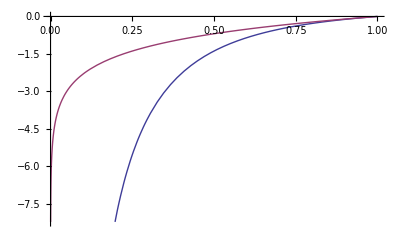

```mathematica
Plot[{Log[s]/s,Log[s]},{s,0,1},PlotLegend->{Log[s]/s,Log[s]},LegendPosition->{0,-0.4}]
```

```mathematica
Reduce[Log[x]<-k&&k>1&&x>0&&x<1,{x},Reals]
```

k>1&&0<x<ⅇ^-k

```mathematica
Reduce[(Log[x]/x)<-k&&k>1&&x>0&&x<1,{x},Reals]
```

k>1&&0<x<ⅇ^(-ProductLog[k])

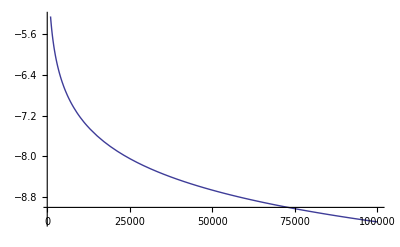

```mathematica
Plot[-ProductLog[k],{k,1000,100000}]
```

```mathematica
Reduce[Log[s]/s<Log[s]&&s>0&&s<1,Reals]
```

0<s<1

## 3 May 2011 Tuesday

### Set up documentation for hough transform prototype

### Derive algorithm for analytical maximum finding when the basis function is a triangle rather than a Gaussian

I'm giving up on the Gaussian for a while and going to focus on a piecewise triangle function.  After experimenting, I can see that, for triangles, finding the local maxima admits an easy, relatively fast algorithm (O(n log n)).  Make a list of change points by, for each center adding 3 pairs (center-width/2, 1), (center, -2} (center+width/2, 1).  Sort these change pairs by first coordinate.  Start a slope accumulator at 1 and a current height at 0. Starting at the second point update the current height by adding the distance from the last point to the current point * the current slope accumulator sum * the slope of a single triangle.  Then add the second coordinate to the slope accumulator.  A maximum is any transition from positive to negative slope.  Plateaus form where slope goes positive->0.  If slope goes 0->negative then that whole plateau was an extended maximum.  (We may wish to use the center of the plateau as a point estimate of the maximum location.)  This method may have accuracy problems for the heights of later maxima because they are the result of many floating point sums.  Round-off can be avoided by just detecting the maxima using the accumulators, then at each maximum, calculate the height by summing all the triangles at that point.  This would be worst case n^2 though keeping a list of the active triangles could reduce it to more like n log n again.

#### Triangle Experiments

Since I'll eventually want a unit area function and since I am going to scale the axis by sigma (allowing unit sigmas) making the math easier, I'll use an isoscelese triangle of height 2 centered on the origin with base 1.

```mathematica
triangle[x_]:=Piecewise[{{2-Abs[4x],Abs[x]<=1/2}},0]
```

```mathematica
D[triangle[x],x]/.{x->-1/4}
```

-4 Abs'[-1/4]

```mathematica
Simplify[triangle[x]&&-1/2<x<0]
```

2+4 x&&x>-1/2&&x<0

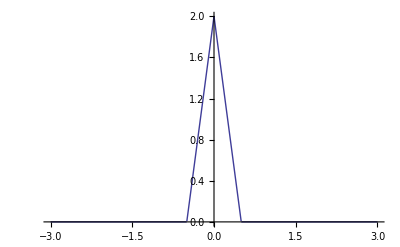

```mathematica
Plot[triangle[x],{x,-3,3}]
```

```mathematica
Integrate[triangle[x],{x,-3,3}]
```

1

```mathematica
Manipulate[Plot[triangle[x]+triangle[x-n],{x,-3/2,3/2}],{n,-1,1}]
```

```mathematica
Maximize[triangle[x]+triangle[x-n],x]
```

Maximize[Piecewise[{{2-4 Abs[x], Abs[x]≤1/2}, {0, True}}]+Piecewise[{{2-4 Abs[-n+x], Abs[-n+x]≤1/2}, {0, True}}],x]

```mathematica
Maximize[triangle[x]+triangle[x-(-1/16)],x]
```

{15/4,{x→-1/16}}

```mathematica
Manipulate[Plot[triangle[x]+triangle[x-n]+triangle[x-m],{x,-3/2,3/2}],{n,-1,1},{m,-1,1}]
```

### Derive algorithm for analyitical maximum finding when the basis function is any truncated polynomial or truncated member of a family of functions closed under addition. This lets me approximate a Gaussian by splines.

I believe I can use a similar algorithm to that for triangles for bounded quadratic humps.  A unit area, unit base, 0-centered hump is 3/2-6 x^2.  The slope of a quad. hump is a line.  The slope of a sum of quad humps will be a sum of lines over their width.  So, starting from the first, keep track of the current acceleration and slope.  If the slope would change from positive to negative before the next peak starts or ends, add that point as a maximum.  Otherwise, check at each peak's start/end and update the acceleration and slope there.  This would be approximately n^2 or n^3.  (I'd have to work things out in detail to know for sure.)  See below, something very close to the original (at n log n) can be used.

Actually, thinking about it, any truncated polynomial can be used.  Why?  Because the sum of polynomials is a polynomial.  Since over the area of support, each is just a polynomial.  Then between changes in which group of polynomials is in its area of support there is a maximum iff the polynomial has a maximum.  At the change points, maxima can be checked for by looking at the changes to the slope.

This same relation holds for any family of functions F such that if f∈F and g∈F then (f+g)∈F.  Further, piecewise combinations of functions from F also work (that is what is happening with the linear version) since shifting to the zero-area and then adding the other function will be the same as having twice as many instances in in the basis but shifted.

This will let me approximate a (truncated) Gaussian by using splines.

The new algorithm is: make a list of change points consisting of the beginning and end of each function from F.  Each change point consists of a coordinate, the function from F, and whether to add or subtract it.  Sort those change points in increasing order by coordinate.  Then, at each change point add or subtract the function from the currently active to make the functions active over the new region.  Finally calculate the two slopes at the change point.  If the change point is a maximum, add it.  Otherwise, if there are any maxima in the new region, add them.  Repeat for all change points.

#### Quadratic hump Experiments

Here, I define a quadratic hump with unit area and unit base

```mathematica
quadhump[x_]:=Piecewise[{{3/2-6x^2,Abs[x]≤1/2}},0]
```

```mathematica
quadhumpderiv[x_]:=Evaluate[D[quadhump[x],x]]
```

Here I plot the quadratic hump and the Gaussian together

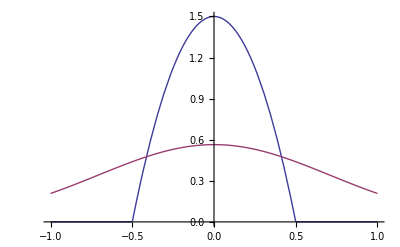

```mathematica
Plot[{quadhump[x],(*quadhumpderiv[x],*)Exp[-x^2]/Sqrt[Pi]},{x,-1,1},PlotRange->All]
```

```mathematica
Integrate[quadhump[x],{x,-3,3}]
```

1

```mathematica
Integrate[Exp[-x^2]/Sqrt[Pi],{x,-Infinity,Infinity}]
```

1

### Extend analytical method to multi-dimensional spaces

The algorithm can be extended to multidimensional spaces by partitioning them into regions where the same number of functions from F are in their region of support.  Then, you look for maxima in these regions.  You also look for maxima along the boundaries between the regions using a recursive version of the algorithm.  The boundary will be 1 dimension less.

I think in this case, F when projected onto a lower dimensional space must yield a set of functions that (1) are closed under addition and (2) have projections onto d-1 dimensions that also fulfill this property.  All 0-dimensional functions are closed under addition since the real numbers are closed under addition.

So, in this algorithm, you make a list of potential maximum regions.  It consists of all d dimensional regions and d-1 dimensional regions that are the borders of those d-dimensional regions.  Then you calculate the maxima over the d-dimensaional regions and check to see if there are maxima across each of the borders.  Then you repeat, extracting the borders of the d-1 dimensional regions.

### Idea, reduce hough part of problem to linear programming

If we use triangular basis functions, it seems to me that the maxima might be findable by linear programming.  If this is true, then given that in all the other directions, things are oriented along hyper-planes, we may be able to use linear programming to solve for maximum vote locations for all variables exactly.

## 4-15 May 2011

### Write and test hough prototype

## 16 May 2011

### Write and test hough prototype

### Multidimensional analytical method from 3 May is exponential in #Dimensions

Assuming that the basic votes are hyperplanes then in n dimensions there are at least 2^(n+1)-1 items that have to be explored when there are n+1 hyperplanes.  This is because a simplex in n has 2^(n+1)-1 elements, each of which will need to be examined because it is the boundary between subspaces and thus a potential region where maxima or minima could reside.

The mathematical complexity of intersecting the various functions with arbitrary hyper-volumes is also not to be sneezed at for difficulty in implementation.

### Analytical maximum search using PRIM-like algorithm

PRIM (patient rule induction method) is a machine learning method that searches for rectangles of parameter space that have uniform class (classification) or maximum response (regression).  I adapt it here to search for dense regions in the Hough space.  The original is detailed in Hastie, Tibshirani, and Friedman 2^nd edition p. 281.

Zeroing can be accomplished in the analytical domain by taking the integral over the entire box and then subtracting the integrals over the sub-boxes intersecting the various zeroed boxes.

The algorithm is: (I'll write this up on a later day)

### Calculations for hand-example for analyitic multi-dimensional Hough

#### A bit more quadratic hump calculations

General formula for a quadratic hump (that is zero everywhere the quadratic would be negative)

```mathematica
quadhump[x_,h_,s_]:=Piecewise[{{h-s x^2,Abs[x]≤Sqrt[h/s]}},0]
```

Calculate what will make the area 1

```mathematica
Reduce[Integrate[quadhump[x,h,s],{x,-Infinity,Infinity}]==1]
```

h>0&&s==(16 h^3)/9

```mathematica
Solve[width==2 h/(16 h^3/9),h]
```

{{h→-3/(2 √2 √width)},{h→3/(2 √2 √width)}}

```mathematica
unitquadhump[x_,h_]:=quadhump[x,h,(16 h^3)/9]
```

```mathematica
Integrate[unitquadhump[x,h],{x,-Infinity,Infinity}]
```

Piecewise[{{-1, h<0}, {1, h>0}, {0, True}}]

Wow, Mathematica correctly handled the discontinuity at h=0.

```mathematica
unitquadhump[x,12]
```

Piecewise[{{12-3072 x^2, Abs[x]≤1/16}, {0, True}}]

#### What the hand-example should look like in parameter space

```mathematica
votes[m_,b_]:=unitquadhump[m+b,12]+unitquadhump[b,12]
```

```mathematica
votes[0.5,0.5]
```

0

```mathematica
Plot3D[votes[m,b],{b,-1/16,1/2},{m,-2/4,2/16},AxesLabel->{"b","m","votes"}]
```

-Graphics3D-

#### Other calculations

```mathematica
Expand[(1/16-b)^3]
```

1/4096-(3 b)/256+(3 b^2)/16-b^3

```mathematica
Simplify[(1/16-b)^3-(-1/16-b)^3]
```

1/2048+(3 b^2)/8

```mathematica
Integrate[12-3072(m+b)^2,{m,-1/16-b,1/16-b}]
```

1

```mathematica
Integrate[12-3072(m+b)^2,{m,-1,1/16-b}]
```

-2023/2+3060 b-3072 b^2+1024 b^3

#### Getting Mathematica to do the work for me (but using α=1/4 rather than 1/2 as I stated in the hand-written draft)

##### First Iteration

Votes in whole potential region

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0,1}]
```

509/256

Votes in original region with smaller maximum m

```mathematica
Integrate[votes[m,b],{m,-1,mx},{b,0,1},Assumptions->-1<mx<1]
```

Piecewise[{{3/256 (127+128 mx), -15/16<mx≤-1/16}, {1/256 (381+128 mx), 1/16<mx<1}, {-249-1011 mx-1530 mx^2-1024 mx^3-256 mx^4, -1<mx≤-15/16}, {1/128 (189+128 mx-768 mx^2+32768 mx^4), True}}]

```mathematica
Reduce[%37==3/4(509/256)]//N
```

mx==0.0162067

Vote density in region with smaller maximum m

```mathematica
Integrate[votes[m,b],{m,-1,0.016206723615191782},{b,0,1}]/((0.016206723615191782-(-1))(1-0))
```

1.46743

Votes in original region with larger minimum m

```mathematica
Integrate[votes[m,b],{m,mn,1},{b,0,1},Assumptions->-1<mn<1]
```

Piecewise[{{1/2 (1-3 mn), -15/16<mn<-1/16}, {(1-mn)/2, mn>1/16||mn≤-1}, {1/256 (131-256 mn+1536 mn^2+16384 mn^3), mn==0}, {1/256 (131-256 mn+1536 mn^2-65536 mn^4), -1/16<mn<0||0<mn<1/16}, {1/32 (17-16 mn+192 mn^2-2048 mn^3-16384 mn^4), mn==-1/16}, {1/256 (123-16384 mn^3+65536 mn^4), mn==1/16}, {1/256 (64253+258816 mn+391680 mn^2+262144 mn^3+65536 mn^4), True}}]

```mathematica
Reduce[%34==3/4(509/256)]
```

mn==-1015/512||mn==-1015/1536

Vote density in region with larger minimum

```mathematica
Integrate[votes[m,b],{m,-1015/1536,1},{b,0,1}]/((1-(-1015/1536))(1-0))
```

4581/5102

```mathematica
%51//N
```

0.897883

Votes in original region with smaller maximum b

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0,bx},Assumptions->0≤bx<1]
```

Piecewise[{{19/16, bx==3/16}, {1+bx, 1/16<bx<3/16||3/16<bx≤15/16}, {25 bx-2048 bx^3, 0<bx≤1/16}, {1/256 (64381-258944 bx+391680 bx^2-262144 bx^3+65536 bx^4), 15/16<bx<1}, {0, True}}]

```mathematica
Reduce[%39==3/4(509/256)]
```

bx==503/1024

Find vote density in the region with the smaller maximum b

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0,503/1024},Assumptions->0≤503/1024<1]/((1-(-1))(503/1024-0))
```

1527/1006

```mathematica
%55//N
```

1.51789

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,bn,1},Assumptions->0≤bn<1]
```

Piecewise[{{237/256, bn==1/16}, {1/256 (253-256 bn), 1/16<bn<15/16}, {1/256 (509-6400 bn+524288 bn^3), 0≤bn<1/16}, {1/2 (-499+2023 bn-3060 bn^2+2048 bn^3-512 bn^4), True}}]

```mathematica
Reduce[%57==3/4(509/256)]//N
```

bn==0.0205988

Find vote density in the region with the larger minimum b

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0.020598818895557126,1}]/((1-(-1))(1-0.020598818895557126))
```

0.761287

So, the greatest vote-density comes from lowering the maximum b to 503/1024

##### Second Iteration

Votes in new region from previous iteration

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0,503/1024}]
```

1527/1024

```mathematica
1527/1024//N
```

1.49121

Votes in new region with smaller maximum m

```mathematica
Integrate[votes[m,b],{m,-1,mx},{b,0,503/1024},Assumptions->-1<mx<1]
```

Piecewise[{{(1+mx)/2, -1<mx≤-567/1024}, {(1015+512 mx)/1024, 1/16<mx<1}, {(1015+1536 mx)/1024, -439/1024<mx≤-1/16}, {(-54542922145-491659620352 mx-1566025187328 mx^2-2160368549888 mx^3-1099511627776 mx^4)/4294967296, -567/1024<mx≤-439/1024}, {(1003+1024 mx-6144 mx^2+262144 mx^4)/1024, True}}]

```mathematica
Reduce[%65==3/4(1527/1024)]
```

mx==521/2048

Vote density in region with smaller maximum m

```mathematica
Integrate[votes[m,b],{m,-1,521/2048},{b,0,503/1024}]/((521/2048-(-1))(503/1024-0))
```

2345472/1292207

```mathematica
%70//N
```

1.81509

Votes in original region with larger minimum m

```mathematica
Integrate[votes[m,b],{m,mn,1},{b,0,503/1024},Assumptions->-1<mn<1]
```

Piecewise[{{(1015-512 mn)/1024, -1<mn≤-567/1024}, {1/2 (1-3 mn), -439/1024<mn<-1/16}, {(1-mn)/2, mn>1/16||mn≤-1}, {1/256 (131-256 mn+1536 mn^2+16384 mn^3), mn==0}, {1/256 (131-256 mn+1536 mn^2-65536 mn^4), -1/16<mn<0||0<mn<1/16}, {1/32 (17-16 mn+192 mn^2-2048 mn^3-16384 mn^4), mn==-1/16}, {1/256 (123-16384 mn^3+65536 mn^4), mn==1/16}, {(60947624353+491659620352 mn+1566025187328 mn^2+2160368549888 mn^3+1099511627776 mn^4)/4294967296, True}}]

```mathematica
Reduce[%72==3/4(1527/1024)&&-1<mn<1]
```

mn==-2533/6144

Vote density in region with larger minimum

```mathematica
Integrate[votes[m,b],{m,-2533/6144,1},{b,0,503/1024}]/((1-(-2533/6144))(503/1024-0))
```

7036416/4364531

```mathematica
%76//N
```

1.61218

Votes in original region with smaller maximum b

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0,bx},Assumptions->0≤bx<503/1024]
```

Piecewise[{{19/16, bx==3/16}, {1+bx, 1/16<bx<3/16||3/16<bx<503/1024}, {25 bx-2048 bx^3, 0<bx≤1/16}, {0, True}}]

```mathematica
Reduce[%39==3/4(1527/1024)]
```

bx==485/4096

Find vote density in the region with the smaller maximum b

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0,485/4096}]/((1-(-1))(485/4096-0))
```

4581/970

```mathematica
%80//N
```

4.72268

Now look at a region with a larger minimum

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,bn,503/1024},Assumptions->0≤bn<503/1024]
```

Piecewise[{{439/1024, bn==1/16}, {(503-1024 bn)/1024, bn>1/16||bn<0}, {(1527-25600 bn+2097152 bn^3)/1024, True}}]

```mathematica
Reduce[%83==3/4(1527/1024)&&0<bn<503/1024]//N
```

bn==0.0151998

Find vote density in the region with the larger minimum b

```mathematica
Integrate[votes[m,b],{m,-1,1},{b,0.015199784447371146,503/1024}]/((1-(-1))(503/1024-0.015199784447371146))
```

1.17477

So, the greatest vote-density comes from lowering the maximum b to 4581/970

### Try and solve for solution to integral of one point's votes over rectangle

I tried integrating the votes for two fixed points on a general grid, but it took a long time — my computer locked up while it was working.  I'll try below for the less ambitious case of one point, but with general coordinates.

The general coordinates did not work (or more precisely took a long time, so I aborted them).  The equation for just a box with the kernel over the equation 1=m+b yields a giant piecewise function for integrals over a general box.  It is not too big to type in, but it is quite large.  There will be even more special cases for a general line.

Solving the sum of such integrals for a specific volume (needed to decide how much to cut from the side of the box each time) will be very ugly.

Looking at the figure, we can probably decompose the complex formulae into integrating the non-zero part of the volume over one or two triangular regions+1(the area under a cross section) × the length of the intersection that takes a whole cross-section

```mathematica
pointVotes[m_,b_,x_,y_]:=unitquadhump[y-m x-b,12]
```

```mathematica
pointVotes[m,b,x,y]
```

Piecewise[{{12-3072 (-b-m x+y)^2, Abs[-b-m x+y]≤1/16}, {0, True}}]

```mathematica
Plot3D[pointVotes[m,b,1,1],{b,-1,1},{m,-1,1},AxesLabel->{"b","m","votes"},PlotPoints->40,PerformanceGoal->"Quality"]
```

-Graphics3D-

#### The large solution

```mathematica
Integrate[pointVotes[m,b,1,1],{m,mn,mx},{b,bn,bx},Assumptions->-1<=mn<mx<=1&&-1≤bn≤bx≤1]
```

Piecewise[{{1/16, (1+8 bn-8 bx==0&&-17+16 bx+16 mn==0&&-17+16 bn+16 mx>0)||(1+8 bn-8 bx<0&&-17+16 bn+16 mx>0&&-15+16 bn+16 mn==0)}, {1/8, 1+8 bn-8 bx==0&&-15+16 bx+16 mn≤0&&-17+16 bn+16 mx>0}, {-bn+bx, (-15+16 bx+16 mn≤0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx>0)||(-15+16 bx+16 mn<0&&1+8 bn-8 bx>0&&-17+16 bn+16 mx>0&&bn-bx<0)}, {1/16 (15-16 bn-16 mn), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bx+16 mn==0&&-17+16 bn+16 mx>0}, {1-bn-mn, (-17+16 bx+16 mn==0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx>0)||(-17+16 bx+16 mn≥0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx>0&&-15+16 bn+16 mn<0)}, {-1/256 (-17+16 bn+16 mn)^3 (-13+16 bn+16 mn), (-17+16 bx+16 mn==0&&bn-bx<0&&1+8 bn-8 bx>0&&-17+16 bn+16 mx>0)||(-17+16 bx+16 mn≥0&&bn-bx<0&&1+8 bn-8 bx>0&&-17+16 bn+16 mx>0&&-17+16 bn+16 mn<0)||(1+8 bn-8 bx<0&&-17+16 bn+16 mx>0&&-15+16 bn+16 mn>0&&-17+16 bn+16 mn<0)}, {-1/256 (-19+16 bx+16 mn)^3 (-15+16 bx+16 mn), 1+8 bn-8 bx==0&&-17+16 bx+16 mn>0&&-17+16 bn+16 mn<0&&-17+16 bn+16 mx>0}, {1/2 (2023 bn-3060 bn^2+2048 bn^3-512 bn^4-2023 bx+3060 bx^2-2048 bx^3+512 bx^4-6120 bn mn+6144 bn^2 mn-2048 bn^3 mn+6120 bx mn-6144 bx^2 mn+2048 bx^3 mn+6144 bn mn^2-3072 bn^2 mn^2-6144 bx mn^2+3072 bx^2 mn^2-2048 bn mn^3+2048 bx mn^3), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bn+16 mn>0&&-17+16 bx+16 mn<0&&-17+16 bn+16 mx>0}, {1/256 (64157-259200 bx+391680 bx^2-262144 bx^3+65536 bx^4-259200 mn+783360 bx mn-786432 bx^2 mn+262144 bx^3 mn+391680 mn^2-786432 bx mn^2+393216 bx^2 mn^2-262144 mn^3+262144 bx mn^3+65536 mn^4), 1+8 bn-8 bx==0&&-15+16 bx+16 mn>0&&-17+16 bx+16 mn<0&&-17+16 bn+16 mx>0}, {1/256 (64125-256 bn-258944 bx+391680 bx^2-262144 bx^3+65536 bx^4-259200 mn+783360 bx mn-786432 bx^2 mn+262144 bx^3 mn+391680 mn^2-786432 bx mn^2+393216 bx^2 mn^2-262144 mn^3+262144 bx mn^3+65536 mn^4), (bn-bx<0&&-15+16 bx+16 mn>0&&1+8 bn-8 bx>0&&-15+16 bn+16 mn<0&&-17+16 bn+16 mx>0)||(-15+16 bx+16 mn>0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx>0&&-17+16 bx+16 mn<0)}, {1/256 (63885-258944 bx+391680 bx^2-262144 bx^3+65536 bx^4-258944 mn+783360 bx mn-786432 bx^2 mn+262144 bx^3 mn+391680 mn^2-786432 bx mn^2+393216 bx^2 mn^2-262144 mn^3+262144 bx mn^3+65536 mn^4), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bn+16 mn==0&&-17+16 bn+16 mx>0}, {-64 (1+4 mn-4 mx) (mn-mx)^3, (1+8 bn-8 bx≤0&&-15+16 bx+16 mn==0&&-15+16 bx+16 mx>0&&-17+16 bx+16 mx≤0)||(1+8 bn-8 bx>0&&-15+16 bx+16 mn==0&&-15+16 bx+16 mx>0&&bn-bx<0&&-15+16 bn+16 mx≤0)}, {-1+bx+mx, -15+16 bx+16 mn≤0&&-17+16 bx+16 mx>0&&1+8 bn-8 bx<0&&-15+16 bn+16 mx≤0}, {-mn+mx, (-17+16 bx+16 mn==0&&-17+16 bx+16 mx>0&&1+8 bn-8 bx<0&&-15+16 bn+16 mx≤0)||(-17+16 bx+16 mn>0&&1+8 bn-8 bx<0&&-15+16 bn+16 mx≤0&&-15+16 bn+16 mn<0&&mn-mx<0)}, {-1/256 (-19+16 bx+16 mx) (-15+16 bx+16 mx)^3, (1+8 bn-8 bx≤0&&-15+16 bx+16 mx>0&&-15+16 bx+16 mn<0&&-17+16 bx+16 mx≤0)||(1+8 bn-8 bx>0&&-15+16 bx+16 mx>0&&-15+16 bx+16 mn<0&&bn-bx<0&&-15+16 bn+16 mx≤0)}, {1/256 (63869-258944 bx+391680 bx^2-262144 bx^3+65536 bx^4-259200 mn+783360 bx mn-786432 bx^2 mn+262144 bx^3 mn+391680 mn^2-786432 bx mn^2+393216 bx^2 mn^2-262144 mn^3+262144 bx mn^3+65536 mn^4+256 mx), 1+8 bn-8 bx<0&&-15+16 bx+16 mn>0&&-17+16 bx+16 mn<0&&-17+16 bx+16 mx>0&&-15+16 bn+16 mx≤0}, {1/2 (-15+16 bx+16 mn) (mn-mx) (135-264 bx+128 bx^2-60 mn+64 bx mn+64 mn^2-204 mx+192 bx mx-64 mn mx+128 mx^2), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bn+16 mn==0&&-15+16 bn+16 mx>0&&-17+16 bx+16 mx≤0}, {-4 (bn-bx) (mn-mx) (765-768 bn+256 bn^2-768 bx+256 bn bx+256 bx^2-768 mn+384 bn mn+384 bx mn+256 mn^2-768 mx+384 bn mx+384 bx mx+256 mn mx+256 mx^2), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bn+16 mn>0&&-17+16 bx+16 mn<0&&mn-mx<0&&-17+16 bx+16 mx≤0}, {(mn-mx) (-1+64 mn^2+256 mn^3-128 mn mx-768 mn^2 mx+64 mx^2+768 mn mx^2-256 mx^3), (1+8 bn-8 bx==0&&-17+16 bx+16 mn==0&&-17+16 bx+16 mx>0&&-17+16 bn+16 mx≤0)||(1+8 bn-8 bx<0&&-17+16 bn+16 mx≤0&&-15+16 bn+16 mn==0&&-15+16 bn+16 mx>0)}, {-2 (mn-mx) (-722+1938 bx-1728 bx^2+512 bx^3+969 mn-1728 bx mn+768 bx^2 mn-576 mn^2+512 bx mn^2+128 mn^3+969 mx-1728 bx mx+768 bx^2 mx-576 mn mx+512 bx mn mx+128 mn^2 mx-576 mx^2+512 bx mx^2+128 mn mx^2+128 mx^3), 1+8 bn-8 bx==0&&-17+16 bx+16 mn>0&&-17+16 bn+16 mn<0&&mn-mx<0&&-17+16 bn+16 mx≤0}, {-1/2 (mn-mx) (-2023+6120 bn-6144 bn^2+2048 bn^3+3060 mn-6144 bn mn+3072 bn^2 mn-2048 mn^2+2048 bn mn^2+512 mn^3+3060 mx-6144 bn mx+3072 bn^2 mx-2048 mn mx+2048 bn mn mx+512 mn^2 mx-2048 mx^2+2048 bn mx^2+512 mn mx^2+512 mx^3), (-17+16 bx+16 mn==0&&bn-bx<0&&-17+16 bx+16 mx>0&&1+8 bn-8 bx>0&&-17+16 bn+16 mx≤0)||(-17+16 bx+16 mn>0&&bn-bx<0&&1+8 bn-8 bx>0&&-17+16 bn+16 mx≤0&&-17+16 bn+16 mn<0&&mn-mx<0)||(1+8 bn-8 bx<0&&-17+16 bn+16 mx≤0&&-15+16 bn+16 mn>0&&-17+16 bn+16 mn<0&&mn-mx<0)}, {1/2 (mn-mx) (-2025+6120 bx-6144 bx^2+2048 bx^3+3060 mn-6144 bx mn+3072 bx^2 mn-2048 mn^2+2048 bx mn^2+512 mn^3+3060 mx-6144 bx mx+3072 bx^2 mx-2048 mn mx+2048 bx mn mx+512 mn^2 mx-2048 mx^2+2048 bx mx^2+512 mn mx^2+512 mx^3), (1+8 bn-8 bx≤0&&-15+16 bx+16 mn>0&&-17+16 bx+16 mn<0&&mn-mx<0&&-17+16 bx+16 mx≤0)||(1+8 bn-8 bx>0&&-15+16 bx+16 mn>0&&mn-mx<0&&bn-bx<0&&-15+16 bn+16 mn<0&&-15+16 bn+16 mx≤0)}, {1/256 (64125-259200 bn+391680 bn^2-262144 bn^3+65536 bn^4-259200 mn+783360 bx mn-786432 bx^2 mn+262144 bx^3 mn+391680 mn^2-786432 bx mn^2+393216 bx^2 mn^2-262144 mn^3+262144 bx mn^3+65536 mn^4+783360 bn mx-786432 bn^2 mx+262144 bn^3 mx-783360 bx mx+786432 bx^2 mx-262144 bx^3 mx-786432 bn mx^2+393216 bn^2 mx^2+786432 bx mx^2-393216 bx^2 mx^2+262144 bn mx^3-262144 bx mx^3), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bx+16 mn>0&&-15+16 bn+16 mn<0&&-15+16 bn+16 mx>0&&-17+16 bx+16 mx≤0}, {1/2 (-2025 bn+3060 bn^2-2048 bn^3+512 bn^4+2025 bx-3060 bx^2+2048 bx^3-512 bx^4+6120 bn mx-6144 bn^2 mx+2048 bn^3 mx-6120 bx mx+6144 bx^2 mx-2048 bx^3 mx-6144 bn mx^2+3072 bn^2 mx^2+6144 bx mx^2-3072 bx^2 mx^2+2048 bn mx^3-2048 bx mx^3), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bx+16 mn<0&&-15+16 bn+16 mx>0&&-17+16 bx+16 mx≤0}, {1/256 (64125-259200 bn+391680 bn^2-262144 bn^3+65536 bn^4-16384 mn^3-65536 mn^4-259200 mx+783360 bn mx-786432 bn^2 mx+262144 bn^3 mx+49152 mn^2 mx+262144 mn^3 mx+391680 mx^2-786432 bn mx^2+393216 bn^2 mx^2-49152 mn mx^2-393216 mn^2 mx^2-245760 mx^3+262144 bn mx^3+262144 mn mx^3), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bx+16 mn==0&&-15+16 bn+16 mx>0&&-17+16 bx+16 mx≤0}, {1/8 (1+32 mn+384 mn^2+1536 mn^3+2048 mn^4-32 mx-768 mn mx-4608 mn^2 mx-8192 mn^3 mx+384 mx^2+4608 mn mx^2+12288 mn^2 mx^2-1536 mx^3-8192 mn mx^3+2048 mx^4), 1+8 bn-8 bx==0&&-15+16 bx+16 mn==0&&-17+16 bx+16 mx>0&&-17+16 bn+16 mx≤0}, {1/128 (63997-129600 bn+195840 bn^2-131072 bn^3+32768 bn^4-129472 bx+195840 bx^2-131072 bx^3+32768 bx^4-129600 mn+391680 bx mn-393216 bx^2 mn+131072 bx^3 mn+195840 mn^2-393216 bx mn^2+196608 bx^2 mn^2-131072 mn^3+131072 bx mn^3+32768 mn^4-129472 mx+391680 bn mx-393216 bn^2 mx+131072 bn^3 mx+195840 mx^2-393216 bn mx^2+196608 bn^2 mx^2-131072 mx^3+131072 bn mx^3+32768 mx^4), (-15+16 bn+16 mx>0&&-15+16 bx+16 mn>0&&-17+16 bx+16 mn<0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx≤0)||(-15+16 bx+16 mn>0&&1+8 bn-8 bx>0&&-17+16 bn+16 mx≤0&&bn-bx<0&&-17+16 bx+16 mx>0&&-15+16 bn+16 mn<0)}, {1/128 (83521-314432 bx+443904 bx^2-278528 bx^3+65536 bx^4-129600 mn+391680 bx mn-393216 bx^2 mn+131072 bx^3 mn+195840 mn^2-393216 bx mn^2+196608 bx^2 mn^2-131072 mn^3+131072 bx mn^3+32768 mn^4-184832 mx+496128 bx mx-442368 bx^2 mx+131072 bx^3 mx+248064 mx^2-442368 bx mx^2+196608 bx^2 mx^2-147456 mx^3+131072 bx mx^3+32768 mx^4), 1+8 bn-8 bx==0&&-15+16 bx+16 mn>0&&-17+16 bx+16 mn<0&&-17+16 bx+16 mx>0&&-17+16 bn+16 mx≤0}, {1/256 (63869-259200 bn+391680 bn^2-262144 bn^3+65536 bn^4+256 bx-258944 mx+783360 bn mx-786432 bn^2 mx+262144 bn^3 mx+391680 mx^2-786432 bn mx^2+393216 bn^2 mx^2-262144 mx^3+262144 bn mx^3+65536 mx^4), (-15+16 bx+16 mn≤0&&-15+16 bn+16 mx>0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx≤0)||(-15+16 bx+16 mn<0&&1+8 bn-8 bx>0&&-17+16 bn+16 mx≤0&&bn-bx<0&&-17+16 bx+16 mx>0)}, {1/256 (64109-259200 bn+391680 bn^2-262144 bn^3+65536 bn^4-256 mn-258944 mx+783360 bn mx-786432 bn^2 mx+262144 bn^3 mx+391680 mx^2-786432 bn mx^2+393216 bn^2 mx^2-262144 mx^3+262144 bn mx^3+65536 mx^4), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bx+16 mn==0&&-17+16 bx+16 mx>0&&-17+16 bn+16 mx≤0}, {1/256 (64125-259200 bn+391680 bn^2-262144 bn^3+65536 bn^4-256 mn-258944 mx+783360 bn mx-786432 bn^2 mx+262144 bn^3 mx+391680 mx^2-786432 bn mx^2+393216 bn^2 mx^2-262144 mx^3+262144 bn mx^3+65536 mx^4), (-17+16 bx+16 mn==0&&-15+16 bn+16 mx>0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx≤0)||(-17+16 bx+16 mn≥0&&-15+16 bn+16 mx>0&&1+8 bn-8 bx<0&&-17+16 bn+16 mx≤0&&-15+16 bn+16 mn<0)}, {1/256 (63869-258944 bx+391680 bx^2-262144 bx^3+65536 bx^4-783360 bn mn+786432 bn^2 mn-262144 bn^3 mn+783360 bx mn-786432 bx^2 mn+262144 bx^3 mn+786432 bn mn^2-393216 bn^2 mn^2-786432 bx mn^2+393216 bx^2 mn^2-262144 bn mn^3+262144 bx mn^3-258944 mx+783360 bn mx-786432 bn^2 mx+262144 bn^3 mx+391680 mx^2-786432 bn mx^2+393216 bn^2 mx^2-262144 mx^3+262144 bn mx^3+65536 mx^4), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bn+16 mn>0&&-17+16 bx+16 mn<0&&-17+16 bx+16 mx>0&&-17+16 bn+16 mx≤0}, {1/256 (102917-369664 bx+496128 bx^2-294912 bx^3+65536 bx^4-369664 mx+992256 bx mx-884736 bx^2 mx+262144 bx^3 mx+496128 mx^2-884736 bx mx^2+393216 bx^2 mx^2-294912 mx^3+262144 bx mx^3+65536 mx^4), 1+8 bn-8 bx==0&&-15+16 bx+16 mn<0&&-17+16 bx+16 mx>0&&-17+16 bn+16 mx≤0}, {1/256 (63869-258944 bx+391680 bx^2-262144 bx^3+65536 bx^4-259200 mn+783360 bx mn-786432 bx^2 mn+262144 bx^3 mn+391680 mn^2-786432 bx mn^2+393216 bx^2 mn^2-245760 mn^3+262144 bx mn^3+131072 mn^4+256 mx-49152 mn^2 mx-262144 mn^3 mx+49152 mn mx^2+393216 mn^2 mx^2-16384 mx^3-262144 mn mx^3+65536 mx^4), bn-bx<0&&1+8 bn-8 bx>0&&-15+16 bn+16 mn==0&&-17+16 bx+16 mx>0&&-17+16 bn+16 mx≤0}, {0, True}}]

```mathematica
Simplify[%15]
```

Piecewise[{{1/16, bn+mx>17/16&&((1/8+bn==bx&&bx+mn==17/16)||(bn+mn==15/16&&1/8+bn<bx))}, {1/8, 1/8+bn==bx&&bx+mn≤15/16&&bn+mx>17/16}, {-bn+bx, bn+mx>17/16&&((bn<bx&&bx<1/8+bn&&bx+mn<15/16)||(1/8+bn<bx&&bx+mn≤15/16))}, {15/16-bn-mn, bx<1/8+bn&&bn<bx&&bx+mn==15/16&&bn+mx>17/16}, {1-bn-mn, bn+mx>17/16&&1/8+bn<bx&&(bx+mn==17/16||(bx+mn≥17/16&&bn+mn<15/16))}, {-1/256 (-17+16 bn+16 mn)^3 (-13+16 bn+16 mn), bn+mx>17/16&&((1/8+bn>bx&&bn<bx&&(bx+mn==17/16||(bx+mn≥17/16&&bn+mn<17/16)))||(1/8+bn<bx&&15/16<bn+mn<17/16))}, {-1/256 (-19+16 bx+16 mn)^3 (-15+16 bx+16 mn), 1/8+bn==bx&&bx+mn>17/16&&bn+mn<17/16&&bn+mx>17/16}, {-1/2 (bn-bx) (512 bn^3+512 bx^3+2048 bx^2 (-1+mn)+512 bn^2 (-4+bx+4 mn)+(17-16 mn)^2 (-7+8 mn)+12 bx (255-512 mn+256 mn^2)+4 bn (765+128 bx^2+512 bx (-1+mn)-1536 mn+768 mn^2)), bx<1/8+bn&&bn<bx&&bn+mn>15/16&&bx+mn<17/16&&bn+mx>17/16}, {64157/256+256 bx^4+1024 bx^3 (-1+mn)-(2025 mn)/2+1530 mn^2-1024 mn^3+256 mn^4+1/2 bx (15-16 mn)^2 (-9+8 mn)+6 bx^2 (255-512 mn+256 mn^2), 1/8+bn==bx&&15/16<bx+mn<17/16&&bn+mx>17/16}, {-bn+256 bx^4+1024 bx^3 (-1+mn)+1/2 bx (17-16 mn)^2 (-7+8 mn)+1/256 (-19+16 mn) (-15+16 mn)^3+6 bx^2 (255-512 mn+256 mn^2), bn+mx>17/16&&((15/16<bx+mn<17/16&&1/8+bn<bx)||(bx+mn>15/16&&bn<bx&&bx<1/8+bn&&bn+mn<15/16))}, {63885/256+256 bx^4+1024 bx^3 (-1+mn)-(2023 mn)/2+1530 mn^2-1024 mn^3+256 mn^4+1/2 bx (17-16 mn)^2 (-7+8 mn)+6 bx^2 (255-512 mn+256 mn^2), bx<1/8+bn&&bn<bx&&bn+mn==15/16&&bn+mx>17/16}, {-64 (1+4 mn-4 mx) (mn-mx)^3, bx+mn==15/16&&((15/16<bx+mx≤17/16&&1/8+bn≤bx)||(bx+mx>15/16&&bn<bx&&bx<1/8+bn&&bn+mx≤15/16))}, {-1+bx+mx, bx+mn≤15/16&&bx+mx>17/16&&1/8+bn<bx&&bn+mx≤15/16}, {-mn+mx, 1/8+bn<bx&&bn+mx≤15/16&&((bx+mn==17/16&&bx+mx>17/16)||(bx+mn>17/16&&mn<mx&&bn+mn<15/16))}, {-1/256 (-19+16 bx+16 mx) (-15+16 bx+16 mx)^3, bx+mn<15/16&&((15/16<bx+mx≤17/16&&1/8+bn≤bx)||(bx+mx>15/16&&bn<bx&&bx<1/8+bn&&bn+mx≤15/16))}, {63869/256+256 bx^4+1024 bx^3 (-1+mn)-(2025 mn)/2+1530 mn^2-1024 mn^3+256 mn^4+1/2 bx (17-16 mn)^2 (-7+8 mn)+6 bx^2 (255-512 mn+256 mn^2)+mx, 1/8+bn<bx&&15/16<bx+mn<17/16&&bx+mx>17/16&&bn+mx≤15/16}, {1/2 (-15+16 bx+16 mn) (mn-mx) (135+128 bx^2+64 mn^2-204 mx+128 mx^2-4 mn (15+16 mx)+8 bx (-33+8 mn+24 mx)), bx<1/8+bn&&bn<bx&&bn+mn==15/16&&bn+mx>15/16&&bx+mx≤17/16}, {-4 (bn-bx) (mn-mx) (765+256 bn^2+256 bx^2-768 mn+256 mn^2-768 mx+256 mn mx+256 mx^2+384 bx (-2+mn+mx)+128 bn (2 bx+3 (-2+mn+mx))), bx<1/8+bn&&bn<bx&&bn+mn>15/16&&bx+mn<17/16&&mn<mx&&bx+mx≤17/16}, {(mn-mx) (-1+256 mn^3+mn^2 (64-768 mx)+64 mx^2-256 mx^3+128 mn mx (-1+6 mx)), bn+mx≤17/16&&((1/8+bn==bx&&bx+mn==17/16&&bx+mx>17/16)||(bn+mn==15/16&&bn+mx>15/16&&1/8+bn<bx))}, {-2 (mn-mx) (-722+512 bx^3+128 mn^3+969 mx-576 mx^2+128 mx^3+64 mn^2 (-9+2 mx)+192 bx^2 (-9+4 mn+4 mx)+mn (969-576 mx+128 mx^2)+2 bx (969+256 mn^2-864 mx+256 mx^2+32 mn (-27+8 mx))), 1/8+bn==bx&&bx+mn>17/16&&bn+mn<17/16&&mn<mx&&bn+mx≤17/16}, {-1/2 (mn-mx) (-2023+2048 bn^3+512 mn^3+512 mn^2 (-4+mx)+3060 mx-2048 mx^2+512 mx^3+3072 bn^2 (-2+mn+mx)+4 mn (765-512 mx+128 mx^2)+8 bn (765+256 mn^2+256 mn (-3+mx)-768 mx+256 mx^2)), bn+mx≤17/16&&((bn<bx&&bx<1/8+bn&&((bx+mn==17/16&&bx+mx>17/16)||(bx+mn>17/16&&mn<mx&&bn+mn<17/16)))||(15/16<bn+mn<17/16&&1/8+bn<bx&&mn<mx))}, {1/2 (mn-mx) (-2025+2048 bx^3+512 mn^3+512 mn^2 (-4+mx)+3060 mx-2048 mx^2+512 mx^3+3072 bx^2 (-2+mn+mx)+4 mn (765-512 mx+128 mx^2)+8 bx (765+256 mn^2+256 mn (-3+mx)-768 mx+256 mx^2)), (bx<1/8+bn&&bn<bx&&bn+mn<15/16&&mn<mx&&bx+mn>15/16&&bn+mx≤15/16)||(1/8+bn≤bx&&mn<mx&&15/16<bx+mn<17/16&&bx+mx≤17/16)}, {64125/256+256 bn^4+1/2 (15-16 bx)^2 (-9+8 bx) mn+6 (255-512 bx+256 bx^2) mn^2+1024 (-1+bx) mn^3+256 mn^4+1024 bn^3 (-1+mx)-3060 bx mx+3072 bx^2 mx-1024 bx^3 mx+3072 bx mx^2-1536 bx^2 mx^2-1024 bx mx^3+1/2 bn (15-16 mx)^2 (-9+8 mx)+6 bn^2 (255-512 mx+256 mx^2), bx<1/8+bn&&bn<bx&&bx+mn>15/16&&bn+mn<15/16&&bn+mx>15/16&&bx+mx≤17/16}, {1/2 (bn-bx) (512 bn^3+512 bx^3+2048 bx^2 (-1+mx)+512 bn^2 (-4+bx+4 mx)+(15-16 mx)^2 (-9+8 mx)+12 bx (255-512 mx+256 mx^2)+4 bn (765+128 bx^2+512 bx (-1+mx)-1536 mx+768 mx^2)), bx<1/8+bn&&bn<bx&&bx+mn<15/16&&bn+mx>15/16&&bx+mx≤17/16}, {64125/256+256 bn^4-256 mn^4+1024 bn^3 (-1+mx)-(2025 mx)/2+1530 mx^2-960 mx^3+1/2 bn (15-16 mx)^2 (-9+8 mx)-192 mn^2 mx (-1+8 mx)+64 mn mx^2 (-3+16 mx)+64 mn^3 (-1+16 mx)+6 bn^2 (255-512 mx+256 mx^2), bx<1/8+bn&&bn<bx&&bx+mn==15/16&&bn+mx>15/16&&bx+mx≤17/16}, {1/8+256 mn^4-4 mx+48 mx^2-192 mx^3+256 mx^4-64 mn^3 (-3+16 mx)-4 mn (1-4 mx)^2 (-1+16 mx)+48 mn^2 (1-12 mx+32 mx^2), 1/8+bn==bx&&bx+mn==15/16&&bx+mx>17/16&&bn+mx≤17/16}, {63997/128+256 bn^4+256 bx^4+1024 bx^3 (-1+mn)-(2025 mn)/2+1530 mn^2-1024 mn^3+256 mn^4+1/2 bx (17-16 mn)^2 (-7+8 mn)+6 bx^2 (255-512 mn+256 mn^2)+1024 bn^3 (-1+mx)-(2023 mx)/2+1530 mx^2-1024 mx^3+256 mx^4+1/2 bn (15-16 mx)^2 (-9+8 mx)+6 bn^2 (255-512 mx+256 mx^2), bn+mx≤17/16&&((15/16<bx+mn<17/16&&bn+mx>15/16&&1/8+bn<bx)||(bx+mn>15/16&&bx+mx>17/16&&bn<bx&&bx<1/8+bn&&bn+mn<15/16))}, {83521/128+512 bx^4-(2025 mn)/2+1530 mn^2-1024 mn^3+256 mn^4-1444 mx+1938 mx^2-1152 mx^3+256 mx^4+128 bx^3 (-17+8 mn+8 mx)+12 bx^2 (289-256 mn+128 mn^2-288 mx+128 mx^2)+bx (-4913/2+3060 mn-3072 mn^2+1024 mn^3+3876 mx-3456 mx^2+1024 mx^3), 1/8+bn==bx&&15/16<bx+mn<17/16&&bx+mx>17/16&&bn+mx≤17/16}, {256 bn^4+bx+1024 bn^3 (-1+mx)+1/2 bn (15-16 mx)^2 (-9+8 mx)+1/256 (-17+16 mx)^3 (-13+16 mx)+6 bn^2 (255-512 mx+256 mx^2), bn+mx≤17/16&&((bn+mx>15/16&&1/8+bn<bx&&bx+mn≤15/16)||(bx+mx>17/16&&bn<bx&&bx<1/8+bn&&bx+mn<15/16))}, {64109/256+256 bn^4-mn+1024 bn^3 (-1+mx)-(2023 mx)/2+1530 mx^2-1024 mx^3+256 mx^4+1/2 bn (15-16 mx)^2 (-9+8 mx)+6 bn^2 (255-512 mx+256 mx^2), bx<1/8+bn&&bn<bx&&bx+mn==15/16&&bx+mx>17/16&&bn+mx≤17/16}, {64125/256+256 bn^4-mn+1024 bn^3 (-1+mx)-(2023 mx)/2+1530 mx^2-1024 mx^3+256 mx^4+1/2 bn (15-16 mx)^2 (-9+8 mx)+6 bn^2 (255-512 mx+256 mx^2), bn+mx>15/16&&1/8+bn<bx&&bn+mx≤17/16&&(bx+mn==17/16||(bx+mn≥17/16&&bn+mn<15/16))}, {256 bx^4+1024 bx^3 (-1+mn)+1/2 bx (17-16 mn)^2 (-7+8 mn)+6 bx^2 (255-512 mn+256 mn^2)-1024 bn^3 (mn-mx)+1/256 (-17+16 mx)^3 (-13+16 mx)-1536 bn^2 (-2 mn+mn^2-(-2+mx) mx)-4 bn (765 mn-768 mn^2+256 mn^3+mx (-765+768 mx-256 mx^2)), bx<1/8+bn&&bn<bx&&bn+mn>15/16&&bx+mn<17/16&&bx+mx>17/16&&bn+mx≤17/16}, {102917/256+256 bx^4+4 bx (19-16 mx)^2 (-1+mx)-1444 mx+1938 mx^2-1152 mx^3+256 mx^4+128 bx^3 (-9+8 mx)+6 bx^2 (323-576 mx+256 mx^2), 1/8+bn==bx&&bx+mn<15/16&&bx+mx>17/16&&bn+mx≤17/16}, {63869/256+256 bx^4+1024 bx^3 (-1+mn)+512 mn^4+1/2 bx (17-16 mn)^2 (-7+8 mn)+6 bx^2 (255-512 mn+256 mn^2)+mx-64 mx^3+256 mx^4-64 mn^3 (15+16 mx)+6 mn^2 (255-32 mx+256 mx^2)+mn (-2025/2+192 mx^2-1024 mx^3), bx<1/8+bn&&bn<bx&&bn+mn==15/16&&bx+mx>17/16&&bn+mx≤17/16}, {0, True}}]

## 17 May 2011

### Coded parts of equivalent_db in hough peak match code and added new test cases

## 18 May 2011

### Hough analytical integrals can be simplified if I use dirac delta

The complexity of the integrals comes from the number of special cases created by intersecting a hyper-rectangle with a region between hyperplanes.  If I use a dirac delta function, the hyper-rectangle only needs to be intersected with a hyper-plane and the integral is (I think) the length/area/volume of the intersection.  This has many fewer special cases.  Further, the change in the length/area/volume when changing only one coordinate will be a piecewise linear function: easy to compute.  Then, the sum of the piecewise linear functions for all points will be another piecewise linear function.

#### Show that the integrals are much nicer

Below, I verify that in 3 dimensions, the dirac delta is the area of the plane intersecting the integration rectangular prism.  (I use the plane z=0 and the prism consisting of the 2-d box (0,0)..(a,b) extended 1 unit above and below the origin.

```mathematica
Integrate[DiracDelta[z],{x,0,a},{y,0,b},{z,-1,1}]
```

a b

Now, I calculate the box integral for the transform in two dimensions of a single point (x,y).  The box goes from (mn,bn) to (mx,bx).  I do the integral in two parts, the first excludes the line x==0 and the second is only that line.

```mathematica
pointVotes[m_,b_,x_,y_]:=DiracDelta[m x+b-y] (*This is the votes from the point at x,y, as a function of m and b*)
```

```mathematica
Integrate[pointVotes[m,b,x,y],{m,mn,mx},{b,bn,bx},Assumptions->mn<mx&&bn<bx&&0<x≤1&&0≤y≤1]
```

1/x HeavisideTheta[mx+(bx-y)/x] (HeavisideTheta[mn+(bx-y)/x] HeavisideTheta[-(bn+mn x-y)/x] (-bn-mn x+y+(bn+mx x-y) HeavisideTheta[-(bn+mx x-y)/x])-(-1+HeavisideTheta[mn+(bx-y)/x]) (HeavisideTheta[mx+(bx-y)/x] (-bn+bx+(bn+mx x-y) HeavisideTheta[-(bn+mx x-y)/x])+(bx+mx x-y) HeavisideTheta[-(bn+mx x-y)/x] HeavisideTheta[-(bx+mx x-y)/x]))

```mathematica
Integrate[pointVotes[m,b,0,y],{m,mn,mx},{b,bn,bx},Assumptions->mn<mx&&bn<bx&&0≤y≤1]
```

(-mn+mx) HeavisideTheta[bx-y] HeavisideTheta[-bn+y]

Now, I'll take those results and solve for the amount one must change bx to get a certain area.  Note that I need to change HeavisideTheta to UnitStep because Reduce doesn't understand their equivalence.  First, I solve the equation where x≠0.

```mathematica
1/x HeavisideTheta[mx+(bx-y)/x] (HeavisideTheta[mn+(bx-y)/x] HeavisideTheta[-(bn+mn x-y)/x] (-bn-mn x+y+(bn+mx x-y) HeavisideTheta[-(bn+mx x-y)/x])-(-1+HeavisideTheta[mn+(bx-y)/x]) (HeavisideTheta[mx+(bx-y)/x] (-bn+bx+(bn+mx x-y) HeavisideTheta[-(bn+mx x-y)/x])+(bx+mx x-y) HeavisideTheta[-(bn+mx x-y)/x] HeavisideTheta[-(bx+mx x-y)/x]))/. HeavisideTheta->UnitStep
```

1/x UnitStep[mx+(bx-y)/x] (UnitStep[mn+(bx-y)/x] UnitStep[-(bn+mn x-y)/x] (-bn-mn x+y+(bn+mx x-y) UnitStep[-(bn+mx x-y)/x])-(-1+UnitStep[mn+(bx-y)/x]) (UnitStep[mx+(bx-y)/x] (-bn+bx+(bn+mx x-y) UnitStep[-(bn+mx x-y)/x])+(bx+mx x-y) UnitStep[-(bn+mx x-y)/x] UnitStep[-(bx+mx x-y)/x]))

```mathematica
FullSimplify[Reduce[1/x UnitStep[mx+(bx-y)/x] (UnitStep[mn+(bx-y)/x] UnitStep[-(bn+mn x-y)/x] (-bn-mn x+y+(bn+mx x-y) UnitStep[-(bn+mx x-y)/x])-(-1+UnitStep[mn+(bx-y)/x]) (UnitStep[mx+(bx-y)/x] (-bn+bx+(bn+mx x-y) UnitStep[-(bn+mx x-y)/x])+(bx+mx x-y) UnitStep[-(bn+mx x-y)/x] UnitStep[-(bx+mx x-y)/x]))==a&&a>0&&0<x&&0≤y&&mn<mx&&bn<bx,{bx},Reals]]
```

mn<mx&&x>0&&((a>0&&a+mn<mx&&((bx+mx x==a x+y&&((bn+mx x≤y&&(bn+(a+mn) x≥0||y≥0||bn+mx x>0))||(y≥0&&bn+mx x≤0)))||(bx≥bn+a x&&((bn+(a+mn) x==y&&bn+(a+mn) x>0)||(bn+(a+mn) x==0&&y==0)))||(bn+a x==bx&&y<bn+mx x&&((bn+(a+mn) x>0&&bn+(a+mn) x<y)||(bn+(a+mn) x==0&&y>0)||(bn+(a+mn) x<0&&bn+mx x>0&&y≥0)))))||(a+mn==mx&&bx+mx x≥a x+y&&((y≥0&&bn+mx x≤0)||(bn+mx x>0&&y≥bn+mx x))))

Now, the equation where x=0

```mathematica
Reduce[((-mn+mx) HeavisideTheta[bx-y] HeavisideTheta[-bn+y]/.HeavisideTheta->UnitStep)==a&&a>0&&0≤y&&mn<mx&&bn<bx,{bx},Reals]
```

mn<mx&&y≥0&&((bn<y&&a==-mn+mx&&bx≥y)||(bn==y&&a==-mn+mx&&bx>y))

#### Doing solving the equations resulting from the integrals to find specific areas

Unfortunately, this gets me almost but not quite there.  What I really want is the sum of many points' votes over the same box to equal a.  I'm going to try making the bounds of integration (except for bx) be the unit square.  Further, we can look only at points whose transform intersects the bx face (that is, the line segment from m=0..1 of b=bx) and decreasing bx.  No other point's vote contribution will change by changing bx.  Further, the points that intersecting the bx face will only have their votes decrease.  We can do this in steps, stopping at each point where the number of points intersecting the face changes until we get to one which bounds the target number of votes.

Each point's transform, being linear, will intersect the bx face on exactly one closed interval of bx.  The edges of these intervals define the places where the number of points intersecting bx can change.  In the intervals where no edge points lie, the votes should change nicely.  Here we can follow one of two paths.  We could just use the standard PRIM algorithm and find the bx that gives us the next votes in the sequence.  Or, we could be very greedy and find the bx that will give us maximum density and votes greater than some minimum.  Very greedy could lead to significant problems of grabbing a long line-segment which is from only one point.  This could be mitigated by making it not only the number of votes that must be above some minimum but also the number of line-segments.

Note: an entire point should be deleted when it is part of an accepted window.  That is because we are interpreting the windows as peaks.  Removing an entire line might be a bad idea because it makes the maximum search sensitive to the order in which the maxima are found.  A compromise between removing rectangles and removing whole lines is to remove rectangles until finished, then choose the best rectangle and remove all its lines from the other rectangles.  Re-estimate those rectangles using them as starting positions in the new space.  Repeat until no lines remain.

#### Parallelizing

Dan Wlodarski suggested that this algorithm could be parallelized by first dividing the initial region into (me: overlapping) hyper-rectangular subregions, one for each processor and having the processor run the algorithm on the reduced region.

I think we might seed the regions by finding all the hyperplane intersections and choosing the regions based on that density.  Or maybe after shrinking the parent regions we could send the rejected region to a child processor for potential maximum identification.

## 19 May 2011-1 June 2011

### Worked on writing hough transform prototype

## 2 June 2011

### Worked on hough_sample_params

### Idea auto-scale peak positions before extracting sample parameters?

Would it be a good idea to scale the peak positions to unit standard deviation within each peak group before extracting the sample parameters?

If the known peaks are a representative sample, then I'd think not - since by not scaling them, the PCA will emphasize the parameters that most affect peaks motion.  What we care about is not finding all the parameters but moving the peaks back to some mean value.  If a parameter does not affect motion very much, then we don't care about it.

If the known peaks are not a representative sample (as might be likely since we'd choose the easy peaks) then scaling the motion might give less-visible parameters more visibility.  It might also emphasize noise :)  This sounds like something I need to experiment on.

### "Hand calculate" what the sample parameters should be for my test example

Here are the peak positions:  each row is a sample, each column is a peak-group

```mathematica
(samples={{9.52753628070724,4.61857463763488,9.40080747857003},{10.2806995840334,4.13439995472008,9.30068635414814},{9.94867180566561,4.34784562261201,9.34482418503114}})//MatrixForm
```

(9.52754 | 4.61857 | 9.40081
10.2807 | 4.1344 | 9.30069
9.94867 | 4.34785 | 9.34482)

#### Use estimator for sample mean

When I use the estimated mean, the estimated sample parameters are relatively far off from the true values (the ratio between the largest and smallest parameters in the true values is: 3.33062, the estimated sample parameters have a ratio of -13.1784).

```mathematica
Mean[samples]
```

{9.91897,4.36694,9.34877}

```mathematica
centeredSamples=Map[#-Mean[samples]&,samples]
```

{{-0.391433,0.251635,0.0520348},{0.36173,-0.23254,-0.0480863},{0.0297026,-0.0190944,-0.00394849}}

```mathematica
Mean[centeredSamples]
```

{0.,5.92119×10^-16,-5.92119×10^-16}

```mathematica
{u,Σ,v}=SingularValueDecomposition[centeredSamples,1]
```

{{{0.733284},{-0.677641},{-0.0556428}},{{0.63855}},{{-0.835969},{0.537407},{0.111129}}}

```mathematica
{MatrixForm[u],MatrixForm[Σ],MatrixForm[Transpose[v]]}
```

{(0.733284
-0.677641
-0.0556428),(0.63855),(-0.835969 | 0.537407 | 0.111129)}

```mathematica
0.733284318545081/-0.05564283269463954
```

-13.1784

```mathematica
0.6385497711183099/(0.6385497711183099+1.4312652204810502*^-14)
```

1.

#### Real sample mean

When I use the real sample mean, the calculated vectors are off by a scale-factor from the true values used in calculating the data set

```mathematica
realMeanCenteredSamples=Map[#-{10.603859674475,3.92665492302606,9.25772734183249}&,samples]
```

{{-1.07632,0.69192,0.14308},{-0.32316,0.207745,0.042959},{-0.655188,0.421191,0.0870968}}

```mathematica
{u,Σ,v}=SingularValueDecomposition[realMeanCenteredSamples,1]
```

{{{0.827409},{0.248425},{0.503667}},{{1.55608}},{{-0.835969},{0.537407},{0.111129}}}

```mathematica
u.Σ
```

{{1.28752},{0.386569},{0.783747}}

```mathematica
Σ.Transpose[v]
```

{{-1.30084,0.836249,0.172926}}

```mathematica
u.Σ.Transpose[v]
```

{{-1.07632,0.69192,0.14308},{-0.32316,0.207745,0.042959},{-0.655188,0.421191,0.0870968}}

Here, I massage the sample (u) and peak (v) parameters back to the originals by multiplying by a scale factor

```mathematica
u (-1.60562958936764/0.8274086577405969)
```

{{-1.60563},{-0.482081},{-0.977391}}

```mathematica
-1.60562958936764/-0.482081320837365
```

3.33062

```mathematica
v(0.670343521877728/-0.8359690938047379)
```

{{0.670344},{-0.430934},{-0.0891115}}

The product of the scale factors should be the singular value

```mathematica
(-1.60562958936764/0.8274086577405969)(0.670343521877728/-0.8359690938047379)
```

1.55608

#### What happens if I know the number of parameters and estimate the means and parameters simultaneously

I tried minimizing L1 and L2 error, both have lots of minima that are very far from the true values.  It looks like one needs to do some further regularization to break the ambiguity.  Maybe more peaks could help?

```mathematica
um={{u1},{u2},{u3}}
```

{{u1},{u2},{u3}}

```mathematica
vm={{v1,v2,v3}}
```

{{v1,v2,v3}}

```mathematica
mm={{m1,m2,m3},{m1,m2,m3},{m1,m2,m3}}
```

{{m1,m2,m3},{m1,m2,m3},{m1,m2,m3}}

```mathematica
um.vm+mm
```

{{m1+u1 v1,m2+u1 v2,m3+u1 v3},{m1+u2 v1,m2+u2 v2,m3+u2 v3},{m1+u3 v1,m2+u3 v2,m3+u3 v3}}

```mathematica
samples
```

{{9.52754,4.61857,9.40081},{10.2807,4.1344,9.30069},{9.94867,4.34785,9.34482}}

Minimizing the sum-of-squared error:

Doesn't produce good estimates of either the parameters or the means

```mathematica
Plus@@Map[#^2&,Flatten[um.vm+mm-samples]]
```

(-9.52754+m1+u1 v1)^2+(-10.2807+m1+u2 v1)^2+(-9.94867+m1+u3 v1)^2+(-4.61857+m2+u1 v2)^2+(-4.1344+m2+u2 v2)^2+(-4.34785+m2+u3 v2)^2+(-9.40081+m3+u1 v3)^2+(-9.30069+m3+u2 v3)^2+(-9.34482+m3+u3 v3)^2

```mathematica
Minimize[Plus@@Map[#^2&,Flatten[um.vm+mm-samples]],{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{2.03822×10^-28,{u1→1.82555,u2→1.92688,u3→1.88221,v1→7.43255,v2→-4.77805,v3→-0.988039,m1→-4.04095,m2→13.3411,m3→11.2045}}

Minimize L1 error

With multi-start nelder-mead, found a minimum near the true values, but also some equally deep minima with nothing like the true values.

```mathematica
Plus@@Map[Abs,Flatten[um.vm+mm-samples]]
```

Abs[-9.52754+m1+u1 v1]+Abs[-10.2807+m1+u2 v1]+Abs[-9.94867+m1+u3 v1]+Abs[-4.61857+m2+u1 v2]+Abs[-4.1344+m2+u2 v2]+Abs[-4.34785+m2+u3 v2]+Abs[-9.40081+m3+u1 v3]+Abs[-9.30069+m3+u2 v3]+Abs[-9.34482+m3+u3 v3]

```mathematica
Minimize[Plus@@Map[Abs,Flatten[um.vm+mm-samples]],{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{0.525132,{u1→4.78161,u2→5.82356,u3→5.36424,v1→0.722874,v2→-0.139041,v3→0.0822253,m1→6.07101,m2→5.0937,m3→8.90375}}

```mathematica
NMinimize[Plus@@Map[Abs,Flatten[um.vm+mm-samples]],{u1,u2,u3,v1,v2,v3,m1,m2,m3},Method->"DifferentialEvolution",MaxIterations->10000]
```

{0.000244962,{u1→-1.98498,u2→-2.45524,u3→-2.24793,v1→-1.60162,v2→1.03012,v3→0.212898,m1→6.34835,m2→6.66348,m3→9.8234}}

```mathematica
Table[NMinimize[Plus@@Map[Abs,Flatten[um.vm+mm-samples]],{u1,u2,u3,v1,v2,v3,m1,m2,m3},Method->{"NelderMead","RandomSeed"->i},MaxIterations->100],{i,30}]
```

{{1.25085,{u1→3.69454,u2→3.65701,u3→3.67356,v1→0.479508,v2→0.119588,v3→2.6676,m1→8.18717,m2→3.90853,m3→-0.454756}},{0.140632,{u1→-3.51584,u2→-4.08806,u3→-3.83579,v1→-1.31621,v2→0.708403,v3→0.283003,m1→4.89994,m2→7.06513,m3→10.4304}},{1.30515,{u1→-1.38673,u2→-1.35925,u3→-1.37136,v1→-3.58919,v2→-1.1221,v3→-3.64301,m1→5.02658,m2→2.80904,m3→4.34893}},{1.29116,{u1→1.77426,u2→1.75617,u3→1.76415,v1→4.1225,v2→1.14812,v3→5.53458,m1→2.67598,m2→2.32241,m3→-0.418981}},{1.27413,{u1→-2.16669,u2→-2.14346,u3→-2.1537,v1→-2.36014,v2→-0.776827,v3→-4.30864,m1→4.86564,m2→2.67479,m3→0.0653077}},{1.03366,{u1→-1.72063,u2→-1.59252,u3→-1.64899,v1→1.92763,v2→-3.7792,v3→-4.89848,m1→13.1273,m2→-1.88402,m3→1.26726}},{0.0000170403,{u1→2.07765,u2→2.80539,u3→2.48457,v1→1.03496,v2→-0.66531,v3→-0.137578,m1→7.37725,m2→6.00086,m3→9.68665}},{0.501619,{u1→-2.06236,u2→-1.98754,u3→-2.02052,v1→4.1286,v2→-6.47151,v3→-2.10465,m1→18.2906,m2→-8.72799,m3→5.09232}},{1.23689,{u1→-3.79281,u2→-4.17118,u3→-4.00307,v1→-1.97501,v2→-0.626434,v3→-1.08277,m1→2.04256,m2→1.84019,m3→5.01041}},{0.770009,{u1→1.73987,u2→1.68023,u3→1.70652,v1→0.277054,v2→8.11808,v3→1.6841,m1→9.47587,m2→-9.50583,m3→6.47088}},{1.31057,{u1→1.68851,u2→1.67262,u3→1.67963,v1→3.8125,v2→-0.795579,v3→6.30012,m1→3.54511,m2→5.68412,m3→-1.23702}},{0.200041,{u1→-0.0336861,u2→0.101261,u3→0.0484036,v1→5.11639,v2→-4.20319,v3→-0.603253,m1→9.70102,m2→4.522,m3→9.3803}},{0.209921,{u1→6.00955,u2→-1.51715,u3→0.719883,v1→-0.0922171,v2→0.0642116,v3→0.0133019,m1→10.0817,m2→4.23269,m3→9.32087}},{0.538492,{u1→-1.29663,u2→-1.23803,u3→-1.26386,v1→8.83541,v2→-8.26284,v3→-6.88051,m1→21.1154,m2→-6.09523,m3→0.648814}},{0.105671,{u1→1.28638,u2→1.05722,u3→1.15824,v1→-3.2867,v2→1.83739,v3→0.251261,m1→13.7555,m2→2.2197,m3→9.0538}},{2.93135×10^-6,{u1→-1.36461,u2→4.7272,u3→2.04165,v1→0.123635,v2→-0.0794796,v3→-0.0164353,m1→9.69625,m2→4.51012,m3→9.37838}},{1.30523,{u1→-1.20324,u2→-1.17999,u3→-1.19024,v1→-2.98877,v2→-0.068669,v3→-4.30601,m1→6.39133,m2→4.26611,m3→4.21966}},{1.11814,{u1→-3.90221,u2→-4.33412,u3→-4.1437,v1→-1.74366,v2→-0.0778679,v3→-1.15801,m1→2.72348,m2→4.02518,m3→4.54636}},{4.15739×10^-6,{u1→-0.665509,u2→-0.882472,u3→-0.786825,v1→-3.47139,v2→2.2316,v3→0.461449,m1→7.2173,m2→6.10372,m3→9.7079}},{0.0632758,{u1→2.97769,u2→3.65235,u3→3.35493,v1→1.11637,v2→-0.670652,v3→-0.195182,m1→6.20333,m2→6.59784,m3→9.99965}},{0.161708,{u1→7.20562,u2→7.97802,u3→7.61509,v1→0.816782,v2→-0.665648,v3→-0.141864,m1→3.72881,m2→9.41681,m3→10.4251}},{1.18563,{u1→-1.58741,u2→-1.56187,u3→-1.57313,v1→0.872067,v2→-1.15216,v3→-3.91928,m1→11.3205,m2→2.53535,m3→3.1793}},{1.24435,{u1→1.65061,u2→1.79211,u3→1.73387,v1→5.04256,v2→2.09095,v3→2.29354,m1→1.20554,m2→0.722405,m3→5.36813}},{0.457017,{u1→1.54026,u2→1.51356,u3→1.52599,v1→-17.9848,v2→20.8733,v3→5.1592,m1→37.4183,m2→-27.4586,m3→1.46979}},{0.985265,{u1→3.51603,u2→3.84878,u3→3.70209,v1→2.26343,v2→-1.18604,v3→2.39105,m1→1.56925,m2→8.73868,m3→0.492957}},{0.0892809,{u1→-3.8629,u2→-4.15995,u3→-4.029,v1→-2.53552,v2→1.33247,v3→0.333995,m1→-0.266939,m2→9.71637,m3→10.6905}},{1.63007×10^-6,{u1→4.48487,u2→2.09692,u3→3.14964,v1→-0.315402,v2→0.202758,v3→0.0419273,m1→10.9421,m2→3.70923,m3→9.21277}},{1.20375,{u1→1.57112,u2→1.54738,u3→1.55785,v1→-0.0155524,v2→1.3987,v3→4.21615,m1→9.9729,m2→2.16889,m3→2.77672}},{1.24139,{u1→-2.57933,u2→-2.78617,u3→-2.69498,v1→-3.64127,v2→-1.37823,v3→-1.79856,m1→0.135508,m2→0.63355,m3→4.49773}},{1.09806,{u1→-1.33434,u2→-1.18917,u3→-1.25014,v1→-1.47316,v2→-3.21517,v3→-1.47226,m1→8.10701,m2→0.32843,m3→7.50429}}}

```mathematica
FindMinimum[Plus@@Map[Abs,Flatten[um.vm+mm-samples]],{u1->4.781605130872899,u2->5.823555992696849,u3->5.364238887432632,v1->0.7228735492846473,v2->-0.13904118984268724,v3->0.0822253065314287,m1->6.071005368809781,m2->5.093695745566378,m3->8.903747937216709}/.Rule->List]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.525132,{u1→4.78161,u2→5.82356,u3→5.36424,v1→0.722874,v2→-0.139041,v3→0.0822253,m1→6.07101,m2→5.0937,m3→8.90375}}

```mathematica
FindMinimum[Plus@@Map[Abs,Flatten[um.vm+mm-samples]],{{u1,1.8255493985750226},{u2,1.9268825292605896},{u3,1.8822103922778186},{v1,7.432547462322074},{v2,-4.77804918923479},{v3,-0.9880393879526043},{m1,-4.040946269015134},{m2,13.341139461404328},{m3,11.204522189015343}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.59712×10^-14,{u1→1.82555,u2→1.92688,u3→1.88221,v1→7.43255,v2→-4.77805,v3→-0.988039,m1→-4.04095,m2→13.3411,m3→11.2045}}

#### Try minimizing the ssq error with means parameter as estimate of peak-group mean

```mathematica
(Plus@@Map[#^2&,{m1,m2,m3}-Mean[samples]])
```

(-9.91897+m1)^2+(-4.36694+m2)^2+(-9.34877+m3)^2

```mathematica
(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[#^2&,{m1,m2,m3}-Mean[samples]])
```

(-9.91897+m1)^2+(-4.36694+m2)^2+(-9.34877+m3)^2+(-9.52754+m1+u1 v1)^2+(-10.2807+m1+u2 v1)^2+(-9.94867+m1+u3 v1)^2+(-4.61857+m2+u1 v2)^2+(-4.1344+m2+u2 v2)^2+(-4.34785+m2+u3 v2)^2+(-9.40081+m3+u1 v3)^2+(-9.30069+m3+u2 v3)^2+(-9.34482+m3+u3 v3)^2

```mathematica
Minimize[(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[#^2&,{m1,m2,m3}-Mean[samples]]),{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{2.06453×10^-28,{u1→-0.953794,u2→0.881419,u3→0.0723755,v1→0.410396,v2→-0.263825,v3→-0.0545556,m1→9.91897,m2→4.36694,m3→9.34877}}

For comparison, the result without the information about the estimate of the mean was

```mathematica
{2.0382193638647893*^-28,{u1->1.8255493985750226,u2->1.9268825292605896,u3->1.8822103922778186,v1->7.432547462322074,v2->-4.77804918923479,v3->-0.9880393879526043,m1->-4.040946269015134,m2->13.341139461404328,m3->11.204522189015343}}
```

The mean information did drive the mean matrix estimate closer to the true values - but only by driving them straight to the MLE estimates.

#### Try minimizing the ssq error with L1 difference from means parameter as estimate of peak-group mean

This still drives the estimate of the means straight to the MLE.

```mathematica
(Plus@@Map[Abs,{m1,m2,m3}-Mean[samples]])
```

Abs[-9.91897+m1]+Abs[-4.36694+m2]+Abs[-9.34877+m3]

```mathematica
(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[Abs,{m1,m2,m3}-Mean[samples]])
```

(-9.52754+m1+u1 v1)^2+(-10.2807+m1+u2 v1)^2+(-9.94867+m1+u3 v1)^2+(-4.61857+m2+u1 v2)^2+(-4.1344+m2+u2 v2)^2+(-4.34785+m2+u3 v2)^2+(-9.40081+m3+u1 v3)^2+(-9.30069+m3+u2 v3)^2+(-9.34482+m3+u3 v3)^2+Abs[-9.91897+m1]+Abs[-4.36694+m2]+Abs[-9.34877+m3]

```mathematica
Minimize[(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[Abs[#]^(1)&,{m1,m2,m3}-Mean[samples]]),{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{0.000756983,{u1→0.0740239,u2→-0.0684165,u3→-0.00562246,v1→-5.15948,v2→3.60013,v3→0.599422,m1→9.91894,m2→4.36693,m3→9.34875}}

#### Try a robustified error on the mean estimator

No better.

```mathematica
Minimize[(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[Min[1,#^2]&,{m1,m2,m3}-Mean[samples]]),{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{5.05313×10^-14,{u1→-0.0577508,u2→0.0533686,u3→0.00438222,v1→6.77797,v2→-4.35725,v3→-0.901023,m1→9.91897,m2→4.36694,m3→9.34877}}

#### Try minimizing the ssq error with a prior on the sample parameters

I believe a zero-mean Gaussian prior would minimize the squares of the (non-mean) parameters.  That is easy to put into the minimization.

It worked out poorly.  I don't really expect the parameters to be 0 and more importantly a bit off from 0 for the parameter is not nearly as important as the same amount off from one of the peak locations.

```mathematica
(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[#^2&,{m1,m2,m3}-Mean[samples]])+(Plus@@Map[#^2&,{u1,u2,u3,v1,v2,v3}])
```

(-9.91897+m1)^2+(-4.36694+m2)^2+(-9.34877+m3)^2+u1^2+u2^2+u3^2+v1^2+(-9.52754+m1+u1 v1)^2+(-10.2807+m1+u2 v1)^2+(-9.94867+m1+u3 v1)^2+v2^2+(-4.61857+m2+u1 v2)^2+(-4.1344+m2+u2 v2)^2+(-4.34785+m2+u3 v2)^2+v3^2+(-9.40081+m3+u1 v3)^2+(-9.30069+m3+u2 v3)^2+(-9.34482+m3+u3 v3)^2

```mathematica
Minimize[(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[#^2&,{m1,m2,m3}-Mean[samples]])+(Plus@@Map[#^2&,{u1,u2,u3,v1,v2,v3}]),{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{0.407746,{u1→-3.74549×10^-18,u2→2.98232×10^-18,u3→1.64013×10^-20,v1→6.39381×10^-18,v2→-3.76514×10^-18,v3→-8.91305×10^-19,m1→9.91897,m2→4.36694,m3→9.34877}}

#### Try minimizing the ssq error with a robust prior on the sample parameters

I'll try a truncated quadratic.  After a bit of playing around, it doesn't help -- too many free parameters to be set heuristically.

```mathematica
(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[Min[1,#^2]&,{m1,m2,m3}-Mean[samples]])+(Plus@@Map[Min[1,#^2]&,{u1,u2,u3,v1,v2,v3}])
```

(-9.52754+m1+u1 v1)^2+(-10.2807+m1+u2 v1)^2+(-9.94867+m1+u3 v1)^2+(-4.61857+m2+u1 v2)^2+(-4.1344+m2+u2 v2)^2+(-4.34785+m2+u3 v2)^2+(-9.40081+m3+u1 v3)^2+(-9.30069+m3+u2 v3)^2+(-9.34482+m3+u3 v3)^2+Min[1,(-9.91897+m1)^2]+Min[1,(-4.36694+m2)^2]+Min[1,(-9.34877+m3)^2]+Min[1,u1^2]+Min[1,u2^2]+Min[1,u3^2]+Min[1,v1^2]+Min[1,v2^2]+Min[1,v3^2]

```mathematica
Minimize[(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]])+(Plus@@Map[Min[0.1,#^2]&,{m1,m2,m3}-Mean[samples]])+(Plus@@Map[Min[0.2,#^2]&,{u1,u2,u3,v1,v2,v3}]),{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{0.534868,{u1→-0.000228447,u2→212.343,u3→112.231,v1→0.00355087,v2→-0.00164348,v3→-0.000339861,m1→9.5348,m2→4.5003,m3→9.37635}}

#### One last before bed: try minimizing using the range of the mean in constraints and otherwise, just straight L2 minimization

Using the range for the mean in the constraints results in better numbers

```mathematica
And@@Thread[Less[{m1,m2,m3},Map[Max,Transpose[samples]]]]
```

m1<10.2807&&m2<4.61857&&m3<9.40081

```mathematica
And@@Thread[Greater[{m1,m2,m3},Map[Min,Transpose[samples]]]]
```

m1>9.52754&&m2>4.1344&&m3>9.30069

```mathematica
{(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]]),And@@Thread[Less[{m1,m2,m3},Map[Max,Transpose[samples]]]]&&And@@Thread[Greater[{m1,m2,m3},Map[Min,Transpose[samples]]]]}
```

```mathematica
Minimize[{(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]]),And@@Thread[Less[{m1,m2,m3},Map[Max,Transpose[samples]]]]&&And@@Thread[Greater[{m1,m2,m3},Map[Min,Transpose[samples]]]]},{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{2.07162×10^-28,{u1→-0.605761,u2→0.466215,u3→-0.00635915,v1→0.702594,v2→-0.451666,v3→-0.0933987,m1→9.95314,m2→4.34497,m3→9.34423}}

#### One more last before bed: try minimizing using a 3 standard deviation of the mean in constraints and otherwise, just straight L2 minimization

Nice, now lets use a wide confidence interval for the mean.  With this, the mean estimates are even better.  The ratios don't come out perfect but they're improved.  The lower param values are 0.68 and 0.32 where they should be 0.97 and 0.48

```mathematica
Mean[samples]
```

{9.91897,4.36694,9.34877}

```mathematica
StandardDeviation[samples]
```

{0.377459,0.242651,0.0501772}

```mathematica
Mean[samples]+3*StandardDeviation[samples]
```

{11.0513,5.09489,9.4993}

```mathematica
Mean[samples]-3*StandardDeviation[samples]
```

{8.78659,3.63899,9.19824}

```mathematica
Minimize[{(Plus@@Map[#^2&,Flatten[um.vm+mm-samples]]),And@@Thread[Less[{m1,m2,m3},Mean[samples]+3 StandardDeviation[samples]]]&&And@@Thread[Greater[{m1,m2,m3},Mean[samples]-3 StandardDeviation[samples]]]},{u1,u2,u3,v1,v2,v3,m1,m2,m3}]
```

{2.05194×10^-28,{u1→-0.724669,u2→0.309882,u3→-0.146194,v1→0.72801,v2→-0.468005,v3→-0.0967774,m1→10.0551,m2→4.27943,m3→9.33068}}

```mathematica
u={u1,u2,u3}/.{u1->-0.7246688091154485,u2->0.3098820673579107,u3->-0.14619382960484328}
```

{-0.724669,0.309882,-0.146194}

```mathematica
u (-1.605/u[[1]])
```

{-1.605,0.686328,-0.323791}

### "Hand calculate" my test example with more peaks -- can we get accurate sample parameters?

Here are the peak positions:  each row is a sample, each column is a peak-group.  This time I am using all the peaks in the sample (since I know beforehand which are in which groups due to the ordering in the example file.)

```mathematica
(samples={{9.52753628070724,4.61857463763488,9.40080747857003,4.15541097289017,1.69454810656872},{10.2806995840334,4.13439995472008,9.30068635414814,4.7369316735453904,1.9163383851987199},{9.94867180566561,4.34784562261201,9.34482418503114,5.4745176271919602,2.1976514906281999}})//MatrixForm
```

(9.52754 | 4.61857 | 9.40081 | 4.15541 | 1.69455
10.2807 | 4.1344 | 9.30069 | 4.73693 | 1.91634
9.94867 | 4.34785 | 9.34482 | 5.47452 | 2.19765)

#### Use estimator for sample mean

When I use the estimated mean, the estimated sample parameters are still relatively far off from the true values. Note that this would mistakenly require 2 parameters due to the noise in the mean estimate.  The ratio of the largest first factor is closer to reality - but that is probably coincidence

```mathematica
Mean[samples]
```

{9.91897,4.36694,9.34877,4.78895,1.93618}

```mathematica
centeredSamples=Map[#-Mean[samples]&,samples]
```

{{-0.391433,0.251635,0.0520348,-0.633542,-0.241631},{0.36173,-0.23254,-0.0480863,-0.0520218,-0.0198409},{0.0297026,-0.0190944,-0.00394849,0.685564,0.261472}}

```mathematica
Mean[centeredSamples]
```

{0.,5.92119×10^-16,-5.92119×10^-16,5.92119×10^-16,0.}

```mathematica
{u,Σ,v}=SingularValueDecomposition[centeredSamples,3]
```

{{{0.757233,0.305393,0.57735},{-0.114139,-0.808479,0.57735},{-0.643094,0.503087,0.57735}},{{1.06795,0.,0.},{0.,0.518134,0.},{0.,0.,0.}},{{-0.334094,-0.766306,0.263769},{0.214774,0.492624,0.562544},{0.0444125,0.101868,-0.736193},{-0.856488,0.373412,0.0956136},{-0.326662,0.142418,-0.250693}}}

```mathematica
{MatrixForm[u],MatrixForm[Σ],MatrixForm[Transpose[v]]}
```

{(0.757233 | 0.305393 | 0.57735
-0.114139 | -0.808479 | 0.57735
-0.643094 | 0.503087 | 0.57735),(1.06795 | 0. | 0.
0. | 0.518134 | 0.
0. | 0. | 0.),(-0.334094 | 0.214774 | 0.0444125 | -0.856488 | -0.326662
-0.766306 | 0.492624 | 0.101868 | 0.373412 | 0.142418
0.263769 | 0.562544 | -0.736193 | 0.0956136 | -0.250693)}

```mathematica
1.0679468516935264/(1.0679468516935264+0.5181340663776651)
```

0.673324

```mathematica
0.7572330580440316/-0.11413860583377966
```

-6.63433

#### What happens if I know the number of parameters and estimate the means and parameters simultaneously

I tried minimizing L1 and L2 error, both have lots of minima that are very far from the true values.  It looks like one needs to do some further regularization to break the ambiguity.  Maybe more peaks could help?

```mathematica
um={{u1},{u2},{u3}}
```

{{u1},{u2},{u3}}

```mathematica
vm={{v1,v2,v3,v4,v5}}
```

{{v1,v2,v3,v4,v5}}

```mathematica
mm={{m1,m2,m3,m4,m5},{m1,m2,m3,m4,m5},{m1,m2,m3,m4,m5}}
```

{{m1,m2,m3,m4,m5},{m1,m2,m3,m4,m5},{m1,m2,m3,m4,m5}}

```mathematica
um.vm+mm
```

{{m1+u1 v1,m2+u1 v2,m3+u1 v3,m4+u1 v4,m5+u1 v5},{m1+u2 v1,m2+u2 v2,m3+u2 v3,m4+u2 v4,m5+u2 v5},{m1+u3 v1,m2+u3 v2,m3+u3 v3,m4+u3 v4,m5+u3 v5}}

```mathematica
samples
```

{{9.52754,4.61857,9.40081,4.15541,1.69455},{10.2807,4.1344,9.30069,4.73693,1.91634},{9.94867,4.34785,9.34482,5.47452,2.19765}}

Minimizing the sum-of-squared error:

Doesn't produce good estimates of either the parameters or the means

```mathematica
Plus@@Map[#^2&,Flatten[um.vm+mm-samples]]
```

(-9.52754+m1+u1 v1)^2+(-10.2807+m1+u2 v1)^2+(-9.94867+m1+u3 v1)^2+(-4.61857+m2+u1 v2)^2+(-4.1344+m2+u2 v2)^2+(-4.34785+m2+u3 v2)^2+(-9.40081+m3+u1 v3)^2+(-9.30069+m3+u2 v3)^2+(-9.34482+m3+u3 v3)^2+(-4.15541+m4+u1 v4)^2+(-4.73693+m4+u2 v4)^2+(-5.47452+m4+u3 v4)^2+(-1.69455+m5+u1 v5)^2+(-1.91634+m5+u2 v5)^2+(-2.19765+m5+u3 v5)^2

```mathematica
Minimize[Plus@@Map[#^2&,Flatten[um.vm+mm-samples]],{u1,u2,u3,v1,v2,v3,v4,v5,m1,m2,m3,m4,m5}]
```

{0.268463,{u1→2.22966,u2→2.48342,u3→2.63747,v1→1.22516,v2→-0.787598,v3→-0.162865,v4→3.14083,v5→1.1979,m1→6.91711,m2→6.2967,m3→9.74782,m4→-2.90665,m5→-0.998901}}

### The result of hand calculation - I need more samples for a good example

Three samples is not enough for a good mean calculation that will give a decent estimate of the sample parameters.

## 3 June 2011

### "Hand calculate" new data-set with 10 samples and 3 known peaks

When scaled, the means are within 0.2 or 0.01 and the estimated sample params are similar.  It seems that even 10 samples is not enough.  The average RMS error for a sample parameter is 0.192984.  The units of the sample parameters are sqrt(ppm).  I calculate the error by normalizing both vectors of sample parameters to unit length then dividing the length of their difference by the number of sample parameters.

```mathematica
(samples=Transpose[{{1.56455,1.56318,1.54109,1.57351,1.58508,1.56325,1.55242,1.57494,1.59055,1.56938} ,{4.91493,4.9408,5.35835,4.7455,4.52684,4.93954,5.14429,4.71853,4.42348,4.82356} ,{5.30993,5.32039,5.48923,5.24142,5.153,5.31988,5.40268,5.23052,5.11121,5.27299}}])//MatrixForm
```

(1.56455 | 4.91493 | 5.30993
1.56318 | 4.9408 | 5.32039
1.54109 | 5.35835 | 5.48923
1.57351 | 4.7455 | 5.24142
1.58508 | 4.52684 | 5.153
1.56325 | 4.93954 | 5.31988
1.55242 | 5.14429 | 5.40268
1.57494 | 4.71853 | 5.23052
1.59055 | 4.42348 | 5.11121
1.56938 | 4.82356 | 5.27299)

The means are closer to the true means but still not very good estimates

```mathematica
Mean[samples]
```

{1.56779,4.85358,5.28513}

The true means are: {1.55968466005001, 5.00690862346105, 5.34712424642302}

```mathematica
centeredSamples=Map[#-Mean[samples]&,samples]
```

{{-0.003245,0.061348,0.024805},{-0.004615,0.087218,0.035265},{-0.026705,0.504768,0.204105},{0.005715,-0.108082,-0.043705},{0.017285,-0.326742,-0.132125},{-0.004545,0.085958,0.034755},{-0.015375,0.290708,0.117555},{0.007145,-0.135052,-0.054605},{0.022755,-0.430102,-0.173915},{0.001585,-0.030022,-0.012135}}

```mathematica
{u,Σ,v}=SingularValueDecomposition[centeredSamples,1]
```

{{{0.0743602},{0.105717},{0.611836},{-0.131008},{-0.396051},{0.10419},{0.352373},{-0.163697},{-0.521333},{-0.036388}},{{0.890968}},{{-0.0489852},{0.925964},{0.374422}}}

```mathematica
{MatrixForm[u],MatrixForm[Σ],MatrixForm[Transpose[v]]}
```

{(0.0743602
0.105717
0.611836
-0.131008
-0.396051
0.10419
0.352373
-0.163697
-0.521333
-0.036388),(0.890968),(-0.0489852 | 0.925964 | 0.374422)}

```mathematica
0.611836225864665/-0.036387996819932975
```

-16.8142

The true sample parameters are:

```mathematica
trueSampleParams={0.19881397670879,0.142891038935101,-0.759627978703836,0.565024302587185,1.03765795954969,0.145623792673764,-0.296947311172151,0.623316880730263,1.26107216734693,0.396299581488164}
```

{0.198814,0.142891,-0.759628,0.565024,1.03766,0.145624,-0.296947,0.623317,1.26107,0.3963}

```mathematica
Normalize[Transpose[u][[1]]]
```

{0.0743602,0.105717,0.611836,-0.131008,-0.396051,0.10419,0.352373,-0.163697,-0.521333,-0.036388}

```mathematica
Normalize[trueSampleParams]
```

{0.0961202,0.0690833,-0.367256,0.273171,0.501675,0.0704045,-0.143565,0.301354,0.609688,0.191598}

```mathematica
Norm[Normalize[Transpose[u][[1]]]-Normalize[trueSampleParams]]/Length[trueSampleParams]
```

0.192984

### "Hand calculate" again with 100 samples

With 100 samples, the mean estimates have 2 decimal digits of accuracy.  The estimates of the sample parameters have an average RMS of 0.000293317.  Significantly improved.

```mathematica
samples=Transpose[{{8.16973,4.2784,6.00203,3.99143,4.14624,7.64107,5.7557,5.49962,5.6782,2.81901,5.52692,4.92496,1.8746,5.61166,4.24167,7.33419,1.11695,1.45632,3.95402,4.14167,5.97239,3.42542,2.4945,2.30955,4.92982,7.22285,5.82353,2.1849,2.05809,3.45911,5.42305,6.76693,3.36651,5.21619,4.14965,6.0021,5.4954,4.97196,3.79276,4.99184,4.46733,6.06698,6.66555,5.17952,5.148,2.92823,5.93062,8.44242,6.09802,5.88072,7.066,6.56009,2.81756,5.06451,7.35424,4.37658,3.71312,3.35908,4.35575,4.80444,1.5836,7.25943,5.15797,3.00704,8.32064,1.74262,6.86574,6.19372,2.2527,5.37913,5.66318,-0.0802612,4.24462,6.68788,4.00828,3.86879,5.85833,4.98452,4.75346,3.2559,9.17109,4.05389,2.90236,5.97991,4.12792,5.85972,5.77178,6.71534,5.76884,2.17394,4.59462,2.41154,6.68837,4.12362,6.49621,3.66363,4.86518,4.54533,5.72697,3.96133},{2.94527,2.273,2.57077,2.22342,2.25016,2.85394,2.52822,2.48398,2.51483,2.02087,2.48869,2.3847,1.85771,2.50333,2.26665,2.80092,1.72682,1.78545,2.21696,2.24937,2.56565,2.12564,1.96481,1.93286,2.38554,2.78168,2.53994,1.91132,1.88941,2.13146,2.47075,2.70292,2.11546,2.43501,2.25075,2.57079,2.48325,2.39282,2.1891,2.39625,2.30564,2.58199,2.6854,2.42868,2.42323,2.03974,2.55844,2.99238,2.58736,2.54982,2.75458,2.66719,2.02062,2.40881,2.80438,2.28996,2.17534,2.11417,2.28636,2.36388,1.80744,2.788,2.42495,2.05336,2.97134,1.83491,2.71999,2.60389,1.92303,2.46316,2.51223,1.51999,2.26716,2.68926,2.22633,2.20223,2.54595,2.39499,2.35507,2.09635,3.11826,2.23421,2.03527,2.56695,2.247,2.54619,2.53099,2.69401,2.53049,1.90943,2.32763,1.95048,2.68935,2.24626,2.65615,2.16679,2.37437,2.31911,2.52325,2.21822},{7.31834,8.11502,7.76214,8.17377,8.14208,7.42657,7.81257,7.865,7.82843,8.41381,7.85941,7.98265,8.60716,7.84206,8.12254,7.4894,8.76227,8.69279,8.18143,8.14301,7.7682,8.28965,8.48024,8.51811,7.98165,7.51219,7.79868,8.54363,8.56959,8.28276,7.88067,7.60553,8.30171,7.92302,8.14138,7.76212,7.86586,7.97302,8.21445,7.96895,8.07634,7.74884,7.62629,7.93053,7.93698,8.39144,7.77676,7.26251,7.74248,7.78697,7.54431,7.64788,8.4141,7.95408,7.48529,8.09492,8.23075,8.30324,8.09918,8.00732,8.66673,7.5047,7.93494,8.37531,7.28744,8.63418,7.58531,7.72289,8.52975,7.88966,7.83151,9.00738,8.12194,7.62172,8.17032,8.19888,7.79156,7.97045,8.01776,8.32436,7.11332,8.16098,8.39674,7.76666,8.14583,7.79127,7.80928,7.6161,7.80988,8.54587,8.05028,8.49723,7.62162,8.14671,7.66096,8.24088,7.99489,8.06037,7.81845,8.17994}}];
```

```mathematica
Mean[samples]
```

{4.81109,2.36502,8.00596}

```mathematica
FullForm[Mean[samples]]
```

List[4.81109,2.36502,8.00596]

```mathematica
centeredSamples=Map[#-Mean[samples]&,samples];
```

```mathematica
trueSampleParams={{-1.78526868841289},{0.251838761160789},{-0.650480551347536},{0.402066723142472},{0.32102577785806},{-1.50851889278226},{-0.521528933397442},{-0.387467528406416},{-0.480956752670139},{1.01583070360842},{-0.401762086221065},{-0.0866324803012592},{1.51022790106662},{-0.446119384270338},{0.271069612917206},{-1.34786742572147},{1.90685973674684},{1.72919554259985},{0.421651384850556},{0.323419233541587},{-0.634962933028677},{0.698373443805008},{1.18570993175971},{1.28253458085002},{-0.0891761917119455},{-1.28957959220548},{-0.557036639882365},{1.34778836922972},{1.41417272525778},{0.680737885046718},{-0.347384579861757},{-1.050908081126},{0.729215267473832},{-0.239090941826796},{0.319239106236442},{-0.650517886536685},{-0.385259672762369},{-0.111241488911142},{0.506069955022674},{-0.121646424015395},{0.152933638735458},{-0.684482600857007},{-0.997835068829905},{-0.21989657665535},{-0.203395301524442},{0.958652487666738},{-0.613097359509743},{-1.92802280813348},{-0.700732365842126},{-0.586976402767954},{-1.20746606979761},{-0.942627390962329},{1.01658878378034},{-0.159690212512428},{-1.35835986000839},{0.200443540075553},{0.54776308826286},{0.733103527137505},{0.211344450274505},{-0.0235417380106917},{1.66256573430598},{-1.30872988606853},{-0.208614611562045},{0.917395692046227},{-1.86427120012501},{1.57931911897355},{-1.10263050459308},{-0.750832782231846},{1.31229509201859},{-0.324391283172821},{-0.473093681763303},{2.53359776775},{0.269522917692359},{-1.00952023990827},{0.393245504884811},{0.466269270067683},{-0.575253104486166},{-0.117812612072963},{0.00314708709335563},{0.787120058350169},{-2.30948184631185},{0.36937054896115},{0.972195080087881},{-0.638898456649543},{0.330617424172174},{-0.575983208609591},{-0.529942807542027},{-1.02389927262478},{-0.528403418519939},{1.35352504805712},{0.086296176258368},{1.22913893807239},{-1.0097768267244},{0.332865528556789},{-0.90918244047987},{0.573672929092388},{-0.0553396226441683},{0.112100409883676},{-0.506487703610317},{0.41782809465152}};
```

```mathematica
{u,Σ,v}=SingularValueDecomposition[centeredSamples,1]
```

{{{-0.19092},{0.0302802},{-0.0676984},{0.0465928},{0.0377928},{-0.160869},{-0.053696},{-0.0391393},{-0.0492906},{0.113238},{-0.0406911},{-0.0064731},{0.166923},{-0.0455081},{0.0323681},{-0.143424},{0.209991},{0.1907},{0.0487194},{0.0380526},{-0.0660137},{0.0787673},{0.131685},{0.142198},{-0.00674942},{-0.137095},{-0.0575518},{0.149284},{0.156492},{0.0768523},{-0.0347868},{-0.111179},{0.082116},{-0.0230279},{0.037599},{-0.0677025},{-0.0388994},{-0.00914487},{0.0578861},{-0.0102749},{0.0195406},{-0.0713905},{-0.105416},{-0.0209435},{-0.0191517},{0.10703},{-0.0636392},{-0.206421},{-0.0731551},{-0.0608028},{-0.128179},{-0.0994212},{0.113321},{-0.0144057},{-0.144564},{0.0246992},{0.0624132},{0.0825385},{0.0258833},{0.000377726},{0.183464},{-0.139175},{-0.0197184},{0.10255},{-0.199499},{0.174425},{-0.116796},{-0.078595},{0.14543},{-0.0322902},{-0.0484367},{0.278046},{0.0322005},{-0.106685},{0.045635},{0.0535643},{-0.0595299},{-0.00985882},{0.00327571},{0.0884036},{-0.247842},{0.0430423},{0.1085},{-0.0664411},{0.0388342},{-0.059609},{-0.05461},{-0.108246},{-0.054443},{0.149907},{0.0123049},{0.136401},{-0.106713},{0.0390786},{-0.0957899},{0.0652264},{-0.00307491},{0.0151067},{-0.0520628},{0.0483039}},{{18.2122}},{{-0.965941},{-0.166877},{0.19776}}}

```mathematica
{MatrixForm[Σ],MatrixForm[Transpose[v]]}
```

{(18.2122),(-0.965941 | -0.166877 | 0.19776)}

```mathematica
FullForm[Σ.Transpose[v]]
```

List[List[-17.5919,-3.0392,3.60164]]

```mathematica
Normalize[Transpose[u][[1]]]
```

{-0.19092,0.0302802,-0.0676984,0.0465928,0.0377928,-0.160869,-0.053696,-0.0391393,-0.0492906,0.113238,-0.0406911,-0.0064731,0.166923,-0.0455081,0.0323681,-0.143424,0.209991,0.1907,0.0487194,0.0380526,-0.0660137,0.0787673,0.131685,0.142198,-0.00674942,-0.137095,-0.0575518,0.149284,0.156492,0.0768523,-0.0347868,-0.111179,0.082116,-0.0230279,0.037599,-0.0677025,-0.0388994,-0.00914487,0.0578861,-0.0102749,0.0195406,-0.0713905,-0.105416,-0.0209435,-0.0191517,0.10703,-0.0636392,-0.206421,-0.0731551,-0.0608028,-0.128179,-0.0994212,0.113321,-0.0144057,-0.144564,0.0246992,0.0624132,0.0825385,0.0258833,0.000377726,0.183464,-0.139175,-0.0197184,0.10255,-0.199499,0.174425,-0.116796,-0.078595,0.14543,-0.0322902,-0.0484367,0.278046,0.0322005,-0.106685,0.045635,0.0535643,-0.0595299,-0.00985882,0.00327571,0.0884036,-0.247842,0.0430423,0.1085,-0.0664411,0.0388342,-0.059609,-0.05461,-0.108246,-0.054443,0.149907,0.0123049,0.136401,-0.106713,0.0390786,-0.0957899,0.0652264,-0.00307491,0.0151067,-0.0520628,0.0483039}

```mathematica
Normalize[Transpose[trueSampleParams][[1]]]
```

{-0.193771,0.0273342,-0.0706023,0.0436398,0.0348437,-0.163733,-0.056606,-0.0420552,-0.0522024,0.110257,-0.0436067,-0.00940297,0.163918,-0.0484212,0.0294215,-0.146296,0.206968,0.187685,0.0457655,0.0351035,-0.068918,0.0758005,0.128695,0.139205,-0.00967906,-0.139969,-0.06046,0.146287,0.153492,0.0738864,-0.0377046,-0.114064,0.079148,-0.0259506,0.0346498,-0.0706063,-0.0418156,-0.012074,0.0549281,-0.0132033,0.0165992,-0.0742928,-0.108304,-0.0238673,-0.0220762,0.104051,-0.0665447,-0.209265,-0.0760565,-0.0637096,-0.131057,-0.102311,0.110339,-0.0173326,-0.147435,0.0217559,0.0594535,0.0795701,0.022939,-0.00255519,0.180453,-0.142048,-0.0226427,0.0995729,-0.202345,0.171417,-0.119678,-0.0814944,0.142435,-0.035209,-0.0513489,0.274993,0.0292536,-0.109572,0.0426823,0.0506082,-0.0624372,-0.0127872,0.000341581,0.0854329,-0.250668,0.040091,0.105521,-0.0693452,0.0358848,-0.0625164,-0.0575193,-0.111133,-0.0573522,0.14691,0.00936647,0.133409,-0.1096,0.0361288,-0.0986814,0.0622657,-0.00600649,0.0121672,-0.0549735,0.0453505}

```mathematica
Norm[Normalize[Transpose[u][[1]]]-Normalize[Transpose[trueSampleParams][[1]]]]/Length[Transpose[trueSampleParams][[1]]]
```

0.000293317

```mathematica
(Transpose[u][[1]])//FullForm
```

List[-0.19092,0.0302802,-0.0676984,0.0465928,0.0377928,-0.160869,-0.053696,-0.0391393,-0.0492906,0.113238,-0.0406911,-0.0064731,0.166923,-0.0455081,0.0323681,-0.143424,0.209991,0.1907,0.0487194,0.0380526,-0.0660137,0.0787673,0.131685,0.142198,-0.00674942,-0.137095,-0.0575518,0.149284,0.156492,0.0768523,-0.0347868,-0.111179,0.082116,-0.0230279,0.037599,-0.0677025,-0.0388994,-0.00914487,0.0578861,-0.0102749,0.0195406,-0.0713905,-0.105416,-0.0209435,-0.0191517,0.10703,-0.0636392,-0.206421,-0.0731551,-0.0608028,-0.128179,-0.0994212,0.113321,-0.0144057,-0.144564,0.0246992,0.0624132,0.0825385,0.0258833,0.000377726,0.183464,-0.139175,-0.0197184,0.10255,-0.199499,0.174425,-0.116796,-0.078595,0.14543,-0.0322902,-0.0484367,0.278046,0.0322005,-0.106685,0.045635,0.0535643,-0.0595299,-0.00985882,0.00327571,0.0884036,-0.247842,0.0430423,0.1085,-0.0664411,0.0388342,-0.059609,-0.05461,-0.108246,-0.054443,0.149907,0.0123049,0.136401,-0.106713,0.0390786,-0.0957899,0.0652264,-0.00307491,0.0151067,-0.0520628,0.0483039]

```mathematica
(Σ.Transpose[v])[[1]]//FullForm
```

List[-17.5919,-3.0392,3.60164]

## 4-8 June 2011

### Write SimpleHough

## 9 June 2011 - Thursday

### Deal with paperwork and registration

## 10 June 2011 - Friday

### Deal with paperwork and registration

### Consider how to separate the values for extracting prominent peaks

I could just do a convolution with a bump filter.  However, I believe that you need to know how wide your bump is, and I don't know how to determine that a-priori.

Below is an example hough transform of synthetic, noiseless data:

```mathematica
Import["pgms_1.pgm"]
```

-Graphics-

This is not a projection.  There is only one shift-parameter and then the location parameter.  Thus the data is two dimensional.

As you can see from the detail zoom below, there are lots of local maxima.  Wherever two lines cross, we get a local maximum.  Thus, just choosing the local maxima is wildly insufficient.

#### Blob-detector method

Using the convolve with a blob-detector method: (arbitrarily saying my blobs are 1 pixels wide and eliminating noise less than 5 pixels wide

```mathematica
ImageAdjust[Image[ImageData[GaussianFilter[-Graphics-,1]]-ImageData[GaussianFilter[-Graphics-,5]]]]
```

-Graphics-

Unfortunately, I don't know how wide the blobs should be

```mathematica
ImageAdjust[Image[ImageData[GaussianFilter[-Graphics-,1]]-ImageData[GaussianFilter[-Graphics-,35]]]]
```

-Graphics-

Further, if I extract the largest pixels, they aren't in every group.

#### The raw data histogram

Here I plot a generated histogram of the data.  (I used 120 bins).

```mathematica
histo=Map[{#[[1]],#[[4]]}&,With[{raw=Import["hist.txt","Table"]},Take[raw,-(Length[raw]-1)]]]
```

{{0,41553},{0.00139254,16800},{0.00278507,12475},{0.00417761,11460},{0.00557015,9533},{0.00696268,7614},{0.00835522,6079},{0.00974775,4537},{0.0111403,3104},{0.0125328,2237},{0.0139254,1632},{0.0153179,1192},{0.0167104,923},{0.018103,671},{0.0194955,503},{0.020888,409},{0.0222806,331},{0.0236731,304},{0.0250657,238},{0.0264582,168},{0.0278507,133},{0.0292433,88},{0.0306358,83},{0.0320283,77},{0.0334209,81},{0.0348134,58},{0.0362059,54},{0.0375985,50},{0.038991,37},{0.0403836,36},{0.0417761,37},{0.0431686,28},{0.0445612,25},{0.0459537,21},{0.0473462,15},{0.0487388,14},{0.0501313,12},{0.0515238,20},{0.0529164,17},{0.0543089,14},{0.0557015,12},{0.057094,14},{0.0584865,11},{0.0598791,8},{0.0612716,8},{0.0626641,6},{0.0640567,12},{0.0654492,4},{0.0668417,6},{0.0682343,3},{0.0696268,2},{0.0710194,5},{0.0724119,8},{0.0738044,5},{0.075197,4},{0.0765895,5},{0.077982,4},{0.0793746,7},{0.0807671,4},{0.0821596,6},{0.0835522,2},{0.0849447,5},{0.0863373,3},{0.0877298,4},{0.0891223,7},{0.0905149,3},{0.0919074,1},{0.0932999,3},{0.0946925,1},{0.096085,2},{0.0974775,2},{0.0988701,1},{0.100263,1},{0.101655,1},{0.103048,1},{0.10444,1},{0.105833,0},{0.107225,1},{0.108618,0},{0.11001,0},{0.111403,1},{0.112795,3},{0.114188,2},{0.115581,1},{0.116973,0},{0.118366,0},{0.119758,1},{0.121151,2},{0.122543,2},{0.123936,0},{0.125328,1},{0.126721,0},{0.128113,1},{0.129506,3},{0.130898,2},{0.132291,1},{0.133683,0},{0.135076,2},{0.136469,2},{0.137861,2},{0.139254,0},{0.140646,3},{0.142039,0},{0.143431,1},{0.144824,2},{0.146216,1},{0.147609,1},{0.149001,0},{0.150394,2},{0.151786,0},{0.153179,1},{0.154572,1},{0.155964,1},{0.157357,0},{0.158749,2},{0.160142,0},{0.161534,2},{0.162927,0},{0.164319,0},{0.165712,1}}

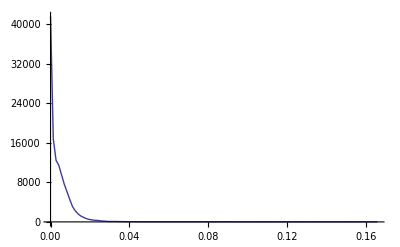

```mathematica
ListLinePlot[histo,PlotRange->All]
```

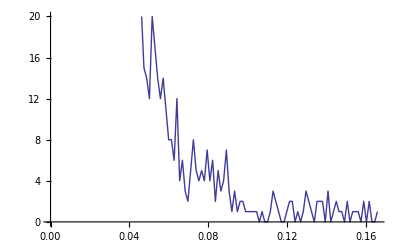

```mathematica
ListLinePlot[histo,PlotRange->{0,20}]
```

Using the histogram data itself, you can see that the threshold for the top 6 values is:

```mathematica
.155964/.165712
```

0.941175

#### Plain thresholding

The two sources mentioned by the paper essentially recommend thresholding for the accumulators with the highest votes.  Doesn't work here

Unfortunately, the top 6 values are all clustered in 3 of the peaks we evenually want to find.

```mathematica
Binarize[-Graphics-,0.9411750506903542]
```

-Graphics-

#### Threshold for 6 std-dev

Cutting off anything below 6 std-dev isolates the peaks nicely.  Though there is still a lot of garbage in the neighborhood, there aren't many spurious local maxima.  In fact, examining by eye, I see NO spurious local maxima.  And all of the neighborhoods that were preserved look pretty smooth.

```mathematica
With[{im=-Graphics-},
With[{mean=Mean[Flatten[ImageData[im]]],stddev=StandardDeviation[Flatten[ImageData[im]]]},
With[{bin=Binarize[im, mean+6*stddev]},
Image[ImageData[bin] ImageData[im]]
]]]
```

-Graphics-

#### Local maximum filter after std-dev threshold

I could, then, just try a simple local maximum filter on the non-zero pixels, that is, keep a pixel if it is greater than or equal to all of its neighbors.

```mathematica
Show[ImageFilter[Boole[#1[[2,2]]≠0&&#1⟦2,2⟧==Max[#1]]&,-Graphics-,1],ImageSize->{1024,120}]
```

-Graphics-

This seems to work, but it leaves some two-pixel groups.  Maybe I can take the mean of any connected component as its location.  (Better would be to fit some sort of multi-dimensional parabola).

## 11 June 2011 - Saturday

### More thresholding experiments

#### Threshold for 5 std-dev

How will things work for 5 rather than 6 std-dev?

```mathematica
origIm=-Graphics-;
```

```mathematica
thresh5StdDev = With[{im=origIm},
With[{mean=Mean[Flatten[ImageData[im]]],stddev=StandardDeviation[Flatten[ImageData[im]]]},
With[{bin=Binarize[im, mean+5*stddev]},
Image[ImageData[bin] ImageData[im]]
]]]
```

-Graphics-

#### Local maximum filter after 5 std-dev threshold

This leaves some spurious local maxima.  Rats!

```mathematica
ImageFilter[Boole[#1[[2,2]]≠0&&#1⟦2,2⟧==Max[#1]]&,thresh5StdDev,1]
```

-Graphics-

What happens if I eliminate pixels bordering a zero pixel?  The spurious local maximum is eliminated.

```mathematica
ImageFilter[Boole[#1[[2,2]]≠0&&#1⟦2,2⟧==Max[#1] && Min[#1]≠0]&,thresh5StdDev,1]
```

-Graphics-

#### Try 4 std-dev

But when I do 4 standard deviations, the spurious maximum is back.

```mathematica
thresh4StdDev = With[{im=origIm},
With[{mean=Mean[Flatten[ImageData[im]]],stddev=StandardDeviation[Flatten[ImageData[im]]]},
With[{bin=Binarize[im, mean+4*stddev]},
Image[ImageData[bin] ImageData[im]]
]]]
```

-Graphics-

```mathematica
ImageFilter[Boole[#1[[2,2]]≠0&&#1⟦2,2⟧==Max[#1] && Min[#1]≠0]&,thresh4StdDev,1]
```

-Graphics-

### Try thresholding only local maxima based on their distribution

The threshold still seems somewhat arbitrary.  The mean is increased.  However 4 standard deviations above it still gives me a spurious local maximum.

Here, I set all the local maxima in an 8-connected neighborhood to 1.

```mathematica
ImageFilter[Function[n,If[n[[2,2]]≠0 &&n[[2,2]]==Max[n],1.,0.]],origIm,Sqrt[2]]
```

-Graphics-

Now, eliminate all the ones on a zero boundary

```mathematica
ImageFilter[Function[n,If[n[[2,2]]≠0 &&n[[2,2]]==Max[n]&&Min[n]>0,1.,0.]],origIm,Sqrt[2]]
```

-Graphics-

Grabbing these local maxima, I make another image

```mathematica
localMaxes=ImageFilter[Function[n,If[n[[2,2]]≠0&&n⟦2,2⟧==Max[n]&&Min[n]>0 ,n[[2,2]],0.]],origIm,Sqrt[2]]
```

-Graphics-

A histogram looks about the same as the original.   Maybe a bit heavier tailed. The mean is a good bit higher

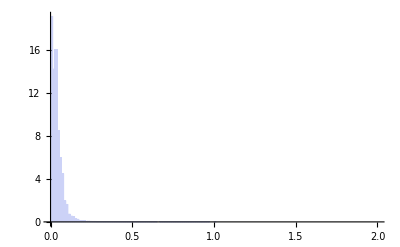

```mathematica
Histogram[Select[Flatten[ImageData[origIm]],#>0&],150,"ProbabilityDensity"]
```

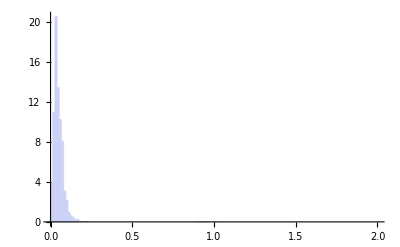

```mathematica
Histogram[Select[Flatten[ImageData[localMaxes]],#>0&],150,"ProbabilityDensity"]
```

```mathematica
StandardDeviation[Select[Flatten[ImageData[origIm]],#>0&]]
```

0.0418063

```mathematica
StandardDeviation[Select[Flatten[ImageData[localMaxes]],#>0&]]
```

0.0421682

```mathematica
Mean[Select[Flatten[ImageData[origIm]],#>0&]]
```

0.0385605

```mathematica
Mean[Select[Flatten[ImageData[localMaxes]],#>0&]]
```

0.0488879

```mathematica
With[{imd=Select[Flatten[ImageData[localMaxes]],#>0&]},
With[{mean=Mean[imd],stddev=StandardDeviation[imd]},
Binarize[localMaxes,mean+4*stddev]
]]
```

-Graphics-

### Choose only maxima that remain after blurring

If I first blur with a Gaussian and then select the local maxima, I get many fewer local maxima -- especially in the region of interest.  I try bluring, then thresholding, then selecting local max.  It gives me exactly what I want, though the maxima seem to be shifted:  One maximum appears at 683,52 in the original image, but at 683,53 in the blur-evaluated one.  Another, it is 627,77 and 628,79.   I may need to use something like edge-focusing to find the original maximum.

```mathematica
ImageFilter[Function[n,If[n[[2,2]]≠0 &&n[[2,2]]==Max[n],1.,0.]],GaussianFilter[origIm,10],Sqrt[2]]
```

-Graphics-

Blur the original.  Zero based on std dev.  Select local max

```mathematica
blurredMax=With[{im=GaussianFilter[origIm,10]},
With[{imd=Select[Flatten[ImageData[im]],#>0&]},
With[{mean=Mean[imd],stddev=StandardDeviation[imd]},
Image[Map[If[#≥mean+4*stddev,#,0.]&,ImageData[im],{2}]
]]]]
```

-Graphics-

```mathematica
Show[ImageFilter[Function[n,If[n[[2,2]]≠0 &&n[[2,2]]==Max[n],1.,0.]],blurredMax,Sqrt[2]],ImageSize->{1024,120}]
```

-Graphics-

### Use Patient Rule Induction Method (PRIM)

Doing edge-focusing method would be very complicated.  I'd have to derive the distance a peak can move and then do multiple passes in temporary buffers to keep from having to copy the entire accumulator array.  Edge focusing is complicated enough.  I think I will try the conceptually simpler PRIM first.

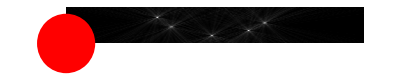

```mathematica
Graphics[{Raster[Reverse[ImageData[origIm]]],Red,Disk[{0,0},100]}]
```

```mathematica
Total[Flatten[ImageData[origIm]]]
```

3566.84

Below is the beginnings of an implementation of PRIM - I have continued the implementation on 12 June's entry

```mathematica
imageWithRect[im_Image, min_List, max_List]:=Graphics[{Raster[Reverse[ImageData[im]]],Red,FaceForm[{Blue,Opacity->0}],EdgeForm[Red],Rectangle[min,max]}]
```

```mathematica
sumArea[data_List, rect_List]:=(*data is a 2-d matrix.  Rect is a list {{minx,miny},{maxx,maxy}}*)
```

```mathematica
prim1Step[l_List]:=
With[{image=l[[1]],max=l[[2]],min=l[[3]],dummy=l[[4]]},
imageWithRect[image,{10,10},{1000,119}]
]
```

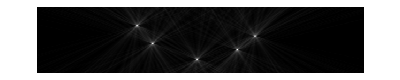

```mathematica
prim1Step[{origIm,{0,0},{10,10},{}}]
```

## 12 June 2011 - Sunday

### Trial Implementation of PRIM

I am implementing PRIM first in Mathematica because I want to be able to quickly see if it works and easily debug it.  This will provide some expected results for debugging my actual implemetation (assuming it works) as well as some guesses as to how to set the parameters.

#### The Code

I have moved the code to 13 June 2011 for further work.

#### Test the code

```mathematica
origIm=-Graphics-;
```

```mathematica
peel1Step[{origIm,{1,1},{1024,120},0.05,2}]
```

Part::partd: Part specification Null ⟦ 2 ⟧ is longer than depth of object.

{-Graphics-,{1,1},{768,120},0.05,2,-Graphics-}

The result of running to convergence does not yield one of the maxima itself.  The pasting step is necessary. (Note that for notebook compactness, I deleted the list of intermediate results.  However, the problem with the convergence is that the box shrinks to a long horizontal line trying to contain the two dense regions on the left and right, since it cannot shrink accross the empty space in-between without decreasing density.

```mathematica
FixedPointList[peel1Step,{origIm,{1,1},{1024,120},0.05,2}]
```

```mathematica
sumArea[ImageData[-Graphics-],{{358,69},{361,70}}]
```

2.61176

```mathematica
Length[%]
```

54

## 13 June 2011 - Monday

### Improve PRIM code

The PRIM code may be improved by adding bottom-up pasting step.

In my particular problem, I can probably fix things greatly by first thresholding to some number of standard deviations.  Then treating contiguous regions after thresholding as clusters and partitioning the space into bounding rectangles containing the clusters.  Finally, I do PRIM on the clusters to find their maxima.

Another idea would be to separate into clusters as above, but then just choose the maximum in each cluster rather than the local maximum as I did on the 10^th and 11^th.

I'm not sure how to do this thresholding in a continuous context.

#### The code

This code is moved from 12 June and then heavily modified

```mathematica
imageWithRect[im_Image, min_List, max_List]:=
With[{maxy=ImageDimensions[im][[2]]},
With[{newMin={min[[1]],maxy-min[[2]]+1},newMax={max[[1]],maxy-max[[2]]+1}},
Graphics[{Raster[Reverse[ImageData[im]]],Red,FaceForm[{Blue,Opacity->0}],EdgeForm[Red],Rectangle[newMin,newMax]}]
]]
```

```mathematica
imageWithRects[im_Image,rects_List]:=
(*Return a Graphics representing the given image with all of the rectangles in rects drawn on it in red*)
With[{maxy=ImageDimensions[im][[2]]},
Graphics[Join[{Raster[Reverse[ImageData[im]]],Red,FaceForm[{Blue,Opacity->0}],EdgeForm[Red]},
Map[
Function[rect,
With[{min=rect[[1]],max=rect[[2]]},
With[{newMin={min[[1]],maxy-min[[2]]+1},newMax={max[[1]],maxy-max[[2]]+1}},
Rectangle[newMin,newMax]
]]],
rects
]
]]
]
```

```mathematica
sumArea[data_List, rect_List]:=(*data is a 2-d matrix.  Rect is a list {{minx,miny},{maxx,maxy}}*)
If[Length[data]==0,0,
With[{minx=rect[[1,1]],miny=rect[[1,2]],maxx=rect[[2,1]],maxy=rect[[2,2]]},
With[{ysublist=Take[data,{miny,maxy}]},
If[Length[ysublist]==0,0,
With[{rectSublist=Transpose[Take[Transpose[ysublist],{minx,maxx}]]},
Total[rectSublist,2]
]]]]]
```

```mathematica
rectArea[rect_List]:=(*Rect is a list {{minx,miny},{maxx,maxy}}*)With[{minx=rect[[1,1]],miny=rect[[1,2]],maxx=rect[[2,1]],maxy=rect[[2,2]]},
(Abs[maxx-minx]+1)(Abs[maxy-miny]+1)
]
```

```mathematica
densityArea[data_List, rect_List]:=(*data is a 2-d matrix.  Rect is a list {{minx,miny},{maxx,maxy}}*)
sumArea[data,rect]/rectArea[rect]
```

```mathematica
myPart[data_List,partSpec_List]:=
Apply[Part,Join[{data},partSpec]]
```

```mathematica
incMyPart[data_,partSpec_List,delta_]:=(*Note that partSpec MUST have exactly two elements*)
data[[partSpec[[1]],partSpec[[2]]]]+=delta
```

```mathematica
SetAttributes[incMyPart,HoldFirst]
```

```mathematica
peelCoord[data_List,rect_List,removalFraction_,minSum_,partSpec_]:=
(*Return a list {rectangle,density} for a the rectangle that has sum at least minSum and which subject to that constraint removes at least removalFraction of the current sum by changing the edge of the current rectangle specified by partspec.  

data is a 2-d matrix.  Rect is a list {{minx,miny},{maxx,maxy}}. removalFraction is a number in [0,1].  minSum is a non-negative number.  partSpec is a list where {1,2} would specify [[1,2]].*)
With[{initialSum=sumArea[data,rect]},
With[{targetSum=Max[minSum,initialSum(1- removalFraction)],otherPart={Mod[partSpec[[1]]+1,2,1],partSpec[[2]]}},
With[{delta=Sign[myPart[rect,otherPart]-myPart[rect,partSpec]]},
Module[{curRect=rect,curSum=initialSum,nextRect=rect,nextSum=initialSum},
(*Sow["Start","Debug"];
Sow[{"RectAndSum",curRect,curSum},"Debug"];
Sow[{"parts",{partSpec,otherPart}},"Debug"];
Sow[{"nextRect",nextRect},"Debug"];
Sow[{"chgpart",myPart[nextRect,partSpec]},"Debug"];
Sow[{"otherpart",myPart[nextRect,otherPart]},"Debug"];
Sow[{"sums",{targetSum,initialSum}},"Debug"];*)
While[curSum>targetSum &&nextSum≥minSum&&myPart[nextRect,partSpec]≠myPart[nextRect,otherPart],
(*Sow[{"InLoop",curRect,curSum},"Debug"];*)
curRect=nextRect;curSum=nextSum;incMyPart[nextRect,partSpec,delta];nextSum=sumArea[data,nextRect]
];
{curRect,curSum/rectArea[curRect]}
]]]]
```

```mathematica
peel[data_List,rect_List,removalFraction_,minSum_]:=(*data is a 2-d matrix.  Rect is a list {{minx,miny},{maxx,maxy}} and removalFraction is a number in [0,1]*)
(*Returns the most dense rectangle from peeling removalFraction from any of the rectangle borders*)
With[{peels={
peelCoord[data,rect,removalFraction,minSum,{1,1}],
peelCoord[data,rect,removalFraction,minSum,{1,2}],
peelCoord[data,rect,removalFraction,minSum,{2,1}],
peelCoord[data,rect,removalFraction,minSum,{2,2}],
}},
With[{goodPeels=Select[peels,#[[1]]≠rect&]},(*goodPeels are those where something was peeled off*)
If[Length[goodPeels]>0,
Sort[goodPeels,#1[[2]]>#2[[2]]&][[1,1]],
rect]
]]
```

```mathematica
peel1Step[l_List]:=
With[{image=l[[1]],min=l[[2]],max=l[[3]],removalFraction=l[[4]],minSum=l[[5]]},
With[{newRect=peel[ImageData[image],{min,max},removalFraction,minSum]},
{image,newRect[[1]],newRect[[2]],removalFraction,minSum,imageWithRect[image,newRect[[1]],newRect[[2]]]}
]]
```

```mathematica
pasteCoord[data_List,rect_List,addingFraction_,minDensity_,partSpec_]:=
(*Return a list {rectangle,density} for a the rectangle that has density at least minDensity and which subject to that constraint adds approximately addingFraction of the current sum by changing the edge of the current rectangle specified by partspec.

data is a 2-d matrix.  Rect is a list {{minx,miny},{maxx,maxy}}. addingFraction is a number in [0,1].  minDensity is a non-negative number.  partSpec is a list where {1,2} would specify [[1,2]].*)
With[{initialSum=sumArea[data,rect],fullRect={{1,1},Reverse[Dimensions[data]]}},
With[{targetSum=initialSum(1+ addingFraction),otherPart={Mod[partSpec[[1]]+1,2,1],partSpec[[2]]}},
With[{delta=Sign[myPart[rect,partSpec]-myPart[rect,otherPart]]},
Module[{curRect=rect,curSum=initialSum,nextRect=rect,nextSum=initialSum},
(*Sow["Start","Debug"];
Sow[{"RectAndSum",curRect,curSum},"Debug"];
Sow[{"parts",{partSpec,otherPart}},"Debug"];
Sow[{"nextRect",nextRect},"Debug"];
Sow[{"chgpart",myPart[nextRect,partSpec]},"Debug"];
Sow[{"otherpart",myPart[nextRect,otherPart]},"Debug"];
Sow[{"sums",{targetSum,initialSum}},"Debug"];*)
While[curSum<targetSum &&myPart[fullRect,partSpec]≠myPart[nextRect,partSpec],(*Note that for ease of coding, the result rectangle can't ever be expanded to the edge of the data*)
(*Sow[{"InLoop",curRect,curSum},"Debug"];*)
curRect=nextRect;curSum=nextSum;incMyPart[nextRect,partSpec,delta];nextSum=sumArea[data,nextRect]
];
(*Return the pasted sum if it has sufficient density, the original rectangle otherwise*)
With[{curDensity=curSum/rectArea[curRect]},
If[curDensity>=minDensity,
{curRect,curDensity},
{rect,initialSum/rectArea[rect]}
]
]
]]]]
```

```mathematica
paste[data_List,rect_List,additionFraction_,minDensity_]:=(*data is a 2-d matrix.  Rect is a list {{minx,miny},{maxx,maxy}} and additionFraction is a number in [0,1]*)
(*Returns the most dense rectangle from adding additionFraction votes to any of the rectangle borders*)
With[{pastes={
pasteCoord[data,rect,additionFraction,minDensity,{1,1}],
pasteCoord[data,rect,additionFraction,minDensity,{1,2}],
pasteCoord[data,rect,additionFraction,minDensity,{2,1}],
pasteCoord[data,rect,additionFraction,minDensity,{2,2}],
}},
With[{goodPastes=Select[pastes,#[[1]]≠rect&]},(*goodPastes are those where something was pasted on*)
If[Length[goodPastes]>0,
Sort[goodPastes,#1[[2]]>#2[[2]]&][[1,1]],
rect]
]]
```

```mathematica
paste1Step[l_List]:=
With[{image=l[[1]],min=l[[2]],max=l[[3]],additionFraction=l[[4]],minDensity=l[[5]]},
With[{newRect=paste[ImageData[image],{min,max},additionFraction,minDensity]},
{image,newRect[[1]],newRect[[2]],additionFraction,minDensity,imageWithRect[image,newRect[[1]],newRect[[2]]]}
]]
```

```mathematica
inRect[x_,y_,rect_List]:=
(*Return true if the given coordinates lie within the given rectangle*)
With[{minx=rect[[1,1]],miny=rect[[1,2]],maxx=rect[[2,1]],maxy=rect[[2,2]]},
(minx≤x&& x≤maxx)&&(miny≤y&&y≤maxy)
]
```

```mathematica
zeroRect[im_Image,rect_List]:=
(*Return im with all coordinates covered by the given rectangle set to 0*)
With[{mask=Image[Array[If[inRect[#2,#1,rect],0.,1.]&,Dimensions[ImageData[im]]]]},
ImageMultiply[im,mask]
]
```

```mathematica
primRectangles[startIm_Image,removalFraction_,minSum_,extantRectangles_List]:=
(*Return the list of rectangles generated by the basic PRIM algorithm zeroing each rectangle after it is generated.  The extantRectangles list should start empty.*)
With[{min={1,1},max=ImageDimensions[startIm]},
With[{peeled=FixedPoint[peel1Step,{startIm,min, max,removalFraction,minSum}]},
With[{peeledMin=peeled[[2]],peeledMax=peeled[[3]]},
With[{peeledDensity=densityArea[ImageData[startIm],{peeledMin,peeledMax}]},
With[{pasted=FixedPoint[paste1Step,{startIm,peeledMin,peeledMax,removalFraction,peeledDensity}]},
With[{rect={pasted[[2]],pasted[[3]]}},
If[MemberQ[extantRectangles,rect],
extantRectangles,
Print[extantRectangles];
primRectangles[zeroRect[startIm,rect],removalFraction,minSum,Append[extantRectangles,rect]]
]
(*{rect,{peeledMin,peeledMax}}*)
]]]]]]
```

#### Test the basic peel and paste code

With the pasting things seem to work well.  I would like to try a procedure that peels, pastes, remembers the pasted region, peels again.  Sets the final region to the new peel and then zeroes the remembered pasted region.  Maybe the peel-paste cycle should be repeated until a peel or a paste repeats a previous region.  In my experiments, this didn't require very long.

```mathematica
origIm=-Graphics-;
```

I redo the peel step from yesterday because the plotting was wrong.  The results are actually better than they seemed.

```mathematica
FixedPointList[peel1Step,{origIm,{1,1},{1024,120},0.05,2}]
```

Results of peeling were: {358, 69}, {361, 70}

Here I show one pasting step

```mathematica
paste1Step[{origIm,{358,69},{361,70},0.05,densityArea[ImageData[origIm],{{358,69},{361,70}}]}]
```

Part::partd: Part specification Null ⟦ 1 ⟧ is longer than depth of object.

{-Graphics-,{358,68},{361,70},0.05,0.326471,-Graphics-}

```mathematica
FixedPointList[paste1Step,{origIm,{358,69},{361,70},0.05,densityArea[ImageData[origIm],{{358,69},{361,70}}]}]
```

The end result after pasting was: {356, 62}, {368, 71}, which when maginifed on the original image is:

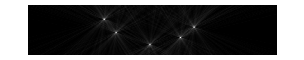

Then, try peeling again:

```mathematica
FixedPointList[peel1Step,{origIm,{356,62},{368,71},0.05,2}]
```

This resulted in: {362, 66}, {363, 67}

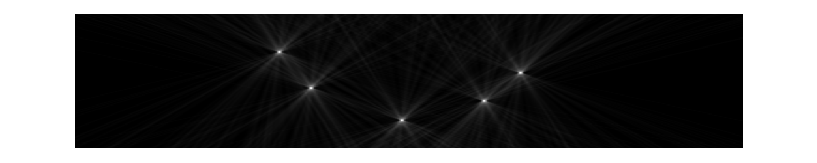

Now pasting again yields an unchanged region because this area is the local maximum.

```mathematica
FixedPointList[paste1Step,{origIm,{356,62},{368,71},12,densityArea[ImageData[origIm],{{356,62},{368,71}}]}]
```

#### What about using PRIM with thresholded input?

Looks like it works very well.  Unfortunately, thresholding is hard to do in the continuous case.

```mathematica
thresh4StdDev = With[{im=origIm},
With[{mean=Mean[Flatten[ImageData[im]]],stddev=StandardDeviation[Flatten[ImageData[im]]]},
With[{bin=Binarize[im, mean+4*stddev]},
Image[ImageData[bin] ImageData[im]]
]]]
```

-Graphics-

```mathematica
FixedPointList[peel1Step,{thresh4StdDev,{1,1},{1024,120},0.05,2}]
```

This gives: {362, 67}, {363, 68}

```mathematica
FixedPointList[paste1Step,{thresh4StdDev,{362,67},{363,68},0.05,densityArea[ImageData[thresh4StdDev],{{362,67},{363,68}}]}]
```

Pasting just expands by a few pixels: {361, 66}, {364, 68}

```mathematica
FixedPointList[peel1Step,{thresh4StdDev,{361,66},{364,68},0.05,2}]
```

Peeling again gives: {362, 66}, {363, 67}

```mathematica
FixedPointList[paste1Step,{thresh4StdDev,{362,66},{363,67},0.05,densityArea[ImageData[thresh4StdDev],{{362,66},{363,67}}]}]
```

Pasting again leaves things unchanged.

#### Test the primRectangles code

```mathematica
origIm=-Graphics-;
```

Test some of the component parts

```mathematica
inRect[2,3,{{1,1},{2,2}}]
```

False

```mathematica
zeroRect[origIm,{{356,62},{368,71}}]
```

-Graphics-

I started this run with a large minimum sum because I wanted to finish as quickly as possible.  It still took quite a while and produced 57 rectangles.  It requires 12 rectangles before all of the peaks are gotten.

```mathematica
primRectangles[origIm,0.05,15,{}]
```

{{{346,60},{441,74}},{{678,52},{686,56}},{{485,91},{577,108}},{{625,77},{631,80}},{{565,74},{648,76}},{{562,81},{643,82}},{{614,65},{646,92}},{{618,57},{702,59}},{{631,50},{696,51}},{{621,47},{700,49}},{{532,15},{747,46}},{{311,33},{316,36}},{{307,30},{321,39}},{{276,2},{398,60}},{{594,91},{609,101}},{{478,88},{484,116}},{{559,111},{576,119}},{{578,102},{590,116}},{{469,85},{477,120}},{{609,59},{613,100}},{{515,80},{523,119}},{{647,2},{658,119}},{{399,1},{405,120}},{{659,60},{681,92}},{{438,65},{513,93}},{{406,2},{428,119}},{{453,117},{557,120}},{{337,75},{381,80}},{{448,109},{575,110}},{{271,111},{552,116}},{{291,81},{561,84}},{{194,85},{605,94}},{{430,1},{570,14}},{{603,50},{608,119}},{{682,52},{698,104}},{{578,114},{691,120}},{{700,58},{707,102}},{{583,93},{678,113}},{{208,60},{642,64}},{{2,1},{1023,2}},{{506,55},{676,56}},{{560,52},{677,54}},{{345,2},{875,119}},{{268,2},{275,111}},{{259,9},{267,70}},{{247,3},{258,102}},{{262,95},{333,120}},{{232,2},{246,113}},{{191,95},{213,120}},{{207,2},{231,119}},{{185,73},{343,78}},{{135,118},{841,120}},{{165,2},{206,70}},{{2,65},{342,119}},{{2,3},{1023,17}},{{2,2},{1023,119}},{{1,1},{1024,120}}}

```mathematica
prim15Rects={{{346,60},{441,74}},{{678,52},{686,56}},{{485,91},{577,108}},{{625,77},{631,80}},{{565,74},{648,76}},{{562,81},{643,82}},{{614,65},{646,92}},{{618,57},{702,59}},{{631,50},{696,51}},{{621,47},{700,49}},{{532,15},{747,46}},{{311,33},{316,36}},{{307,30},{321,39}},{{276,2},{398,60}},{{594,91},{609,101}},{{478,88},{484,116}},{{559,111},{576,119}},{{578,102},{590,116}},{{469,85},{477,120}},{{609,59},{613,100}},{{515,80},{523,119}},{{647,2},{658,119}},{{399,1},{405,120}},{{659,60},{681,92}},{{438,65},{513,93}},{{406,2},{428,119}},{{453,117},{557,120}},{{337,75},{381,80}},{{448,109},{575,110}},{{271,111},{552,116}},{{291,81},{561,84}},{{194,85},{605,94}},{{430,1},{570,14}},{{603,50},{608,119}},{{682,52},{698,104}},{{578,114},{691,120}},{{700,58},{707,102}},{{583,93},{678,113}},{{208,60},{642,64}},{{2,1},{1023,2}},{{506,55},{676,56}},{{560,52},{677,54}},{{345,2},{875,119}},{{268,2},{275,111}},{{259,9},{267,70}},{{247,3},{258,102}},{{262,95},{333,120}},{{232,2},{246,113}},{{191,95},{213,120}},{{207,2},{231,119}},{{185,73},{343,78}},{{135,118},{841,120}},{{165,2},{206,70}},{{2,65},{342,119}},{{2,3},{1023,17}},{{2,2},{1023,119}},{{1,1},{1024,120}}};
```

```mathematica
imageWithRects[origIm,prim15Rects]
```

-Graphics-

```mathematica
imageWithRects[origIm,Take[prim15Rects,12]]
```

-Graphics-

Now, a run with a much smaller minSum.  This had 87 rectangles rather than 57.  The rectangles are concentrated in the high-profit area.  14 rectangles are needed before getting all the peaks.

```mathematica
prim2Rects=primRectangles[origIm,0.05,2,{}]
```

{{{356,62},{368,71}},{{352,72},{356,73}},{{622,73},{634,84}},{{369,60},{374,64}},{{671,43},{695,63}},{{366,72},{371,73}},{{616,81},{621,86}},{{501,95},{502,96}},{{612,87},{618,88}},{{500,97},{502,98}},{{497,94},{507,96}},{{493,97},{499,100}},{{483,87},{519,93}},{{308,29},{320,39}},{{492,101},{497,102}},{{486,103},{494,104}},{{482,105},{488,106}},{{492,108},{511,113}},{{630,85},{638,86}},{{634,71},{640,72}},{{500,97},{513,103}},{{514,103},{518,112}},{{512,100},{553,119}},{{613,74},{621,76}},{{337,58},{368,61}},{{369,69},{380,71}},{{302,37},{307,42}},{{601,85},{629,86}},{{295,44},{302,45}},{{308,40},{344,49}},{{357,72},{365,73}},{{321,27},{327,32}},{{635,74},{640,75}},{{635,81},{643,84}},{{377,55},{383,57}},{{323,25},{330,26}},{{328,50},{354,57}},{{327,23},{334,24}},{{326,21},{340,22}},{{594,54},{670,73}},{{321,37},{330,39}},{{305,27},{311,28}},{{298,25},{322,26}},{{667,41},{675,42}},{{662,39},{682,40}},{{336,62},{356,86}},{{328,19},{344,20}},{{338,8},{360,18}},{{312,27},{353,28}},{{296,22},{326,24}},{{511,76},{683,120}},{{295,20},{308,21}},{{292,27},{307,32}},{{698,37},{711,42}},{{315,16},{327,20}},{{638,15},{654,24}},{{281,4},{299,18}},{{683,32},{697,42}},{{705,30},{722,36}},{{709,26},{730,29}},{{715,24},{733,25}},{{737,14},{752,18}},{{657,47},{667,48}},{{644,46},{656,47}},{{658,49},{670,50}},{{381,52},{389,53}},{{369,1},{387,2}},{{412,27},{443,33}},{{658,43},{670,46}},{{392,4},{407,7}},{{119,2},{834,119}},{{835,1},{841,119}},{{842,1},{851,96}},{{852,2},{864,116}},{{865,1},{873,119}},{{96,2},{118,114}},{{82,1},{95,119}},{{874,1},{890,119}},{{891,2},{898,119}},{{899,3},{904,111}},{{62,2},{81,119}},{{905,2},{933,119}},{{56,2},{60,120}},{{49,1},{55,120}},{{934,1},{942,119}},{{2,1},{1023,120}},{{1,1},{1024,120}}}

```mathematica
Length[prim2Rects]
```

87

```mathematica
imageWithRects[origIm,prim2Rects]
```

-Graphics-

```mathematica
Show[imageWithRects[origIm,Take[prim2Rects,14]],ImageSize->1024]
```

-Graphics-

If we sort the rectangles by density, we still have to go out 12 before we get all the peaks.

```mathematica
prim2ByDensity=With[{data=ImageData[origIm]},
With[{den=Map[{densityArea[data,#],#}&,prim2Rects]},
With[{sorted=Sort[den,#1[[1]]>#2[[1]]&]},
Map[#[[2]]&,sorted]
]]]
```

{{{501,95},{502,96}},{{497,94},{507,96}},{{500,97},{502,98}},{{356,62},{368,71}},{{308,29},{320,39}},{{622,73},{634,84}},{{493,97},{499,100}},{{500,97},{513,103}},{{352,72},{356,73}},{{492,101},{497,102}},{{369,60},{374,64}},{{671,43},{695,63}},{{635,74},{640,75}},{{321,27},{327,32}},{{616,81},{621,86}},{{302,37},{307,42}},{{366,72},{371,73}},{{634,71},{640,72}},{{357,72},{365,73}},{{321,37},{330,39}},{{613,74},{621,76}},{{630,85},{638,86}},{{635,81},{643,84}},{{377,55},{383,57}},{{486,103},{494,104}},{{482,105},{488,106}},{{305,27},{311,28}},{{612,87},{618,88}},{{323,25},{330,26}},{{327,23},{334,24}},{{295,44},{302,45}},{{483,87},{519,93}},{{337,58},{368,61}},{{369,69},{380,71}},{{667,41},{675,42}},{{601,85},{629,86}},{{298,25},{322,26}},{{381,52},{389,53}},{{514,103},{518,112}},{{326,21},{340,22}},{{292,27},{307,32}},{{308,40},{344,49}},{{312,27},{353,28}},{{698,37},{711,42}},{{328,50},{354,57}},{{296,22},{326,24}},{{657,47},{667,48}},{{328,19},{344,20}},{{662,39},{682,40}},{{683,32},{697,42}},{{658,43},{670,46}},{{658,49},{670,50}},{{336,62},{356,86}},{{295,20},{308,21}},{{492,108},{511,113}},{{705,30},{722,36}},{{315,16},{327,20}},{{594,54},{670,73}},{{709,26},{730,29}},{{715,24},{733,25}},{{644,46},{656,47}},{{638,15},{654,24}},{{369,1},{387,2}},{{737,14},{752,18}},{{512,100},{553,119}},{{281,4},{299,18}},{{392,4},{407,7}},{{338,8},{360,18}},{{511,76},{683,120}},{{412,27},{443,33}},{{119,2},{834,119}},{{2,1},{1023,120}},{{1,1},{1024,120}},{{835,1},{841,119}},{{842,1},{851,96}},{{852,2},{864,116}},{{865,1},{873,119}},{{96,2},{118,114}},{{874,1},{890,119}},{{82,1},{95,119}},{{891,2},{898,119}},{{899,3},{904,111}},{{62,2},{81,119}},{{56,2},{60,120}},{{905,2},{933,119}},{{49,1},{55,120}},{{934,1},{942,119}}}

```mathematica
Show[imageWithRects[origIm,Take[prim2ByDensity,12]],ImageSize->1024]
```

-Graphics-

#### Rectangles on thresholded input

```mathematica
thresh4StdDev = With[{im=origIm},
With[{mean=Mean[Flatten[ImageData[im]]],stddev=StandardDeviation[Flatten[ImageData[im]]]},
With[{bin=Binarize[im, mean+4*stddev]},
Image[ImageData[bin] ImageData[im]]
]]]
```

-Graphics-

```mathematica
Timing[prim2ThreshRects=primRectangles[thresh4StdDev,0.05,2,{}]]
```

{404.16,{{{361,66},{364,68}},{{627,78},{628,79}},{{624,77},{632,81}},{{501,95},{502,96}},{{498,94},{506,97}},{{683,52},{684,54}},{{363,64},{365,65}},{{313,34},{314,35}},{{679,51},{688,55}},{{315,33},{316,35}},{{358,68},{361,69}},{{365,62},{368,71}},{{311,34},{312,36}},{{313,36},{316,37}},{{308,32},{321,33}},{{631,74},{635,84}},{{495,91},{498,101}},{{676,47},{678,58}},{{507,91},{508,101}},{{354,62},{371,67}},{{687,48},{691,59}},{{499,92},{509,100}},{{355,70},{358,71}},{{316,30},{321,39}},{{359,70},{363,71}},{{622,73},{623,83}},{{620,73},{636,83}},{{354,68},{370,69}},{{309,35},{310,37}},{{310,30},{311,38}},{{306,36},{312,39}},{{679,48},{681,57}},{{308,30},{324,31}},{{682,48},{686,57}},{{352,61},{364,73}},{{369,60},{637,119}},{{305,28},{325,40}},{{675,46},{696,49}},{{303,40},{692,59}},{{1,1},{1024,120}}}}

```mathematica
Show[imageWithRects[thresh4StdDev,prim2ThreshRects],ImageSize->1024]
```

-Graphics-

```mathematica
Show[imageWithRects[thresh4StdDev,Take[prim2ThreshRects,9]],ImageSize->1024]
```

-Graphics-

### Next idea:

Maybe we could sort the rectangles by internal max? Or we could use some kind of stochastic hill-climbing and combine those peaks where they end up at the same place.

## 14 June 2011 - Tuesday

### Read Robust regression and outlier detection by Peter J. Rousseeuw, Annick M. Leroy

### Began reading Outliers in statistical data by Vic Barnett and Toby Lewis

## 15 June 2011 - Wednesday

### Met to discuss Functional Metabolomics

### Helped Isaie determine that there was a significant correlation between the loadings from our PCA plot (VeVe and DsFu at 48 hrs) and from the two-class separation chosen by OPLS for DsVe vs DsFu.

### Read Outliers in statistical data by Vic Barnett and Toby Lewis

### Read How to detect and handle outliers by Boris Iglewicz and David C. Hoaglin

### Searched for more papers on outlier detection

## 16 June 2011 - Thursday

### Searched for more papers on outlier detection

### Read Statistical Fraud Detection: A Review by Richard J. Bolton and David J. Hand

This was suggested by Otey's dissertation, "Approaches to abnormality detection with constraints".  Unfortunately, this doesn't detail much about methods.  It is mainly about classes of fraud and their particular characteristics.

### Read Novelty detection: a review — part 1: statistical approaches by Markos Markou and Sameer Singh

Most of the work assumes the existence of pristine training data.  One promising paper wsa SJ Roberts - Novelty detection using extreme value statistics.  It seems that it may not require pristine training data.  Another paper first just thresholds its data using a certain number of standard deviations from the mean.

### Read (quickly) Outlier detection with the Kernelized Spatial Depth Function by Chen, Dang, Peng and Bart

#### Related work section

(neighbor) distance based algorithms have problems in high dimensions (Aggarwal and Yu 2001) but that has been attacked in

A. Lazarevic and V. Kumar, “Feature Bagging for Outlier Detection,” Proc. ACM SIGKDD ’05, pp. 157-166, 2005.
Which detects outliers using multiple random subspaces and then combines the results

A number of papers using the Mahalanobis distance (given a robust estimate for location and scatter matrix):

P.J. Rousseeuw and K. van Driessen, “A Fast Algorithm for the Minimum Covariance Determinant Estimator,” Technometrics, vol. 41, no. 3, pp. 212-223, 1999.

D.M. Rocke and D.L. Woodruff, “Identification of Outliers in Multivariate Data,” J. Am. Statistical Assoc., vol. 91, no. 435, pp. 1047-1061, 1996.

There is also a url http://www.wis.kuleuven.ac.be/stat/robust/libra.html (the corrected url is http://wis.kuleuven.be/stat/robust/LIBRA.html ) for a Matlab library with a robust estimator of multivariate location and covariance.  This library requires the Statistics Toolbox, but that is included with the Wright State Student License.

They compare their work to an active learning method:

N. Abe, B. Zadrozny, and J. Langford, “Outlier Detection by Active Learning,” Proc. ACM SIGKDD ’06, pp. 504-509, 2006.

It may be profitable to look at

A. Leonardis and H. Bischof, “Robust Recognition Using Eigenimages,” Computer Vision and Image Understanding, vol. 78, no. 1, pp. 99-118, 2000.
Which provides a robust dimensionality reduction algorithm

S. Fidler, D. Skocaj, and A. Leonardis, “Combining Reconstructive and Discriminative Subspace Methods for Robust Classification and Regression by Subsampling,” IEEE Trans. Pattern Analysis and Machine Intelligence, vol. 28, no. 3, pp. 337-350, Mar. 2006
Which uses the robust dimensionality reduction algorithm for classification

G. Danuser and M. Stricker, “Parametric Model Fitting: From Inlier Characterization to Outlier Detection,” IEEE Trans. Pattern Analysis and Machine Intelligence, vol. 20, no. 3, pp. 263-280, Mar. 1998
Which uses multiple least squares fits to detect outliers.  I'm not sure this would apply to us, since I don't have a parametric model of the data that I want to fit; the title makes me think there might be some generality - it's at least worth reading the abstract.

#### Spatial depth

They give a nice overview of the spatial depth function and show how it is related to the median.  The spatial depth function has its maximum at the "median" and decreases to 0 at infinity.  Thus small depths indicate being on the "surface" - that is, being an outlier.

D(x,𝒳)=1-1/(|𝒳∪{x}|-1)-‖∑_(y∈𝒳) S(y-x)‖ where S(x)=x/(‖x‖)if x≠0,0 otherwise

D(x,𝒳)=1 is a multidimensional generalization of the median.

#### Experimental results

All of their results are based on sample sizes of several hundred (at least), so I don't know how well they will do in our domain.

### Read (quickly) Anomaly Detection: A Survey by Varun Chandola, Arindam Banerjee, and Vipin Kumar

ESKIN, E. 2000. Anomaly detection over noisy data using learned probability distributions. In Proceedings of the 17th International Conference on Machine Learning. Morgan Kaufmann Publishers Inc., 255–262.
Uses EM to estimate whether data come from a pre-specified distribution or a uniform distribution by seeing how the learned parameters of each change when a point is moved from one to the other.

PARRA, L., DECO, G., AND MIESBACH, S. 1996. Statistical independence and novelty detection with information preserving nonlinear maps. Neural Comput. 8, 2, 260–269.
The low variance components will have low projection values for the normal vectors, but any high value projection will be an abnormal vectors.

### Read (quickly) Feature Bagging for Outlier Detection by A. Lazarevic and V. Kumar

They only test their method with relatively large data-sets (148 samples is their smallest) and in a 1-class learning scenario.

They use LOF as their low-dimensional outlier detector.  Then they compare against straight LOF.  Obviously, they do better.

As written, they do not give probabalistic confidence of outlierness.  I suspect that if one were to use probabalistic methods for the low dimensional, one might be able to get some kind of probability for the sum.

They used 10 subsets for all data-sets.

It looks like LOF has a tunable false-alarm rate.  This would give me the probability I want.

### Read Outlier Detection by Active Learning by N. Abe, B. Zadrozny, and J. Langford

There is no good confidence parameter for the results.  The classifier either gets it or it doesn't.  They also use larger samples.  I'm not sure how well their method would scale to small data (though, since it is based on supervised learning, I think it might scale.)

### Began reading Identification of Outliers in Multivariate Data by D.M. Rocke and D.L. Woodruff

The number of good points must be at least h=Floor[1/2 (n+p+1)] as a theoretical lower bound.  Which means that with p dimensions, we need at least p+1 known good points.  Since our dimensions are in the hundreds, we need hundreds of points.  This is from the paper:

Lopuhaa, H. P. and Rousseeuw, P. J. (1991), "Breakdown Points of Affine-Equivariant Estimators of Multivariate Location and Covariance Matrices", The Annals of Statistics, 19, 229-248

They use much larger n than p.  (Their partitions for the MCD search are 5*p.)

### Read the LIBRA documentation on the routine adjustedoutlyingness

Looking up the MCD, I found the following paper mentioned in the documentation for the LIBRA matlab library - it has multidimensional outlier detection built in.

The Skewness-Adjusted Outlyingness is described in: Hubert, M., and Van der Veeken, S. (2008), "Outlier detection for skewed data", Journal of Chemometrics, 22, 235-246.

The documentation mentions the Stahel and Donoho outlyingness estimator which was published in 1981 or 82.

## 17 June 2011 - Friday

### Read Outlier detection for skewed data by Hubert, M., and Van der Veeken, S.

They mention a book for location and scale estimation and using Mahalanobis distances for outlier detection:

Maronna RA, Martin DR, Yohai VJ. Robust Statistics: Theory and Methods. Wiley: New York, 2006.

They use a measure of outlyingness based on projection onto random 1-D vectors and taking the maximum outlyingness.

The skewness is not germaine for our dataset since it is many more than 10 dimensional and they notice that the skew-adjusted and non-skew-adjusted measures give the same results for both.

### Spoke with Dr. Raymer about whether to continue work on outlier detection

He said yes, continue.  We can probably make a paper out of it if no one has already done it.

Things discussed

#### Rat control group characterization

Combine rats of single species from all studies and make a model of controls' metabolites.  Would be really useful.  Similar to study he is reviewing right now.

#### Control rats + n others for outlier detection

By using control group rats (possibly from many studies) we can get a large normal population and then insert randomly some fraction of treatment rats as outliers.

This gives us labeled real data to use in our outlier detection test protocol.

#### Choose algorithms to test

When choosing them, think of how to explain to biologists the main idea of the algorithm.

Illustrate what happens at extreme cases.  For example on 1-D data or with all dimensions normal except for 1.

#### Proposals

Soon, we will be doing a large number of proposals.  I will be needed to choose what my tasks will be should they get approved.

#### other

(Not in the talk but thought seeing http://pubs.acs.org/doi/full/10.1021/tx0255774 that it might be good to look data that has a progression of samples rather than just controls.  This will yield non-spherical clusters and thus confuse the simpler outlier techniques.  This is something that occurs in real life all the time.  For this, we could use the set of high-dose animals over time (with time included in the vector?) and then pop a control animal into the mix.

### Started to look specifically at the metabolomics field for outlier methods

#### The meta-p system

http : // www.hindawi.com/journals/jbb/2011/839862/

Outlier if metabolite quantities exceed 1.5 IQR on 30% of the data columns.

#### Hotelling T^2 ellipses

Source-code for generating them is at http://www.geekysuavo.org/hotelling/

The ellipses are confidence intervals for the mean of the group.

For a value to lie outside the ellipses means that that value won't be the mean in (e.g 95%) of the samples.

Hotelling's ellipses are placed at 2σ

SIMCA says that strong explainable outliers will be outside the T2 ellipse

SIMCA uses hotelling ellipses centered on the PCA model mean.

##### www.chemometrics.se

Advocate using deviation in the first few PCA dimensions to detect outliers as well.  ( http://www.chemometrics.se/index.php?option=com_content&task=view&id=60&Itemid=27 )

Workhorse in chemometrics to get an overview of the multivariate profiles. Examining the scatter plot of the first two score vectors (t1-t2) reveals the homogeneity of the data, any groupings, outliers, and trends. Strong outliers are found as deviating points in the scatter plot.

#### SIMCA command DMODX

Residual error over the PCA is large. (I am guessing - see page 16 of chapter 14 of Metabolomics: Methods and Protocols)

D Mod X means "distance to model".  They say "distance to model plane"  but their diagrams seem to imply they really mean perpendicular distance to the given principal component axis.  They have a critical value for it.

From the FAQ

##### 3.9 What is the difference between Scores and DModX contribution plots?

The contribution plot of scores shows variation which is explained, i.e.which variables contribute to
the model.The contribution plot of DMod X shows variation which is not explained, i.e which variables
contribute to the high DmodX.

#### International NMR-Based Environmental Metabolomics Intercomparison Exercise

This outlier detection technique was for groups of data from various laboratories.  It may still be useful to compare.

http://dx.doi.org/10.1021/es802198z

International NMR-Based Environmental Metabolomics Intercomparison Exercise
Mark R. Viant, Daniel W. Bearden, Jacob G. Bundy, Ian W. Burton, Timothy W. Collette, Drew R. Ekman, Vilnis Ezernieks, Tobias K. Karakach, Ching Yu Lin, Simone Rochfort, Jeffrey S. de Ropp, Quincy Teng, Ronald S. Tjeerdema, John A. Walter, Huifeng Wu
Environmental Science & Technology 2009 43 (1), 219-225

"Quality metrics were based on a set of ‘exercise consensus values’ for the mean and standard deviation of each integrated peak after an outlier analysis. The outlier analysis is based on robust statistics and draws from ideas related to Mandel’s h and k graphical tests (26). The analysis was performed by iteratively constructing box-plots of the grouped data and eliminating data that fell outside the box-plot whiskers (representing the upper or lower quartile ± 1.5 times the interquartile range) until, after 2 or 3 iterations, all the remaining data was within the box-plot whiskers. Of the total of 110 NMR spectra of synthetic mixtures (11 spectra for each of 10 data sets) comprising 770 semiquantitative values, only 35 individual values were determined to be outliers, including four spectra (S1a and S1b in data sets 00115 and 00122, all from the same laboratory and for which all 6 metabolites per spectrum were outliers), for which a simple, systematic error was detected. These 4 spectra were excluded from all subsequent analyses."

Reference 26 says:

26. Accuracy (trueness and precision) of measurement methods and results - Practical guidance for the use of ISO 5725-2:1994 in designing, implementing and statistically analysing interlaboratory repeatability and reproducibility results, 1st ed.; (ISO/TR 22971:2005), 2005.

Examining a draft version the referenced ISO document, it is clear that they looked at all the samples from one laboratory together.

#### (won't use) Application of Fuzzy c-Means Clustering in Data Analysis of Metabolomics

They do use fuzzy c-Means clustering to detect outliers.  But their methods are very ad-hoc and depend on using known class labels to drive the parameter choices (which invalidates their claim that their Fuzzy C-means is unsupervised)

They also are using GC data not NMR

#### Analytical reproducibility in 1H NMR Based Metabonomic Urinalysis

They plot the elipses but mostly ignore them, but they note one sample (in figure 2) as a strong outlier because of its distance from the main cluster of the data.

They also use the circular boundaries when looking at single dose-groups of animals.

### Read important parts of Breakdown Points of Affine-Equivariant Estimators of Multivariate Location and Covariance Matrices by Lopuhaa, H. P. and Rousseeuw, P.J.

Breakdown point is the fraction of data needed to change the location parameter to infinity.  For covariance it is the fraction needed to change the largest eigenvalue to infinity or the smallest to 0.

Theoretical upper bound for translation and orthogonal invariant location parameters is Floor[(n+1)/2]/n no matter how many dimensions (p is dimensions, n is sample size).  And there are estimators that meet this bound.  The paper shows affine invariant estimators that exceed the bound Floor[(n-p+1)/2]/n for 2 dimensions, but does not show whether location can be estimated affine-invariantly meeting the upper bound for all p..

Since affine and orth estimators are also translation invariant, the bound holds for them as well.

For covariance estimators he only gives ones that have a breakdown point of Floor[(n-p+1)/2]/n.  Thus for affine invariant estimation the suggestion that the number of outliers to be detected is < n-Floor[(n-p+1)/2] seems like a good idea with the current understanding of how well we can estimate the various parameters.

## 18 June 2011 - Saturday

### Worked on making list of algorithms to investigate for Dan

#### Angle Based Outlier Detection (ABOD)

#### Axis-parallel subspace outlier detection(SOD)

#### Feature Bagging LOF

#### Active Learning

#### LIBRA adjustedoutlyingness - skewed and unskewed versions

#### The method from Identification of Outliers in Multivariate Data

Use all algorithms and their implementations from ELKI

### Tried Google scholar search (+outlier +"small sample" +"high dimensional")

I looked at the first 50 results.

### Read Microarray data analysis: from disarray to consolidation and consensus by David B. Allison, Xiangqin Cui, Grier P. Page and Mahyar Sabripour

Doesn't really touch on outliers

Mentions that methods have been developed for doing statistical power analysis.

Their basic measure of gene change is "fold-change" which is ratio final/initial.  (Though this needs to be modified to have reliable statistical meaning.)

Rather than using the Bonferroni or other corrections to change the α of the statistical tests for biomarker significance, they use False Discovery Rate (FDR) - The expected proportion of rejected null hypotheses that are false positives.  That is, if your FDR is 10% then 10% of your conclusions will be wrong.

It is common to use mixture models to estimate the FDR after the fact rather than using test methods that guarantee the FDR before-hand.  This allows their tests to be more powerful (have fewer false negatives).

FDR methods have trouble with dependence among transcripts.  (Thus won't be directly applicable to our data :(   since we have lots of highly dependent variables )

They use Gene-Class testing - usually Gene Ontologies classify genes into categories, but other methods also exist.  The authors have several important criticisms against gene class testing.   The authors report GSEA and erminej as the best current algorithms as of 2006

IDEA: GCT helps push me toward the idea that we could use known metabolic pathways to classify known metabolites into groups that covary together.  Then we could look for these groups rather than just individual metabolites.  The stronger hypotheses should yield more sensitive tests.  A google search reveals that there are currently some investigations into making metabolite ontologies

Unsupervised clustering should be validated by resampling to verify reproducibility

### Read Bayesian analysis of outlier problems using the Gibbs sampler by Verdinelli, Isabella and Wasserman, Larry

Not sure how well it would do on high dimension, small-sample data, but it is an interesting idea.  (The Google search turned it up because they do mention the word high-dimension.)

They use a Gibbs sampler to estimate the parameters of the assumed underlying distribution directly from the data.  They perform the necessary analysis for several different distributions, so it wouldn't be too hard to adapt one.

### Skimmed A New Test for Outlier Detection From a Multivariate Mixture Distribution by Suojin Wang, Wayne A Woodward, H.L. Gray, Stephen Wiechecki, and Stephan R. Sain

This was suggested by "Estimating misclassification error with small samples via bootstrap cross-validation"

It does not really make use of small samples or high-dimensions, however.  It is more concerned with mixtures of known numbers of components and partially unlabeled data

### Skimmed Combining Random and Specific Directions for Outlier Detection and Robust Estimation in High-Dimensional Multivariate Data Daniel Pena and Francisco J. Prieto

Contains a modification of the search direction generation for Stahel-Donoho to make it more efficient.

They think their estimator might work well when number of samples < num dimensions, but they do no testing.  Their biggest dim test is 18 variables and 1272 samples.

### Skimmed Machine learning techniques for brain computer interfaces

They deal with high dimension, small sample; but they don't give any prescription on how to deal with outliers, they just say that not doing so will cause problems.

### Read parts of Many accurate small-discriminatory feature subsets exist in microarray transcript data: biomarker discovery by Leslie R Grate

They do brute-force feature selection for singlets, pairs, and triples and select those which classify best.  In some cases, the number of samples are sufficiently high that finding such good classifiers is better than chance.  In other cases, though they try and say otherwise, classifiers are to be expected by chance.

They use a fast max-margin algorithm LIKNON for which they cite two papers:

Grate L, Bhattacharyya C, Jordan M, Mian I: Simultaneous relevant feature identification and classification in high-dimensional spaces. In Workshop on Algorithms in Bioinformatics (WABI 2002). Edited by Guigó R, D G. Springer; 2002:1-9. OpenURL

Bhattacharyya C, Grate L, Jordan M, Ghaoui L, Mian I: Robust sparse hyperplane classifiers: application to uncertain molecular profiling data. Journal of Computational Biology 2004, 11(6):1073-1089

This is still a good idea to keep in mind when looking for biomarkers.  If you have enough samples, try a brute-force search for a (max-margin) linear classifier.

### Looked at Google Scholar search ( +("outlier detection" OR "anomaly detection" OR "novelty detection") +"small sample" +"high dimensional" )

Looked at the first 20 results (should probably look a bit more)

### Read parts of The behavior of the Stahel-Donoho Robust Multivariate Estimator by Ricardo A Maronna and Victor J Yohai

They do attempt to look at "high dimension" and "small sample size".  The samples are indeed small - n=20.  But the dimensions are not high by today's standards: 4-6.

However, SD is worth a look -- especially since it is implemented in LIBRA, so we don't need to try to implement it.

### Read a very small amount of Robust Distances: Simulation and Cutoff Values by Peter J. Rosseeuw and Bert C. van Zomeren

They are looking at small sample behavior - but their p only goes up to 4.  The MVE seems to work

They propose a rule-of-thumb that there should be at least 5 observations per dimension.  (that is  n ≥ 5p)

They use orthogonal directions for Stahel-Dohono rather than random subsets - but things still seem to work out (this method is what is used by LIBRA when n < 5p).

They go up to 20 dimensions with 50 samples for the projection algorithm.  This is the only case that begins to come close to our complexity.  The algorithm has problems - coverage at 25% contamination is 89% rather than near 75%.

This seems to be an important paper.  I may want to look at it more closely later.

### Read the beginning of Hypergraph-based Anomaly Detection of High-Dimensional Co-occurrences by Jorge Silva and Rebecca Willett

Focused very narrowly on the co-occurrence problem.  (For example, a meeting of several people is a co-occurrence.  They want to find out whether any meetings are anomalous.)  I am not sure how to map this to the space of normal outlier detection.

I didn't read carefully enough to see if their training data needs to be anomaly free.

They mention two papers that prove that the uniform alternative distribution is the optimal choice for "maximizing the worst case detection
rate among all possible anomalous distributions"

C. Scott and E. Kolaczyk, “Nonparametric Assessment of Contamination in Multivariate Data Using Minimum Volume Sets and FDR,” technical report, Univ. of Michigan, 2007.

R. El-Yaniv and M. Nisenson, “Optimal Single-Class Classification Strategies,” Advances in Neural Information Processing Systems, 2007.

### Read Isolation Forest by Fei Tony Liu, Kai Ming Ting and Zhi-Hua Zhou

This looks like a very interesting method.  They say it works well in high dimensions.  Of course, the question is, how small a sample-size can it handle.  There are promising possibilities because it needs small subsamples to work well.

Reading more thoroughly, requires an attribute selector to reduce dimensionality (they use kurtosis) before handling high-dimensional data.

They mention a paper as "best performing method" (this is in 2008).  The title indicates that it might be interesting to us.

M. Wu and C. Jermaine. Outlier detection by sampling with accuracy guarantees. In Proceedings of the 12th ACM SIGKDD international conference on Knowledge discovery
and data mining, pages 767–772, New York, NY, USA, 2006. ACM.

They compare with the ORCA algorithm.  On their data ORCA compares well with LOF.  ORCA gets confused on their high-d dataset.

Bay, S. D., and Schwabacher, M. (2003). Mining Distance-Based Outliers in Near Linear Time with Randomization and a Simple Pruning Rule. Proceedings of The Ninth ACM SIGKDD International Conference on Knowledge Discovery and Data Mining.

### Read parts of Mining Distance-Based Outliers in Near Linear Time with Randomization and a Simple Pruning Rule by Stephen D. Bay and Mark Schwabacher

This is the paper that defines ORCA.  It doesn't compare with any other methods directly for accuracy.  It doesn't have a false-alarm number and you specify in advance how many outliers to return.

ORCA has source code available. http://stephenbay.net/orca/

Being distance-based it should have trouble in high dimensions, but it seemed ok in their tests.  Isolation Forest's tests, not so much.

ORCA is distance-based, LOF is density based

### Read parts of Angle-Based Outlier Detection in High-dimensional Data by Hans-Peter Kriegel, Matthias Schubert and Arthur Zimek

Uses angles to the other points.  N^3 though they have approximatiions.  Since our sample-sizes are small.  We can use the whole thing.

Source code is available. ( http://www.dbs.ifi.lmu.de/cms/Outlier_Detection ) - Part of ELKI

Hard to interpret which should be labeled an outlier

Interpreting and Unifying Outlier Scores indicates that a logarithmic scaling of the score makes it much more interpretable.  They also have a transformation to something like a probability.

### Read small part of Outlier Detection in Axis-Parallel Subspaces of High Dimensional Data by Hans-Peter Kriegel, Peer Kroger, Erich Schubert, and Arthur Zimek

Outlier Detection in Axis-Parallel Subspaces of High Dimensional Data In Proceedings of the 13th Pacific-Asia Conference on Knowledge Discovery and Data Mining (PAKDD), Bangkok, Thailand, 2009.

Source code is available. ( http://www.dbs.ifi.lmu.de/cms/Outlier_Detection )

May be better than ABOD for our data because it can ignore irrelevant attributes

### Read Interpreting and Unifying Outlier Scores by Hans-Peter Kriegel, Peer Kroger, Erich Schubert,and Arthur Zimek

Transform any outlier score into something like a probablility.  Can be used to create ensembles, or (as in our case) to set some thresholds.

We WILL be using this.  (And I expect we will be using the ELKI code for a number of the implementations of our algorithms.)

## 19 June 2011 - Sunday

### Worked on making list of algorithms to investigate for Dan

#### Angle Based Outlier Detection (ABOD)

#### Axis-parallel subspace outlier detection(SOD)

#### Feature Bagging LOF

#### Active Learning

#### LIBRA adjustedoutlyingness - skewed and unskewed versions

#### The method from Identification of Outliers in Multivariate Data

Use all algorithms and their implementations from ELKI

Be sure to include MCD+mahalonobis distance

### Read part of Computational proteomics: management and analysis of proteomics data

Not useful, neither it (an introduction by a journal editor to a special issue) nor its component articles deals with outlier detection.

### Read part of Detecting potential labeling errors in microarrays by data perturbation and its sequel

These articles are focused on labeling errors and ignore other kinds of outliers.

### Read part of Challenging anomaly detection in wire ropes using linear prediction combined with one-class classification by Esther-Sabrina Platzer, Joachim Denzler , Herbert Suße , Josef Nagele and Karl-Heinz Wehking

They need a large training set

### Read 1st two pages of Multivariate outlier detection and robustness by M Hubert and P ROUSSEEUW

They are mainly focusing on using the MCD and then the Mahalonobis distances

### Searched for outlier in Chemometrics and Intelligent Laboratory Systems (an Elsevier journal)

Examined all 11 papers from the results

### Read introduction to Algorithms for Projection–Pursuit robust principal component analysis by C. Croux, P. Filzmoser and M.R. Oliveira

They focus on improving the stability of the computation of the projection-pursuit CR estimator in high dimensions

### Read the first part of On the geometry of SNV and MSC by Tom Fearn, Cecilia Riccioli, Ana Garrido-Varo, José Emilio Guerrero-Ginel

They illustrate the known formation of ellipsoids in principal component space when doing SNV (which I first thought was what we call autoscaling: doing a z-score transformation using the mean and standard deviation of each variable).  However, SNV treats the entire spectrum as a point and subtracts the mean from the spectrum and then scales by the standard deviation of all spectra.

### Read the introduction and part of related work from Simultaneous variable selection and outlier detection using a robust genetic algorithm by Wiegand, Patrick; Pell, Randy; and Comas, Enric

They focus on regression.

### Skimmed Improving hierarchical cluster analysis: A new method with outlier detection and automatic clustering by J.A.S. Almeida, L.M.S. Barbosa, A.A.C.C. Pais, S.J. Formosinho

All their test-data is low-dimensional.

They do have an outlier removal step: they use a hypersphere around individual objects and the number of nearest neighbors in this sphere is the connectivity of the object.  The sphere radius is a multiple of the average distance to the nearest neighbor and the threshold is average connectivity.   Then (with a slight modification) they iterate removing outliers.

These density-based methods are likely to fail in high dimensions.

The clustering looks interesting.  But I believe this was chosen as a secondary journal, and that this was rejected from some more main-stream clustering outlets.  I did not see a lot of chemometric-specific material.

### Read Robust statistics in data analysis — A review: Basic concepts by M. Daszykowski, K. Kaczmarek, Y. Vander Heyden, B. Walczak

They describe using either univariate outliers or the robust estimate of the location and scatter and the Mahalanobis distance based on these.

They also propose reducing the data to an optimal number of principal components using robust PCA and some measures in the article to determine optimal number of PCs.  Then the distances and the residual (orthogonal distance) are calculated (residual from the reconstruction using the selected PCs) and thresholded using χ^2distributions or approximations thereof.  My own observation is that, for the score distance, this is equivalent to the Mahalanobis distance above.

### Read part of Factorial experimental design: Detecting an outlier with the dynamic variable and the Daniel's diagram by Goupy, Jacques

He is concerned with the opposite special case from us.  His experiment has exactly one sample per condition, (e.g. one rat control, one with drug1, one with drug2, one with drug1 and 2), one measured response variable, and at most one outlier.

He wants to find whether there is an outlier, and, if there is an outlier remove it and estimate the missing data.

This is very low dimensional but also interesting.  Not for our problem though.

### Skimmed A Decision Tree Classifier Design for High-dimensional Data with Limited Training Samples

I read this with the objective of seeing if there were a good replacement for C4.5 in active learning.  They use a simple decision tree and a feature extraction preprocessing technique.  Their small number of samples is from 200-400

I'll need to look farther.  A quick search yielded a number of papers.

### Read part of Robust principal components regression based on principal sensitivity vectors by M.H. Zhang, Q.S. Xu 1, D.L. Massart

The authors are mainly concerned with regression.  However, this is spectroscopy data, so I read a little more.  They give a good summary of one method of outlier detection: detect leverage points, then use regression to classify leverage points into good and bad.

### Read part of Robust methods for multivariate analysis -- a tutorial review by Yi-Zeng, Liang; Kvalheim, Olav M.

They focus on lower dimensionality and classical outlier detection.  However, it might serve as a good review to read it more thoroughly.

They open by mentioning that of 250 error distributions examined by one meta-study only 10-15% were approximately normally distributed.  They close with an exhortation to analyze robust methods for use in chemometric contexts.

## 20 June 2011 - Monday

### Worked on making list of algorithms to investigate for Dan

#### Angle Based Outlier Detection (ABOD)

#### Axis-parallel subspace outlier detection(SOD)

#### Feature Bagging LOF

#### Active Learning

#### LIBRA adjustedoutlyingness - skewed and unskewed versions

#### The method from Identification of Outliers in Multivariate Data

Use all algorithms and their implementations from ELKI

Be sure to include MCD+mahalonobis distance

We should also include the SHV and RHM methods from Outlier Detection in Multivariate Analytical Chemical Data by William J. Egan and Stephen L. Morgan, since they were published in a chemical journal and claimed to work well on spectrographic data

We should include the jacknifed Mahalanobis distance from Prestige centrality-based functional outlier detection in gene expression analysis by Ali Torkamani and Nicholas J. Schork.  Note that they don't have a specific threshold.

### Searched for (Title: "outlier detection" OR "anomaly detection" OR "novelty detection") in JCISD - Journal of Chemical Information and Computer Sciences

Examined all 7 of the results

### Skimmed Support Vector Regression Approach for Simultaneous Data Reconciliation and Gross Error or Outlier Detection by Yu Miao, Hongye Su, Ouguan Xu and Jian Chu

They are interested in industrial processes with known expected relations between many of the components.  This is different from our situation.

### This definitely goes in our related work Outlier Detection in Multivariate Analytical Chemical Data by William J. Egan and Stephen L. Morgan

#### Related work

I need to go through their related work section more thoroughly

They mention an article doing comparison on near-IR data for MVE versus straight Mahalanobis distance (as usual, in this #@!$!#$ journal, they don't give the article title).

Cho, J.; Gemperline, P. J. J. Chemom. 1995, 9, 169-178.

#### Data sets

The data-set I am most interested in is the RA-IR dataset.  They don't report the number of variables or any information.  They refer you to the supplemental information that refers you to Egan's dissertation.  From the intro, however, I assume that this dataset has 100's of variables since he mentions near infared using more than 100 wavelengths.

#### Algorithms

They propose two new methods that they claim are 1) easy to understand 2) easy to implement and 3) Comparable in performance to the robust statistical literature methods

Their algorithms are not theoretically justified and have fiddle constants to which they have assigned arbitrary values with intuitive justifications.

Their first method RHM (resampling by half-means) consists of calculating a location and diagonal covariance matrix from q samples of the data (taking half the data for each sample).  Then the squared Mahalanobis distances are calculated for each data point.   The top 5% of these lengths are examined and each vector is assigned a score according to how often it appears in that top 5%.  They do not say what cut-off they use, but 70/500 was considered an outlier, whereas 40/500 was not.  I would guess, then that 10% is the cut-off.

Their second method SHV (smallest half-volume) calculates the sum of the distances to the n/2 nearest neighbors.  Then chooses the observation with the smallest sum and the n/2 nearest neighbors nearest it to calculate the mean and covariance.  Finally, the outliers are detected based on (I assume) the χ^2 score of their Mahalanobis distance to the calculated mean.

#### Results

Wood dataset: MVT and straight Mahalanobis both failed.  MCD, RHM & SHV succeeded.  The

HBK dataset: everyone identified the outliers.  No false positive results are reported.

In their simulation evaluation, they choose 500 groups of random parameters for the distribution.  They used multivariate Gaussian underlying and the same distribution shifted for the alternative.  Then they report average performance on detection % (accounting for false negatives only), no false positives.  They report that false positives were about equal for MCD, RHM, and SHV.

MVT had bad results.  I won't get into the details

RHM and SHV are quite sensitive to the fraction of outliers and somewhat sensitive to the shift distance.

They use a more useful definition of "breakdown", that is, the conditions under which no outliers are detected.  (In the statistical literature, breakdown means, "can change the estimated quantity to infinity (or 0 in case of lowest covariance eigenvalue)"

They don't report the affect of dimension versus number of observations on any of the methods.

### Searched Bioinformatics for articles with outlier and detection in the title

I examined all 3 results

### Read parts of Prestige centrality-based functional outlier detection in gene expression analysis by Ali Torkamani and Nicholas J. Schork

They are using gene expression values.  They create a network where the strength of an edge is based on the correlation (or mutual information) between their expression.  The ARACNE algorithm was used to create the network.  I won't get into the rest of the details because it does not concern the outlier detection.

For outlier detection, they use the jacknifed Mahalanobis distance:

d(x)=√((P_i(x)-OverBar[P(x)])^T S^-1(P_i(x)-OverBar[P(x)]))

where P_i(x) represents a matrix containing the scores of gene x over samples i,  OverBar[P(x)] is is a matrix of the means of P(x) not including the i-th sample and S  is the estimated covariance matrix of the entire dataset not including gene x.

### Read parts of Cancer outlier detection based on likelihood ratio test by Jianhua Hu

It is hard to follow the author's description of the problem.  I wish the notation were improved.  I believe they are testing whether between two groups of labeled variables, there are axes where one variable has a different mean than another.

If I understood correctly, we are not interested in this.

### Began reading OutlierD: an R package for outlier detection using quantile regression on mass spectrometry data by HyungJun Cho, Yang-jin Kim, Hee Jung Jung, Sang-Won Lee and Jae Won Lee

The method is interesting, but I don't believe it applies to us.

They have two samples for each peptide.

They use the mean and the difference to plot points in 2D space.  Then, they calculate a regression function of the mean that best splits the values into the appropriate quantile (0.25 and 0.75).  They use either a constant, linear, non-linear (cubic?) or non-parametric (piecewise-linear?) model.  Then they use the iqr calculated from the difference between the calculated regressors and the 0.50 regressor to calculate the outlier boundaries.

### Searched Bioinformatics for articles with outlier in the title

It returned 7 results (3 of which I had already read).  I read all but the last 2 which were before the date that the Ohio EJC subscription begins.  They are from 1988, so I believe that they are probably not useful anyway.

### Read about half of Power enhancement via multivariate outlier testing with gene expression arrays by Adam L. Asare, Zhong Gao, Vincent J. Carey, Richard Wang, and Vicki Seyfert-Margolis

They are only using 9-D data.  But their best method PVMO (Parametric MultiVariate Outlier labeling) requires principal components reduction down to 3 components.  The MDC (their other method) is already included in our suite of methods, although they give a recent reference to it.  From the title, I gather that this is recent because of the new application not because of a new method.

Cohen Freue,G.V. et al. (2007) Mdqc: a new quality assessment method for microarrays
based on quality control reports. Bioinformatics, 23, 3162–3169.

I don't think we'll use these methods.

### Searched Journal of Computational Biology for "outlier" and "detection"

They returned 56 items which I examined all of them, but I sped up after #30 because of the low hit rate, so I may have been sloppy.

### Read most of A Consolidated Approach to Analyzing Data from High-Throughput Protein Microarrays with an Application to Immune Response Profiling in Humans by MARIUSZ LUBOMIRSKI, MICHAEL R. D’ANDREA, STANLEY M. BELKOWSKI, JAVIER CABRERA, JAMES M. DIXON, and DHAMMIKA AMARATUNGA

They do no serious automatic outlier detection.  (Their outlier method is to do a spearman correlation between the normalized arrays combined with a visual inspection of box plots.

### Skimmed A Polynomial-Time Nuclear Vector Replacement Algorithm for Automated NMR Resonance Assignments by CHRISTOPHER JAMES LANGMEAD, ANTHONY YAN, RYAN LILIEN, LINCONG WANG, and BRUCE RANDALL DONALD

They are interested in making resonance assignments that are resistant to outliers.

Not of interest to us (except in so far as they are doing resonance assignments) but their method attacks a different situation than metabolomics.  They know what molecule is in their solution, they want to find out what its shape is.

### Searched Journal of Computational Biology for the specific keywords "outlier" or "outliers"

No articles were returned

### Searched MEDLINE with full text using EBSCO HOST for outlier or outliers in the title

After the search, selected only the journal of Biopharmaceutical Statistics and PAMI (there were other journals, but I ignored them)

I examined all 12 results.

The first article (A new outlier identification test for method comparison studies based on robust regression.) was embargoed.  Probably not interesting either, since it is confined to method comparison studies.

The second article Residuals and outliers in replicate design crossover studies will be unembargoed next month

### Read part of DISCRETE NONPARAMETRIC ALGORITHMS FOR OUTLIER DETECTION WITH GENOMIC DATA by Debashis Ghosh

This is again using outlier detection for finding things that differ significantly from a baseline condition.  So, it doesn't really help in our circumstance.  However, this seems to be one of the clearer expositions I've come across.

### Skimmed DETECTING OUTLIERS IN MULTIVARIATE LABORATORY DATA by Harry Southworth

He is concerned with visual inspection and low dimensionality (5).

### Skimmed A NEW APPROACH FOR OUTLIERS IN A BIOAVAILABILITY/BIOEQUIVALENCE STUDY by Jason J. Z. Liao

He is concerned with the special problem of bioavailability.  Looking through quickly, it doesn't seem to apply.

### TOMORROW: read the article Cho, J.; Gemperline, P. J. J. Chemom. 1995, 9, 169-178.

My hit rate has been low.  I think I've seen most of the important articles.  I just need to read that article because it may also be doing a spectrographic comparison of outlier detection methods.

## 21 June 2011 - Tuesday

### Looked at ANIT data

Wrote up some summary metadata I needed in considering how to design the tests

### Developed the tests I want to perform on the outlier detection algorithms

I wrote the tests in test_design.html

### Wrote draft email asking Dr Reo for advice on getting more samples

I didn't send it because I want to talk with Dr. Raymer first.

### TOMORROW: Still need to read the article from Monday

### TOMORROW: Write letter about searching for variance changes

A toxin may not up- or down-regulate a metabolite. Instead it may remove the regulation and cause the metabolite to fluctuate wildly.

Is anyone looking for this?  Changes in variance rather than mean.

## 23 June 2011 - Thursday

### Fixed Mathematica

Mathematica did not work - probably due to a system update or something I installed since Tuesday.  I spent the day trying to fix the problem.

I eventually installed Fedora rather than Ubuntu.  Mathematica works again.  Yay!

## 24 June 2011 - Friday

### Continued OS reinstall

I had to customize a number of things to get them working right again and to get my tools back.  There are still a few I need to install.

### Data processing of Fisher 344 rats

## 2 July 2011 - Saturday

### Approximate Brute force vectorization

I want to vectorize an image into polylines that are, in a sense drawable by a human painter.  My basic idea is to use a (slightly pruned) brute force technique.  For each initial line, I choose the line that minimizes the rms error between the resulting image and the target image.  I then look at all lines that start at the end-point of the chosen line and choose the minimum error line (the color of the entire polyline is constant).  This process terminates when the minimum error line is too short (1 pixel?)

As a slight pruning method I use a coarse-to-fine strategy, starting with a 2x2 resampled image as the target.  After no starting line can be found that reduces the rms error, the image is resampled to twice that size and the lines are drawn on the new base image with twice their width.

Since I am minimizing the rms error, the lines are drawn in the mean color of the pixels they cover in the target.  Since I am using coarse-to-fine, I only need to use single-pixel wide lines.

The rms error after drawing a line is equal to the standard deviation of the pixels under the line in the original image.  The rms error before drawing the line is equal to the sum of squared differences of the current rasterization from the target.

We can prune even farther by limiting the lines to lie in a rectangle around the starting point.  If the rectangle is 16 on a side, with the starting point in the center, then the lines can be at most 8-11 pixels long.

To avoid writing all the line-drawing code, I'll code it in Java.

I'll still have to write code to get the pixels that lie under a line (though I can cheat and use Java's line drawing code to create masks, reading the coordinates off of the mask).

I can use Batik to generate an SVG as the final product. (Fedora package batik)

Rats! I didn't finish it.

## 3 July 2011 - Sunday

### Vacation

## 4 July 2011 - Monday

### Reinstalled Matlab

I wanted to work on producing datasets for the outlier detection test

Due to licensing problems, I was unable to get Matlab running.  Their web site directs me to customer support.  I could not contact them because of the holiday.

### Composed email to Dan detailing things to work on

### Read part of A Kernel Method for the Two-Sample Problem by Arthur Gretton, Karsten Borgwardt, Malte J. Rasch, Bernhard Scholkopf, and Alexander J. Smola

They are doing outlier detection where they have a training set and then novel points, not where there is only one set with no labeling as to which distribution.

### Read part of Information Theoretic Novelty Detection by Maurizio Filippone, Guido Sanguinetti

They use a test (in their initial development, at least) that is valid in high dimensions and deals appropriately with the number of points.  They extend their method to mixtures of Gaussians.

Unfortunately, they need a training set, and I can't see a way to apply their method to a no-training-set-available situation.

They mention that with 1299 inliers in 8-dimensional space, they needed to reduce to 2 dimensions to reduce the number of free parameters in their model.  This does not bode too well for a few hundred patterns and 100 dimensional space.

The EM algorithm they use in their mixture of Gaussians can be computationally demanding (or infeasible) for high-dimensional data.

### Possibly include in related Read part of Characterizing one-class datasets by David M.J. Tax, Robert P.W. Duin

I'll need to find out where this paper was published (a footnote suggests PAMI) since I only have a preprint copy.

They focus on novelty detection (that is, with a training set) and determining the factors in datasets that affect classifier performance.  The idea is to suggest features on which classifiers can specialize.  They calculate a distance between datasets by looking at a collection of classifiers and the average number of disagreements between classifiers as the distance between classifiers on a given dataset and the average difference between the distance between classifiers on one dataset and on another as the distance between the two datasets.

They mention a toolbox for matlab dd_tools which may be too focused on the training-data available situation to be of use to us.

They believe that effective sample-size (samples/dimensions) and class separability are the first two features detected and possibly dimensionality being the third axis.

## 5 July 2011 - Tuesday

### Got Matlab working

### Studied Matlab GUI implementation (to prepare for targeted deconvolution coding tomorrow)

### Worked on writing datafile combining tool

## 6 July 2011 - 5 August 2011

### Writing Targeted Deconvolution Code

## 6 August 2011 - Saturday

### Writing targeted deconvolution

### Calculating the area under a Gaussian-Lorentzian Curve as Parameterized by Paul Anderson

I am not sure Paul's parameterization consists of unit-area components multiplied by a constant scale factor.  He messes with a lot of constants.  So, the easiest way to check the areas is to calculate the integrals with my trusty CAS, Mathematica.

As expected the true area is:

1/2 M Γ (P π-(-1+P) √(π/Log[2]))

```mathematica
gaussLorentz[M_, P_,Γ_, x0_,x_]:=M(P lorentzian[Γ,x0,x]+(1-P)gaussian[Γ/(2 Sqrt[2Log[2]]),x0,x])
```

```mathematica
lorentzian[Γ_,x0_,x_]:=Γ^2/(4(x-x0)^2+Γ^2)(*Note that this Lorentzian uses a Γ which is twice the normal γ parameter and that it has been multiplied by πΓ to make it unit height*)
```

```mathematica
gaussian[σ_,x0_,x_]:=Exp[(-(x-x0)^2)/(2 σ^2)]
```

```mathematica
area=Integrate[gaussLorentz[M,P,Γ,0,x],{x,-Infinity,Infinity},Assumptions->Element[Γ,Reals]&&Γ>0]
```

1/2 M Γ (P π-(-1+P) √(π/Log[2]))

## 7 Aug - 15 Sept 2011

### Writing Targeted Deconvolution

I finished a preliminary version of the targeted deconvolution application

### Testing Targeted Deconvolution

I created a synthetic test spectrum to examine how well the targeted deconvolution quantifies.

### Improving targeted deconv based on my tests

I added constraints for the baseline and some regularization twiddle constants.

### Learning android

So I can fix some annoying bugs in EventTrend.

### Inventing Bite counting diet

In August or late July, I had the idea and began tracking my bites of food and my weight.  Near mid August, I switched to a digital scale for more precision.  Some time in August, I ran the idea by Dr Raymer as a possible grant application after I have lost some weight to prove the concept.

On Labor day, I wrote the spreadsheet to calculate the bites I should eat and the perl script to extract the data from the EventTrend data.

## 16 Sept 2011 - Friday

### Peak Detection Classifier

For a while, I've wanted to use machine learning to allow the computer to identify peaks using labeled data from experts.  Yesterday during Dr. Shaojun Wang's (not-for-credit) seminar on machine learning, I decided on the first step toward this goal.  Peak detection is still pretty bad in the targeted deconvolution software.  The methods Dr. Wang is teaching are for classifiers.  So, I will build a classifier for peak detection.

My first source of labeled data will be met'assimulo simulation of human urine data.  They miss some modeling opportunities, but they are not bad.

Yesterday, I considered several designs for the input and output.

#### Output designs

For output at each sample point, I considered:

Number of peaks needed to reach 95% or 99% of the mass at that peak.  I rejected this because in areas far away from any peaks, you will have to use most of the peaks to get 95% of the intensity.  In areas close to peaks, fewer peaks will be needed for 95%.  This is the opposite of my eventual desire to detect peaks.

Truncate the peaks to where they have 99% of their mass.  Then count the peaks over each x.  This is better than the last option, but it is redundant, introducing lots of dependence between the different outputs.  This will complicate the inference greatly.

Treat each x as an accumulator.  It gets incremented if there is a peak in the open interval formed by taking the closed interval between its two neighbors and removing the endpoints (see the diagram below).  This is nice in that the intervals are symmetric.  It has problems with dependence since the intervals overlap.  This will probably complicate the inference.

Discretize the peak location.  Say that the peak is located at its nearest x, breaking ties to the lower x value.  Count the number of peaks at that x.  Yesterday, I didn't like this.  But, due to the complicated inference, I think this is better than the 95% peak mass and the accumulator solutions.  The intervals will not be symmetric due to the tie breaking.  This is very similar to the accumulator solution.  See the modified diagram below.

All of the counting methods (but especially accumulator and discretization where few peaks are expected in an accumulator) can be binarized to 0 if no peak.  1 if at least one peak.  This may make the prediction easier and simplify the code - since binary prediction usually has nice simplifications.

#### Input designs

For input at each sample point, I considered:

Raw FID data.  FID is hard for humans to interpret.  May be hard for computers.  I'll leave this until later.  Whatever classifier is created will implicitly do some sort of FFT for specific frequencies.  Will probably allow dependence on the specific compounds in the training data.

Raw spectrum data.  Nice because all information can be used.  However, this will have dependence on the compounds in the training data - because all compounds will always be seen.

Raw data in a window.  Either a hard window can be used (easiest and probably best for preserving shift-invariance for general peak detection as opposed to met-assimulo urine peak detection) or maybe a soft window that aggregates things outside of the immediate region might be a good tradeoff allowing wider field information to be used.  The wider the window, the more danger there is of removing the generality of the peak detector.

The convolution at each x with derivatives of Lorentzians of various widths centered at that x.  The classical peak detector to use would be convolving with ∂Lorentzians.  However, due to shimming and other things, other convolutions might work better and potentially faster.  This would be a good input to try.

Another possibly useful input is whether there is a local maximum in the smoothed data here.

A cascade network-type approach.  Start with data in a window.  Derive classifier.  Repeat with the output of the derived classifier as one of the inputs to the new classifier.

A boosting-type approach.  Weak classifier: data in a window linear classifier.  Final classifier, weighted sum of the weak classifiers.  I'm not sure how to generate the ensemble?  Maybe Ming's presentation next week on applying Wang's technique to boosting will help.  (Later) I read some of Hastie and Tshib... 's discussion of boosting.  Their forward stagewise additive modeling seems to be the ticket I want.

#### Considerations of the ends

Using a fixed-size window, the window can run off the end of the data.  Since the data is usually noise at the ends, we can just discard the points on the end of the spectrum.  Alternatively, we can just reflect the data at the end - this could lead to predictors of "no peak" when there is symmetric, low amplitude input, though.  Since such does not happen often in practice, we're probably safe.  I think the easiest is to discard the data at the ends.

What about peaks that lie off the ends of the spectrum.  This will probably not be a problem in the training data I will generate.  But, it is wise to consider the case.  For the accumulator or the discretization approach, make the bin symmetric and centered on the point.  Only consider peaks that lie within the bin.  This will make the detection work the same at the ends.  (As opposed to counting all peaks that lie off the end as being at the end - which would make the detection work differently there.)  This is only really a problem if you need to predict the end points.  But if I use the throwing out the window data solution above, no end points will need to be predicted - another advantage of the method.

#### Where I'll start

The simplest and most workable design seems to be using a window input and discretizing peak location.  The window size will need to be done using a model selection step.

I'm curious as to the best linear classifier.  I wonder if it will be the derivative of a laplacian or something more exotic.  So, I'll start with a perceptron.  But, I'll train it with Dr. Wang's method.  This won't make too much difference in the beginning since the main benefit is robustness to outliers.  But if I use human-labeled data, there will be a large number of mislabeled points - which would kill a normal algorithm.

#### Advanced Loss function

The obvious loss function is misclassification loss.  However, a non-peak that is classified as a peak and is far away from any true peak is worse than a non-peak classified as a peak that is close to a peak classified as a non-peak (that is, just random misclassification is much worse than slightly shifting a peak).  A more advanced loss function will penalize the distance of the misclassified peaks from the actual peaks and penalize a difference in number of peaks detected in a given spectrum.

### Studied Machine Learning

Since I want to implement the classifier above, I studied for Dr. Wang's seminar.

One thing I noticed is that misclassification loss may not be the best loss even if it is your error function.  You may want to make further distributional assumptions.  Misclassification loss would penalize all the following classifiers the same (0):

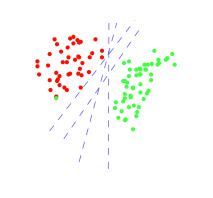

Since the starting point for the classifier is the perceptron, I decided to recast the perceptron in Dr. Wang's framework.

#### Inference

The general formula for inference is

ŷ(x,w)=argmax_(y∈𝒴)w·f(x,y)

For a perceptron, we let 𝒴={-1,1} and then

f(x,y)=y x

If w·x is negative, then -w·x is greatest, so ŷ is chosen to be -1.  If w·x is positive, then w·x is greatest, so ŷ is chosen to be 1.  If w·x is zero, then the result is multivalued.

After lots of simplification, the training becomes

ŵ=argmin_w∑_(i=1)^D sign(w·v_i)

## 17 - 18 Sept 2011

### Vacation

Celebrated my wedding anniversary

## 19 Sept 2011 Monday

### Got e-reader set up to read papers and textbooks

### Read convex analysis

## 20 Sept 2011 Tuesday

### Fixed bug in visualization software

The visualization software crashed when you tried to load spectra from a file.  I spent a good deal of time reading the code to try and understand why the offending code was there.  I added comments as I went.  In the end, I couldn't understand what Paul was trying to do.  I commented out the offending portion of code and the problem was fixed.

### BIRG Lab meeting

Raymer suggested that we have few lab meetings.  Maybe one in which I present on Bayesian statistics and a few progress reports.  But the rest would be proposal-writing sessions.

### Investigate mylims.org

My lims (laboratory information management system) is a site dedicated to managing and sharing spectra used for conventional nmr spectroscopy analyses (structure and dynamics of pure chemicals).  It looked like a competitor to what we want to do.  But it doesn't have the same wide focus.

I looked at documents to figure out when it started (1 October 2009) and I made an account and watched the tutorial videos.  There are some things we'd want to add if we were to try and support the same things they support (starting processing with the FID, display of molecules and proton assignment by dragging from peak to molecule).

### Look at password managers

Needing to sign up for an account at mylims.org made me long to have a working password manager.  I looked at LastPass and PassPack and narrowly decided for PassPack because though its free account has fewer passwords and the paid account is $18/yr vs $12 for LastPass, I can use the free account on the desktop and on mobile and I don't need to install an executable (their method depends on javascript and 3rd party cookies).  It also has a nice (geeky) security emphasis, rating your passwords and things of that ilk.

### Find metadata → spectrum number link for Isaie

I neglected to copy the spectrum metadata (sample ID, subject ID, weight, etc.) to the deconvolved output file in the Targeted Deconvolution software.  Isaie needs it to do his analyses.  He downloaded the spectra directly from the web-site.  So, I needed to find out where the metadata was displayed on the site and how it connected with the spectrum numbers.  Though I am not 100% certain, I think the following procedure will give the metadata:

Log in and go to the collection with the ID you downloaded

Under the actions column in the far right, click "show"

A window will open with the description for each spectrum in each row.The row in the list is spectrum 1; the second is spectrum 2; etc.

I need to double-check by uploading randomly arranged metadata with some small spectra to see what order it is displayed in.

## 21 Sept 2011 - Wednesday

### Verified metadata → spectrum link for Isaie

I made some random metadata, added it to some spectra, and uploaded it to BIRG.  It came out in the order I expected.  So I believe my advice to Isaie was correct.

### Wrestled with HMDB peak-list data

The HMDB peak list data that I downloaded has evidence of disparate editing and no firm file format.

Initially I tried to write code to just read it.  However, there were too many exceptions to care for (typos in field names, mislabeled tables, null characters in text files, missing header information, etc etc).

I started a github project to clean the data for my use.  Afterward, I'll contact the HMDB maintainers to see if they want my modified files.

I removed nulls added a very basic test that all tables have "Table of Peaks" section.

## 22 Sept 2011 - Thursday

Note: from here to 14 October was added on 14 October.  I got behind in my record keeping and have reconstructed things from emails, pieces of scattered paper, git log files, my calendar, my time-tracking app, and other records.

### Cleaned HMDB peak-list data

#### Fixed inconsistent field delimiters

Removed spaces that were adjacent to tabs

Removed double-tabs used to separate fields

#### Created automatic test code searching for errors in peak table

## 23 Sept 2011

### Cleaned HMDB peak-list data

#### Improved automatic parsing of headers

#### Fixed inconsistent naming of headers

#### Fixed some misapplied headers

Some tables had the wrong designation.  For example, some tables that should have been labeled "Table of Assignments" were labeled "Table of Multiplets" and vice-versa.

#### Added automatic tests checking the formatting of headers

Table of peaks headers had to have ppm and no fields.

Table types must be from a list of known types for the HNMR section.

Known table types must have recognizable fields.

#### Fixed and tested for adjacent tabs in headers

#### Manually fixed table-type typos

### Wrote code to extract peak ppms from cleaned peak-list data

### Analyzed HMDB peak locations

The graph below makes clear that out of 897 metabolites, 120 appear in the most crowded bin.  But even the less crowded bins have substantial numbers of metabolites.  This means that trying to do inference in even the smallest of Dr. Reo's targeted bins could lead to large number of metabolites and thus not much savings in terms of time.

```mathematica
Import["/home/eric/Desktop/metabolites_with_peak_in_bin.pdf"]
```

{-Graphics-}

## 24 Sept 2011 - Saturday

### Went to Kno.e.sis picnic

For most people this wouldn't be work, but for me, socializing is a chore.  I met several people's wives (Tian Xia (aka Summer), Pascal Hizler, Amit Sheth) and introduced them to my family.  I participated in the game of charades.  I saw and was seen.

I believe I took the rest of the day off because my sister, mother, and brother were visiting from 3 different states at the same time.

## 25 Sept 2011 - Sunday

I'm not sure if I did any work.  I likely spent some more time with my mother and brother.

## 26 Sept 2011 - Monday

Need to continue from here.  I think Monday is when I discovered the anomaly in the two slopes in the peak-data scatter-plot.

### Explored peak data more

## 14 Oct 2011 - Friday

### Updated lab-book

I spent several hours discovering what I had done since my last entry Sept 21.  I still need to continue documenting tomorrow.

### Added issues to Metabolomics Toolbox Tracker

I plan to break up some composite issues I have sitting around on the tracker after I submit this lab book update.

## 24 Oct 2011 - Monday

I need to go back and fill in the missing days between 14 and 24 Oct as well as the missing days before that

### Added new field to CompoundBin that allows specifying the types of sample in which a compound can be found

This took all day because it involved modifications to the constructor , equality operator, load and save, and the test cases in order to attempt to ensure backwards compatibility as well as add the new feature.

## 25 Oct 2011 - Tuesday

### Read Jaynes on Bayesian Statistics

### Lab Meeting

I need to try and publish what I've done with the Targeted Deconvolution software.

I need to write an email to Doom, Raymer, Paul, Nick Reo describing what I've done, what has been done and what I can do to make it publishable.  Ask Reo why my software is preferable to Chenomix' method.

Presented what I'm doing with Wang.  Doom and Raymer thought it might be the meat of a dissertation.  Doom mentioned that it was a risky dissertation because it either works or it doesn't.

Can add my other contributions to the metabolomics toolbox as an appendix to the dissertation that list other useful contributions I've made to the lab.

### Presentation on RDMA by Gregg ??? from Microsoft

One of the best graduates from here.  He has implemented RDMA  (doing DMA in the NIC to facilitate network-based storage on high-speed networks) in Windows 8.

### Read Functional Metabolomics Manuscript

I read over the functional metabolomics manuscript from Isaie and Reo.  The discussion meeting is tomorrow at 9am.

My impression is that the argument in the paper comes across as very intricate and detailed.  It was hard to follow.

## 26 Oct 2011 - Wednesday

### Add ability to filter on new field to FilterMetabMap

Modified UI and did some  testing.  Fixed bugs.

### Decided to use Waffles

This is probably where I decided that I would use Waffles rather than rolling my own boosting algorithm or using one of the available matlab scripts.

Waffles gives me more options.  It takes care of the IO.  I have commit access, so I can fix bugs instantly and add functionality to take care of exactly the use case I have in mind.

### More things

I forgot to record what I did on 26 Oct anywhere.  So this is being written on 7 Nov. based on the commit record for the metabolomics analysis toolbox.

## 27 Oct 2011 - Thursday

### Finished adding ability to filter on the new field to FilterMetabMap

This fixed issue 101

### Lots of testing of FilterMetabMap

Greatly increased robustness to corner and edge cases (what happens when you click on a list box that hasn't been populated yet).

### Made get button work in FilterMetabMap

This fixed issue 102

## 28 Oct 2011 - Friday

### Researched techniques for doing merging with Subversion

This was about 4 hours of reading. (It seems like it should be simpler).  I decided the investment would be worth it because using waffles to do the machine-learning part of peak-finding would save me LOTS of implementation details.

One downside of using Waffles is that I need to bring my branch up-to-date and then merge it back into the trunk.  This was taking many hours when I left off in March.  So I decided to do it right if I am going to be spending lots of time doing the merging.  An added benefit is that I'll need to do it anyway before mid-November (I promised J. Galagher), so here I get it done early.

### Began doing the actual merge

Lots of time on this.  Because of the antiquated merging facilities, long time-baseline, and previous partial merges there were LOTS of conflicts and there also were several cases where no conflict was discovered that the heuristics get it wrong.  I didn't finish.

## 29 Oct 2011 - Saturday

### Waffles merging

I spent the entire day merging the code (not updating it, just merging the code!)  Lots of conflicts in lots of files (most of which I never touched, but were touched by the previous partial merges; did I mention the antiquated merging facilities).  At least, due to my research yesterday, I'm using kdiff3 rather than just editing the merged text files.

## 30 Oct 2011 - Sunday

### Waffles updating

I finished merging my code.  Then the rest of the day was updating it to take care of the significant architectural changes that took place since March.  Chief among them were changes in the serialization format and supporting API.  The change is for the better (JSON/XML) rather than a home-grown tree format called TWT, but the serialization was a complicated part of the new code.  It was hard to get it right the first time.  It was hard to do it the second.

## 31 Oct 2011 - Monday

### Waffles updating

I finished updating my code so it works with the latest waffles API and tools.

### Waffles merging

I spent a while trying to get my newly up-to-date branch to merge with the trunk.  Not happening.  Due to the bad merge facilities, reintegrating is worse than the first merge.  I can just hear the TV ad now: "Bad merging, but NOW WITH MORE CONFLICTS."

I finally gave up and just exported my (fully updated and merged) branch to another directory, set the working copy to trunk and copied the exported data over the trunk and committed the result.  It lost the history (it looks like I just changed a lot of files all at once) but it works.

### Waffles bug report

I found out that the likely reason for all the merging pain is that the server software and client software are updated but they don't update the repository automatically.  So, the repository was likely way (4 years) out of date.  I sent the head of the waffles project an email for him to update the repo, explaining my problems and conjecture.

## 1 Nov 2011 - Tuesday

### Waffles repository problem fixed

I got the reply from the waffles maintainer.  He took my suggestion and fixed things.  I did some quick tests and it seemed that the upgrade had worked.

### Help Delroy with EM

I spent some time reviewing the EM algorithm in order to give a tutorial to Delroy.  Then, in the afternoon

### Lab meeting

We gave reports on our current progress.

Dr. Raymer suggested that I try to publish the targeted deconvolution work.  I should send out an email to the various users asking what are the reasons they use it above chenomix or other tools.  I should also seek venues for publication

### Began adding new feature to waffles_learn

Boosting is already present, but it uses a stochastic approximation to the example weighting.  I need to add a way of making the parameters to that stochastic approximation accessible to users.

## 2 Nov 2011 - Wednesday

### Finished adding new options to waffles_learn boost

You can now adjust the parameters to the boosting approximation in waffles.

### Code to convert synthetic spectra to training data

I began writing code to convert the synthetic spectra that Paul gave me into training data for standard machine learning algorithms.

The training data will take the spectra and divide it up into fixed-sized neighborhoods around every data point.  There will also be an error estimate for each spectrum appended to the training example.  Data points that cannot have a full window because they are on the edges will be omitted.  Then the number of peaks that are closer to that data point than to any other will be output as the target the classifier must predict.  I will have potential outputs.  One is just the numeric value of the number of peaks.  The second is that numeric value but treated as nominal classes.  The third is a binary classification - has peaks or no peaks.

## 3 Nov 2011 - Thursday

### Finished code to convert synthetic spectra to training data

### Analyzed performance of various algorithms on training data

This is written 21 November after I was able to get the record of my experiments translated out of terminal interaction encoding and into just a text transcript.

In this experiment I used my newly generated training data and plugged it into every algorithm provided by waffles.  I did not exhaust the possibilities of using different sized bags containing different combinations of classifiers.  But I spent a good number of hours and got a good survey of some of the most common classifiers.  The glaring omission is svn (because it is a glaring omission of the waffles toolkit).

I decided to do the binary classification problem because I thought it would be the easiest to evaluate.  This means predicting whether there is at least one peak at a given point.  Only a small fraction of the points had more than one peak.  Most classifiers (except for a few very weak ones) got results in the 70-80% range.  (Ming said, at Dan Wlodarski's wedding, that this was good performance, but I was hoping for performance in the 90% range.)  For all tests, I randomly split the data 70% training and 30% test.  I'll only report the results on the 65 sample wide window (though I did a few trials on the 33 wide window).  The best classifier was a bag of 64 decision trees: 82.5%

Perceptron gave a 77.7% correct. (79.4% on the 33 wide).  Boosted perceptron (with 5 elements) had a score of 79.6%.  Though it scored one of the best performances on the 65-sample window, it was statistically indistinguishable from the normal perceptron due to their large variances and the small sample size.

An interesting result was the surprisingly good performance of a decision stump.  That is, choose one element and put a threshold on it.  This gave performance of 71.4% ± 3.7%.  It might be good to look at what value was chosen and for what threshold.

My guess for the reason behind the good performance of the bag of decision trees is that it is doing something like: if a and b and c are below threshold T and d or e or f is above it, we have a peak.

I wanted to try the experiment with dimensionality reduced and whitened data because of a bug in the waffles arff processing code.  Neural networks do better on such data.  And most algorithms can benefit from equivalently scaled variables.  I expect knn, to benefit significantly just from that.  I'll need to fix the waffles problem, though.

I did not check the confusion matrices for any of the classifiers.

#### Is there a difference between boosted and normal perceptron

Before doing this work, my intuition was that a boosted perceptron would be a very good contender.  The 5-boosted perceptron does, indeed, get one of the top mean scores.  However, the variance in its scores depending on how the sample set was chosen is considerable.  It turns out that its performance (with the data I gathered on the 3rd) is statistically indistinguishable from that of the unboosted perceptron.

There is no evidence of a difference in the mean error rate for the boosted and normal perceptron.  Mathematica's MeanDifferenceTest gives a p-value of 0.5 to reject the hypothesis that their means are equal.

Boost size 5 perceptron raw results

```mathematica
boostedPerceptResults={ 0.75867122618466,0.8133854421104,0.80117244748412,0.78114313629702,0.80703468490474,0.80801172447484,0.78553981436248,0.80850024425989,0.78700537371764,0.81289692232535}
```

{0.758671,0.813385,0.801172,0.781143,0.807035,0.808012,0.78554,0.8085,0.787005,0.812897}

Non-boosted results

```mathematica
perceptronResults={0.75867122618466,0.8133854421104,0.80117244748412,0.78114313629702,0.80703468490474,0.80801172447484,0.78553981436248,0.80850024425989,0.78700537371764,0.81289692232535}
```

{0.758671,0.813385,0.801172,0.781143,0.807035,0.808012,0.78554,0.8085,0.787005,0.812897}

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
MeanDifferenceTest[boostedPerceptResults,perceptronResults,0]
```

OneSidedPValue→0.5

#### Is there a difference between 5-boosted perceptron and 64-bagged decision tree

In contrast to boosting the perceptron, the 64 decision tree bag produces significantly better results.  The difference's being clear is mainly due to the low variance of the result quality for the bagged decision tree.

```mathematica
baggedDecisionTreeResults={0.82999511480215,0.83194919394235,0.82266731802638,0.82462139716658,0.82608695652174,0.82169027845628,0.8114313629702,0.83341475329751,0.81924767953102,0.82413287738154}
```

{0.829995,0.831949,0.822667,0.824621,0.826087,0.82169,0.811431,0.833415,0.819248,0.824133}

```mathematica
boostedPerceptResults={ 0.75867122618466,0.8133854421104,0.80117244748412,0.78114313629702,0.80703468490474,0.80801172447484,0.78553981436248,0.80850024425989,0.78700537371764,0.81289692232535}
```

{0.758671,0.813385,0.801172,0.781143,0.807035,0.808012,0.78554,0.8085,0.787005,0.812897}

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
MeanDifferenceTest[boostedPerceptResults,baggedDecisionTreeResults,0]
```

OneSidedPValue→0.000291727

#### Summary table of results

Not included in the table are a bma combination of a naive instance and a decision tree which took a long time to train and was giving results in the 50% range.

##### Results in Mathematica readable format

The code below can be copied to get a Mathematica  form of the results.

```mathematica
InputForm[results]
```

{{"Algorithm", "Window Width", "Reps", "Test Set Frac. Correct", "Std. Dev", "Original Order"}, 
 {"Perceptron (sigmoid)", 33, 10, 0.7910600879, 0.02006443, 2}, {"Perceptron (sigmoid)", 65, 10, 0.7770884221, 
  0.0280056746, 3}, {"Boost 5 Perceptron (sigmoid)", 33, 10, 0.7942843185, 0.0214150913, 4}, 
 {"Boost 5 Perceptron (sigmoid)", 65, 10, 0.7963361016, 0.0177644107, 5}, 
 {"Boost 25 Perceptron (sigmoid)", 33, 10, 0.7888617489, 0.0249616136, 6}, 
 {"Boost 25 Perceptron (sigmoid)", 65, 10, 0.7833903273, 0.0192718837, 7}, 
 {"Majority Classifier", 65, 10, 0.4921348315, 0.006045727, 8}, {"Bag 64 Random Decision Tree", 65, 10, 0.7875427455, 
  0.0054177018, 9}, {"Bag 64 Decision Tree", 65, 10, 0.8245236932, 0.0064760356, 10}, 
 {"Decision Tree", 65, 10, 0.7594040059, 0.0063287985, 11}, {"KNN (1)", 65, 10, 0.7297997069, 0.006129577, 12}, 
 {"KNN (3)", 65, 10, 0.7489985344, 0.0080463359, 13}, {"KNN (5)", 65, 10, 0.7537860283, 0.005560453, 14}, 
 {"KNN (7)", 65, 10, 0.7644846116, 0.0087098814, 15}, {"KNN (11)", 65, 10, 0.7747923791, 0.0053116777, 16}, 
 {"Naive Instance (11)", 65, 10, 0.7289692233, 0.0042200369, 17}, {"Naive Instance (5)", 65, 10, 0.7675134343, 
  0.0066881433, 18}, {"Naive Instance (4)", 65, 10, 0.770346849, 0.0068835271, 19}, 
 {"Naive Instance (3)", 65, 10, 0.7686370298, 0.0109459445, 20}, {"Naive Instance (5)", 65, 20, 0.7706888129, 
  0.0080870626, 21}, {"Naive Instance (3)", 65, 20, 0.7718612604, 0.0065771376, 22}, 
 {"Naive Instance (1)", 65, 20, 0.7715925745, 0.0065320565, 23}, {"Bag 16 Naive Instance (1)", 65, 10, 0.7729360039, 
  0.0119945729, 24}, {"Bag 1 Naive Instance (1) and 1 Decision Tree", 65, 10, 0.7577430386, 0.0077974655, 25}, 
 {"Decision Tree (2 levels = stump)", 65, 10, 0.7146555936, 0.0372746607, 26}, 
 {"Decision Tree (3 levels)", 65, 10, 0.7752320469, 0.0201638313, 27}, 
 {"Decision Tree", 65, 10, 0.7587200782, 0.0088368235, 28}, {"Boost 30? Decision stump", 65, 10, 0.7498290181, 
  0.0346940394, 29}, {"Boost 60 Decision stump", 65, 10, 0.7673668784, 0.0283816495, 30}, 
 {"Boost 120 Decision stump", 65, 10, 0.7457254519, 0.0321824189, 31}, 
 {"Boost 90 Decision stump", 65, 10, 0.7621885686, 0.0287907256, 32}, 
 {"Boost 75 Decision stump", 65, 10, 0.7417684416, 0.032724911, 33}, {"Boost 75 Decision stump", 65, 10, 0.756765999, 
  0.022331583, 34}, {"Boost 75 Decision stump (resample ratio=2)", 65, 10, 0.7618466048, 0.0197704707, 35}, 
 {"Boost 75 Decision stump (resample ratio=3)", 65, 10, 0.7558866634, 0.0442367786, 36}, 
 {"Boost 65 Decision stump (resample ratio=3)", 65, 10, 0.7543722521, 0.0317915925, 37}, 
 {"Boost 65 Decision stump (resample ratio=2)", 65, 10, 0.7413776258, 0.0275302559, 38}, 
 {"Graph cut transducer", 65, 10, 0.7826575476, 0.0130890285, 39}, {"Mean margins tree", 65, 10, 0.5245725452, 
  0.0724872938, 40}, {"Bag 32 Mean margins tree", 65, 10, 0.7821201759, 0.0051545976, 41}, 
 {"Bag 64 Mean margins tree", 65, 10, 0.7874450415, 0.0038428153, 42}, 
 {"Bag 128 Mean margins tree", 65, 10, 0.7872984856, 0.0077727713, 43}, 
 {"Random forest 64 trees", 65, 10, 0.7887640449, 0.0063369635, 44}, {"Naive Bayes", 65, 10, 0.6992183683, 
  0.0046633102, 45}, {"Linear regression", 65, 10, 0.6807523205, 0.0204015101, 46}, 
 {"Agglomerative transducer", 65, 10, 0.7242794333, 0.0121862596, 47}, 
 {"Neighbor transducer", 65, 10, 0.7737176356, 0.0077714066, 48}}

##### Results in table format

```mathematica
TableForm[results]
```

Algorithm | Window Width | Reps | Test Set Frac. Correct | Std. Dev | Original Order
Perceptron (sigmoid) | 33 | 10 | 0.79106 | 0.0200644 | 2
Perceptron (sigmoid) | 65 | 10 | 0.777088 | 0.0280057 | 3
Boost 5 Perceptron (sigmoid) | 33 | 10 | 0.794284 | 0.0214151 | 4
Boost 5 Perceptron (sigmoid) | 65 | 10 | 0.796336 | 0.0177644 | 5
Boost 25 Perceptron (sigmoid) | 33 | 10 | 0.788862 | 0.0249616 | 6
Boost 25 Perceptron (sigmoid) | 65 | 10 | 0.78339 | 0.0192719 | 7
Majority Classifier | 65 | 10 | 0.492135 | 0.00604573 | 8
Bag 64 Random Decision Tree | 65 | 10 | 0.787543 | 0.0054177 | 9
Bag 64 Decision Tree | 65 | 10 | 0.824524 | 0.00647604 | 10
Decision Tree | 65 | 10 | 0.759404 | 0.0063288 | 11
KNN (1) | 65 | 10 | 0.7298 | 0.00612958 | 12
KNN (3) | 65 | 10 | 0.748999 | 0.00804634 | 13
KNN (5) | 65 | 10 | 0.753786 | 0.00556045 | 14
KNN (7) | 65 | 10 | 0.764485 | 0.00870988 | 15
KNN (11) | 65 | 10 | 0.774792 | 0.00531168 | 16
Naive Instance (11) | 65 | 10 | 0.728969 | 0.00422004 | 17
Naive Instance (5) | 65 | 10 | 0.767513 | 0.00668814 | 18
Naive Instance (4) | 65 | 10 | 0.770347 | 0.00688353 | 19
Naive Instance (3) | 65 | 10 | 0.768637 | 0.0109459 | 20
Naive Instance (5) | 65 | 20 | 0.770689 | 0.00808706 | 21
Naive Instance (3) | 65 | 20 | 0.771861 | 0.00657714 | 22
Naive Instance (1) | 65 | 20 | 0.771593 | 0.00653206 | 23
Bag 16 Naive Instance (1) | 65 | 10 | 0.772936 | 0.0119946 | 24
Bag 1 Naive Instance (1) and 1 Decision Tree | 65 | 10 | 0.757743 | 0.00779747 | 25
Decision Tree (2 levels = stump) | 65 | 10 | 0.714656 | 0.0372747 | 26
Decision Tree (3 levels) | 65 | 10 | 0.775232 | 0.0201638 | 27
Decision Tree | 65 | 10 | 0.75872 | 0.00883682 | 28
Boost 30? Decision stump | 65 | 10 | 0.749829 | 0.034694 | 29
Boost 60 Decision stump | 65 | 10 | 0.767367 | 0.0283816 | 30
Boost 120 Decision stump | 65 | 10 | 0.745725 | 0.0321824 | 31
Boost 90 Decision stump | 65 | 10 | 0.762189 | 0.0287907 | 32
Boost 75 Decision stump | 65 | 10 | 0.741768 | 0.0327249 | 33
Boost 75 Decision stump | 65 | 10 | 0.756766 | 0.0223316 | 34
Boost 75 Decision stump (resample ratio=2) | 65 | 10 | 0.761847 | 0.0197705 | 35
Boost 75 Decision stump (resample ratio=3) | 65 | 10 | 0.755887 | 0.0442368 | 36
Boost 65 Decision stump (resample ratio=3) | 65 | 10 | 0.754372 | 0.0317916 | 37
Boost 65 Decision stump (resample ratio=2) | 65 | 10 | 0.741378 | 0.0275303 | 38
Graph cut transducer | 65 | 10 | 0.782658 | 0.013089 | 39
Mean margins tree | 65 | 10 | 0.524573 | 0.0724873 | 40
Bag 32 Mean margins tree | 65 | 10 | 0.78212 | 0.0051546 | 41
Bag 64 Mean margins tree | 65 | 10 | 0.787445 | 0.00384282 | 42
Bag 128 Mean margins tree | 65 | 10 | 0.787298 | 0.00777277 | 43
Random forest 64 trees | 65 | 10 | 0.788764 | 0.00633696 | 44
Naive Bayes | 65 | 10 | 0.699218 | 0.00466331 | 45
Linear regression | 65 | 10 | 0.680752 | 0.0204015 | 46
Agglomerative transducer | 65 | 10 | 0.724279 | 0.0121863 | 47
Neighbor transducer | 65 | 10 | 0.773718 | 0.00777141 | 48

#### Transcript of analysis session

Script started on Thu 03 Nov 2011 02:20:51 PM EDT
To run a command as administrator (user "root"), use "sudo <command>".
See "man sudo_root" for details.

protein:...ta-Sets/Synthetic Data Sets/6$ ls -l *.arff
-rw-r--r-- 1 eric bioinf 2304095 2011-11-03 14:06 foo33.arff
-rw-r--r-- 1 eric bioinf 4373673 2011-11-03 13:47 foo65.arff
-rw-r--r-- 1 eric bioinf 1139290 2011-11-03 13:41 foo.arff
protein:...ta-Sets/Synthetic Data Sets/6$ ls -lh *.arff
-rw-r--r-- 1 eric bioinf 2.2M 2011-11-03 14:06 foo33.arff
-rw-r--r-- 1 eric bioinf 4.2M 2011-11-03 13:47 foo65.arff
-rw-r--r-- 1 eric bioinf 1.1M 2011-11-03 13:41 foo.arff
protein:...ta-Sets/Synthetic Data Sets/6$ rm foo.arff
protein:...ta-Sets/Synthetic Data Sets/6$ mkdir ~/ANN_Data
protein:...ta-Sets/Synthetic Data Sets/6$ rmdir ~/ANN_Data/
protein:...ta-Sets/Synthetic Data Sets/6$ mkdir ~/PkFindData
protein:...ta-Sets/Synthetic Data Sets/6$ mv foo33.arff ~/PkFindData/two_spectra
_window_33.arff
protein:...ta-Sets/Synthetic Data Sets/6$ mv foo65.arff ~/PkFindData/two_spectra
_window_65.arff
protein:...ta-Sets/Synthetic Data Sets/6$ pushd ~/PkFindData/
~/PkFindData ~/Dropbox/NMR-Training-and-Testing-Data-Sets/Synthetic Data Sets/6
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 Er
ror:_Unexpected_token,_0,34,35,_in_arg_8^Cignore 0,34,35 -labels 36 neuralnet
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 fo
o33.arff -ignore 0,34,35 -labels 36 neuralnet
_________________________________
File not found: foo33.arff

Brief Usage Information:

waffles_learn splittest <options> [dataset] <data_opts> [algorithm]
   This shuffles the data, then splits it into two parts, trains with one part,
   and tests with the other. (This also works with model-free algorithms.)
   Results are printed to stdout for each dimension in the label vector.
   Predictive accuracy is reported for nominal labels, and mean-squared-error
   is reported for continuous labels.
   <options>
      -seed [value]
         Specify a seed for the random number generator. (Use this option to
         ensure that your results are reproduceable.)
      -trainratio [value]
         Specify the amount of the data (between 0 and 1) to use for training.
         The rest will be used for testing.
      -reps [value]
         Specify the number of repetitions to perform. If not specified, the
         default is 1.
      -writelastmodel [filename]
         Write the model generated on the last repetion to the given filename. 
         Note that this only works when the learner being used has an internal
         model.
      -confusion
         Print a confusion matrix for each nominal label attribute after each
         repetition.
      -stddev
         Print the standard deviation of the results at the end as well as
         their mean.
   [dataset]
      The filename of a dataset.
   <data_opts>
      -labels [attr_list]
         Specify which attributes to use as labels. (If not specified, the
         default is to use the last attribute for the label.) [attr_list] is a
         comma-separated list of zero-indexed columns. A hypen may be used to
         specify a range of columns.  A '*' preceding a value means to index
         from the right instead of the left. For example, "0,2-5" refers to
         columns 0, 2, 3, 4, and 5. "*0" refers to the last column. "0-*1"
         refers to all but the last column.
      -ignore [attr_list]
         Specify attributes to ignore. [attr_list] is a comma-separated list of
         zero-indexed columns. A hypen may be used to specify a range of
         columns.  A '*' preceding a value means to index from the right
         instead of the left. For example, "0,2-5" refers to columns 0, 2, 3,
         4, and 5. "*0" refers to the last column. "0-*1" refers to all but the
         last column.
   [algorithm]
      agglomerativetransducer
      bag <contents> end
      baseline
      bucket <contents> end
      bma <contents> end
      bmc <options> <contents> end
      boost <options> [algorithm]
      cvdt [n]
      decisiontree <options>
      graphcuttransducer <options>
      knn <options>
      linear
      meanmarginstree
      naivebayes <options>
      naiveinstance <options>
      neighbortransducer <options>
      neuralnet <options>
      randomforest [trees] <options>
      usage

To see full usage information, run:
waffles_learn usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7^Ci
gnore 0,34,35 -labels 36 neuralnet
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_33.arff -ignore 0,34,35 -labels 36 neuralnet
rep 0) 0.80801172447484
rep 1) 0.80263800683928
rep 2) 0.79872984855887
rep 3) 0.7923790913532
rep 4) 0.74450415241817
rep 5) 0.79628724963361
rep 6) 0.78456277479238
rep 7) 0.7923790913532
rep 8) 0.81631656082071
rep 9) 0.77479237909135
-----Mean-----
0.79106008793356
-----Standard Deviation-----
0.020064429993251
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 neuralnet
rep 0) 0.81289692232536
rep 1) 0.74987787005374
rep 2) 0.78407425500733
rep 3) 0.74401563263312
rep 4) 0.80019540791402
rep 5) 0.78602833414753
rep 6) 0.76355642403517
rep 7) 0.81533952125061
rep 8) 0.73668783585735
rep 9) 0.77821201758671
-----Mean-----
0.7770884220811
-----Standard Deviation-----
0.028005674642892
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_33.arff -ignore 0,34,35 -labels 36 boost -size 5 neuralnet
rep 0) 0.76160234489497
rep 1) 0.79628724963361
rep 2) 0.75720566682951
rep 3) 0.80703468490474
rep 4) 0.81436248168051
rep 5) 0.79970688812897
rep 6) 0.80410356619443
rep 7) 0.82462139716659
rep 8) 0.78651685393258
rep 9) 0.7914020517831
-----Mean-----
0.7942843185149
-----Standard Deviation-----
0.021415091297773
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 5 neuralnet
rep 0) 0.75867122618466
rep 1) 0.8133854421104
rep 2) 0.80117244748412
rep 3) 0.78114313629702
rep 4) 0.80703468490474
rep 5) 0.80801172447484
rep 6) 0.78553981436248
rep 7) 0.80850024425989
rep 8) 0.78700537371764
rep 9) 0.81289692232535
-----Mean-----
0.79633610161212
-----Standard Deviation-----
0.017764410716757
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_33.arff -ignore 0,34,35 -labels 36 boost -size 25 neuralnet
rep 0) 0.75671714704446
rep 1) 0.76648754274548
rep 2) 0.8124084025403
rep 3) 0.77186126038105
rep 4) 0.79775280898876
rep 5) 0.80410356619443
rep 6) 0.81582804103566
rep 7) 0.7933561309233
rep 8) 0.81778212017587
rep 9) 0.75232046897899
-----Mean-----
0.78886174890083
-----Standard Deviation-----
0.024961613585867
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 25 neuralnet
rep 0) 0.80508060576453
rep 1) 0.79579872984856
rep 2) 0.80312652662433
rep 3) 0.77381533952125
rep 4) 0.78065461651197
rep 5) 0.7542745481192
rep 6) 0.78553981436248
rep 7) 0.75476306790425
rep 8) 0.80556912554959
rep 9) 0.7752808988764
-----Mean-----
0.78339032730826
-----Standard Deviation-----
0.019271883652174
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 baseline
rep 0) 0.49340498290181
rep 1) 0.48851978505129
rep 2) 0.48705422569614
rep 3) 0.49682462139717
rep 4) 0.48900830483635
rep 5) 0.49731314118222
rep 6) 0.47923790913532
rep 7) 0.49584758182706
rep 8) 0.49780166096727
rep 9) 0.49633610161211
-----Mean-----
0.49213483146067
-----Standard Deviation-----
0.0060457270347179
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bucket bag 64 decisiontree e
nd bag 64 decisiontree -random 1 end bag 64 meanmarginstree end end
^C
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 decisiontree end
^C
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 decisiontree -random 
1 end
rep 0) 0.78944797264289
rep 1) 0.78944797264289
rep 2) 0.79189057156815
rep 3) 0.79531021006351
rep 4) 0.78944797264289
rep 5) 0.7914020517831
rep 6) 0.78163165608207
rep 7) 0.78602833414753
rep 8) 0.77723497801661
rep 9) 0.78358573522228
-----Mean-----
0.78754274548119
-----Standard Deviation-----
0.0054177017916568
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 decisiontree end
rep 0) 0.82999511480215
rep 1) 0.83194919394235
rep 2) 0.82266731802638
rep 3) 0.82462139716658
rep 4) 0.82608695652174
rep 5) 0.82169027845628
rep 6) 0.8114313629702
rep 7) 0.83341475329751
rep 8) 0.81924767953102
rep 9) 0.82413287738154
-----Mean-----
0.82452369320957
-----Standard Deviation-----
0.0064760356489596
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree
rep 0) 0.76404494382023
rep 1) 0.76355642403517
rep 2) 0.75915974596971
rep 3) 0.74841231069858
rep 4) 0.75671714704446
rep 5) 0.76453346360528
rep 6) 0.76990718124084
rep 7) 0.75574010747435
rep 8) 0.75915974596971
rep 9) 0.75280898876404
-----Mean-----
0.75940400586224
-----Standard Deviation-----
0.0063287984832469
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 knn 1
_________________________________
Superfluous argument: 1

Brief Usage Information:

waffles_learn splittest <options> [dataset] <data_opts> [algorithm]
   This shuffles the data, then splits it into two parts, trains with one part,
   and tests with the other. (This also works with model-free algorithms.)
   Results are printed to stdout for each dimension in the label vector.
   Predictive accuracy is reported for nominal labels, and mean-squared-error
   is reported for continuous labels.
   <options>
      -seed [value]
         Specify a seed for the random number generator. (Use this option to
         ensure that your results are reproduceable.)
      -trainratio [value]
         Specify the amount of the data (between 0 and 1) to use for training.
         The rest will be used for testing.
      -reps [value]
         Specify the number of repetitions to perform. If not specified, the
         default is 1.
      -writelastmodel [filename]
         Write the model generated on the last repetion to the given filename. 
         Note that this only works when the learner being used has an internal
         model.
      -confusion
         Print a confusion matrix for each nominal label attribute after each
         repetition.
      -stddev
         Print the standard deviation of the results at the end as well as
         their mean.
   [dataset]
      The filename of a dataset.
   <data_opts>
      -labels [attr_list]
         Specify which attributes to use as labels. (If not specified, the
         default is to use the last attribute for the label.) [attr_list] is a
         comma-separated list of zero-indexed columns. A hypen may be used to
         specify a range of columns.  A '*' preceding a value means to index
         from the right instead of the left. For example, "0,2-5" refers to
         columns 0, 2, 3, 4, and 5. "*0" refers to the last column. "0-*1"
         refers to all but the last column.
      -ignore [attr_list]
         Specify attributes to ignore. [attr_list] is a comma-separated list of
         zero-indexed columns. A hypen may be used to specify a range of
         columns.  A '*' preceding a value means to index from the right
         instead of the left. For example, "0,2-5" refers to columns 0, 2, 3,
         4, and 5. "*0" refers to the last column. "0-*1" refers to all but the
         last column.
   [algorithm]
      agglomerativetransducer
      bag <contents> end
      baseline
      bucket <contents> end
      bma <contents> end
      bmc <options> <contents> end
      boost <options> [algorithm]
      cvdt [n]
      decisiontree <options>
      graphcuttransducer <options>
      knn <options>
      linear
      meanmarginstree
      naivebayes <options>
      naiveinstance <options>
      neighbortransducer <options>
      neuralnet <options>
      randomforest [trees] <options>
      usage

To see full usage information, run:
waffles_learn usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 knn -neighbors 1
rep 0) 0.73082559843674
rep 1) 0.72447484123107
rep 2) 0.72105520273571
rep 3) 0.72203224230581
rep 4) 0.7352222765022
rep 5) 0.72691744015633
rep 6) 0.73766487542745
rep 7) 0.73033707865169
rep 8) 0.73131411822179
rep 9) 0.73815339521251
-----Mean-----
0.72979970688813
-----Standard Deviation-----
0.006129576967909
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 knn -scalefeatures -neighbor
s 1
^C
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 knn -neighbors 3
rep 0) 0.76209086468002
rep 1) 0.74206155349292
rep 2) 0.74352711284807
rep 3) 0.74499267220322
rep 4) 0.75183194919394
rep 5) 0.73473375671715
rep 6) 0.74743527112848
rep 7) 0.75574010747435
rep 8) 0.7562286272594
rep 9) 0.75134342940889
-----Mean-----
0.74899853444065
-----Standard Deviation-----
0.0080463359409514
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 knn -neighbors 5
rep 0) 0.75818270639961
rep 1) 0.75671714704445
rep 2) 0.75036638983879
rep 3) 0.75818270639961
rep 4) 0.75134342940889
rep 5) 0.74206155349292
rep 6) 0.75818270639961
rep 7) 0.74987787005374
rep 8) 0.76013678553981
rep 9) 0.75280898876404
-----Mean-----
0.75378602833415
-----Standard Deviation-----
0.0055604530463972
protein:~/PkFindData$ ^C
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 knn -neighbors 7
rep 0) 0.76893014167074
rep 1) 0.7532975085491
rep 2) 0.76355642403517
rep 3) 0.75818270639961
rep 4) 0.76209086468002
rep 5) 0.76502198339033
rep 6) 0.76893014167074
rep 7) 0.7562286272594
rep 8) 0.76404494382022
rep 9) 0.78456277479238
-----Mean-----
0.76448461162677
-----Standard Deviation-----
0.0087098814019727
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 knn -neighbors 11
rep 0) 0.77967757694187
rep 1) 0.77137274059599
rep 2) 0.77381533952125
rep 3) 0.77381533952125
rep 4) 0.77039570102589
rep 5) 0.77772349780166
rep 6) 0.76453346360527
rep 7) 0.77625793844651
rep 8) 0.78358573522228
rep 9) 0.77674645823156
-----Mean-----
0.77479237909135
-----Standard Deviation-----
0.0053116777170823
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naiveinstance -neighbors 11
rep 0) 0.73180263800684
rep 1) 0.72887151929653
rep 2) 0.72252076209086
rep 3) 0.7352222765022
rep 4) 0.72740595994138
rep 5) 0.73375671714705
rep 6) 0.72984855886663
rep 7) 0.73082559843674
rep 8) 0.72300928187591
rep 9) 0.72642892037128
-----Mean-----
0.72896922325354
-----Standard Deviation-----
0.004220036879613
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naiveinstance -neighbors 5
rep 0) 0.77479237909135
rep 1) 0.77088422081094
rep 2) 0.7723497801661
rep 3) 0.77186126038105
rep 4) 0.75280898876404
rep 5) 0.76795310210063
rep 6) 0.77186126038105
rep 7) 0.76746458231558
rep 8) 0.76013678553981
rep 9) 0.76502198339033
-----Mean-----
0.76751343429409
-----Standard Deviation-----
0.0066881433310843
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naiveinstance -neighbors 4
rep 0) 0.77186126038105
rep 1) 0.78260869565217
rep 2) 0.76697606253053
rep 3) 0.76306790425012
rep 4) 0.76551050317538
rep 5) 0.76257938446507
rep 6) 0.77870053737177
rep 7) 0.77674645823156
rep 8) 0.76697606253053
rep 9) 0.76844162188569
-----Mean-----
0.77034684904739
-----Standard Deviation-----
0.0068835271077874
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naiveinstance -neighbors 3
rep 0) 0.77723497801661
rep 1) 0.77381533952125
rep 2) 0.76990718124084
rep 3) 0.77479237909135
rep 4) 0.76844162188569
rep 5) 0.75280898876405
rep 6) 0.77772349780166
rep 7) 0.74499267220323
rep 8) 0.7723497801661
rep 9) 0.7743038593063
-----Mean-----
0.76863702979971
-----Standard Deviation-----
0.010945944458609
protein:~/PkFindData$ waffles_learn splittest -reps 20 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naiveinstance -neighbors 5
rep 0) 0.76111382510992
rep 1) 0.77772349780166
rep 2) 0.76599902296043
rep 3) 0.77088422081094
rep 4) 0.76355642403517
rep 5) 0.77967757694187
rep 6) 0.77674645823156
rep 7) 0.78700537371764
rep 8) 0.75964826575476
rep 9) 0.77870053737176
rep 10) 0.76941866145579
rep 11) 0.76453346360528
rep 12) 0.76697606253053
rep 13) 0.77186126038104
rep 14) 0.75818270639961
rep 15) 0.77088422081094
rep 16) 0.76795310210064
rep 17) 0.76453346360528
rep 18) 0.78456277479238
rep 19) 0.77381533952125
-----Mean-----
0.77068881289692
-----Standard Deviation-----
0.0080870626010631
protein:~/PkFindData$ waffles_learn splittest -reps 20 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naiveinstance -neighbors 3
rep 0) 0.76355642403517
rep 1) 0.77283829995115
rep 2) 0.77870053737176
rep 3) 0.7743038593063
rep 4) 0.76746458231558
rep 5) 0.78407425500733
rep 6) 0.77039570102589
rep 7) 0.76111382510992
rep 8) 0.76502198339033
rep 9) 0.77576941866146
rep 10) 0.77918905715682
rep 11) 0.76257938446507
rep 12) 0.77039570102589
rep 13) 0.76697606253053
rep 14) 0.77283829995115
rep 15) 0.78114313629702
rep 16) 0.76746458231558
rep 17) 0.78016609672692
rep 18) 0.76941866145579
rep 19) 0.77381533952125
-----Mean-----
0.77186126038105
-----Standard Deviation-----
0.0065771376066979
protein:~/PkFindData$ waffles_learn splittest -reps 20 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naiveinstance -neighbors 1
rep 0) 0.76697606253053
rep 1) 0.76160234489497
rep 2) 0.77137274059599
rep 3) 0.77088422081094
rep 4) 0.76893014167074
rep 5) 0.77479237909135
rep 6) 0.75867122618466
rep 7) 0.76746458231558
rep 8) 0.77625793844651
rep 9) 0.77381533952125
rep 10) 0.76257938446507
rep 11) 0.7723497801661
rep 12) 0.76941866145579
rep 13) 0.77283829995115
rep 14) 0.78407425500733
rep 15) 0.78163165608207
rep 16) 0.77088422081094
rep 17) 0.78163165608207
rep 18) 0.77039570102589
rep 19) 0.7752808988764
-----Mean-----
0.77159257449927
-----Standard Deviation-----
0.0065320565230829
protein:~/PkFindData$ waffles_learn splittest -reps 20 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 naiveinstance -neighb
ors 1 end
^C^C
protein:~/PkFindData$ ^C
protein:~/PkFindData$ waffles_learn splittest -reps 20 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 5 naiveinstance -neighbo
rs 1 end
rep 0) 0.75964826575476
rep 1) 0.76893014167074
rep 2) 0.77137274059599
rep 3) 0.76990718124084
rep 4) 0.76160234489497
rep 5) 0.7733268197362
rep 6) 0.75280898876405
rep 7) 0.77967757694187
rep 8) 0.77283829995115
rep 9) 0.76404494382022
rep 10) 0.76844162188569
^C
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 naiveinstance -neighb
ors 1 end
rep 0) 0.7933561309233
rep 1) 0.78456277479238
rep 2) 0.77039570102589
rep 3) 0.78407425500733
rep 4) 0.76844162188569
rep 5) 0.76697606253053
rep 6) 0.7723497801661
rep 7) 0.7743038593063
rep 8) 0.76355642403517
rep 9) 0.75134342940889
-----Mean-----
0.77293600390816
-----Standard Deviation-----
0.011994572914195
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 1 naiveinstance -neighbo
rs 1 1 decisiontree end
rep 0) 0.74938935026869
rep 1) 0.76648754274548
rep 2) 0.75964826575476
rep 3) 0.76404494382023
rep 4) 0.77137274059599
rep 5) 0.76062530532487
rep 6) 0.75232046897899
rep 7) 0.75232046897899
rep 8) 0.75183194919394
rep 9) 0.74938935026869
-----Mean-----
0.75774303859306
-----Standard Deviation-----
0.0077974654619185
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bma 1 naiveinstance -neighbo
rs 1 2 decisiontree end
rep 0) 0.49829018075232
rep 1) 0.50903761602345
rep 2) 0.51148021494871
rep 3) 0.49535906204201
rep 4) 0.50659501709819
rep 5) 0.50464093795799
rep 6) 0.49242794333171
rep 7) 0.49682462139717
^C
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree -maxlevels 2
rep 0) 0.70493404982902
rep 1) 0.70591108939912
rep 2) 0.69956033219345
rep 3) 0.75818270639961
rep 4) 0.70884220810943
rep 5) 0.71910112359551
rep 6) 0.77039570102589
rep 7) 0.75134342940889
rep 8) 0.68148510014656
rep 9) 0.64680019540791
-----Mean-----
0.71465559355154
-----Standard Deviation-----
0.037274660729295
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree -maxlevels 3
rep 0) 0.77528089887641
rep 1) 0.73571079628725
rep 2) 0.77283829995115
rep 3) 0.79628724963361
rep 4) 0.79286761113825
rep 5) 0.76990718124084
rep 6) 0.79091353199805
rep 7) 0.78700537371764
rep 8) 0.78505129457743
rep 9) 0.74645823155838
-----Mean-----
0.7752320468979
-----Standard Deviation-----
0.020163831252212
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree
rep 0) 0.77576941866146
rep 1) 0.75232046897899
rep 2) 0.75378602833415
rep 3) 0.75769418661456
rep 4) 0.7552515876893
rep 5) 0.74499267220323
rep 6) 0.76746458231558
rep 7) 0.76648754274548
rep 8) 0.7562286272594
rep 9) 0.75720566682951
-----Mean-----
0.75872007816317
-----Standard Deviation-----
0.0088368234556716
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree -maxlevels 1
rep 0) 0.49438202247191
rep 1) 0.49242794333171
rep 2) 0.49438202247191
rep 3) 0.49780166096727
rep 4) 0.49780166096727
rep 5) 0.49535906204201
rep 6) 0.49633610161212
rep 7) 0.49096238397655
rep 8) 0.4924279433317
rep 9) 0.48607718612604
-----Mean-----
0.49379579872985
-----Standard Deviation-----
0.0035437799729649
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost decisiontree -maxlevel
s 2
rep 0) 0.67708842208109
rep 1) 0.79384465070835
rep 2) 0.74499267220323
rep 3) 0.77186126038105
rep 4) 0.75769418661456
rep 5) 0.74010747435271
rep 6) 0.78212017586712
rep 7) 0.71910112359551
rep 8) 0.77674645823156
rep 9) 0.73473375671715
-----Mean-----
0.74982901807523
-----Standard Deviation-----
0.034694039390921
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 60 decisiontree 
-maxlevels 2
rep 0) 0.77821201758671
rep 1) 0.74841231069858
rep 2) 0.79286761113825
rep 3) 0.78651685393258
rep 4) 0.72691744015633
rep 5) 0.78944797264289
rep 6) 0.78114313629702
rep 7) 0.71128480703469
rep 8) 0.77772349780166
rep 9) 0.78114313629702
-----Mean-----
0.76736687835857
-----Standard Deviation-----
0.028381649486852
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 120 decisiontree
 -maxlevels 2
rep 0) 0.72789447972643
rep 1) 0.77088422081094
rep 2) 0.77186126038105
rep 3) 0.71226184660479
rep 4) 0.72300928187592
rep 5) 0.77870053737176
rep 6) 0.78212017586712
rep 7) 0.73766487542745
rep 8) 0.76404494382022
rep 9) 0.68881289692233
-----Mean-----
0.7457254518808
-----Standard Deviation-----
0.032182418858971
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 90 decisiontree 
-maxlevels 2
rep 0) 0.78114313629702
rep 1) 0.74938935026869
rep 2) 0.78456277479238
rep 3) 0.78553981436248
rep 4) 0.79775280898876
rep 5) 0.74890083048363
rep 6) 0.73082559843674
rep 7) 0.76062530532487
rep 8) 0.77772349780166
rep 9) 0.70542256961407
-----Mean-----
0.76218856863703
-----Standard Deviation-----
0.028790725632961
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 75 decisiontree 
-maxlevels 2
rep 0) 0.77088422081094
rep 1) 0.7151929653151
rep 2) 0.78407425500733
rep 3) 0.71372740595994
rep 4) 0.70933072789448
rep 5) 0.74206155349292
rep 6) 0.70151441133366
rep 7) 0.73033707865168
rep 8) 0.76013678553982
rep 9) 0.79042501221299
-----Mean-----
0.74176844162189
-----Standard Deviation-----
0.032724910977087
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 75 decisiontree 
-maxlevels 2
rep 0) 0.7743038593063
rep 1) 0.7361993160723
rep 2) 0.74792379091353
rep 3) 0.76746458231558
rep 4) 0.78505129457743
rep 5) 0.74645823155838
rep 6) 0.71372740595994
rep 7) 0.76795310210063
rep 8) 0.74743527112848
rep 9) 0.78114313629702
-----Mean-----
0.75676599902296
-----Standard Deviation-----
0.022331583033831
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -trainratio 2 -size 75
 decisiontree -maxlevels 2
rep 0) 0.76404494382022
rep 1) 0.75915974596971
rep 2) 0.76257938446507
rep 3) 0.77283829995115
rep 4) 0.74841231069858
rep 5) 0.80459208597948
rep 6) 0.76111382510992
rep 7) 0.77186126038105
rep 8) 0.73277967757694
rep 9) 0.74108451392281
-----Mean-----
0.76184660478749
-----Standard Deviation-----
0.019770470743252
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -trainratio 3 -size 75
 decisiontree -maxlevels 2
rep 0) 0.75915974596971
rep 1) 0.79384465070835
rep 2) 0.70395701025892
rep 3) 0.76502198339033
rep 4) 0.79579872984856
rep 5) 0.66487542745481
rep 6) 0.78602833414753
rep 7) 0.79482169027846
rep 8) 0.76941866145579
rep 9) 0.72594040058622
-----Mean-----
0.75588666340987
-----Standard Deviation-----
0.044236778557774
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -trainratio 3 -size 65
 decisiontree -maxlevels 2
rep 0) 0.70688812896922
rep 1) 0.72252076209086
rep 2) 0.7562286272594
rep 3) 0.75769418661456
rep 4) 0.78358573522227
rep 5) 0.70835368832438
rep 6) 0.78065461651197
rep 7) 0.78163165608207
rep 8) 0.79189057156815
rep 9) 0.7542745481192
-----Mean-----
0.75437225207621
-----Standard Deviation-----
0.031791592489877
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -trainratio 2 -size 65
 decisiontree -maxlevels 2
rep 0) 0.71226184660479
rep 1) 0.68637029799707
rep 2) 0.74010747435271
rep 3) 0.76551050317538
rep 4) 0.74303859306302
rep 5) 0.77039570102589
rep 6) 0.72447484123107
rep 7) 0.7532975085491
rep 8) 0.74401563263312
rep 9) 0.7743038593063
-----Mean-----
0.74137762579385
-----Standard Deviation-----
0.027530255944326
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 graphcuttransducer
rep 0) 0.77723497801661
rep 1) 0.78651685393258
rep 2) 0.79872984855887
rep 3) 0.77625793844651
rep 4) 0.78358573522228
rep 5) 0.77576941866146
rep 6) 0.76648754274548
rep 7) 0.78651685393258
rep 8) 0.76746458231558
rep 9) 0.80801172447484
-----Mean-----
0.78265754763068
-----Standard Deviation-----
0.013089028466279
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 meanmarginstree
rep 0) 0.72838299951148
rep 1) 0.52906692721055
rep 2) 0.49096238397655
rep 3) 0.49438202247191
rep 4) 0.50806057645335
rep 5) 0.49535906204201
rep 6) 0.49682462139717
rep 7) 0.49682462139717
rep 8) 0.5095261358085
rep 9) 0.49633610161211
-----Mean-----
0.52457254518808
-----Standard Deviation-----
0.072487293751915
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 32 meanmarginstree end
rep 0) 0.77381533952125
rep 1) 0.78847093307279
rep 2) 0.77967757694187
rep 3) 0.77821201758671
rep 4) 0.78553981436248
rep 5) 0.77723497801661
rep 6) 0.78016609672692
rep 7) 0.78456277479238
rep 8) 0.78993649242794
rep 9) 0.78358573522228
-----Mean-----
0.78212017586712
-----Standard Deviation-----
0.0051545975545822
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 meanmarginstree end
rep 0) 0.78895945285784
rep 1) 0.78847093307279
rep 2) 0.78602833414753
rep 3) 0.78895945285784
rep 4) 0.77918905715681
rep 5) 0.78602833414753
rep 6) 0.7933561309233
rep 7) 0.78553981436248
rep 8) 0.7914020517831
rep 9) 0.78651685393259
-----Mean-----
0.78744504152418
-----Standard Deviation-----
0.0038428153035861
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 128 meanmarginstree end
rep 0) 0.79091353199805
rep 1) 0.7914020517831
rep 2) 0.80117244748412
rep 3) 0.79384465070835
rep 4) 0.78749389350269
rep 5) 0.78163165608207
rep 6) 0.78114313629702
rep 7) 0.77918905715681
rep 8) 0.79042501221299
rep 9) 0.77576941866146
-----Mean-----
0.78729848558867
-----Standard Deviation-----
0.0077727712829448
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 randomforest 64
rep 0) 0.79189057156815
rep 1) 0.79091353199805
rep 2) 0.79433317049341
rep 3) 0.78553981436248
rep 4) 0.7914020517831
rep 5) 0.77772349780166
rep 6) 0.79921836834392
rep 7) 0.78260869565217
rep 8) 0.790425012213
rep 9) 0.78358573522228
-----Mean-----
0.78876404494382
-----Standard Deviation-----
0.0063369634626038
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 naivebayes
rep 0) 0.70297997068881
rep 1) 0.69516365412799
rep 2) 0.69125549584758
rep 3) 0.69956033219345
rep 4) 0.70053737176355
rep 5) 0.70249145090376
rep 6) 0.6971177332682
rep 7) 0.70688812896922
rep 8) 0.69467513434294
rep 9) 0.70151441133366
-----Mean-----
0.69921836834392
-----Standard Deviation-----
0.0046633102343368
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 linear
rep 0) 0.67953102100635
rep 1) 0.67562286272594
rep 2) 0.70346849047386
rep 3) 0.65950170981925
rep 4) 0.72154372252076
rep 5) 0.65705911089399
rep 6) 0.69516365412799
rep 7) 0.66585246702492
rep 8) 0.67122618466048
rep 9) 0.67855398143625
-----Mean-----
0.68075232046898
-----Standard Deviation-----
0.020401510106247
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 agglomerativetransducer
rep 0) 0.72887151929653
rep 1) 0.72984855886663
rep 2) 0.70395701025892
rep 3) 0.7342452369321
rep 4) 0.71910112359551
rep 5) 0.73180263800684
rep 6) 0.70737664875427
rep 7) 0.72252076209086
rep 8) 0.74401563263312
rep 9) 0.72105520273571
-----Mean-----
0.72427943331705
-----Standard Deviation-----
0.012186259615726
protein:~/PkFindData$ waffles_learn splittest -reps 10 -stddev -trainratio .7 tw
o_spectra_window_65.arff -ignore 0,66,67 -labels 68 neighbortransducer
rep 0) 0.77821201758671
rep 1) 0.76404494382022
rep 2) 0.76893014167074
rep 3) 0.75769418661456
rep 4) 0.77918905715681
rep 5) 0.77870053737176
rep 6) 0.77918905715681
rep 7) 0.7743038593063
rep 8) 0.78163165608207
rep 9) 0.7752808988764
-----Mean-----
0.77371763556424
-----Standard Deviation-----
0.0077714065614378
protein:~/PkFindData$ waffles_dimred pca two_spectra_window_65.arff 69 -eigenval
ues eig_win_65.txt > two_spectra_window_65_pca.arff
_________________________________
GPCA doesn't support nominal values. (You could filter with nominaltocat to make
 them real.)

Brief Usage Information:

waffles_dimred pca [dataset] [target_dims] <options>
   Projects the data into the specified number of dimensions with principle
   component analysis. (Prints results to stdout. The input file is not
   modified.)
   <options>
      -seed [value]
         Specify a seed for the random number generator.
      -roundtrip [filename]
         Do a lossy round-trip of the data and save the results to the
         specified file.
      -eigenvalues [filename]
         Save the eigenvalues to the specified file.
      -components [filename]
         Save the centroid and principal component vectors (in order of
         decreasing corresponding eigenvalue) to the specified file.
      -aboutorigin
         Compute the principal components about the origin. (The default is to
         compute them relative to the centroid.)
   [dataset]
      The filename of the high-dimensional data to reduce.
   [target_dims]
      The number of dimensions to reduce the data into.

To see full usage information, run:
waffles_dimred usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ waffles_transform dropcolumns two_spectra_window_65
two_spectra_window_65.arff      two_spectra_window_65_pca.arff
protein:~/PkFindData$ waffles_transform dropcolumns two_spectra_window_65.arff 6
6-69 > two_spectra_window_65_no_class.arff
_________________________________
Invalid column index: 69. Valid values are from 0 to 68. (Columns are zero-index
ed.)

Brief Usage Information:

waffles_transform dropcolumns [dataset] [column-list]
   Remove one or more columns from a dataset and prints the results to stdout.
   (The input file is not modified.)
   [dataset]
      The filename of a dataset
   [column-list]
      A comma-separated list of zero-indexed columns to drop. A hypen may be
      used to specify a range of columns.  A '*' preceding a value means to
      index from the right instead of the left. For example, "0,2-5" refers to
      columns 0, 2, 3, 4, and 5. "*0" refers to the last column. "0-*1" refers
      to all but the last column.

To see full usage information, run:
waffles_transform usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ waffles_transform dropcolumns two_spectra_window_65.arff 6
6-68 > two_spectra_window_65_no_class.arff
protein:~/PkFindData$ waffles_transform dropcolumns two_spectra_window_65.arff 0
-65 > two_spectra_window_65_class.arff
protein:~/PkFindData$ waffles_transform normalize two_spectra_window_65_no_class
.arff -range -1 1 > two_spectra_window_65_no_class_norm.arff
_________________________________
Unsupported attribute type: std, at line 3

Brief Usage Information:

waffles_transform normalize [dataset] <options>
   Normalize all continuous attributes to fall within the specified range.
   (Nominal columns are left unchanged.)
   [dataset]
      The filename of a dataset
   <options>
      -range [min] [max]
         Specify the output min and max values. (The default is 0 1.)

To see full usage information, run:
waffles_transform usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ waffles_transform normalize -range -1 1 two_spectra_window
_65_no_class.arff > two_spectra_window_65_no_class_norm.arff
_________________________________
Unsupported file format: 

Brief Usage Information:

waffles_transform normalize [dataset] <options>
   Normalize all continuous attributes to fall within the specified range.
   (Nominal columns are left unchanged.)
   [dataset]
      The filename of a dataset
   <options>
      -range [min] [max]
         Specify the output min and max values. (The default is 0 1.)

To see full usage information, run:
waffles_transform usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ less two_spectra_window_
two_spectra_window_33.arff
two_spectra_window_65.arff
two_spectra_window_65_class.arff
two_spectra_window_65_no_class.arff
two_spectra_window_65_no_class_norm.arff
two_spectra_window_65_pca.arff
protein:~/PkFindData$ less two_spectra_window_65_no_class.arff 
@RELATION Untitled

@ATTRIBUTE noise std dev        real
@ATTRIBUTE intensity 1  real
@ATTRIBUTE delta intensity 2    real
@ATTRIBUTE delta intensity 3    real
@ATTRIBUTE delta intensity 4    real
@ATTRIBUTE delta intensity 5    real
@ATTRIBUTE delta intensity 6    real
@ATTRIBUTE delta intensity 7    real
@ATTRIBUTE delta intensity 8    real
@ATTRIBUTE delta intensity 9    real
@ATTRIBUTE delta intensity 10   real
@ATTRIBUTE delta intensity 11   real
@ATTRIBUTE delta intensity 12   real
@ATTRIBUTE delta intensity 13   real
@ATTRIBUTE delta intensity 14   real
@ATTRIBUTE delta intensity 15   real
@ATTRIBUTE delta intensity 16   real
@ATTRIBUTE delta intensity 17   real
@ATTRIBUTE delta intensity 18   real
@ATTRIBUTE delta intensity 19   real
@ATTRIBUTE delta intensity 20   real
@ATTRIBUTE delta intensity 21   real
@ATTRIBUTE delta intensity 22   real
@ATTRIBUTE delta intensity 23   real
@ATTRIBUTE delta intensity 24   real
@ATTRIBUTE delta intensity 25   real
@ATTRIBUTE delta intensity 26   real
@ATTRIBUTE delta intensity 27   real
@ATTRIBUTE delta intensity 28   real
@ATTRIBUTE delta intensity 29   real
@ATTRIBUTE delta intensity 30   real
@ATTRIBUTE delta intensity 31   real
@ATTRIBUTE delta intensity 32   real
@ATTRIBUTE delta intensity 33   real
@ATTRIBUTE delta intensity 34   real
@ATTRIBUTE delta intensity 35   real
@ATTRIBUTE delta intensity 36   real
@ATTRIBUTE delta intensity 37   real
@ATTRIBUTE delta intensity 38   real
@ATTRIBUTE delta intensity 39   real
@ATTRIBUTE delta intensity 40   real
@ATTRIBUTE delta intensity 41   real
@ATTRIBUTE delta intensity 42   real
@ATTRIBUTE delta intensity 43   real
@ATTRIBUTE delta intensity 44   real
@ATTRIBUTE delta intensity 45   real
@ATTRIBUTE delta intensity 46   real
@ATTRIBUTE delta intensity 47   real
@ATTRIBUTE delta intensity 48   real
@ATTRIBUTE delta intensity 49   real
@ATTRIBUTE delta intensity 50   real
@ATTRIBUTE delta intensity 51   real
@ATTRIBUTE delta intensity 52   real
@ATTRIBUTE delta intensity 53   real
@ATTRIBUTE delta intensity 54   real
@ATTRIBUTE delta intensity 55   real
@ATTRIBUTE delta intensity 56   real
@ATTRIBUTE delta intensity 57   real
@ATTRIBUTE delta intensity 58   real
@ATTRIBUTE delta intensity 59   real
@ATTRIBUTE delta intensity 60   real
@ATTRIBUTE delta intensity 61   real
@ATTRIBUTE delta intensity 62   real
@ATTRIBUTE delta intensity 63   real
@ATTRIBUTE delta intensity 64   real
@ATTRIBUTE delta intensity 65   real

@DATA
0.000355,-0.000523,0.000873,0.000502,0.000199,0.001163,0.001025,0.000617,0.00046
3,0.000777,0.000747,-0.000131,0.000268,0.000127,0.000371,0.000801,0.000109,0.000
389,0.000684,-0.000292,0.000898,-5.3e-05,0.000471,0.000438,0.000537,0.000681,8.7
e-05,0.000823,0.000488,0.000543,0.000181,0.000482,0.000586,0.000522,0.000619,0.0
00167,-0.000106,0.000466,0.000194,0.00046,0.000585,0.000105,1.3e-05,0.000231,0.0
00255,0.000426,0.00041,0.000754,0.000445,0.000679,0.000413,0.000136,0.000669,0.0
00287,6.1e-05,0.000607,0.000638,0.000601,0.000281,0.000484,0.00027,0.000508,0.00
0357,0.000659,0.000425,0.000349
0.000355,0.00064,-0.000138,-0.000546,-0.0007,-0.000386,-0.000416,-0.001294,-0.00
0895,-0.001036,-0.000792,-0.000362,-0.001054,-0.000774,-0.000479,-0.001456,-0.00
0265,-0.001216,-0.000692,-0.000725,-0.000626,-0.000482,-0.001076,-0.00034,-0.000
675,-0.00062,-0.000982,-0.000681,-0.000577,-0.000641,-0.000544,-0.000996,-0.0012
69,-0.000697,-0.000969,-0.000703,-0.000578,-0.001058,-0.00115,-0.000932,-0.00090
8,-0.000737,-0.000753,-0.000409,-0.000718,-0.000484,-0.000751,-0.001027,-0.00049
4,-0.000876,-0.001102,-0.000556,-0.000525,-0.000562,-0.000882,-0.000679,-0.00089
3,-0.000655,-0.000806,-0.000504,-0.000739,-0.000814,-0.000634,-0.001029,-0.00074
6,-0.001
0.000355,-0.000576,0.000525,0.000492,0.00059,0.000734,0.00014,0.000877,0.000541,
0.000597,0.000234,0.000535,0.00064,0.000575,0.000672,0.000221,-5.3e-05,0.000519,
0.000248,0.000514,0.000638,0.000158,6.7e-05,0.000285,0.000308,0.00048,0.000463,0
.000808,0.000498,0.000732,0.000466,0.000189,0.000723,0.00034,0.000114,0.00066,0.
000691,0.000654,0.000334,0.000538,0.000323,0.000562,0.00041,0.000713,0.000478,0.
protein:~/PkFindData$ waffles_transform normalize -range -1 1 two_spectra_window
_65_no_class.arff > two_spectra_window_65_no_class_norm.arff
_________________________________
Unsupported file format: 

Brief Usage Information:

waffles_transform normalize [dataset] <options>
   Normalize all continuous attributes to fall within the specified range.
   (Nominal columns are left unchanged.)
   [dataset]
      The filename of a dataset
   <options>
      -range [min] [max]
         Specify the output min and max values. (The default is 0 1.)

To see full usage information, run:
waffles_transform usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ waffles_transform normalize two_spectra_window_65_no_class
.arff -range -1 1 > two_spectra_window_65_no_class_norm.arff
_________________________________
Unsupported attribute type: std, at line 3

Brief Usage Information:

waffles_transform normalize [dataset] <options>
   Normalize all continuous attributes to fall within the specified range.
   (Nominal columns are left unchanged.)
   [dataset]
      The filename of a dataset
   <options>
      -range [min] [max]
         Specify the output min and max values. (The default is 0 1.)

To see full usage information, run:
waffles_transform usage

For a graphical tool that will help you to build a command, run:
waffles_wizard
protein:~/PkFindData$ emacs two_spectra_window_65_no_class.arff &
[1] 11212
protein:~/PkFindData$ exit
exit

Script done on Thu 03 Nov 2011 05:09:24 PM EDT

## 4 Nov 2011 - Friday

Was in meetings with Ramesh Jain almost all day.  He seems like a useful person to know.  We have some similar interests as regards the quantified self and life-logging.  He made a proposal that seems to be a centrally planned economy centrally planned by computers that he calls the web of resources.  He denies it because he says it could be done at a city or smaller level, but it still seems (to me) to be central planning.

## 5 Nov 2011 - Saturday

### Day off

## 6 Nov 2011 - Sunday

### Fix waffles quoting bug

This bug is rather far reaching.  I had to go back to the ARFF spec to see how quoting ought to be implemented.  It would probably be better for me to just get rid of names that need to be quoted in my data sets.  But for the future utility of waffles, I want to make sure things are done right.

## 7 Nov 2011 - Monday

### Fix waffles quoting bug

Found some other bugs in the code while testing the quoting bug.  I fixed them.

I fixed most of the original waffles bug.  Then, seeing the parser files for weka, I realized that my interpretation of the documentation was wrong.  Single character (back-slash) quoting cannot occur within double or single quotes.  Ooops.

I need to add a test case to detect my incorrect interpretation (so I can fix it).

## 8 Nov 2011 - Tuesday

### Unplanned day off

Very little work.  Mostly reading "just one more page" in a book I got out of the library.

## 9 Nov 2011 - Wednesday

### Worked (a little) on adding vertical zoom to QuantMetabMap

### Met with Andy Neuforth and Reo

This todo list was created:

Add feature to mark bin for just summing rather than fitting it

Add vertical zoom independent of horizontal zoom

Add (but on the back-burner) ability to fit spectra that have global distortions (maybe bad shimming or bad phasing)

Find some way to improve local baseline estimation - make it less subjective

(Not requested but really a good idea) merge the code up to where I separated the moving of peak markers from the calculating of a peak

## 10 Nov 2011 - Thursday

### Updated some of the log

Wrote several previous-day log entries

### Continued trying to get vertical zoom working

## 11 Nov 2011 - Friday

### Finished vertical zoom

Independent vertical zoom now works.

### Tested and released latest changes

Tested and released latest changes to the targeted deconvolution suite.  This includes moving the peaks only when the user requests.

## 12 Nov 2011 - Saturday

### Updated log entries

Continued back-filling log entries that I jotted down in my planner but didn't get to put in here.

### Found problem with typescript

In working on the entry for Nov 3 (still unfinished) I found that the typescript file I used to store my results also stored all the communication with the terminal (including shell-sent formatting commands for the shell-interactive features) so I cannot just paste that document into this one.  Nor can I easily parse it to see what the commands are that I originally used to get my results.  This (had I but known) is listed as a bug in the script man-page.

Facing the prospect of losing my results, I started searching for ways to parse the file.

After several hours of searching (reading stack-exchange, and forums, etc), I discovered https://launchpadlibrarian.net/14571190/script2txt.c which was supposed to do what I wanted.

It crashed on execution.  So I started a github repository to fix it.  I spent the rest of the day working on it.  I fixed the memory problem, but it still didn't parse the file readably.  Most of the commands that I want to see cannot be seen after parsing.

## 13 Nov 2011 - Sunday

### Day off

## 14 Nov 2011 - Monday

### Found computer problem with protein

Protein freezes randomly shortly after logging in.  You can get to a terminal (sometimes) to reboot.

I spent quite a while searching for solutions in forumns, trying different video card versions, trying to get packages to update.  Trying to log in using different versions of Unity, etc.

### Started writing typescript2txt in C++

Added a skeleton reader class and started adding functionality to it

## 15 Nov 2011 - Tuesday

### Write typescript2txt in C++

#### Added test cases and framework runniong automated tests

#### Wrote very basic parsing code

### Continued fighting with protein

Downloaded several versions of linux to try installing to see if I could get things working.  Tried fresh install of 11.10, with no luck.  Had trouble burning the CD because the CD writer on helix doesn't work.  (Helix is also starting to do the random power-down thing because it needs a new battery.)  I eventually copied the iso's onto a flash drive and moved them to my laptop where I booted into Windows so I could burn them (brasero doesn't seem to work under fedora :-(  ).

## 16 Nov 2011 - Wednesday

### Wrote many test cases and got them working for typescript2txt

### Got protein working

Installed KDE and after much fighting to try to get the 2nd monitor working, gave up.  The problem is with the video drivers.  I needed to disable compositing.  This makes the terminal extremely slow.

Raymer came in to do the sysadmin job of getting yp services to work and mounting the nfs drive.

## 17 Nov 2011 - Thursday

### Finished typescript translation

I got the typescript2txt up to the point where it does a passable job of translating the script containing my data.  It still has a few minor problems handling indentation.  But I think that everything is good enough that I won't try and make anything better.  All my test cases pass and looking over the text, things seem ok.

Finishing this took all day.

## 18-20 Nov 2011 - Friday - Sunday

### Vacation

Went to friend's wedding then traveled to parents' house to be there for Thanksgiving

## 21 Nov 2011 - Monday

### Write up results for 3 Nov

Now that I have the log of my experiments for 3 Nov in human-readable form, I wrote up (under 3 Nov) summaries of what I observed and some conclusions.

### Read about robust linear regression

Looking at the data for my bite diet experiment, I am convinced that any linear relationship is severely contaminated by errors.  In particular some days my diet varies greatly.  I'd like the regression to take that into account.  I looked at possible ways to deal with this.

The easiest way would be to use a least absolute error estimator (that is, minimize the L1 norm of the error rather than the L2 norm).  For low dimensionality and small sample size (exactly my problem) there is a very easy algorithm.

A better way would be to use the Thiel-Sen estimator (for 2D: take the median of the slopes of all point pairs then the median of the estimated intercepts using that slope and each point).  There is a multivariate version of this estimator (for which I downloaded a paper) that depends on computing the spatial depth multivariate median.  As I understand it on a brief skimming, you choose all subsets of D points (where D is the number of dimensions in your space) and for each, you calculate the hyperplane passing through those points.  Each hyperplane is a point in D dimensional space.  Then, you calculate the multivariate median of those hyperplane-points.  This produces an O(n^D) algorithm.  Because we are statisticians, we finesse the curse of dimensionality by sampling the hyperplane-points.

The multivariate median may be hard to compute.  If S (the multivariate sign function) gives the unit vector in the direction of a given vector and Ξ is the set of vectors whose median is sought.  Then the medians are those vectors m for which ||∑_(x∈Ξ) S(x,m)||=0.  If we restrict medians to come from the set Ξ and then take the minimum, brute force gives an O(n^2) algorithm.  There is probably code out there to calculate a point that IS a median.

About 20 minutes of calculation it seems likely that such an algorithm could be straightforwardly constructed.

### TODO:

Rerun the 3 Nov experiment comparing 5-boosted and unboosted perceptrons with many more reps to see if there is a difference in the means.

Find out what variables the decision stump is choosing and at what thresholds to give it such good performance.

Another thing to check is the performance of a bag of decision stumps.

## 22 Nov 2011 - Tuesday

### Added dont_distribute directory

We need a directory to hold things like this lab-book that are needed to keep track of our experiments but should not be distributed to the end users.  I set this up both in the local repository and in the distribution server scripts on birgnas2:home/dropbox/Development.

### Compared boosted and unboosted perceptron performance in peak finding

Summary: boosting by 5 does not make an important difference in the performance of the perceptron classifier on the 65 unit window peak finding data set.

In the Nov 3 peak finding experiment boosted perceptron was among the best performers and unboosted was in the middle of the pack.  However, they were statistically indistinguishable.  So, the question is whether the boosted performance being better was a statistical fluke or if there is some difference but the small sample size and large variance kept it from being significant.

So, I repeated the Nov 3 experiment but with 100 repetitions for each classifier rather than 10.

The result was that the means were much closer both very close to 79% and differed by 0.000449438.  Boosting retained the higher score, but they were still statistically indistinguishable, though less so then before the large number of repetitions.  This leads me to believe that boosting is extracting very little, if any, new information from the data set.  It would take a long time to do more repetitions to see if there is any difference at all.  However, the evidence is clear that there is no significant difference in performance, so I don't think it is worth investigating the question.

#### Transcript of performance comparison

truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 100 -stddev -trainratio .7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 neuralnet
rep 0) 0.77918905715682
rep 1) 0.76013678553982
rep 2) 0.79921836834392
rep 3) 0.8124084025403
rep 4) 0.80459208597948
rep 5) 0.76062530532487
rep 6) 0.76746458231558
rep 7) 0.78212017586712
rep 8) 0.80703468490474
rep 9) 0.80117244748412
rep 10) 0.80605764533464
rep 11) 0.80361504640938
rep 12) 0.79628724963361
rep 13) 0.8104543234001
rep 14) 0.80654616511969
rep 15) 0.80459208597948
rep 16) 0.80214948705423
rep 17) 0.74548119198828
rep 18) 0.81533952125061
rep 19) 0.80361504640938
rep 20) 0.77772349780166
rep 21) 0.77918905715682
rep 22) 0.81778212017587
rep 23) 0.74841231069858
rep 24) 0.80508060576453
rep 25) 0.75915974596971
rep 26) 0.76941866145579
rep 27) 0.78114313629702
rep 28) 0.7562286272594
rep 29) 0.80850024425989
rep 30) 0.78260869565217
rep 31) 0.74987787005374
rep 32) 0.77674645823156
rep 33) 0.81631656082071
rep 34) 0.80801172447484
rep 35) 0.75769418661456
rep 36) 0.80654616511969
rep 37) 0.80556912554959
rep 38) 0.81289692232535
rep 39) 0.76551050317538
rep 40) 0.77772349780166
rep 41) 0.80459208597948
rep 42) 0.81191988275525
rep 43) 0.80068392769907
rep 44) 0.80214948705423
rep 45) 0.80996580361505
rep 46) 0.81924767953102
rep 47) 0.76013678553982
rep 48) 0.77870053737176
rep 49) 0.76941866145579
rep 50) 0.75036638983879
rep 51) 0.76990718124084
rep 52) 0.78309721543723
rep 53) 0.8104543234001
rep 54) 0.7923790913532
rep 55) 0.80019540791402
rep 56) 0.75036638983879
rep 57) 0.79579872984856
rep 58) 0.76355642403517
rep 59) 0.78260869565217
rep 60) 0.81436248168051
rep 61) 0.78309721543722
rep 62) 0.7743038593063
rep 63) 0.80850024425989
rep 64) 0.78944797264289
rep 65) 0.80605764533464
rep 66) 0.78847093307279
rep 67) 0.81387396189546
rep 68) 0.77479237909135
rep 69) 0.81582804103566
rep 70) 0.75232046897899
rep 71) 0.80508060576453
rep 72) 0.80263800683928
rep 73) 0.77723497801661
rep 74) 0.79482169027846
rep 75) 0.77186126038105
rep 76) 0.79921836834392
rep 77) 0.80068392769907
rep 78) 0.79579872984856
rep 79) 0.80703468490474
rep 80) 0.80361504640938
rep 81) 0.80850024425989
rep 82) 0.79824132877381
rep 83) 0.74401563263312
rep 84) 0.81582804103566
rep 85) 0.81582804103566
rep 86) 0.79970688812897
rep 87) 0.78407425500733
rep 88) 0.80117244748412
rep 89) 0.81191988275525
rep 90) 0.78798241328774
rep 91) 0.77674645823156
rep 92) 0.80752320468979
rep 93) 0.77674645823156
rep 94) 0.80410356619443
rep 95) 0.7723497801661
rep 96) 0.80459208597948
rep 97) 0.81094284318515
rep 98) 0.78749389350269
rep 99) 0.8114313629702
-----Mean-----
0.79084025403029
-----Standard Deviation-----
0.02034751383739
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 100 -stddev -trainratio .7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 boost -size 5 neuralnet
rep 0) 0.80410356619443
rep 1) 0.77918905715681
rep 2) 0.80556912554959
rep 3) 0.7733268197362
rep 4) 0.81094284318515
rep 5) 0.74401563263312
rep 6) 0.80019540791402
rep 7) 0.80996580361505
rep 8) 0.75915974596971
rep 9) 0.80508060576453
rep 10) 0.79091353199805
rep 11) 0.78798241328774
rep 12) 0.78114313629702
rep 13) 0.7943331704934
rep 14) 0.79091353199805
rep 15) 0.79970688812897
rep 16) 0.75915974596971
rep 17) 0.81973619931607
rep 18) 0.78895945285784
rep 19) 0.75915974596971
rep 20) 0.82999511480215
rep 21) 0.80996580361505
rep 22) 0.82120175867123
rep 23) 0.80459208597948
rep 24) 0.79433317049341
rep 25) 0.81094284318515
rep 26) 0.80556912554959
rep 27) 0.79872984855887
rep 28) 0.76599902296043
rep 29) 0.78407425500733
rep 30) 0.77528089887641
rep 31) 0.79677576941866
rep 32) 0.78602833414753
rep 33) 0.79677576941866
rep 34) 0.78651685393258
rep 35) 0.80117244748412
rep 36) 0.79042501221299
rep 37) 0.80312652662433
rep 38) 0.78163165608207
rep 39) 0.80508060576453
rep 40) 0.8104543234001
rep 41) 0.80019540791402
rep 42) 0.77918905715681
rep 43) 0.76111382510992
rep 44) 0.80019540791402
rep 45) 0.76355642403517
rep 46) 0.78993649242794
rep 47) 0.80556912554959
rep 48) 0.80850024425989
rep 49) 0.80312652662433
rep 50) 0.80605764533464
rep 51) 0.7552515876893
rep 52) 0.8133854421104
rep 53) 0.77088422081094
rep 54) 0.80019540791402
rep 55) 0.79824132877382
rep 56) 0.81094284318515
rep 57) 0.78749389350269
rep 58) 0.7933561309233
rep 59) 0.78358573522228
rep 60) 0.80801172447484
rep 61) 0.79482169027846
rep 62) 0.76599902296043
rep 63) 0.77186126038105
rep 64) 0.78944797264289
rep 65) 0.75036638983879
rep 66) 0.77088422081094
rep 67) 0.7933561309233
rep 68) 0.79433317049341
rep 69) 0.77772349780166
rep 70) 0.74255007327797
rep 71) 0.78016609672692
rep 72) 0.80166096726917
rep 73) 0.76844162188569
rep 74) 0.79921836834392
rep 75) 0.78114313629702
rep 76) 0.79628724963361
rep 77) 0.7933561309233
rep 78) 0.76551050317538
rep 79) 0.79921836834392
rep 80) 0.79384465070835
rep 81) 0.79579872984856
rep 82) 0.77772349780166
rep 83) 0.79286761113825
rep 84) 0.79531021006351
rep 85) 0.81289692232535
rep 86) 0.79189057156815
rep 87) 0.80703468490474
rep 88) 0.79775280898876
rep 89) 0.77967757694187
rep 90) 0.79775280898877
rep 91) 0.80703468490474
rep 92) 0.8114313629702
rep 93) 0.80850024425989
rep 94) 0.80410356619443
rep 95) 0.80068392769907
rep 96) 0.76306790425012
rep 97) 0.8124084025403
rep 98) 0.80459208597948
rep 99) 0.77723497801661
-----Mean-----
0.79128969223254
-----Standard Deviation-----
0.017689469314393
truth:...nt_distribute/pk_fnd_exp/data$ exit
exit

Process shell<1> finished

#### Doing the comparison

```mathematica
unboostedResults = {0.77918905715682,0.76013678553982,0.79921836834392,0.8124084025403,0.80459208597948,0.76062530532487,0.76746458231558,0.78212017586712,0.80703468490474,0.80117244748412,0.80605764533464,0.80361504640938,0.79628724963361,0.8104543234001,0.80654616511969,0.80459208597948,0.80214948705423,0.74548119198828,0.81533952125061,0.80361504640938,0.77772349780166,0.77918905715682,0.81778212017587,0.74841231069858,0.80508060576453,0.75915974596971,0.76941866145579,0.78114313629702,0.7562286272594,0.80850024425989,0.78260869565217,0.74987787005374,0.77674645823156,0.81631656082071,0.80801172447484,0.75769418661456,0.80654616511969,0.80556912554959,0.81289692232535,0.76551050317538,0.77772349780166,0.80459208597948,0.81191988275525,0.80068392769907,0.80214948705423,0.80996580361505,0.81924767953102,0.76013678553982,0.77870053737176,0.76941866145579,0.75036638983879,0.76990718124084,0.78309721543723,0.8104543234001,0.7923790913532,0.80019540791402,0.75036638983879,0.79579872984856,0.76355642403517,0.78260869565217,0.81436248168051,0.78309721543722,0.7743038593063,0.80850024425989,0.78944797264289,0.80605764533464,0.78847093307279,0.81387396189546,0.77479237909135,0.81582804103566,0.75232046897899,0.80508060576453,0.80263800683928,0.77723497801661,0.79482169027846,0.77186126038105,0.79921836834392,0.80068392769907,0.79579872984856,0.80703468490474,0.80361504640938,0.80850024425989,0.79824132877381,0.74401563263312,0.81582804103566,0.81582804103566,0.79970688812897,0.78407425500733,0.80117244748412,0.81191988275525,0.78798241328774,0.77674645823156,0.80752320468979,0.77674645823156,0.80410356619443,0.7723497801661,0.80459208597948,0.81094284318515,0.78749389350269,0.8114313629702};
```

```mathematica
boostedResults = {0.80410356619443,0.77918905715681,0.80556912554959,0.7733268197362,0.81094284318515,0.74401563263312,0.80019540791402,0.80996580361505,0.75915974596971,0.80508060576453,0.79091353199805,0.78798241328774,0.78114313629702,0.7943331704934,0.79091353199805,0.79970688812897,0.75915974596971,0.81973619931607,0.78895945285784,0.75915974596971,0.82999511480215,0.80996580361505,0.82120175867123,0.80459208597948,0.79433317049341,0.81094284318515,0.80556912554959,0.79872984855887,0.76599902296043,0.78407425500733,0.77528089887641,0.79677576941866,0.78602833414753,0.79677576941866,0.78651685393258,0.80117244748412,0.79042501221299,0.80312652662433,0.78163165608207,0.80508060576453,0.8104543234001,0.80019540791402,0.77918905715681,0.76111382510992,0.80019540791402,0.76355642403517,0.78993649242794,0.80556912554959,0.80850024425989,0.80312652662433,0.80605764533464,0.7552515876893,0.8133854421104,0.77088422081094,0.80019540791402,0.79824132877382,0.81094284318515,0.78749389350269,0.7933561309233,0.78358573522228,0.80801172447484,0.79482169027846,0.76599902296043,0.77186126038105,0.78944797264289,0.75036638983879,0.77088422081094,0.7933561309233,0.79433317049341,0.77772349780166,0.74255007327797,0.78016609672692,0.80166096726917,0.76844162188569,0.79921836834392,0.78114313629702,0.79628724963361,0.7933561309233,0.76551050317538,0.79921836834392,0.79384465070835,0.79579872984856,0.77772349780166,0.79286761113825,0.79531021006351,0.81289692232535,0.79189057156815,0.80703468490474,0.79775280898876,0.77967757694187,0.79775280898877,0.80703468490474,0.8114313629702,0.80850024425989,0.80410356619443,0.80068392769907,0.76306790425012,0.8124084025403,0.80459208597948,0.77723497801661};
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
MeanDifferenceTest[boostedResults,unboostedResults,0,FullReport->True]
```

{FullReport→MeanDiff | TestStat | Distribution
0.000449438 | 0.166694 | StudentTDistribution[194.243],OneSidedPValue→0.433892}

```mathematica
Mean[boostedResults]
```

0.79129

```mathematica
Mean[unboostedResults]
```

0.79084

```mathematica
Mean[boostedResults]-Mean[unboostedResults]
```

0.000449438

### Investigated which attributes the decision stumps were using

Abstract: Both 65 and 33 wide used the change for the middle intensities, 65 wide also found success with thresholding the absolute height of the first intensity in the window.

##### Background

Because of the good performance of the decision stump (about 70% correct) in relation to the best classifier (83%, only 13% better), I wanted to look at what attributes it was using.  Most of the relevant information is captured in those attributes.  I only trained two stumps for each set of input data.  So, what I found is by no means an exhaustive characterization.

##### Methods

I trained the stumps on a randomly chosen 70% of the input data and then reserved 30% for testing.  I left out the standard deviation column and the alternative class columns from the input.  For each trained stump, I printed the test confusion matrix, its test classification accuracy, and a human-readable version of the decision tree.

##### Results

Both decision stumps created using a 33-sample wide window thresholded delta-intensity fields near the middle of the window.  One used delta-intensity 16 and the other used delta-intensity 17.  These gave test accuracies of 71% and 72% respectively.  The false-negative to false-positive ratios were 416:180 and 327:252 respectively.

One decision stump trained using 65-sample wide data thresholded the raw first intensity.  The other thresholded a delta-intensity near the middle (number 33).  They had test accuracies of  74% and 73% respectively.  The false-negative to false-positive ratios were 310:232 and 372:181 respectively.

##### Discussion

A large fraction of the necessary information for classification is contained in a few attributes.  This information is mainly in the center intensities, as would be expected.  It is much more likely that there is a peak if the center has risen significantly over the edges.  It is also somewhat contained in whether the edge is elevated.  I suspect this is because most peaks occur in congested areas, though I am not sure.

The measures that have given this performance, however are crude.  Even imagining them on a real spectrum indicates their untentableness.  To have 400 wrong peaks when there are only 1000 total is very bad unless those 400 wrong are nearby the correct location.  In the case of the center delta-intensity classifier, they will be relatively near - the classifier essentially looks at a point 17 pixels away from the current and says, if the current pixel is more than x higher than the reference, then it's a peak.  Because of the local correlation between the points, all the peak predictions will be clustered in a small neighborhood - likely around a real peak.

The edge-elevated predictor will mark all regions that are sufficiently near an elevated region as peak-regions.  I suspect that this would no longer be a feasible strategy if I used the full set of training samples rather than eliminating most of the non-peak ones.  As it is, it reflects the rarity of elevated regions without a peak among all regions without a peak.  It seems that the majority of regions are easy cases and the training set inadvertently focuses on those by equalizing the numbers of positive and negative examples.

Interestingly, all of the classifiers skew towards false-negative rather than false positive (though they have sufficient of each to make them hard to use in their current form).  This will only get worse if negatives are more common than positives, as they are in the original data set.

#### Raw transcripts

I did two sessions for this investigation.   In the first one, I only looked at one decision stump for the 65 wide, so I decided to do one more training session on the 65 wide to see if it used the middle also or if the first intensity was such a good predictor that no other was needed.

##### First session

truth:...bute/pk_fnd_exp/2011-09Nov-22$ cd ../data/
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.jason -confusion two_spectra_window_65.arff decisiontree -maxlevels 2
rep 0) 1

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false        1003           0
                                    true           0        1044

-----Mean-----
1
truth:...nt_distribute/pk_fnd_exp/data$ less stump.jason 
WARNING: terminal is not fully functional
stump.jason  (press RETURN)
{"class":"GDecisionTree","fd":68,"ld":1,"af":true,"frel":{"valueCounts":[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4]},"lrel":{"valueCounts":[2]},"alg":0,"root":{"attr":66,"pivot":0.5,"children":[{"size":2408,"out":[0]},{"size":2367,"out":[1]}],"def":0}}
stump.jason (END) 
(END) q
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.jason -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree -maxlevels 2
truth:...nt_distribute/pk_fnd_exp/data$ rep 0) 0.7352222765022

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         796         232
                                    true         310         709

-----Mean-----
0.7352222765022
truth:...nt_distribute/pk_fnd_exp/data$ cat stump.jason 
{"class":"GDecisionTree","fd":65,"ld":1,"af":true,"frel":{"valueCounts":[0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0]},"lrel":{"valueCounts":[2]},"alg":0,"root":{"attr":0,"pivot":0.0305975,"children":[{"size":2477,"out":[0]},{"size":2298,"out":[1]}],"def":0}}truth:...nt_distribute/pk_fnd_exp/data$ waffles_plot printdecisiontree stump.jason two_spectra_window_65.arff -ignore 0,66,67 -labels 68
Is intensity 1 < 0.0305975?
  Yes -> has peaks=false
  No -> has peaks=true
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.33-wide.jason -confusion two_spectra_window_33.arff -ignore 0,34,35 -labels 36 decisiontree -maxlevels 2
rep 0) 0.70884220810943

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         844         180
                                    true         416         607

-----Mean-----
0.70884220810943
truth:...nt_distribute/pk_fnd_exp/data$ waffles_plot printdecisiontree stump.33-wide.jason  two_spectra_window_33.arff -ignore 0,34,35 -labels 36
Is delta intensity 16 < 0.003431?
  Yes -> has peaks=false
  No -> has peaks=true
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.33-wide-2nd.jason -confusion two_spectra_window_33.arff -ignore 0,34,35 -labels 36 decisiontree -maxlevels 2
rep 0) 0.7171470444553

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         747         252
                                    true         327         721

-----Mean-----
0.7171470444553
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.33-wide-2nd.jason -confusion two_spectra_window_33.arff -ignore 0,34,35 -labels 36 decisiontree -maxlevels 2
rep 0) 0.71177332681974

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         822         217
                                    true         373         635

-----Mean-----
0.71177332681974
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.33-wide-2nd.jason -confusion two_spectra_window_33.arff -ignore 0,34,35 -labels 36 decisiontree -maxlevels 2
rep 0) 0.7161700048852

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         740         237
                                    true         344         726

-----Mean-----
0.7161700048852
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.33-wide-2nd.jason -confusion two_spectra_window_33.arff -ignore 0,34,35 -labels 36 decisiontree -maxlevels 2
rep 0) 0.72154372252076

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         911         117
                                    true         453         566

-----Mean-----
0.72154372252076
truth:...nt_distribute/pk_fnd_exp/data$ waffles_plot printdecisiontree stump.33-wide-2nd.jason  two_spectra_window_33.arff -ignore 0,34,35 -labels 36
Is delta intensity 17 < 0.0071615?
  Yes -> has peaks=false
  No -> has peaks=true
truth:...nt_distribute/pk_fnd_exp/data$ mv stump.jason stump.65-wide.jason 
truth:...nt_distribute/pk_fnd_exp/data$ exit
exit

Process shell finished

##### Second session

truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel stump.65-wide-2nd.jason  -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree -maxlevels 2
rep 0) 0.72984855886663

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         872         181
                                    true         372         622

-----Mean-----
0.72984855886663
truth:...nt_distribute/pk_fnd_exp/data$ waffles_plot printdecisiontree stump.jason two_spectra_window_65.arff -ignore 0,66,67 -labels 68
_________________________________
File not found: stump.jason

Brief Usage Information:

waffles_plot printdecisiontree [model-file] <dataset> <data_opts>
   Print a textual representation of a decision tree to stdout.
   [model-file]
      The filename of a trained decision tree model. (You can make one with the
      command "waffles_learn train [dataset] decisiontree > [filename]".)
   <dataset>
      An optional filename of the arff file that was used to train the decision
      tree. The data in this file is ignored, but the meta-data will be used to
      make the printed model richer.
   <data_opts>
      -labels [attr_list]
         Specify which attributes to use as labels. (If not specified, the
         default is to use the last attribute for the label.) [attr_list] is a
         comma-separated list of zero-indexed columns. A hypen may be used to
         specify a range of columns.  A '*' preceding a value means to index
         from the right instead of the left. For example, "0,2-5" refers to
         columns 0, 2, 3, 4, and 5. "*0" refers to the last column. "0-*1"
         refers to all but the last column.
      -ignore [attr_list]
         Specify attributes to ignore. [attr_list] is a comma-separated list of
         zero-indexed columns. A hypen may be used to specify a range of
         columns.  A '*' preceding a value means to index from the right
         instead of the left. For example, "0,2-5" refers to columns 0, 2, 3,
         4, and 5. "*0" refers to the last column. "0-*1" refers to all but the
         last column.

To see full usage information, run:
	waffles_plot usage

For a graphical tool that will help you to build a command, run:
	waffles_wizard
truth:...nt_distribute/pk_fnd_exp/data$ waffles_plot printdecisiontree stump.65-wide-2nd.jason  two_spectra_window_65.arff -ignore 0,66,67 -labels 68
Is delta intensity 33 < 0.003619?
  Yes -> has peaks=false
  No -> has peaks=true
truth:...nt_distribute/pk_fnd_exp/data$ exit
exit

Process shell finished

### Calculated performance of bagged decision stumps

Abstract:

#### Background

The good performance of the decision stumps raises the question of how ensembles perform.  I already did some tests on boosted decision stumps on 3 Nov.  However, I left out bagged decision stumps.  This investigation rectifies that.

#### Methods

I used the data generated with 65 sample windows, threw out the noise strength column and used only the "has peak" class attribute.  I used the waffles splittest function to divide the data into a training (70%) and a test set (30%) for each trial.  First I did 10 trials each for bags of sizes 2, 4, 8, 16, 32, 64, 128, and 256.  I stopped at 256 because it seemed like there had not been any improvement since 64.  Then, I ran 32 trials for bags of sizes 1, 32, 64, and 128 in order to have more sensitivity for determining if they did indeed have different means.  The later sets of 32 trials were independent of the sets of 10 trials.  This allowed me to combine the sets of 32 trials and sets of 10 trials into sets of 42 trials to run the mean difference tests.  I ran one additional independent set of 32 trials for the 32 stump bag because it looked very close to the 64 item bag and because its calculation was so rapid that it seemed better to do it now than to spend time in set-up if it were necessary later.  Finally, after even the larger number of 32 item trials failed to yield statistical significance, I ran 100 additional trials for each of 32, 64, and 128 while I was taking a typing break.  Thus I ended up with 174 trials for 32 stump bags, 142 trials for the 64 stump bag, and 142 trials for the 128 stump bag.

#### Results

The 32 stump bag is clearly better than unbagged stumps and achieves a respectable accuracy of 74.9%.  Its performance is quite unstable with a standard deviation of 3%, but that is still less than the instability of the unbagged stump.

Despite large sample sizes, I was unable to discern a difference between the 32 stump bags' performance and that of the 64 and 128 stump bags.

#### Discussion

It seems like 32 stump bags are as good as it gets for this data, though the 64 stump bags always had a higher average no matter what sample size I was using.  Additionally the p-value decreased as I used larger sample sizes.  So, I think, given the sequence, there is still a good chance that the 64 stump bag may work better - I just don't want to generate enough samples to prove it.  The 64 stump bags also give a lower variance, so, if I were committed to using bags of stumps, I'd probably go with the larger bag - especially given the fast evaluation once they are trained.

However, I am not limited to bagged stumps, so I will just bear this performance in mind when considering how to make the uber-classifier later.

#### Raw transcript

truth:...bute/pk_fnd_exp/2011-11Nov-22$ cd ../data/
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 2 decisiontree -maxlevels 2
rep 0) 0.70737664875427
rep 1) 0.71568148510015
rep 2) 0.73571079628725
rep 3) 0.74010747435271
rep 4) 0.75720566682951
rep 5) 0.75134342940889
rep 6) 0.72936003908158
rep 7) 0.72789447972643
rep 8) 0.74206155349292
rep 9) 0.71226184660479
-----Mean-----
0.73190034196385
-----Standard Deviation-----
0.016586987327617
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 4 decisiontree -maxlevels 2
rep 0) 0.78407425500733
rep 1) 0.72545188080117
rep 2) 0.7161700048852
rep 3) 0.70884220810943
rep 4) 0.76404494382022
rep 5) 0.71763556424035
rep 6) 0.68050806057645
rep 7) 0.72203224230581
rep 8) 0.74890083048363
rep 9) 0.75183194919394
-----Mean-----
0.73194919394235
-----Standard Deviation-----
0.03019269208064
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 8 decisiontree -maxlevels 2
rep 0) 0.75574010747435
rep 1) 0.72496336101612
rep 2) 0.75769418661456
rep 3) 0.72105520273571
rep 4) 0.75769418661456
rep 5) 0.6990718124084
rep 6) 0.73033707865169
rep 7) 0.72545188080117
rep 8) 0.78114313629702
rep 9) 0.70102589154861
-----Mean-----
0.73541768441622
-----Standard Deviation-----
0.026751582117501
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 decisiontree -maxlevels 2
rep 0) 0.71323888617489
rep 1) 0.77772349780166
rep 2) 0.72203224230581
rep 3) 0.76941866145579
rep 4) 0.76209086468002
rep 5) 0.72398632144602
rep 6) 0.73277967757694
rep 7) 0.71861260381046
rep 8) 0.77918905715681
rep 9) 0.77918905715682
-----Mean-----
0.74782608695652
-----Standard Deviation-----
0.027969434634441
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 32 decisiontree -maxlevels 2
rep 0) 0.78309721543722
rep 1) 0.7181240840254
rep 2) 0.74010747435271
rep 3) 0.76697606253053
rep 4) 0.75769418661456
rep 5) 0.72691744015633
rep 6) 0.79628724963361
rep 7) 0.71958964338056
rep 8) 0.78602833414754
rep 9) 0.72838299951148
-----Mean-----
0.75232046897899
-----Standard Deviation-----
0.029567892882023
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 decisiontree -maxlevels 2
rep 0) 0.74743527112848
rep 1) 0.72496336101612
rep 2) 0.73571079628725
rep 3) 0.78456277479238
rep 4) 0.7914020517831
rep 5) 0.78456277479238
rep 6) 0.72447484123107
rep 7) 0.78700537371764
rep 8) 0.73229115779189
rep 9) 0.74645823155838
-----Mean-----
0.75588666340987
-----Standard Deviation-----
0.027771775705004
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 128 decisiontree -maxlevels 2
rep 0) 0.72105520273571
rep 1) 0.75329750854909
rep 2) 0.78602833414753
rep 3) 0.72203224230581
rep 4) 0.72398632144602
rep 5) 0.78163165608207
rep 6) 0.79677576941866
rep 7) 0.73180263800684
rep 8) 0.76795310210063
rep 9) 0.73229115779189
-----Mean-----
0.75168539325843
-----Standard Deviation-----
0.029312136987268
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 256 decisiontree -maxlevels 2
rep 0) 0.72545188080117
rep 1) 0.74450415241817
rep 2) 0.76404494382023
rep 3) 0.73571079628725
rep 4) 0.74694675134343
rep 5) 0.73131411822179
rep 6) 0.71323888617489
rep 7) 0.78700537371764
rep 8) 0.72252076209086
rep 9) 0.7371763556424
-----Mean-----
0.74079140205178
-----Standard Deviation-----
0.021564089424295
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 32 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree -maxlevels 2
rep 0) 0.71519296531509
rep 1) 0.66927210552027
rep 2) 0.74890083048363
rep 3) 0.67953102100635
rep 4) 0.73131411822179
rep 5) 0.73571079628725
rep 6) 0.7161700048852
rep 7) 0.77625793844651
rep 8) 0.72154372252076
rep 9) 0.65315095261358
rep 10) 0.73913043478261
rep 11) 0.74010747435271
rep 12) 0.74206155349292
rep 13) 0.69320957498779
rep 14) 0.72496336101612
rep 15) 0.70004885197851
rep 16) 0.6248168050806
rep 17) 0.65021983390327
rep 18) 0.6780654616512
rep 19) 0.72398632144602
rep 20) 0.70542256961407
rep 21) 0.69174401563263
rep 22) 0.70444553004397
rep 23) 0.7000488519785
rep 24) 0.70493404982902
rep 25) 0.72594040058622
rep 26) 0.72594040058622
rep 27) 0.66292134831461
rep 28) 0.68881289692233
rep 29) 0.69272105520274
rep 30) 0.66340986809966
rep 31) 0.76111382510992
-----Mean-----
0.70597215437225
-----Standard Deviation-----
0.034414454205999
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 32 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 decisiontree -maxlevels 2
rep 0) 0.71958964338056
rep 1) 0.74108451392282
rep 2) 0.71568148510015
rep 3) 0.72105520273571
rep 4) 0.73277967757694
rep 5) 0.76990718124084
rep 6) 0.78553981436248
rep 7) 0.79677576941866
rep 8) 0.79824132877382
rep 9) 0.76111382510992
rep 10) 0.7161700048852
rep 11) 0.73180263800684
rep 12) 0.78749389350269
rep 13) 0.77870053737176
rep 14) 0.77918905715682
rep 15) 0.72789447972643
rep 16) 0.72447484123107
rep 17) 0.72838299951148
rep 18) 0.76697606253053
rep 19) 0.72594040058622
rep 20) 0.76453346360528
rep 21) 0.79921836834392
rep 22) 0.73766487542745
rep 23) 0.75769418661456
rep 24) 0.72300928187592
rep 25) 0.76551050317538
rep 26) 0.70933072789448
rep 27) 0.71665852467025
rep 28) 0.74401563263312
rep 29) 0.7943331704934
rep 30) 0.72789447972643
rep 31) 0.78993649242794
-----Mean-----
0.75120603321935
-----Standard Deviation-----
0.029656172568857
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 32 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 128 decisiontree -maxlevels 2
rep 0) 0.72936003908158
rep 1) 0.790425012213
rep 2) 0.72007816316561
rep 3) 0.73033707865169
rep 4) 0.77625793844651
rep 5) 0.74303859306302
rep 6) 0.71861260381045
rep 7) 0.78895945285784
rep 8) 0.73326819736199
rep 9) 0.80117244748412
rep 10) 0.79482169027846
rep 11) 0.78895945285784
rep 12) 0.78993649242794
rep 13) 0.7923790913532
rep 14) 0.7161700048852
rep 15) 0.71958964338056
rep 16) 0.7181240840254
rep 17) 0.73033707865169
rep 18) 0.72349780166097
rep 19) 0.7361993160723
rep 20) 0.72349780166097
rep 21) 0.72984855886663
rep 22) 0.72252076209087
rep 23) 0.74010747435271
rep 24) 0.72984855886663
rep 25) 0.80508060576453
rep 26) 0.73326819736199
rep 27) 0.76648754274548
rep 28) 0.74890083048363
rep 29) 0.78309721543723
rep 30) 0.71568148510015
rep 31) 0.78944797264289
-----Mean-----
0.75091597459697
-----Standard Deviation-----
0.031377530120242
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 32 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 32 decisiontree -maxlevels 2
rep 0) 0.78847093307279
rep 1) 0.77576941866146
rep 2) 0.70933072789448
rep 3) 0.72887151929653
rep 4) 0.72447484123107
rep 5) 0.73864191499756
rep 6) 0.71128480703469
rep 7) 0.72545188080117
rep 8) 0.79921836834392
rep 9) 0.72447484123107
rep 10) 0.75280898876405
rep 11) 0.77918905715681
rep 12) 0.71372740595994
rep 13) 0.72594040058622
rep 14) 0.79531021006351
rep 15) 0.78407425500733
rep 16) 0.71910112359551
rep 17) 0.78358573522228
rep 18) 0.79579872984856
rep 19) 0.76160234489497
rep 20) 0.78944797264289
rep 21) 0.7161700048852
rep 22) 0.73375671714704
rep 23) 0.79921836834392
rep 24) 0.70884220810943
rep 25) 0.71763556424035
rep 26) 0.78407425500733
rep 27) 0.73131411822179
rep 28) 0.78163165608207
rep 29) 0.72545188080117
rep 30) 0.72789447972643
rep 31) 0.72349780166097
-----Mean-----
0.74925195407914
-----Standard Deviation-----
0.03257681222022
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 32 -stddev -trainratio 0.7 two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 32 decisiontree -maxlevels 2
rep 0) 0.7723497801661
rep 1) 0.71177332681974
rep 2) 0.73473375671715
rep 3) 0.72203224230581
rep 4) 0.76844162188569
rep 5) 0.72300928187592
rep 6) 0.73766487542745
rep 7) 0.72887151929653
rep 8) 0.73277967757694
rep 9) 0.72789447972643
rep 10) 0.79384465070835
rep 11) 0.71372740595994
rep 12) 0.79921836834392
rep 13) 0.7181240840254
rep 14) 0.78505129457743
rep 15) 0.72984855886663
rep 16) 0.72936003908158
rep 17) 0.76941866145579
rep 18) 0.79286761113825
rep 19) 0.73473375671715
rep 20) 0.72252076209087
rep 21) 0.74303859306302
rep 22) 0.77674645823156
rep 23) 0.71763556424035
rep 24) 0.76111382510992
rep 25) 0.70786516853932
rep 26) 0.72007816316561
rep 27) 0.78895945285784
rep 28) 0.75818270639961
rep 29) 0.71226184660479
rep 30) 0.72252076209087
rep 31) 0.7371763556424
-----Mean-----
0.74355764533464
-----Standard Deviation-----
0.028155329928073
truth:...nt_distribute/pk_fnd_exp/data$ exit
exit

Process shell finished

#### Mean difference significance tests

```mathematica
stumpResults = {0.71519296531509,0.66927210552027,0.74890083048363,0.67953102100635,0.73131411822179,0.73571079628725,0.7161700048852,0.77625793844651,0.72154372252076,0.65315095261358,0.73913043478261,0.74010747435271,0.74206155349292,0.69320957498779,0.72496336101612,0.70004885197851,0.6248168050806,0.65021983390327,0.6780654616512,0.72398632144602,0.70542256961407,0.69174401563263,0.70444553004397,0.7000488519785,0.70493404982902,0.72594040058622,0.72594040058622,0.66292134831461,0.68881289692233,0.69272105520274,0.66340986809966,0.76111382510992};
```

```mathematica
stumpBag32Results={0.72349780166097,0.72887151929653,0.76941866145579,0.78895945285784,0.79482169027846,0.72691744015633,0.78016609672692,0.71958964338056,0.72056668295066,0.72936003908158,0.71421592574499,0.79189057156815,0.71519296531509,0.78944797264289,0.75085490962384,0.73473375671715,0.71421592574499,0.77283829995115,0.79091353199805,0.71665852467025,0.7733268197362,0.7171470444553,0.72740595994138,0.72300928187592,0.72007816316561,0.71275036638984,0.76306790425012,0.73131411822179,0.76893014167074,0.71421592574499,0.79433317049341,0.72349780166097,0.76160234489497,0.73473375671715,0.76844162188569,0.72887151929653,0.7191011235955,0.75769418661456,0.70200293111871,0.72349780166097,0.78309721543722,0.74157303370787,0.72691744015633,0.74596971177333,0.78065461651197,0.78163165608207,0.77723497801661,0.72056668295066,0.74206155349292,0.72007816316561,0.71910112359551,0.75280898876405,0.80556912554959,0.78895945285784,0.72789447972643,0.80068392769907,0.7161700048852,0.78602833414753,0.78114313629702,0.78993649242794,0.72300928187592,0.75915974596971,0.77479237909135,0.7171470444553,0.7352222765022,0.76941866145579,0.78993649242794,0.79384465070835,0.78651685393258,0.72252076209087,0.78553981436248,0.78602833414753,0.73131411822179,0.72691744015632,0.75232046897899,0.71958964338056,0.76746458231558,0.72740595994138,0.79189057156815,0.79628724963361,0.78993649242794,0.78505129457743,0.77821201758671,0.74792379091353,0.71030776746458,0.72154372252076,0.70639960918417,0.76893014167074,0.72984855886663,0.73473375671715,0.72642892037128,0.75720566682951,0.71910112359551,0.72154372252076,0.72838299951148,0.78260869565217,0.76453346360528,0.71910112359551,0.79579872984856,0.78114313629702,0.78309721543722,0.7181240840254,0.74010747435271,0.76697606253053,0.75769418661456,0.72691744015633,0.79628724963361,0.71958964338056,0.78602833414754,0.72838299951148,0.78847093307279,0.77576941866146,0.70933072789448,0.72887151929653,0.72447484123107,0.73864191499756,0.71128480703469,0.72545188080117,0.79921836834392,0.72447484123107,0.75280898876405,0.77918905715681,0.71372740595994,0.72594040058622,0.79531021006351,0.78407425500733,0.71910112359551,0.78358573522228,0.79579872984856,0.76160234489497,0.78944797264289,0.7161700048852,0.73375671714704,0.79921836834392,0.70884220810943,0.71763556424035,0.78407425500733,0.73131411822179,0.78163165608207,0.72545188080117,0.72789447972643,0.72349780166097,0.7723497801661,0.71177332681974,0.73473375671715,0.72203224230581,0.76844162188569,0.72300928187592,0.73766487542745,0.72887151929653,0.73277967757694,0.72789447972643,0.79384465070835,0.71372740595994,0.79921836834392,0.7181240840254,0.78505129457743,0.72984855886663,0.72936003908158,0.76941866145579,0.79286761113825,0.73473375671715,0.72252076209087,0.74303859306302,0.77674645823156,0.71763556424035,0.76111382510992,0.70786516853932,0.72007816316561,0.78895945285784,0.75818270639961,0.71226184660479,0.72252076209087,0.7371763556424};
```

```mathematica
stumpBag64Results = {0.73277967757694,0.72496336101612,0.78651685393259,0.72887151929653,0.77967757694187,0.78993649242794,0.72936003908158,0.74352711284807,0.72203224230581,0.7171470444553,0.80312652662433,0.7191011235955,0.75574010747435,0.78749389350269,0.771372740596,0.78163165608207,0.74890083048363,0.74303859306302,0.73424523693209,0.78895945285784,0.79286761113825,0.75818270639961,0.72007816316561,0.72838299951148,0.75769418661456,0.71421592574499,0.78260869565217,0.72789447972643,0.74890083048364,0.73033707865169,0.7542745481192,0.77674645823156,0.72789447972643,0.72545188080117,0.78016609672692,0.72398632144602,0.79677576941866,0.78602833414753,0.80312652662433,0.76795310210064,0.72447484123107,0.78749389350269,0.78944797264289,0.78749389350269,0.76404494382022,0.78212017586712,0.72447484123107,0.72203224230581,0.78798241328774,0.72594040058623,0.76941866145579,0.71958964338056,0.73375671714704,0.76551050317538,0.78505129457743,0.7361993160723,0.73864191499756,0.76990718124084,0.71861260381045,0.78700537371764,0.76941866145579,0.7562286272594,0.73131411822179,0.78456277479238,0.76355642403517,0.72300928187592,0.72154372252076,0.7733268197362,0.72691744015633,0.78798241328774,0.72496336101612,0.7161700048852,0.74255007327797,0.73961895456766,0.72594040058622,0.77821201758671,0.73961895456766,0.72838299951148,0.7171470444553,0.70591108939912,0.771372740596,0.72300928187592,0.71958964338056,0.72545188080117,0.78456277479238,0.74596971177333,0.76111382510992,0.73473375671715,0.78212017586712,0.7342452369321,0.72203224230581,0.71226184660479,0.72838299951148,0.78016609672692,0.79384465070835,0.73277967757694,0.79677576941866,0.72740595994138,0.72936003908158,0.78309721543723,0.74743527112848,0.72496336101612,0.73571079628725,0.78456277479238,0.7914020517831,0.78456277479238,0.72447484123107,0.78700537371764,0.73229115779189,0.74645823155838,0.71958964338056,0.74108451392282,0.71568148510015,0.72105520273571,0.73277967757694,0.76990718124084,0.78553981436248,0.79677576941866,0.79824132877382,0.76111382510992,0.7161700048852,0.73180263800684,0.78749389350269,0.77870053737176,0.77918905715682,0.72789447972643,0.72447484123107,0.72838299951148,0.76697606253053,0.72594040058622,0.76453346360528,0.79921836834392,0.73766487542745,0.75769418661456,0.72300928187592,0.76551050317538,0.70933072789448,0.71665852467025,0.74401563263312,0.7943331704934,0.72789447972643,0.78993649242794};
```

```mathematica
stumpBag128Results={0.73229115779189,0.79482169027846,0.7181240840254,0.76160234489497,0.73131411822179,0.75378602833415,0.72105520273571,0.78602833414754,0.72789447972643,0.75769418661456,0.75964826575476,0.7914020517831,0.79677576941866,0.78114313629702,0.73815339521251,0.73131411822179,0.79579872984856,0.72203224230582,0.73375671714704,0.71128480703468,0.73229115779189,0.77723497801661,0.77918905715682,0.72691744015633,0.72984855886663,0.78749389350269,0.73961895456766,0.74401563263312,0.74255007327797,0.77039570102589,0.73473375671715,0.7914020517831,0.71372740595994,0.73180263800684,0.72154372252076,0.7723497801661,0.72203224230581,0.72789447972643,0.72105520273571,0.72007816316561,0.72007816316561,0.79970688812897,0.78163165608207,0.78553981436248,0.72203224230581,0.79384465070835,0.72056668295066,0.78553981436248,0.7361993160723,0.72203224230581,0.71763556424035,0.74059599413776,0.72447484123107,0.72789447972643,0.79384465070835,0.76648754274548,0.74303859306302,0.77772349780166,0.71763556424035,0.7532975085491,0.72349780166097,0.73473375671715,0.76355642403517,0.72496336101612,0.72300928187592,0.71128480703468,0.78358573522228,0.78847093307279,0.72447484123107,0.72984855886664,0.77870053737176,0.73082559843674,0.77870053737176,0.77088422081094,0.74303859306302,0.72642892037128,0.71470444553004,0.73766487542746,0.73277967757694,0.72056668295066,0.73131411822179,0.7342452369321,0.70249145090376,0.72154372252076,0.73180263800684,0.77967757694187,0.78944797264289,0.73326819736199,0.74206155349292,0.77772349780166,0.80019540791402,0.72789447972643,0.71958964338056,0.72056668295066,0.7371763556424,0.7923790913532,0.7342452369321,0.78260869565217,0.72887151929653,0.73033707865169,0.72105520273571,0.75329750854909,0.78602833414753,0.72203224230581,0.72398632144602,0.78163165608207,0.79677576941866,0.73180263800684,0.76795310210063,0.73229115779189,0.72936003908158,0.790425012213,0.72007816316561,0.73033707865169,0.77625793844651,0.74303859306302,0.71861260381045,0.78895945285784,0.73326819736199,0.80117244748412,0.79482169027846,0.78895945285784,0.78993649242794,0.7923790913532,0.7161700048852,0.71958964338056,0.7181240840254,0.73033707865169,0.72349780166097,0.7361993160723,0.72349780166097,0.72984855886663,0.72252076209087,0.74010747435271,0.72984855886663,0.80508060576453,0.73326819736199,0.76648754274548,0.74890083048363,0.78309721543723,0.71568148510015,0.78944797264289};
```

```mathematica
Needs["HypothesisTesting`"]
```

Bagging 32 stumps is noticably better than one stump

```mathematica
MeanDifferenceTest[stumpResults, stumpBag32Results,0]
```

OneSidedPValue→2.9287×10^-8

Despite my larger number of results for the 32 stump case, I cannot distinguish it from the 64 stump case

```mathematica
MeanDifferenceTest[stumpBag32Results, stumpBag64Results,0]
```

OneSidedPValue→0.207131

I also cannot distinguish 32 from 128.

```mathematica
MeanDifferenceTest[stumpBag32Results, stumpBag128Results,0]
```

OneSidedPValue→0.410837

```mathematica
Mean/@{stumpResults,stumpBag32Results,stumpBag64Results,stumpBag128Results}
```

{0.705972,0.749106,0.751784,0.748361}

```mathematica
StandardDeviation/@{stumpResults,stumpBag32Results,stumpBag64Results,stumpBag128Results}
```

{0.0344145,0.0300075,0.0280872,0.0285345}

```mathematica
Length/@{stumpResults,stumpBag32Results,stumpBag64Results,stumpBag128Results}
```

{32,174,142,142}

### Calculated confusion matrices for bagged decision trees

I was not able to look at them because I ran out of time.  But I set the computer to calculate them and saved the results for later review.

### TODO

Look at confusion matrices for bagged decision trees

## 23 Nov 2011 - Wednesday

### Support targeted deconvolution

#### Andy

Andy Neuforth wrote about a problem he was having in using EditMetabMap.  I considered his email and wrote him back a solution.

#### Bug

While answering Andy's question, I found a bug in EditMetabMap, created an issue for it, fixed the problem, and distributed the changes as a hotfix

### Look at Confusion Matrices for Bagged Decision Trees

Summary: Bagged decision trees reduce false negatives while maintaining false positive rate when compared to raw decision stumps

#### Background

Bagged decision trees were the best performer in my test of different classifers.  Their performance was not what I might have hoped, but it seems worthwhile to understand them a bit better, since they were the best performer.

Because a bag of 64 decision trees is such a complex model, I needed some sort of summary to give me a general idea.  Since confusion matrices are easy to print out using waffles, I decided to start with them.

#### Method

I used the data generated with 65 sample windows, threw out the noise strength column and used only the "has peak" class attribute.  I used the waffles splittest function to randomly divide the data into a training (70%) and a test set (30%) for each trial.  I ran 3 trials with a bag of 64 decision trees.  (I believe the default decision tree in waffles builds a tree then prunes it).  Each trial was configured to print out the confusion matrix on the test set as well as the fraction correct.

#### Results

##### Table of Results

The three trials resulted in:

□ | True Negative | False Negative | False Positive | True Positive | Percent Correct
Rep 0 | 742 | 107 | 269 | 929 | 81.63
Rep 1 | 778 | 92 | 259 | 918 | 82.85
Rep 2 | 772 | 102 | 237 | 936 | 83.44
95% CI for Mean | 716-812 | 81.4-119 | 214-296 | 905-950 | 80.3-84.9
 95% CI for Std Dev | 10.0-121 | 3.98-48.0 | 8.52-103 | 4.72-57.0 | 0.481-5.80

##### Results confidence interval calculations

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
MeanCI/@{{742,778,772},{107,92,102},{269,259,237},{929,918,936},{81.63,82.85,83.44}}
```

{{716.088,811.912},{81.3604,119.306},{214.333,295.667},{905.126,950.207},{80.3469,84.9331}}

```mathematica
Sqrt/@ VarianceCI/@{{742,778,772},{107,92,102},{269,259,237},{929,918,936},{81.63,82.85,83.44}}
```

{{10.0421,121.216},{3.97659,48.0005},{8.52354,102.886},{4.72433,57.0262},{0.480616,5.80139}}

#### Discussion

The bagged decision tree had similar (and possibly higher) false-positive values to the decision stump;  it gains all of its advantage by reducing the false negative rate substatntially to somewhere between 1/3 and 1/4 of the stump.  Thus the bagged decision tree misses many fewer peaks than the stump while retaining the same number of false positives.

#### Raw transcript

truth:...bute/pk_fnd_exp/2011-11Nov-22$ cd ../data/
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 3 -stddev -trainratio 0.7 -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 decisiontree
rep 0) 0.81631656082071

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         742         269
                                    true         107         929

rep 1) 0.828529555447

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         778         259
                                    true          92         918

rep 2) 0.83439179286761

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         772         237
                                    true         102         936

-----Mean-----
0.82641263637844
-----Standard Deviation-----
0.0092216871094397
truth:...nt_distribute/pk_fnd_exp/data$ exit
exit

Process shell finished

### Examine decision tree in detail

Summary:

#### Background

Decision trees are easy to interpret.  I got some insight by examining the decision stumps.  It seemed like a good idea to also look at full decision trees to see what attributes they used in what combinations to increase their performance.  They average 75.9% with very low (0.6) standard deviation so have a several percent advantage over the decision stump 71.4% with a standard deviation of 3.

#### Method

I used the data generated with 65 sample windows, threw out the noise strength column and used only the "has peak" class attribute.  I used the waffles splittest function to randomly divide the data into a training (70%) and a test set (30%) for each trial.  I ran 10 trials with a decision tree.   Each trial was configured to print out the confusion matrix on the test set as well as the fraction correct and save the decision tree.  After each trial, I used waffles_plot to generate a human-readable description of the decision tree.

#### Results and Discussion

##### Attribute importance

The decision trees produced by the code are too big to interpret well - almost 500 internal nodes per tree.  I got a little insight by calculating which attributes and thresholds are used more often.   All the plots are under Raw attribute plots.

One figure that made sense is the following.  It plots number of nodes in all the 10 decision trees that use a given attribute.

The number of uses of an attribute can be seen as a rough measure of its classification importance.  This importance is highest at the left edge, flattens out toward the middle and then rises again at the middle before flattening out again at a lower level than before for the higher numbered attributes.  Since the attribute number corresponds to window position, this can be seen as the parts of the window that are most important.  I believe that the left-ward skew may have to do with the way the algorithm selects attributes.  If ties are broken by chosing the one with lower index, then such a skew would result.  It seems odd that there would not be at least some rise on the right edge, but this is the best explanation I have as to why the influence is not symmetric.

The high importance given to the first attribute can be explained in that besides showing an area away from the center - which should be low if there is a peak - it also tells how high the whole window is.  Every other intensity in the window has this intensity subtracted before being sent out of the data generating program.  Thus, if this intensity is high enough, then the window is in a peak-dense region, and there is a higher likelihood of a peak.  Just thresholding on the first attribute gives decision stumps an accuracy in the 70% range.

This measure of importance gives undue weight to nodes that are used lower down in the tree.  A better measure of importance would be number of decisions that use a given attribute - that would be the number of leaf nodes that have a given attribute as an ancestor.  This measure is significantly harder to compute, so I did not try.

##### Performance/Confusion Matrices

□ | "fraction_correct" | "true-neg" | "false-pos" | "false-neg" | "true-pos"
Rep 1 | 0.765999 | 751 | 234 | 245 | 817
Rep 2 | 0.755252 | 754 | 227 | 274 | 792
Rep 3 | 0.758671 | 797 | 255 | 239 | 756
Rep 4 | 0.752809 | 768 | 245 | 261 | 773
Rep 5 | 0.75232 | 785 | 250 | 257 | 755
Rep 6 | 0.744993 | 752 | 257 | 265 | 773
Rep 7 | 0.754763 | 772 | 247 | 255 | 773
Rep 8 | 0.744993 | 775 | 235 | 287 | 750
Rep 9 | 0.760137 | 813 | 243 | 248 | 743
Rep 10 | 0.767953 | 787 | 230 | 245 | 785
Mean 95% CI | "0.750 - 0.761" | "761 - 790" | "235 - 250" | "247 - 268" | "756 - 788"
Std Dev 95%CI | "0.00530 - 0.0141" | "14.1 - 37.4" | "7.16 - 19.0" | "10.2 - 27.0" | "15.3 - 40.7"

The fraction correct is so-so: 75.0-76.1%.  This is a significant improvement on decision stumps, however.  The improvement came almost entirely from reducing the false negative rate.  Here it a bit more than half the number of decision stump false negatives.  The false positive rate stays the same.  The bagged decision trees reduce this false negative even further while maintaining the false positive rate.  So, it seems like the improvement is coming from decreasing the peaks that are missed without decreasing the incorrectly predicted peaks.  My guess (though I can't see directly) is that near the top of a peak is a very hard place to predict exactly which one is the peak, thus the false postive rate stays about the same, but concentrated at the top.  This would be made even worse by shoulders having their peak nearby the true peak.

#### Performance calculations

```mathematica
dtPerformRaw=Import["/home/eric/omics_dev/dont_distribute/pk_fnd_exp/2011-11Nov-23/examine_decision_trees-perform.txt","Table"]
```

{{fraction_correct,true-neg,false-pos,false-neg,true-pos},{0.765999,751,234,245,817},{0.755252,754,227,274,792},{0.758671,797,255,239,756},{0.752809,768,245,261,773},{0.75232,785,250,257,755},{0.744993,752,257,265,773},{0.754763,772,247,255,773},{0.744993,775,235,287,750},{0.760137,813,243,248,743},{0.767953,787,230,245,785}}

```mathematica
Grid[dtPerformRaw,Dividers->Center,Alignment->Left]
```

fraction_correct | true-neg | false-pos | false-neg | true-pos
0.765999 | 751 | 234 | 245 | 817
0.755252 | 754 | 227 | 274 | 792
0.758671 | 797 | 255 | 239 | 756
0.752809 | 768 | 245 | 261 | 773
0.75232 | 785 | 250 | 257 | 755
0.744993 | 752 | 257 | 265 | 773
0.754763 | 772 | 247 | 255 | 773
0.744993 | 775 | 235 | 287 | 750
0.760137 | 813 | 243 | 248 | 743
0.767953 | 787 | 230 | 245 | 785

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
dtPerform=Map[dtPerformRaw[[#]]&,Range[2,11]]
```

{{0.765999,751,234,245,817},{0.755252,754,227,274,792},{0.758671,797,255,239,756},{0.752809,768,245,261,773},{0.75232,785,250,257,755},{0.744993,752,257,265,773},{0.754763,772,247,255,773},{0.744993,775,235,287,750},{0.760137,813,243,248,743},{0.767953,787,230,245,785}}

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
dtPerformMeanCI=MeanCI/@Transpose[dtPerform]
```

{{0.750275,0.761303},{760.75,790.05},{234.858,249.742},{247.037,268.163},{755.764,787.636}}

```mathematica
dtPerformStdDevCI=Sqrt/@VarianceCI/@Transpose[dtPerform]
```

{{0.00530221,0.0140728},{14.086,37.3862},{7.15591,18.9928},{10.1568,26.9576},{15.3224,40.6678}}

```mathematica
stringFromRange[x_]:=StringJoin[ToString[x[[1]]]," - ",ToString[x[[2]]]]
```

```mathematica
stringFromRange[{12.1,21.2}]
```

12.1 - 21.2

```mathematica
stringFromRange/@dtPerformMeanCI
```

{0.750275 - 0.761303,760.75 - 790.05,234.858 - 249.742,247.037 - 268.163,755.764 - 787.636}

```mathematica
finalDTTableContents=Join[dtPerformRaw,{stringFromRange/@dtPerformMeanCI},{stringFromRange/@dtPerformStdDevCI}]
```

{{fraction_correct,true-neg,false-pos,false-neg,true-pos},{0.765999,751,234,245,817},{0.755252,754,227,274,792},{0.758671,797,255,239,756},{0.752809,768,245,261,773},{0.75232,785,250,257,755},{0.744993,752,257,265,773},{0.754763,772,247,255,773},{0.744993,775,235,287,750},{0.760137,813,243,248,743},{0.767953,787,230,245,785},{0.750275 - 0.761303,760.75 - 790.05,234.858 - 249.742,247.037 - 268.163,755.764 - 787.636},{0.00530221 - 0.0140728,14.086 - 37.3862,7.15591 - 18.9928,10.1568 - 26.9576,15.3224 - 40.6678}}

```mathematica
Grid[finalDTTableContents,Dividers->Center,Alignment->Left]
```

fraction_correct | true-neg | false-pos | false-neg | true-pos
0.765999 | 751 | 234 | 245 | 817
0.755252 | 754 | 227 | 274 | 792
0.758671 | 797 | 255 | 239 | 756
0.752809 | 768 | 245 | 261 | 773
0.75232 | 785 | 250 | 257 | 755
0.744993 | 752 | 257 | 265 | 773
0.754763 | 772 | 247 | 255 | 773
0.744993 | 775 | 235 | 287 | 750
0.760137 | 813 | 243 | 248 | 743
0.767953 | 787 | 230 | 245 | 785
0.750275 - 0.761303 | 760.75 - 790.05 | 234.858 - 249.742 | 247.037 - 268.163 | 755.764 - 787.636
0.00530221 - 0.0140728 | 14.086 - 37.3862 | 7.15591 - 18.9928 | 10.1568 - 26.9576 | 15.3224 - 40.6678

#### Raw transcript

Here is the raw transcript of the session in case anyone needs it.  It is so long as to be just about unusable.

truth:...bute/pk_fnd_exp/2011-11Nov-23$ cd ../data/
truth:...nt_distribute/pk_fnd_exp/data$ for i in 01 02 03 04 05 06 07 08 09 10; do waffles_learn splittest  -trainratio 0.7 -writelastmodel decistree-${i}.jason -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 decisiontree; done
rep 0) 0.76599902296043(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         751         234
                                    true         245         817-----Mean-----
0.76599902296043
rep 0) 0.7552515876893(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         754         227
                                    true         274         792-----Mean-----
0.7552515876893
rep 0) 0.75867122618466(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         797         255
                                    true         239         756-----Mean-----
0.75867122618466
rep 0) 0.75280898876404(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         768         245
                                    true         261         773-----Mean-----
0.75280898876404
rep 0) 0.75232046897899(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         785         250
                                    true         257         755-----Mean-----
0.75232046897899
rep 0) 0.74499267220322(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         752         257
                                    true         265         773-----Mean-----
0.74499267220322
rep 0) 0.75476306790425(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         772         247
                                    true         255         773-----Mean-----
0.75476306790425
rep 0) 0.74499267220322(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         775         235
                                    true         287         750-----Mean-----
0.74499267220322
rep 0) 0.76013678553981(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         813         243
                                    true         248         743-----Mean-----
0.76013678553981
rep 0) 0.76795310210063(Rows=expected values, Cols=predicted values, Elements=number of occurrences)Confusion matrix for 'has peaks'               false        true
                                   false         787         230
                                    true         245         785-----Mean-----
0.76795310210063
truth:...nt_distribute/pk_fnd_exp/data$ for i in 01 02 03 04 05 06 07 08 09 10; do waffles_plot printdecisiontree decistree-${i}.jason two_spectra_window_65.arff -ignore 0,66,67 -labels 68; done
Is delta intensity 33 < 0.0098005?
  Yes -> Is delta intensity 47 < -0.0014975?
    Yes -> Is intensity 1 < 0.0285345?
      Yes -> Is delta intensity 33 < -0.001985?
        Yes -> Is delta intensity 51 < -0.015638?
          Yes -> Is delta intensity 35 < -0.0182125?
            Yes -> has peaks=false
            No -> has peaks=true
          No -> Is delta intensity 37 < -0.005359?
            Yes -> Is delta intensity 33 < -0.0062755?
              Yes -> Is delta intensity 38 < -0.01058?
                Yes -> Is delta intensity 32 < -0.011652?
                  Yes -> has peaks=false
                  No -> Is delta intensity 35 < -0.012974?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> has peaks=false
              No -> Is delta intensity 26 < -0.005016?
                Yes -> has peaks=true
                No -> Is delta intensity 34 < -0.0053335?
                  Yes -> Is delta intensity 22 < 0.011504?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 2 < 0.002928?
                    Yes -> has peaks=true
                    No -> has peaks=false
            No -> Is delta intensity 47 < -0.002229?
              Yes -> has peaks=false
              No -> Is intensity 1 < 0.0058865?
                Yes -> has peaks=false
                No -> has peaks=true
        No -> Is delta intensity 13 < -0.006833?
          Yes -> has peaks=true
          No -> Is delta intensity 62 < 0.004018?
            Yes -> Is delta intensity 37 < -0.0020875?
              Yes -> Is delta intensity 30 < -0.0017365?
                Yes -> has peaks=true
                No -> Is delta intensity 34 < 7.5e-05?
                  Yes -> Is delta intensity 38 < -0.002243?
                    Yes -> Is intensity 1 < 0.019552?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=true
                  No -> has peaks=true
              No -> Is delta intensity 32 < 0.002479?
                Yes -> Is delta intensity 42 < 0.003313?
                  Yes -> Is delta intensity 60 < -0.008414?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=true
                No -> Is delta intensity 29 < 0.0048365?
                  Yes -> has peaks=true
                  No -> Is delta intensity 37 < 0.0058235?
                    Yes -> has peaks=false
                    No -> Is intensity 1 < 0.028244?
                      Yes -> has peaks=true
                      No -> has peaks=false
            No -> Is delta intensity 12 < 0.004052?
              Yes -> has peaks=true
              No -> Is delta intensity 35 < -0.00013?
                Yes -> has peaks=true
                No -> has peaks=false
      No -> Is delta intensity 33 < -0.0065495?
        Yes -> Is intensity 1 < 0.047299?
          Yes -> Is delta intensity 59 < 0.046855?
            Yes -> Is delta intensity 37 < -0.006346?
              Yes -> Is delta intensity 33 < -0.0123365?
                Yes -> Is delta intensity 12 < -0.015849?
                  Yes -> Is delta intensity 49 < -0.02181?
                    Yes -> Is delta intensity 38 < -0.0231615?
                      Yes -> Is delta intensity 26 < -0.035185?
                        Yes -> Is delta intensity 58 < -0.036761?
                          Yes -> has peaks=false
                          No -> Is delta intensity 8 < -0.033442?
                            Yes -> has peaks=false
                            No -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=true
                    No -> Is delta intensity 39 < -0.0227515?
                      Yes -> has peaks=true
                      No -> Is intensity 1 < 0.032162?
                        Yes -> has peaks=true
                        No -> has peaks=false
                  No -> Is delta intensity 32 < -0.0145595?
                    Yes -> has peaks=false
                    No -> Is delta intensity 44 < -0.013369?
                      Yes -> Is intensity 1 < 0.037627?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                No -> Is delta intensity 13 < -0.0111165?
                  Yes -> has peaks=true
                  No -> Is delta intensity 12 < -0.00186?
                    Yes -> Is delta intensity 39 < -0.0098545?
                      Yes -> has peaks=false
                      No -> Is delta intensity 3 < 0.0002055?
                        Yes -> has peaks=true
                        No -> Is delta intensity 33 < -0.00657?
                          Yes -> has peaks=false
                          No -> has peaks=true
                    No -> has peaks=true
              No -> Is delta intensity 2 < -0.004082?
                Yes -> has peaks=true
                No -> has peaks=false
            No -> has peaks=true
          No -> Is delta intensity 51 < 0.001761?
            Yes -> Is delta intensity 59 < -0.404521?
              Yes -> Is delta intensity 26 < -0.657346?
                Yes -> Is delta intensity 9 < -0.456836?
                  Yes -> Is delta intensity 4 < -0.488653?
                    Yes -> Is intensity 1 < 0.927494?
                      Yes -> has peaks=false
                      No -> Is delta intensity 51 < -1.17724?
                        Yes -> has peaks=false
                        No -> Is delta intensity 49 < -0.451294?
                          Yes -> has peaks=true
                          No -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=false
                No -> Is delta intensity 13 < -0.333674?
                  Yes -> has peaks=true
                  No -> Is delta intensity 11 < -0.302043?
                    Yes -> Is intensity 1 < 0.536115?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=true
              No -> Is delta intensity 38 < -0.007181?
                Yes -> Is delta intensity 34 < -0.033298?
                  Yes -> Is intensity 1 < 0.107306?
                    Yes -> Is delta intensity 22 < -0.031629?
                      Yes -> Is delta intensity 33 < -0.052381?
                        Yes -> Is delta intensity 59 < -0.0582065?
                          Yes -> Is delta intensity 60 < -0.06335?
                            Yes -> Is delta intensity 51 < -0.0770865?
                              Yes -> Is delta intensity 12 < -0.057765?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=false
                        No -> Is delta intensity 12 < -0.04424?
                          Yes -> has peaks=true
                          No -> Is delta intensity 18 < -0.043882?
                            Yes -> Is delta intensity 11 < 0.005559?
                              Yes -> has peaks=false
                              No -> has peaks=true
                            No -> Is delta intensity 49 < -0.042637?
                              Yes -> has peaks=true
                              No -> Is delta intensity 38 < -0.0311125?
                                Yes -> has peaks=false
                                No -> Is delta intensity 35 < -0.032214?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                      No -> Is delta intensity 47 < -0.021544?
                        Yes -> has peaks=false
                        No -> Is delta intensity 8 < 0.039275?
                          Yes -> has peaks=true
                          No -> has peaks=false
                    No -> Is delta intensity 33 < -0.270711?
                      Yes -> Is delta intensity 11 < -0.314472?
                        Yes -> has peaks=true
                        No -> Is delta intensity 23 < -0.274641?
                          Yes -> Is delta intensity 4 < -0.222262?
                            Yes -> Is delta intensity 2 < -0.075758?
                              Yes -> has peaks=false
                              No -> has peaks=true
                            No -> has peaks=false
                          No -> Is delta intensity 3 < 0.193661?
                            Yes -> has peaks=true
                            No -> has peaks=false
                      No -> Is intensity 1 < 0.275637?
                        Yes -> Is delta intensity 33 < -0.144081?
                          Yes -> Is delta intensity 65 < -0.144361?
                            Yes -> Is delta intensity 26 < -0.141713?
                              Yes -> Is delta intensity 9 < -0.104287?
                                Yes -> Is delta intensity 28 < -0.152148?
                                  Yes -> Is intensity 1 < 0.253718?
                                    Yes -> Is delta intensity 3 < -0.067496?
                                      Yes -> Is intensity 1 < 0.226823?
                                        Yes -> has peaks=true
                                        No -> has peaks=false
                                      No -> has peaks=false
                                    No -> has peaks=true
                                  No -> has peaks=true
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=false
                          No -> Is delta intensity 38 < -0.130199?
                            Yes -> has peaks=true
                            No -> Is delta intensity 33 < -0.087876?
                              Yes -> Is delta intensity 16 < 0.0175585?
                                Yes -> Is intensity 1 < 0.179662?
                                  Yes -> has peaks=false
                                  No -> Is delta intensity 14 < -0.02373?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                                No -> has peaks=true
                              No -> Is delta intensity 58 < -0.094885?
                                Yes -> has peaks=true
                                No -> Is delta intensity 32 < -0.015534?
                                  Yes -> Is delta intensity 61 < 0.0054875?
                                    Yes -> Is delta intensity 55 < -0.052256?
                                      Yes -> Is delta intensity 57 < -0.0722565?
                                        Yes -> Is delta intensity 22 < -0.067171?
                                          Yes -> has peaks=true
                                          No -> Is intensity 1 < 0.169749?
                                            Yes -> Is delta intensity 46 < -0.061959?
                                              Yes -> has peaks=false
                                              No -> has peaks=true
                                            No -> has peaks=true
                                        No -> has peaks=true
                                      No -> Is delta intensity 64 < -0.0605115?
                                        Yes -> has peaks=false
                                        No -> Is delta intensity 32 < -0.0662585?
                                          Yes -> has peaks=false
                                          No -> Is delta intensity 29 < -0.0399815?
                                            Yes -> has peaks=true
                                            No -> Is delta intensity 2 < 0.026738?
                                              Yes -> has peaks=false
                                              No -> has peaks=true
                                    No -> has peaks=true
                                  No -> has peaks=false
                        No -> has peaks=true
                  No -> Is delta intensity 27 < -0.010306?
                    Yes -> Is intensity 1 < 0.072032?
                      Yes -> Is delta intensity 34 < -0.015931?
                        Yes -> Is delta intensity 3 < -0.002142?
                          Yes -> Is delta intensity 59 < -0.0307905?
                            Yes -> Is delta intensity 4 < -0.017296?
                              Yes -> has peaks=false
                              No -> has peaks=true
                            No -> has peaks=true
                          No -> Is delta intensity 4 < -8.1e-05?
                            Yes -> has peaks=false
                            No -> Is delta intensity 60 < -0.017913?
                              Yes -> Is delta intensity 7 < 0.001617?
                                Yes -> has peaks=true
                                No -> Is delta intensity 5 < 0.005883?
                                  Yes -> has peaks=false
                                  No -> Is intensity 1 < 0.051918?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                              No -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 36 < -0.028588?
                        Yes -> has peaks=true
                        No -> Is delta intensity 33 < -0.023602?
                          Yes -> Is delta intensity 56 < -0.037851?
                            Yes -> Is delta intensity 24 < -0.0392055?
                              Yes -> Is delta intensity 5 < -0.0659735?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                          No -> Is delta intensity 32 < -0.008737?
                            Yes -> has peaks=true
                            No -> Is delta intensity 2 < -0.001703?
                              Yes -> has peaks=true
                              No -> has peaks=false
                    No -> Is delta intensity 64 < -0.0342855?
                      Yes -> Is delta intensity 7 < 0.140481?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 49 < -0.0316595?
                        Yes -> has peaks=false
                        No -> Is delta intensity 12 < -0.0121525?
                          Yes -> has peaks=true
                          No -> Is delta intensity 6 < -0.0008225?
                            Yes -> Is delta intensity 15 < -0.0067035?
                              Yes -> Is delta intensity 21 < -0.0126245?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> Is delta intensity 22 < 0.003206?
                              Yes -> Is delta intensity 13 < 0.006154?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> has peaks=true
                No -> Is delta intensity 29 < -0.0157135?
                  Yes -> Is delta intensity 33 < -0.0217735?
                    Yes -> Is delta intensity 50 < -0.16222?
                      Yes -> has peaks=true
                      No -> Is delta intensity 65 < 0.010247?
                        Yes -> Is intensity 1 < 0.0650525?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                  No -> has peaks=false
            No -> Is delta intensity 47 < -0.0060965?
              Yes -> Is delta intensity 50 < 0.015011?
                Yes -> Is delta intensity 50 < -0.0016665?
                  Yes -> Is delta intensity 52 < 0.023907?
                    Yes -> has peaks=true
                    No -> Is delta intensity 58 < 0.116858?
                      Yes -> has peaks=false
                      No -> Is delta intensity 2 < 0.001741?
                        Yes -> has peaks=true
                        No -> has peaks=false
                  No -> has peaks=false
                No -> Is delta intensity 6 < -0.0279335?
                  Yes -> has peaks=true
                  No -> Is delta intensity 11 < -0.032508?
                    Yes -> has peaks=false
                    No -> has peaks=true
              No -> has peaks=true
        No -> Is delta intensity 26 < -0.0070755?
          Yes -> Is delta intensity 38 < -0.007183?
            Yes -> Is delta intensity 47 < -0.007317?
              Yes -> has peaks=true
              No -> Is delta intensity 17 < -0.0160755?
                Yes -> has peaks=false
                No -> has peaks=true
            No -> Is delta intensity 57 < -0.004301?
              Yes -> Is delta intensity 63 < -0.01405?
                Yes -> Is delta intensity 3 < -0.0096735?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> Is delta intensity 2 < -0.0002125?
                  Yes -> Is delta intensity 57 < -0.013075?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 11 < -0.0010905?
                    Yes -> has peaks=false
                    No -> Is intensity 1 < 0.139957?
                      Yes -> has peaks=true
                      No -> has peaks=false
              No -> has peaks=true
          No -> Is delta intensity 18 < -0.004881?
            Yes -> Is delta intensity 54 < -0.007316?
              Yes -> Is delta intensity 4 < 0.0014825?
                Yes -> Is delta intensity 3 < -0.0014445?
                  Yes -> Is delta intensity 2 < -0.006047?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=false
                No -> has peaks=true
              No -> has peaks=true
            No -> Is delta intensity 46 < -0.0057535?
              Yes -> Is delta intensity 31 < 0.0113175?
                Yes -> Is delta intensity 48 < -0.0122075?
                  Yes -> has peaks=true
                  No -> Is delta intensity 33 < -0.004145?
                    Yes -> has peaks=false
                    No -> Is delta intensity 31 < 0.0107075?
                      Yes -> Is delta intensity 54 < -0.0023475?
                        Yes -> Is delta intensity 17 < 0.012372?
                          Yes -> Is delta intensity 17 < -0.0040975?
                            Yes -> has peaks=false
                            No -> Is delta intensity 38 < -0.0002825?
                              Yes -> has peaks=true
                              No -> Is delta intensity 3 < 0.006638?
                                Yes -> has peaks=false
                                No -> has peaks=true
                          No -> Is delta intensity 2 < 0.000225?
                            Yes -> has peaks=true
                            No -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                No -> Is delta intensity 29 < 0.020315?
                  Yes -> has peaks=true
                  No -> has peaks=false
              No -> Is delta intensity 4 < 0.0029365?
                Yes -> Is delta intensity 44 < 4?
                  Yes -> Is delta intensity 19 < -0.0027005?
                    Yes -> Is intensity 1 < 0.032847?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 2 < 0.0004465?
                      Yes -> has peaks=true
                      No -> Is delta intensity 9 < 0.00047?
                        Yes -> has peaks=false
                        No -> has peaks=true
                  No -> has peaks=false
                No -> has peaks=false
    No -> Is intensity 1 < 0.002157?
      Yes -> Is delta intensity 34 < 0.001315?
        Yes -> has peaks=false
        No -> Is delta intensity 14 < 0.000401?
          Yes -> Is delta intensity 58 < 0.000544?
            Yes -> has peaks=true
            No -> Is delta intensity 30 < 0.003191?
              Yes -> has peaks=false
              No -> has peaks=true
          No -> Is delta intensity 35 < 0.002901?
            Yes -> has peaks=false
            No -> Is intensity 1 < -0.000165?
              Yes -> has peaks=true
              No -> has peaks=false
      No -> Is intensity 1 < 0.006656?
        Yes -> Is delta intensity 33 < 0.001332?
          Yes -> Is delta intensity 31 < 0.0007325?
            Yes -> has peaks=false
            No -> Is delta intensity 59 < -0.0010115?
              Yes -> has peaks=true
              No -> has peaks=false
          No -> Is delta intensity 52 < 0.000484?
            Yes -> Is delta intensity 23 < 0.0104425?
              Yes -> Is delta intensity 34 < 0.0092705?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> has peaks=false
            No -> Is delta intensity 5 < 0.000245?
              Yes -> Is delta intensity 48 < 0.0117455?
                Yes -> Is delta intensity 2 < -0.0003735?
                  Yes -> Is delta intensity 40 < 0.005788?
                    Yes -> has peaks=true
                    No -> Is intensity 1 < 0.0055975?
                      Yes -> has peaks=true
                      No -> has peaks=false
                  No -> Is delta intensity 2 < 0.0001135?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> has peaks=false
              No -> has peaks=false
        No -> Is delta intensity 39 < 0.003839?
          Yes -> Is delta intensity 33 < -0.0001455?
            Yes -> Is intensity 1 < 0.0375675?
              Yes -> Is delta intensity 33 < -0.0034075?
                Yes -> Is delta intensity 62 < -0.001553?
                  Yes -> Is delta intensity 33 < -0.0155985?
                    Yes -> has peaks=false
                    No -> Is delta intensity 38 < -0.0067455?
                      Yes -> Is intensity 1 < 0.017463?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 2 < 0.0017465?
                        Yes -> has peaks=false
                        No -> has peaks=true
                  No -> has peaks=false
                No -> Is delta intensity 37 < -0.002726?
                  Yes -> has peaks=true
                  No -> Is delta intensity 26 < -0.003867?
                    Yes -> has peaks=true
                    No -> Is delta intensity 14 < 0.001184?
                      Yes -> has peaks=false
                      No -> Is delta intensity 9 < 0.022935?
                        Yes -> Is delta intensity 3 < 0.000704?
                          Yes -> Is intensity 1 < 0.032936?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=true
                        No -> has peaks=false
              No -> Is delta intensity 38 < -0.006452?
                Yes -> Is delta intensity 31 < -0.053601?
                  Yes -> Is delta intensity 4 < -0.053878?
                    Yes -> Is delta intensity 2 < -0.0434905?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 35 < -0.0231445?
                    Yes -> has peaks=true
                    No -> Is delta intensity 40 < -0.0112065?
                      Yes -> Is delta intensity 51 < 0.03401?
                        Yes -> Is delta intensity 47 < 0.009035?
                          Yes -> Is delta intensity 64 < -0.005324?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 35 < -0.008113?
                        Yes -> has peaks=true
                        No -> Is intensity 1 < 0.07187?
                          Yes -> has peaks=false
                          No -> has peaks=true
                No -> Is delta intensity 33 < -0.0081865?
                  Yes -> has peaks=false
                  No -> Is delta intensity 29 < 0.00135?
                    Yes -> Is intensity 1 < 0.0452335?
                      Yes -> has peaks=true
                      No -> Is intensity 1 < 0.0863075?
                        Yes -> Is delta intensity 9 < -0.0047445?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=false
            No -> Is delta intensity 20 < 0.002007?
              Yes -> Is delta intensity 7 < 0.0002525?
                Yes -> Is delta intensity 61 < 0.189688?
                  Yes -> Is delta intensity 65 < 0.007526?
                    Yes -> Is delta intensity 4 < -7.85e-05?
                      Yes -> Is delta intensity 9 < -0.0078405?
                        Yes -> Is delta intensity 29 < -0.006187?
                          Yes -> has peaks=true
                          No -> Is intensity 1 < 0.0868105?
                            Yes -> has peaks=false
                            No -> has peaks=true
                        No -> Is delta intensity 17 < 0.0034765?
                          Yes -> has peaks=true
                          No -> Is intensity 1 < 0.03134?
                            Yes -> has peaks=false
                            No -> has peaks=true
                      No -> Is delta intensity 19 < 0.001876?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                  No -> has peaks=false
                No -> has peaks=true
              No -> Is intensity 1 < 0.0115705?
                Yes -> Is delta intensity 2 < 0.000147?
                  Yes -> has peaks=true
                  No -> Is delta intensity 2 < 0.003194?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> Is delta intensity 5 < 0.001068?
                  Yes -> Is delta intensity 9 < 0.000225?
                    Yes -> Is delta intensity 35 < 0.0033075?
                      Yes -> has peaks=true
                      No -> Is delta intensity 11 < 9.15e-05?
                        Yes -> Is delta intensity 2 < -0.0015175?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                    No -> Is delta intensity 35 < 0.0038075?
                      Yes -> has peaks=false
                      No -> Is intensity 1 < 0.025842?
                        Yes -> has peaks=false
                        No -> has peaks=true
                  No -> Is delta intensity 64 < 0.0332775?
                    Yes -> has peaks=true
                    No -> Is delta intensity 10 < 0.0187015?
                      Yes -> has peaks=true
                      No -> has peaks=false
          No -> Is delta intensity 26 < 0.023792?
            Yes -> Is delta intensity 33 < 0.0060365?
              Yes -> Is delta intensity 11 < -0.0018055?
                Yes -> Is delta intensity 47 < 0.002103?
                  Yes -> Is delta intensity 25 < -0.005088?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is intensity 1 < 0.0149595?
                    Yes -> Is intensity 1 < 0.009426?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 42 < 0.0176235?
                      Yes -> has peaks=true
                      No -> Is delta intensity 42 < 0.0279995?
                        Yes -> has peaks=false
                        No -> Is delta intensity 59 < 0.013606?
                          Yes -> Is delta intensity 58 < -0.0124855?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=true
                No -> Is delta intensity 50 < 0.0004205?
                  Yes -> Is delta intensity 16 < 0.004445?
                    Yes -> has peaks=true
                    No -> Is delta intensity 47 < 0.0019885?
                      Yes -> has peaks=false
                      No -> has peaks=true
                  No -> Is delta intensity 5 < 0.002241?
                    Yes -> Is intensity 1 < 0.039695?
                      Yes -> Is delta intensity 35 < 0.0156385?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 9 < 0.002777?
                        Yes -> Is delta intensity 11 < -0.000138?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=false
                    No -> Is delta intensity 44 < 0.018694?
                      Yes -> Is delta intensity 7 < 0.006178?
                        Yes -> Is delta intensity 23 < 0.010886?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is delta intensity 38 < 0.006226?
                          Yes -> Is delta intensity 26 < 0.0087275?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=false
                      No -> Is delta intensity 57 < 0.051811?
                        Yes -> has peaks=false
                        No -> Is delta intensity 40 < 0.026845?
                          Yes -> has peaks=false
                          No -> Is delta intensity 4 < 0.0011745?
                            Yes -> has peaks=false
                            No -> has peaks=true
              No -> Is delta intensity 63 < 0.00248?
                Yes -> Is delta intensity 33 < 0.0091585?
                  Yes -> has peaks=true
                  No -> Is delta intensity 7 < 0.000451?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> Is delta intensity 37 < 0.015761?
                  Yes -> Is delta intensity 15 < 0.0107275?
                    Yes -> Is delta intensity 38 < 0.0138305?
                      Yes -> Is delta intensity 61 < 0.027729?
                        Yes -> Is delta intensity 18 < 0.004532?
                          Yes -> Is delta intensity 15 < 0.0001175?
                            Yes -> Is delta intensity 54 < 0.0053875?
                              Yes -> has peaks=true
                              No -> Is delta intensity 47 < 0.015371?
                                Yes -> has peaks=false
                                No -> has peaks=true
                            No -> has peaks=true
                          No -> Is delta intensity 55 < 0.0245215?
                            Yes -> has peaks=false
                            No -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=true
                  No -> has peaks=false
            No -> Is delta intensity 2 < 0.00899?
              Yes -> has peaks=false
              No -> Is intensity 1 < 0.059739?
                Yes -> has peaks=false
                No -> has peaks=true
  No -> Is delta intensity 33 < 0.275423?
    Yes -> Is delta intensity 27 < 0.017624?
      Yes -> Is delta intensity 64 < -0.002048?
        Yes -> Is delta intensity 28 < 0.006892?
          Yes -> Is delta intensity 56 < 0.008779?
            Yes -> Is delta intensity 51 < -0.007555?
              Yes -> Is delta intensity 17 < -0.0182285?
                Yes -> Is delta intensity 58 < -0.056842?
                  Yes -> has peaks=true
                  No -> Is delta intensity 50 < -0.067997?
                    Yes -> has peaks=false
                    No -> Is delta intensity 51 < -0.0250455?
                      Yes -> has peaks=true
                      No -> Is delta intensity 17 < -0.021481?
                        Yes -> has peaks=false
                        No -> has peaks=true
                No -> has peaks=true
              No -> Is delta intensity 46 < 0.0858095?
                Yes -> Is delta intensity 48 < 0.003501?
                  Yes -> Is delta intensity 15 < 0.012452?
                    Yes -> Is delta intensity 54 < -0.007645?
                      Yes -> Is delta intensity 49 < -0.004929?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 52 < 0.0138965?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=false
            No -> has peaks=true
          No -> has peaks=true
        No -> Is delta intensity 33 < 0.014919?
          Yes -> Is delta intensity 30 < 0.0134605?
            Yes -> Is delta intensity 40 < 0.009582?
              Yes -> Is delta intensity 40 < -0.0008865?
                Yes -> Is delta intensity 34 < 0.0144295?
                  Yes -> Is delta intensity 13 < 0.023487?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 4 < -0.0093055?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> has peaks=true
              No -> Is delta intensity 65 < 0.014623?
                Yes -> Is delta intensity 65 < 0.005689?
                  Yes -> Is delta intensity 43 < 0.021926?
                    Yes -> Is delta intensity 5 < 0.00222?
                      Yes -> Is intensity 1 < 0.018977?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=true
                No -> Is delta intensity 65 < 0.075157?
                  Yes -> Is delta intensity 4 < 0.0043065?
                    Yes -> has peaks=false
                    No -> Is delta intensity 3 < 0.002926?
                      Yes -> has peaks=false
                      No -> has peaks=true
                  No -> has peaks=true
            No -> Is delta intensity 49 < 0.008683?
              Yes -> has peaks=false
              No -> Is delta intensity 40 < 0.0120565?
                Yes -> has peaks=true
                No -> has peaks=false
          No -> Is delta intensity 13 < 0.0020145?
            Yes -> Is delta intensity 33 < 0.061036?
              Yes -> Is delta intensity 37 < 0.115485?
                Yes -> Is delta intensity 31 < 0.046449?
                  Yes -> Is delta intensity 14 < -0.0030405?
                    Yes -> Is delta intensity 58 < 0.011434?
                      Yes -> Is delta intensity 34 < 0.030235?
                        Yes -> Is delta intensity 35 < 0.0204035?
                          Yes -> Is intensity 1 < 0.0151015?
                            Yes -> has peaks=false
                            No -> Is delta intensity 64 < 0.001256?
                              Yes -> Is intensity 1 < 0.0332755?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> has peaks=true
                          No -> Is delta intensity 3 < 0.000347?
                            Yes -> has peaks=false
                            No -> Is delta intensity 5 < 0.010031?
                              Yes -> has peaks=true
                              No -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 33 < 0.0576025?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> Is delta intensity 35 < 0.0300535?
                      Yes -> has peaks=true
                      No -> Is intensity 1 < 0.009439?
                        Yes -> Is delta intensity 8 < 0.0007715?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=true
                  No -> Is delta intensity 2 < -0.000737?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> Is intensity 1 < 0.0601325?
                  Yes -> has peaks=false
                  No -> has peaks=true
              No -> has peaks=true
            No -> Is delta intensity 38 < -0.0013935?
              Yes -> has peaks=true
              No -> Is delta intensity 8 < -0.002577?
                Yes -> has peaks=true
                No -> Is delta intensity 5 < 0.000245?
                  Yes -> Is delta intensity 34 < 0.0619915?
                    Yes -> Is delta intensity 36 < 0.044157?
                      Yes -> Is delta intensity 41 < 0.0323845?
                        Yes -> Is delta intensity 62 < 0.0166895?
                          Yes -> Is delta intensity 9 < 0.000568?
                            Yes -> has peaks=false
                            No -> Is delta intensity 8 < 0.0008435?
                              Yes -> Is delta intensity 2 < -0.00099?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 65 < 0.001701?
                    Yes -> Is delta intensity 23 < 0.007821?
                      Yes -> Is delta intensity 18 < 0.0027465?
                        Yes -> Is delta intensity 37 < 0.0317645?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=true
                      No -> Is delta intensity 3 < 1?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> Is delta intensity 35 < 0.0733355?
                      Yes -> Is delta intensity 34 < 0.03468?
                        Yes -> Is delta intensity 31 < 0.0260645?
                          Yes -> Is delta intensity 35 < 0.0191045?
                            Yes -> has peaks=true
                            No -> Is delta intensity 64 < 0.0433345?
                              Yes -> Is delta intensity 38 < 0.0031415?
                                Yes -> has peaks=false
                                No -> Is delta intensity 29 < 0.0176415?
                                  Yes -> has peaks=true
                                  No -> Is intensity 1 < 0.066586?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                              No -> Is delta intensity 10 < 0.0104325?
                                Yes -> has peaks=true
                                No -> Is delta intensity 5 < 0.01203?
                                  Yes -> has peaks=false
                                  No -> Is intensity 1 < 0.0700495?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                          No -> Is delta intensity 55 < 0.063972?
                            Yes -> has peaks=false
                            No -> has peaks=true
                        No -> has peaks=true
                      No -> Is delta intensity 4 < 0.003285?
                        Yes -> has peaks=true
                        No -> Is delta intensity 27 < 0.011378?
                          Yes -> Is delta intensity 18 < 0.002739?
                            Yes -> has peaks=true
                            No -> Is intensity 1 < 0.056504?
                              Yes -> has peaks=true
                              No -> has peaks=false
                          No -> has peaks=false
      No -> Is delta intensity 36 < 0.171589?
        Yes -> Is delta intensity 33 < 0.0325515?
          Yes -> Is delta intensity 47 < 0.043967?
            Yes -> Is delta intensity 36 < 0.028042?
              Yes -> Is delta intensity 16 < 0.015872?
                Yes -> Is intensity 1 < 0.0143825?
                  Yes -> Is delta intensity 35 < 0.006977?
                    Yes -> has peaks=false
                    No -> Is delta intensity 16 < 0.011396?
                      Yes -> Is delta intensity 46 < 0.0180425?
                        Yes -> Is delta intensity 51 < -4.85e-05?
                          Yes -> Is intensity 1 < 0.003743?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=false
                  No -> Is delta intensity 48 < 0.021922?
                    Yes -> Is delta intensity 26 < 0.114763?
                      Yes -> has peaks=true
                      No -> Is intensity 1 < 0.0291995?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> Is delta intensity 27 < 0.023664?
                      Yes -> has peaks=false
                      No -> has peaks=true
                No -> Is delta intensity 23 < 0.0220955?
                  Yes -> Is delta intensity 47 < 0.016883?
                    Yes -> has peaks=false
                    No -> Is delta intensity 15 < 0.016933?
                      Yes -> has peaks=true
                      No -> Is intensity 1 < 0.030358?
                        Yes -> has peaks=true
                        No -> has peaks=false
                  No -> Is delta intensity 2 < 0.0002115?
                    Yes -> Is delta intensity 23 < 0.450591?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 3 < 0.0023335?
                      Yes -> Is delta intensity 34 < 0.022969?
                        Yes -> has peaks=false
                        No -> Is intensity 1 < 0.031186?
                          Yes -> has peaks=false
                          No -> has peaks=true
                      No -> Is delta intensity 20 < 0.038256?
                        Yes -> has peaks=true
                        No -> Is delta intensity 14 < 0.0363315?
                          Yes -> Is delta intensity 2 < 0.001185?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=true
              No -> Is delta intensity 42 < 0.0463925?
                Yes -> Is delta intensity 25 < 0.0167325?
                  Yes -> Is delta intensity 37 < 0.032695?
                    Yes -> has peaks=true
                    No -> Is delta intensity 2 < 0.006818?
                      Yes -> has peaks=false
                      No -> has peaks=true
                  No -> has peaks=false
                No -> has peaks=true
            No -> Is delta intensity 34 < 0.025102?
              Yes -> Is delta intensity 4 < 0.0019925?
                Yes -> Is delta intensity 34 < 0.0216415?
                  Yes -> has peaks=false
                  No -> Is delta intensity 2 < -0.0021855?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> Is delta intensity 16 < 0.021723?
                  Yes -> has peaks=true
                  No -> Is intensity 1 < 0.134327?
                    Yes -> has peaks=false
                    No -> has peaks=true
              No -> has peaks=false
          No -> Is delta intensity 29 < 0.06245?
            Yes -> Is delta intensity 44 < 0.057102?
              Yes -> Is delta intensity 34 < 0.0436115?
                Yes -> Is delta intensity 34 < 0.0375265?
                  Yes -> Is delta intensity 32 < 0.052911?
                    Yes -> has peaks=true
                    No -> Is intensity 1 < 0.104715?
                      Yes -> has peaks=true
                      No -> has peaks=false
                  No -> Is delta intensity 33 < 0.0401075?
                    Yes -> Is delta intensity 29 < 0.0223915?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 2 < 0.0018955?
                      Yes -> has peaks=true
                      No -> Is delta intensity 3 < 0.0053335?
                        Yes -> has peaks=false
                        No -> Is intensity 1 < 0.0482085?
                          Yes -> has peaks=true
                          No -> has peaks=false
                No -> Is delta intensity 35 < 0.0589255?
                  Yes -> has peaks=true
                  No -> Is delta intensity 17 < 0.0348855?
                    Yes -> Is intensity 1 < 0.0058095?
                      Yes -> Is delta intensity 25 < 0.017798?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=true
                    No -> Is delta intensity 33 < 0.0680855?
                      Yes -> has peaks=false
                      No -> Is delta intensity 10 < 0.197244?
                        Yes -> has peaks=true
                        No -> has peaks=false
              No -> Is delta intensity 34 < 0.0357295?
                Yes -> has peaks=false
                No -> Is delta intensity 36 < 0.04568?
                  Yes -> has peaks=true
                  No -> Is delta intensity 41 < 0.045819?
                    Yes -> has peaks=false
                    No -> Is delta intensity 34 < 0.0854255?
                      Yes -> has peaks=true
                      No -> Is delta intensity 24 < 0.015672?
                        Yes -> Is intensity 1 < 0.031317?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
            No -> Is delta intensity 33 < 0.073378?
              Yes -> Is delta intensity 31 < 0.0658675?
                Yes -> Is delta intensity 61 < -0.029254?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> Is delta intensity 47 < 0.0409365?
                  Yes -> Is delta intensity 65 < 0.0296995?
                    Yes -> Is delta intensity 38 < -0.002636?
                      Yes -> has peaks=true
                      No -> Is delta intensity 44 < 0.043133?
                        Yes -> Is delta intensity 5 < 0.003907?
                          Yes -> has peaks=false
                          No -> Is delta intensity 6 < 0.0409595?
                            Yes -> has peaks=true
                            No -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                  No -> Is delta intensity 9 < 0.064399?
                    Yes -> has peaks=false
                    No -> Is intensity 1 < 0.060701?
                      Yes -> has peaks=true
                      No -> has peaks=false
              No -> Is delta intensity 47 < 0.0189855?
                Yes -> Is delta intensity 37 < 0.064191?
                  Yes -> Is delta intensity 18 < 0.011896?
                    Yes -> Is delta intensity 17 < -0.002775?
                      Yes -> Is delta intensity 28 < 0.06377?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 22 < 0.424254?
                      Yes -> has peaks=true
                      No -> has peaks=false
                  No -> Is delta intensity 8 < 0.0072345?
                    Yes -> has peaks=true
                    No -> Is delta intensity 10 < 0.102161?
                      Yes -> has peaks=false
                      No -> Is delta intensity 11 < 0.146145?
                        Yes -> has peaks=true
                        No -> has peaks=false
                No -> Is delta intensity 51 < 0.102718?
                  Yes -> has peaks=true
                  No -> Is delta intensity 44 < 0.0707295?
                    Yes -> Is delta intensity 37 < 0.104191?
                      Yes -> Is delta intensity 4 < 0.0286?
                        Yes -> has peaks=true
                        No -> Is delta intensity 2 < 0.0094515?
                          Yes -> has peaks=false
                          No -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
        No -> Is delta intensity 26 < 0.242623?
          Yes -> Is delta intensity 31 < 0.127002?
            Yes -> Is delta intensity 30 < 0.040341?
              Yes -> has peaks=true
              No -> Is delta intensity 29 < 0.123615?
                Yes -> has peaks=false
                No -> has peaks=true
            No -> Is delta intensity 36 < 0.270632?
              Yes -> has peaks=true
              No -> Is delta intensity 24 < 0.034333?
                Yes -> has peaks=true
                No -> has peaks=false
          No -> has peaks=false
    No -> Is delta intensity 11 < 0.185147?
      Yes -> Is delta intensity 49 < 0.722646?
        Yes -> Is delta intensity 52 < 0.0055175?
          Yes -> Is delta intensity 52 < -0.0137415?
            Yes -> has peaks=true
            No -> Is delta intensity 38 < 0.0599955?
              Yes -> has peaks=true
              No -> has peaks=false
          No -> has peaks=true
        No -> Is delta intensity 12 < 0.035178?
          Yes -> has peaks=false
          No -> has peaks=true
      No -> Is delta intensity 39 < -0.008575?
        Yes -> has peaks=false
        No -> Is delta intensity 18 < 0.0766015?
          Yes -> has peaks=true
          No -> Is delta intensity 54 < 0.0374605?
            Yes -> has peaks=true
            No -> Is delta intensity 3 < 0.043607?
              Yes -> has peaks=false
              No -> has peaks=true
Is intensity 1 < 0.001813?
  Yes -> Is delta intensity 35 < 0.0017755?
    Yes -> Is delta intensity 33 < 0.000511?
      Yes -> has peaks=false
      No -> Is delta intensity 61 < -0.000376?
        Yes -> Is delta intensity 32 < 0.0013495?
          Yes -> has peaks=false
          No -> has peaks=true
        No -> has peaks=false
    No -> Is delta intensity 34 < 0.008439?
      Yes -> Is delta intensity 50 < -0.000423?
        Yes -> has peaks=true
        No -> Is intensity 1 < -0.000168?
          Yes -> Is delta intensity 10 < 0.0006085?
            Yes -> has peaks=true
            No -> has peaks=false
          No -> has peaks=false
      No -> Is delta intensity 54 < 0.0166315?
        Yes -> Is delta intensity 2 < 0.0010815?
          Yes -> has peaks=true
          No -> has peaks=false
        No -> Is delta intensity 32 < 0.027178?
          Yes -> Is intensity 1 < -0.000107?
            Yes -> has peaks=true
            No -> has peaks=false
          No -> Is intensity 1 < -0.000117?
            Yes -> has peaks=false
            No -> has peaks=true
  No -> Is delta intensity 34 < 0.007314?
    Yes -> Is intensity 1 < 0.0144375?
      Yes -> Is delta intensity 33 < 0.0013465?
        Yes -> Is intensity 1 < 0.0071715?
          Yes -> Is delta intensity 64 < -0.0006425?
            Yes -> Is delta intensity 32 < 0.0008565?
              Yes -> Is delta intensity 15 < -0.002123?
                Yes -> Is delta intensity 32 < -0.001718?
                  Yes -> has peaks=false
                  No -> Is delta intensity 2 < 0.003633?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> has peaks=false
              No -> Is intensity 1 < 0.0024805?
                Yes -> has peaks=true
                No -> has peaks=false
            No -> has peaks=false
          No -> Is delta intensity 39 < -0.002341?
            Yes -> Is delta intensity 34 < -0.002611?
              Yes -> Is delta intensity 22 < -0.0076605?
                Yes -> has peaks=false
                No -> Is delta intensity 9 < -0.002268?
                  Yes -> Is delta intensity 4 < -0.002968?
                    Yes -> Is delta intensity 33 < -0.003296?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=true
                  No -> Is delta intensity 9 < 0.033603?
                    Yes -> has peaks=false
                    No -> has peaks=true
              No -> Is delta intensity 36 < -0.002803?
                Yes -> has peaks=true
                No -> Is delta intensity 33 < 0.000372?
                  Yes -> has peaks=false
                  No -> has peaks=true
            No -> Is delta intensity 5 < 0.0037055?
              Yes -> Is delta intensity 32 < 0.001254?
                Yes -> has peaks=false
                No -> Is intensity 1 < 0.013835?
                  Yes -> has peaks=true
                  No -> has peaks=false
              No -> Is intensity 1 < 0.00993?
                Yes -> has peaks=false
                No -> has peaks=true
        No -> Is delta intensity 25 < -0.0021545?
          Yes -> Is delta intensity 14 < -0.006776?
            Yes -> has peaks=false
            No -> has peaks=true
          No -> Is delta intensity 40 < 0.004811?
            Yes -> Is delta intensity 33 < 0.002254?
              Yes -> Is delta intensity 33 < 0.001507?
                Yes -> Is delta intensity 2 < -0.000382?
                  Yes -> has peaks=false
                  No -> Is intensity 1 < 0.0035965?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> has peaks=false
              No -> Is delta intensity 26 < 0.0031605?
                Yes -> Is delta intensity 16 < 0.0041145?
                  Yes -> Is delta intensity 29 < 0.0052495?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 49 < -0.00203?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> Is delta intensity 63 < -0.000227?
                  Yes -> Is delta intensity 26 < 0.0040345?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 61 < 0.013076?
                    Yes -> has peaks=false
                    No -> Is delta intensity 2 < -0.000503?
                      Yes -> has peaks=false
                      No -> has peaks=true
            No -> Is delta intensity 4 < -0.0010685?
              Yes -> Is delta intensity 23 < 0.004348?
                Yes -> has peaks=false
                No -> has peaks=true
              No -> Is delta intensity 55 < 0.101106?
                Yes -> has peaks=false
                No -> has peaks=true
      No -> Is intensity 1 < 0.0643755?
        Yes -> Is delta intensity 34 < -0.0115655?
          Yes -> Is intensity 1 < 0.042981?
            Yes -> Is delta intensity 8 < -0.0278535?
              Yes -> has peaks=true
              No -> Is delta intensity 29 < -0.0093965?
                Yes -> Is delta intensity 33 < -0.0149185?
                  Yes -> Is delta intensity 14 < -0.0168035?
                    Yes -> Is delta intensity 32 < -0.0231495?
                      Yes -> has peaks=false
                      No -> Is intensity 1 < 0.031039?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 35 < -0.015352?
                    Yes -> has peaks=true
                    No -> Is intensity 1 < 0.0268805?
                      Yes -> has peaks=false
                      No -> Is delta intensity 3 < -0.002054?
                        Yes -> Is delta intensity 2 < -0.001806?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=false
                No -> has peaks=false
            No -> Is delta intensity 40 < -0.021644?
              Yes -> Is delta intensity 38 < -0.030067?
                Yes -> Is delta intensity 16 < -0.0382865?
                  Yes -> Is delta intensity 2 < 0.007812?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 34 < -0.0332465?
                    Yes -> Is delta intensity 6 < 0.0145205?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> Is delta intensity 24 < -0.032139?
                      Yes -> has peaks=true
                      No -> Is delta intensity 10 < -0.010001?
                        Yes -> has peaks=false
                        No -> Is delta intensity 13 < 0.0034875?
                          Yes -> has peaks=true
                          No -> has peaks=false
                No -> Is delta intensity 3 < 0.007552?
                  Yes -> has peaks=true
                  No -> Is delta intensity 30 < -0.013846?
                    Yes -> has peaks=true
                    No -> has peaks=false
              No -> Is delta intensity 33 < -0.0255795?
                Yes -> has peaks=false
                No -> Is delta intensity 24 < 0.0153135?
                  Yes -> Is delta intensity 21 < -0.0013145?
                    Yes -> Is intensity 1 < 0.045751?
                      Yes -> has peaks=false
                      No -> Is intensity 1 < 0.048707?
                        Yes -> has peaks=true
                        No -> Is delta intensity 3 < 0.002119?
                          Yes -> Is delta intensity 14 < -0.008507?
                            Yes -> Is delta intensity 25 < -0.017651?
                              Yes -> Is delta intensity 2 < -0.0075995?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=true
                    No -> has peaks=true
                  No -> has peaks=false
          No -> Is delta intensity 47 < -0.013031?
            Yes -> Is delta intensity 13 < -0.0019425?
              Yes -> Is delta intensity 2 < -0.001593?
                Yes -> has peaks=true
                No -> Is delta intensity 5 < 0.000457?
                  Yes -> Is delta intensity 3 < -0.0021935?
                    Yes -> Is delta intensity 7 < -0.0042555?
                      Yes -> Is delta intensity 10 < -0.033661?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 7 < -0.003356?
                      Yes -> has peaks=false
                      No -> has peaks=true
                  No -> Is delta intensity 21 < -0.001955?
                    Yes -> has peaks=true
                    No -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 63 < -0.013605?
              Yes -> Is delta intensity 24 < -0.0008285?
                Yes -> Is delta intensity 30 < -0.010093?
                  Yes -> Is delta intensity 4 < -0.0048495?
                    Yes -> Is delta intensity 2 < -0.0059935?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=true
                No -> Is delta intensity 46 < -0.000182?
                  Yes -> Is delta intensity 4 < -0.0063675?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=true
              No -> Is delta intensity 33 < 0.0008005?
                Yes -> Is delta intensity 24 < -0.003503?
                  Yes -> Is delta intensity 32 < -0.00404?
                    Yes -> Is delta intensity 38 < -0.0098775?
                      Yes -> Is intensity 1 < 0.04844?
                        Yes -> has peaks=true
                        No -> Is delta intensity 8 < 0.0076?
                          Yes -> has peaks=false
                          No -> has peaks=true
                      No -> Is delta intensity 32 < -0.00612?
                        Yes -> Is delta intensity 24 < -0.007215?
                          Yes -> Is delta intensity 40 < -0.006885?
                            Yes -> Is delta intensity 33 < -0.0073695?
                              Yes -> Is delta intensity 30 < -0.009323?
                                Yes -> has peaks=false
                                No -> Is delta intensity 7 < -0.0010225?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                              No -> has peaks=true
                            No -> Is delta intensity 26 < -0.0129185?
                              Yes -> Is delta intensity 2 < -0.003007?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                          No -> has peaks=false
                        No -> Is delta intensity 32 < -0.0057465?
                          Yes -> Is delta intensity 29 < -0.0088435?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> Is delta intensity 20 < -0.004292?
                            Yes -> Is delta intensity 13 < 0.000524?
                              Yes -> Is delta intensity 15 < -0.0022965?
                                Yes -> Is delta intensity 17 < -0.0066585?
                                  Yes -> has peaks=true
                                  No -> Is delta intensity 17 < -0.004175?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=false
                    No -> Is delta intensity 2 < -0.0004455?
                      Yes -> has peaks=true
                      No -> Is delta intensity 34 < -0.0026175?
                        Yes -> has peaks=true
                        No -> Is delta intensity 61 < -0.002783?
                          Yes -> has peaks=false
                          No -> Is intensity 1 < 0.0277345?
                            Yes -> Is delta intensity 5 < 0.0034285?
                              Yes -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                  No -> Is delta intensity 38 < -0.013375?
                    Yes -> has peaks=true
                    No -> Is delta intensity 54 < 0.034725?
                      Yes -> Is delta intensity 2 < 0.0020205?
                        Yes -> Is delta intensity 33 < -0.0008275?
                          Yes -> Is intensity 1 < 0.032486?
                            Yes -> Is delta intensity 33 < -0.0024075?
                              Yes -> has peaks=false
                              No -> Is delta intensity 35 < -0.003495?
                                Yes -> has peaks=true
                                No -> has peaks=false
                            No -> Is delta intensity 64 < -0.010092?
                              Yes -> has peaks=true
                              No -> Is delta intensity 31 < -0.001762?
                                Yes -> Is delta intensity 23 < -0.000592?
                                  Yes -> has peaks=false
                                  No -> Is delta intensity 2 < -2.2e-05?
                                    Yes -> Is intensity 1 < 0.034463?
                                      Yes -> has peaks=true
                                      No -> has peaks=false
                                    No -> has peaks=true
                                No -> has peaks=false
                          No -> Is delta intensity 58 < 0.0036195?
                            Yes -> Is delta intensity 42 < 9.5e-06?
                              Yes -> Is delta intensity 2 < -0.000278?
                                Yes -> Is intensity 1 < 0.0311045?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                        No -> Is intensity 1 < 0.0219175?
                          Yes -> has peaks=false
                          No -> Is intensity 1 < 0.035265?
                            Yes -> has peaks=true
                            No -> Is delta intensity 36 < -0.0018525?
                              Yes -> Is delta intensity 22 < -0.0037815?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                      No -> has peaks=false
                No -> Is delta intensity 29 < 0.0005715?
                  Yes -> Is delta intensity 26 < -0.003957?
                    Yes -> has peaks=true
                    No -> Is delta intensity 36 < 0.000824?
                      Yes -> Is delta intensity 32 < 0.010387?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 28 < 0.000464?
                        Yes -> Is delta intensity 15 < -0.0028285?
                          Yes -> has peaks=false
                          No -> Is delta intensity 33 < 0.001519?
                            Yes -> has peaks=false
                            No -> Is delta intensity 33 < 0.0039145?
                              Yes -> Is delta intensity 33 < 0.003235?
                                Yes -> Is delta intensity 6 < 0.0095445?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                                No -> has peaks=false
                              No -> has peaks=true
                        No -> has peaks=true
                  No -> Is delta intensity 41 < 0.0039305?
                    Yes -> Is delta intensity 37 < 0.0061765?
                      Yes -> Is delta intensity 22 < 0.008641?
                        Yes -> Is delta intensity 30 < 0.0055495?
                          Yes -> Is delta intensity 27 < 0.0016105?
                            Yes -> has peaks=true
                            No -> Is delta intensity 63 < 0.0046985?
                              Yes -> Is delta intensity 43 < 0.001517?
                                Yes -> Is delta intensity 42 < -0.0030725?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=true
                          No -> Is delta intensity 28 < 0.006534?
                            Yes -> has peaks=false
                            No -> Is delta intensity 8 < 0.004116?
                              Yes -> Is delta intensity 35 < 0.003817?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=true
                        No -> has peaks=true
                      No -> Is delta intensity 9 < 0.0130485?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> Is delta intensity 34 < 0.0035405?
                      Yes -> Is delta intensity 30 < -0.0036045?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 17 < 0.007381?
                        Yes -> Is delta intensity 25 < 0.0004565?
                          Yes -> has peaks=false
                          No -> Is delta intensity 16 < 0.0031?
                            Yes -> Is delta intensity 33 < 0.006585?
                              Yes -> Is delta intensity 31 < 0.0029885?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                        No -> Is delta intensity 36 < 0.0026645?
                          Yes -> Is intensity 1 < 0.039153?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=false
        No -> Is delta intensity 38 < -0.010229?
          Yes -> Is delta intensity 34 < -0.033355?
            Yes -> Is delta intensity 26 < -0.150985?
              Yes -> Is delta intensity 30 < -0.177458?
                Yes -> Is intensity 1 < 0.24843?
                  Yes -> Is delta intensity 4 < -0.088925?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 22 < -0.258564?
                    Yes -> Is delta intensity 19 < -0.247036?
                      Yes -> Is delta intensity 33 < -0.269889?
                        Yes -> Is delta intensity 11 < -0.319591?
                          Yes -> Is delta intensity 25 < -0.665678?
                            Yes -> Is delta intensity 6 < -0.41921?
                              Yes -> Is delta intensity 54 < -1.25016?
                                Yes -> has peaks=false
                                No -> Is intensity 1 < 0.771961?
                                  Yes -> Is delta intensity 5 < -0.417121?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                                  No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                          No -> Is delta intensity 14 < -0.176437?
                            Yes -> Is delta intensity 13 < -0.304997?
                              Yes -> Is delta intensity 16 < -0.356963?
                                Yes -> Is intensity 1 < 0.544432?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                        No -> has peaks=true
                      No -> Is delta intensity 49 < -0.189012?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                No -> has peaks=true
              No -> Is delta intensity 33 < -0.139108?
                Yes -> Is delta intensity 16 < -0.117858?
                  Yes -> Is delta intensity 25 < -0.144624?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 9 < 0.471983?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> Is delta intensity 47 < -0.116818?
                  Yes -> Is delta intensity 21 < -0.105861?
                    Yes -> Is delta intensity 19 < -0.123553?
                      Yes -> has peaks=true
                      No -> Is delta intensity 11 < -0.119704?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 33 < -0.061899?
                    Yes -> Is delta intensity 2 < 0.012757?
                      Yes -> Is delta intensity 13 < -0.041001?
                        Yes -> Is delta intensity 6 < -0.0638965?
                          Yes -> Is delta intensity 2 < -0.028669?
                            Yes -> Is intensity 1 < 0.19816?
                              Yes -> Is delta intensity 40 < -0.110575?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> has peaks=true
                            No -> has peaks=true
                          No -> Is delta intensity 27 < -0.063386?
                            Yes -> Is delta intensity 10 < -0.0237885?
                              Yes -> has peaks=false
                              No -> Is intensity 1 < 0.109509?
                                Yes -> has peaks=true
                                No -> has peaks=false
                            No -> Is delta intensity 19 < -0.052369?
                              Yes -> Is delta intensity 2 < -0.0132785?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                        No -> Is delta intensity 43 < -0.067799?
                          Yes -> has peaks=true
                          No -> Is delta intensity 13 < -0.017415?
                            Yes -> has peaks=true
                            No -> has peaks=false
                      No -> Is delta intensity 6 < 0.0965865?
                        Yes -> has peaks=true
                        No -> Is delta intensity 11 < -0.016434?
                          Yes -> has peaks=false
                          No -> has peaks=true
                    No -> Is delta intensity 20 < -0.071177?
                      Yes -> has peaks=true
                      No -> Is delta intensity 61 < -0.05098?
                        Yes -> Is delta intensity 34 < -0.053335?
                          Yes -> Is delta intensity 5 < -0.044441?
                            Yes -> has peaks=false
                            No -> Is delta intensity 18 < -0.0384405?
                              Yes -> has peaks=true
                              No -> Is delta intensity 3 < -0.022625?
                                Yes -> has peaks=true
                                No -> has peaks=false
                          No -> Is delta intensity 40 < -0.0430445?
                            Yes -> has peaks=true
                            No -> Is delta intensity 19 < -0.02436?
                              Yes -> has peaks=false
                              No -> has peaks=true
                        No -> Is delta intensity 30 < -0.014561?
                          Yes -> Is delta intensity 58 < -0.034165?
                            Yes -> Is delta intensity 36 < -0.044062?
                              Yes -> has peaks=false
                              No -> Is delta intensity 54 < -0.0452155?
                                Yes -> has peaks=true
                                No -> Is delta intensity 11 < -0.0385065?
                                  Yes -> Is intensity 1 < 0.09518?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                                  No -> has peaks=false
                            No -> Is delta intensity 11 < -0.029745?
                              Yes -> has peaks=true
                              No -> Is delta intensity 6 < -0.012682?
                                Yes -> Is delta intensity 9 < 0.011456?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                                No -> has peaks=true
                          No -> has peaks=false
            No -> Is delta intensity 31 < -0.031031?
              Yes -> Is delta intensity 64 < 0.238925?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> Is delta intensity 34 < -0.016646?
                Yes -> Is delta intensity 14 < -0.011376?
                  Yes -> Is delta intensity 17 < -0.0210775?
                    Yes -> Is delta intensity 20 < -0.0198775?
                      Yes -> Is delta intensity 36 < -0.031753?
                        Yes -> has peaks=true
                        No -> Is delta intensity 39 < -0.0264565?
                          Yes -> has peaks=false
                          No -> Is intensity 1 < 0.0652185?
                            Yes -> has peaks=false
                            No -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 2 < 0.002279?
                    Yes -> Is delta intensity 62 < -0.002798?
                      Yes -> Is delta intensity 50 < -0.0300095?
                        Yes -> Is delta intensity 12 < -0.010869?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is delta intensity 50 < 0.0015425?
                          Yes -> Is intensity 1 < 0.073802?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=false
                      No -> has peaks=false
                    No -> Is delta intensity 9 < 0.165635?
                      Yes -> Is delta intensity 36 < -0.021296?
                        Yes -> has peaks=true
                        No -> Is delta intensity 35 < -0.019688?
                          Yes -> has peaks=false
                          No -> has peaks=true
                      No -> has peaks=false
                No -> Is delta intensity 36 < -0.0147355?
                  Yes -> Is delta intensity 45 < 0.124572?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 29 < -0.0344325?
                    Yes -> has peaks=false
                    No -> Is delta intensity 28 < -0.012998?
                      Yes -> has peaks=true
                      No -> Is delta intensity 33 < -0.0074195?
                        Yes -> Is delta intensity 45 < -0.017637?
                          Yes -> has peaks=false
                          No -> Is delta intensity 2 < -0.0009505?
                            Yes -> has peaks=true
                            No -> Is intensity 1 < 0.065326?
                              Yes -> has peaks=true
                              No -> has peaks=false
                        No -> Is delta intensity 32 < 0.013585?
                          Yes -> Is delta intensity 59 < 0.060628?
                            Yes -> has peaks=true
                            No -> Is intensity 1 < 0.113139?
                              Yes -> has peaks=true
                              No -> has peaks=false
                          No -> has peaks=false
          No -> Is delta intensity 34 < -0.0006395?
            Yes -> Is delta intensity 30 < 0.0159595?
              Yes -> Is delta intensity 55 < 0.0117?
                Yes -> Is delta intensity 50 < 0.012882?
                  Yes -> Is delta intensity 9 < 0.0720085?
                    Yes -> Is delta intensity 27 < -0.013509?
                      Yes -> Is delta intensity 33 < -0.021918?
                        Yes -> Is delta intensity 64 < 0.013072?
                          Yes -> has peaks=false
                          No -> Is delta intensity 2 < 0.0047205?
                            Yes -> has peaks=true
                            No -> has peaks=false
                        No -> Is delta intensity 51 < 0.0045525?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> Is intensity 1 < 0.096945?
                        Yes -> has peaks=false
                        No -> Is delta intensity 17 < 0.0296855?
                          Yes -> Is delta intensity 23 < -0.009178?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=true
                    No -> has peaks=true
                  No -> has peaks=true
                No -> Is delta intensity 11 < 0.00839?
                  Yes -> has peaks=false
                  No -> Is delta intensity 5 < 0.0128315?
                    Yes -> has peaks=true
                    No -> has peaks=false
              No -> has peaks=false
            No -> Is delta intensity 55 < 0.004047?
              Yes -> has peaks=true
              No -> Is delta intensity 23 < -0.014976?
                Yes -> has peaks=true
                No -> Is delta intensity 25 < 0.00137?
                  Yes -> has peaks=false
                  No -> Is delta intensity 32 < 0.007806?
                    Yes -> has peaks=true
                    No -> Is delta intensity 21 < 0.066486?
                      Yes -> has peaks=false
                      No -> has peaks=true
    No -> Is delta intensity 33 < 0.0822175?
      Yes -> Is delta intensity 29 < 0.06677?
        Yes -> Is delta intensity 33 < 0.008323?
          Yes -> Is intensity 1 < 0.034193?
            Yes -> Is delta intensity 36 < 0.007726?
              Yes -> Is delta intensity 31 < 0.0044135?
                Yes -> has peaks=false
                No -> has peaks=true
              No -> Is intensity 1 < 0.025274?
                Yes -> has peaks=false
                No -> Is delta intensity 57 < 0.0274535?
                  Yes -> Is delta intensity 15 < 0.021867?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=true
            No -> Is delta intensity 65 < -0.002075?
              Yes -> Is delta intensity 41 < 0.0110585?
                Yes -> Is delta intensity 33 < 0.0073025?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=true
              No -> Is delta intensity 16 < 0.032879?
                Yes -> has peaks=true
                No -> has peaks=false
          No -> Is delta intensity 37 < 0.0125075?
            Yes -> Is delta intensity 30 < 0.0127225?
              Yes -> Is delta intensity 64 < 0.01031?
                Yes -> Is delta intensity 36 < 0.0110355?
                  Yes -> has peaks=true
                  No -> Is delta intensity 23 < 0.0015245?
                    Yes -> has peaks=true
                    No -> Is delta intensity 21 < 0.006352?
                      Yes -> has peaks=false
                      No -> has peaks=true
                No -> Is delta intensity 32 < 0.016512?
                  Yes -> Is delta intensity 24 < -0.0005265?
                    Yes -> Is delta intensity 32 < 0.0116505?
                      Yes -> Is delta intensity 43 < 0.021527?
                        Yes -> has peaks=true
                        No -> Is delta intensity 2 < -0.0034035?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> has peaks=false
                    No -> Is delta intensity 37 < 0.010193?
                      Yes -> has peaks=true
                      No -> Is delta intensity 31 < 0.0081085?
                        Yes -> has peaks=false
                        No -> Is delta intensity 27 < 0.008499?
                          Yes -> has peaks=true
                          No -> Is delta intensity 2 < -0.0004095?
                            Yes -> has peaks=true
                            No -> has peaks=false
                  No -> has peaks=true
              No -> Is delta intensity 34 < 0.0104775?
                Yes -> Is delta intensity 58 < -0.004909?
                  Yes -> has peaks=true
                  No -> Is delta intensity 22 < 0.0101775?
                    Yes -> has peaks=false
                    No -> Is delta intensity 15 < 0.015642?
                      Yes -> Is delta intensity 2 < -0.0001275?
                        Yes -> Is intensity 1 < 0.0220975?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=true
                      No -> has peaks=false
                No -> Is delta intensity 21 < 0.033979?
                  Yes -> Is delta intensity 29 < 0.04064?
                    Yes -> Is delta intensity 43 < 0.003329?
                      Yes -> has peaks=true
                      No -> Is delta intensity 29 < 0.0162665?
                        Yes -> Is delta intensity 65 < 0.000271?
                          Yes -> Is delta intensity 41 < 0.002261?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> Is delta intensity 37 < 0.0118325?
                            Yes -> has peaks=true
                            No -> Is delta intensity 20 < 0.003982?
                              Yes -> has peaks=true
                              No -> has peaks=false
                        No -> has peaks=true
                    No -> Is delta intensity 13 < 0.010841?
                      Yes -> Is delta intensity 36 < 0.0028595?
                        Yes -> has peaks=true
                        No -> Is delta intensity 39 < 0.019289?
                          Yes -> has peaks=false
                          No -> has peaks=true
                      No -> has peaks=true
                  No -> Is delta intensity 2 < 0.000768?
                    Yes -> has peaks=true
                    No -> Is delta intensity 11 < 0.0245165?
                      Yes -> has peaks=false
                      No -> Is delta intensity 53 < 0.005931?
                        Yes -> has peaks=false
                        No -> has peaks=true
            No -> Is delta intensity 33 < 0.032399?
              Yes -> Is delta intensity 31 < 0.0231725?
                Yes -> Is delta intensity 33 < 0.0140395?
                  Yes -> Is delta intensity 63 < 0.042374?
                    Yes -> Is intensity 1 < 0.0403685?
                      Yes -> Is delta intensity 23 < 0.013558?
                        Yes -> Is delta intensity 55 < 0.0003445?
                          Yes -> has peaks=false
                          No -> Is delta intensity 29 < 0.008283?
                            Yes -> has peaks=true
                            No -> Is delta intensity 16 < 0.011019?
                              Yes -> has peaks=false
                              No -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 32 < 0.01145?
                        Yes -> Is delta intensity 52 < 0.188544?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is delta intensity 14 < 0.003737?
                          Yes -> has peaks=true
                          No -> has peaks=false
                    No -> has peaks=false
                  No -> Is delta intensity 3 < -0.0070925?
                    Yes -> Is delta intensity 32 < 0.0179135?
                      Yes -> has peaks=false
                      No -> Is delta intensity 4 < -0.012164?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> Is delta intensity 35 < 0.0282945?
                      Yes -> Is delta intensity 24 < 0.001724?
                        Yes -> has peaks=true
                        No -> Is delta intensity 9 < 0.0104845?
                          Yes -> Is delta intensity 53 < 0.0519845?
                            Yes -> Is delta intensity 51 < 0.0189485?
                              Yes -> Is delta intensity 14 < -0.0051025?
                                Yes -> has peaks=false
                                No -> Is delta intensity 10 < 0.0034455?
                                  Yes -> Is delta intensity 44 < 0.0174235?
                                    Yes -> has peaks=true
                                    No -> Is delta intensity 3 < 0.000997?
                                      Yes -> Is delta intensity 6 < 0.0039835?
                                        Yes -> has peaks=false
                                        No -> has peaks=true
                                      No -> has peaks=true
                                  No -> Is delta intensity 30 < 0.012916?
                                    Yes -> has peaks=true
                                    No -> Is delta intensity 31 < 0.021108?
                                      Yes -> has peaks=false
                                      No -> has peaks=true
                              No -> has peaks=true
                            No -> Is delta intensity 2 < -0.00296?
                              Yes -> has peaks=true
                              No -> has peaks=false
                          No -> has peaks=true
                      No -> Is delta intensity 30 < 0.0205145?
                        Yes -> Is delta intensity 12 < 0.014275?
                          Yes -> Is intensity 1 < 0.0086095?
                            Yes -> has peaks=false
                            No -> Is delta intensity 13 < -0.007815?
                              Yes -> has peaks=true
                              No -> Is delta intensity 64 < 0.0071925?
                                Yes -> has peaks=false
                                No -> Is delta intensity 21 < 0.022763?
                                  Yes -> has peaks=true
                                  No -> Is delta intensity 9 < 0.000644?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=false
                No -> Is delta intensity 34 < 0.0191875?
                  Yes -> has peaks=false
                  No -> Is intensity 1 < 0.01531?
                    Yes -> Is delta intensity 32 < 0.029962?
                      Yes -> has peaks=false
                      No -> Is intensity 1 < 0.0115505?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> Is delta intensity 35 < 0.031849?
                      Yes -> Is delta intensity 10 < 0.011683?
                        Yes -> Is delta intensity 44 < 0.012027?
                          Yes -> Is delta intensity 26 < 0.0467975?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> Is delta intensity 61 < 0.0127235?
                            Yes -> has peaks=false
                            No -> Is delta intensity 35 < 0.0202405?
                              Yes -> has peaks=false
                              No -> Is delta intensity 33 < 0.030784?
                                Yes -> has peaks=true
                                No -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 17 < 0.0254?
                        Yes -> has peaks=false
                        No -> has peaks=true
              No -> Is delta intensity 40 < -0.00521?
                Yes -> Is delta intensity 58 < -0.0171085?
                  Yes -> has peaks=false
                  No -> Is delta intensity 8 < 0.005084?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> Is delta intensity 6 < -0.001346?
                  Yes -> Is delta intensity 8 < -0.0258085?
                    Yes -> Is delta intensity 33 < 0.051439?
                      Yes -> Is intensity 1 < 0.071404?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=true
                  No -> Is delta intensity 21 < 0.003073?
                    Yes -> Is delta intensity 12 < 0.0218775?
                      Yes -> has peaks=true
                      No -> Is delta intensity 19 < -0.004949?
                        Yes -> Is intensity 1 < 0.0623965?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=true
                    No -> Is delta intensity 44 < 0.0498485?
                      Yes -> Is delta intensity 52 < 0.0077765?
                        Yes -> Is delta intensity 2 < 0.003343?
                          Yes -> has peaks=true
                          No -> Is delta intensity 2 < 0.003674?
                            Yes -> has peaks=false
                            No -> has peaks=true
                        No -> Is delta intensity 2 < -0.0015365?
                          Yes -> Is delta intensity 26 < 0.037721?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> Is delta intensity 5 < 0.0025955?
                            Yes -> Is delta intensity 9 < 0.01426?
                              Yes -> Is delta intensity 18 < 0.016977?
                                Yes -> Is delta intensity 15 < 0.005731?
                                  Yes -> Is delta intensity 8 < -0.0015125?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                                  No -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> Is delta intensity 42 < -0.0046315?
                              Yes -> has peaks=false
                              No -> Is delta intensity 36 < 0.086668?
                                Yes -> Is delta intensity 34 < 0.03918?
                                  Yes -> Is delta intensity 34 < 0.036853?
                                    Yes -> has peaks=true
                                    No -> Is intensity 1 < 0.049004?
                                      Yes -> has peaks=false
                                      No -> has peaks=true
                                  No -> has peaks=true
                                No -> has peaks=false
                      No -> Is delta intensity 18 < 0.0261795?
                        Yes -> Is delta intensity 62 < 0.213506?
                          Yes -> Is delta intensity 13 < 0.0005185?
                            Yes -> Is delta intensity 7 < -0.0005675?
                              Yes -> has peaks=false
                              No -> has peaks=true
                            No -> Is delta intensity 25 < 0.010289?
                              Yes -> Is intensity 1 < 0.0939985?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=true
        No -> Is delta intensity 37 < 0.067415?
          Yes -> Is delta intensity 5 < 0.0017685?
            Yes -> Is delta intensity 47 < 0.045902?
              Yes -> Is delta intensity 40 < 0.019387?
                Yes -> Is delta intensity 3 < -0.000907?
                  Yes -> Is delta intensity 11 < 0.000583?
                    Yes -> Is delta intensity 39 < -0.004238?
                      Yes -> has peaks=true
                      No -> Is delta intensity 2 < -0.001266?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> Is delta intensity 10 < 0.0290425?
                      Yes -> has peaks=false
                      No -> has peaks=true
                  No -> has peaks=false
                No -> Is delta intensity 33 < 0.077922?
                  Yes -> has peaks=true
                  No -> has peaks=false
              No -> has peaks=false
            No -> Is delta intensity 41 < 0.003571?
              Yes -> has peaks=true
              No -> Is delta intensity 5 < 0.0271975?
                Yes -> Is delta intensity 32 < 0.076903?
                  Yes -> has peaks=true
                  No -> Is intensity 1 < 0.164033?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> Is delta intensity 2 < 0.0099165?
                  Yes -> has peaks=false
                  No -> has peaks=true
          No -> Is delta intensity 3 < -0.0248285?
            Yes -> has peaks=true
            No -> has peaks=false
      No -> Is delta intensity 30 < 0.099123?
        Yes -> Is delta intensity 11 < 0.080693?
          Yes -> Is delta intensity 32 < 0.099549?
            Yes -> Is delta intensity 37 < 0.242461?
              Yes -> Is delta intensity 61 < -0.013895?
                Yes -> Is delta intensity 61 < -0.017605?
                  Yes -> Is delta intensity 47 < 0.0447015?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=false
                No -> has peaks=true
              No -> Is delta intensity 9 < 0.0049685?
                Yes -> has peaks=true
                No -> has peaks=false
            No -> has peaks=true
          No -> Is delta intensity 36 < 0.11557?
            Yes -> Is delta intensity 10 < 0.0448765?
              Yes -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 32 < 0.237197?
              Yes -> has peaks=false
              No -> has peaks=true
        No -> Is delta intensity 33 < 0.318261?
          Yes -> Is delta intensity 36 < 0.261257?
            Yes -> Is delta intensity 32 < 0.112031?
              Yes -> has peaks=false
              No -> Is delta intensity 45 < 0.035792?
                Yes -> Is delta intensity 3 < -0.001272?
                  Yes -> has peaks=true
                  No -> Is delta intensity 63 < -0.0227865?
                    Yes -> has peaks=true
                    No -> Is delta intensity 54 < 0.011921?
                      Yes -> Is delta intensity 14 < -0.002554?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 2 < 0.004711?
                        Yes -> Is delta intensity 42 < 0.124511?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is delta intensity 9 < 0.207501?
                          Yes -> has peaks=false
                          No -> has peaks=true
                No -> has peaks=true
            No -> Is delta intensity 2 < 0.000707?
              Yes -> has peaks=false
              No -> Is delta intensity 5 < 0.008827?
                Yes -> has peaks=true
                No -> Is delta intensity 17 < 0.421878?
                  Yes -> has peaks=false
                  No -> has peaks=true
          No -> Is delta intensity 51 < 0.0214495?
            Yes -> Is delta intensity 11 < -0.002543?
              Yes -> has peaks=true
              No -> Is delta intensity 31 < 0.928563?
                Yes -> Is delta intensity 12 < 0.003434?
                  Yes -> Is intensity 1 < 0.101041?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 3 < 0.0231715?
                    Yes -> has peaks=true
                    No -> Is intensity 1 < 0.110122?
                      Yes -> has peaks=true
                      No -> has peaks=false
                No -> has peaks=false
            No -> Is delta intensity 22 < 0.876709?
              Yes -> has peaks=true
              No -> has peaks=false
Is delta intensity 32 < 0.008576?
  Yes -> Is intensity 1 < 0.002796?
    Yes -> Is delta intensity 33 < 0.002206?
      Yes -> Is delta intensity 60 < -0.0004485?
        Yes -> Is delta intensity 32 < 0.000567?
          Yes -> Is delta intensity 21 < -0.002191?
            Yes -> Is delta intensity 8 < -0.001181?
              Yes -> has peaks=true
              No -> has peaks=false
            No -> has peaks=false
          No -> Is delta intensity 30 < 0.0002575?
            Yes -> has peaks=false
            No -> has peaks=true
        No -> has peaks=false
      No -> Is delta intensity 50 < 0.001287?
        Yes -> Is delta intensity 39 < 0.000772?
          Yes -> Is delta intensity 23 < 0.0002545?
            Yes -> has peaks=true
            No -> has peaks=false
          No -> has peaks=true
        No -> Is delta intensity 17 < 0.007319?
          Yes -> has peaks=false
          No -> Is intensity 1 < 0.000818?
            Yes -> has peaks=true
            No -> has peaks=false
    No -> Is intensity 1 < 0.0226965?
      Yes -> Is delta intensity 33 < 0.0011275?
        Yes -> Is intensity 1 < 0.0078145?
          Yes -> Is delta intensity 6 < -0.0008995?
            Yes -> Is delta intensity 12 < 0.0008285?
              Yes -> Is delta intensity 38 < -0.002729?
                Yes -> Is intensity 1 < 0.00569?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=false
              No -> Is intensity 1 < 0.003653?
                Yes -> has peaks=false
                No -> has peaks=true
            No -> has peaks=false
          No -> Is delta intensity 52 < -0.0129075?
            Yes -> Is delta intensity 33 < -0.014666?
              Yes -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 33 < -0.0024515?
              Yes -> Is delta intensity 38 < -0.0033725?
                Yes -> Is delta intensity 34 < -0.01042?
                  Yes -> has peaks=false
                  No -> Is delta intensity 54 < -0.0061055?
                    Yes -> Is delta intensity 20 < 0.0172335?
                      Yes -> Is delta intensity 40 < -0.000953?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=true
                    No -> Is delta intensity 17 < -0.003435?
                      Yes -> Is delta intensity 40 < -0.005805?
                        Yes -> has peaks=true
                        No -> Is delta intensity 10 < -0.0051385?
                          Yes -> has peaks=false
                          No -> Is intensity 1 < 0.0098555?
                            Yes -> has peaks=false
                            No -> has peaks=true
                      No -> Is delta intensity 29 < -0.0078925?
                        Yes -> has peaks=true
                        No -> Is intensity 1 < 0.021437?
                          Yes -> has peaks=false
                          No -> Is delta intensity 2 < 0.011586?
                            Yes -> has peaks=true
                            No -> has peaks=false
                No -> has peaks=false
              No -> Is delta intensity 50 < -0.002982?
                Yes -> Is delta intensity 35 < 0.0002895?
                  Yes -> Is delta intensity 5 < 0.015344?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=false
                No -> Is delta intensity 37 < -0.003535?
                  Yes -> Is delta intensity 18 < -0.004206?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 40 < 0.000965?
                    Yes -> has peaks=false
                    No -> Is delta intensity 18 < 0.00273?
                      Yes -> Is delta intensity 28 < -0.002024?
                        Yes -> Is delta intensity 10 < -0.0038835?
                          Yes -> Is delta intensity 4 < -0.0013005?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
        No -> Is delta intensity 38 < -0.0006655?
          Yes -> Is delta intensity 38 < -0.002966?
            Yes -> has peaks=true
            No -> Is delta intensity 38 < -0.002169?
              Yes -> Is delta intensity 4 < -0.0017525?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> has peaks=true
          No -> Is delta intensity 17 < 0.010026?
            Yes -> Is delta intensity 36 < 0.0094085?
              Yes -> Is delta intensity 22 < -0.000824?
                Yes -> Is delta intensity 57 < 0.005742?
                  Yes -> has peaks=true
                  No -> Is delta intensity 3 < -0.0005795?
                    Yes -> Is delta intensity 10 < -0.004459?
                      Yes -> has peaks=true
                      No -> Is delta intensity 26 < -0.000182?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                No -> Is delta intensity 33 < 0.0067365?
                  Yes -> Is delta intensity 26 < 0.000247?
                    Yes -> Is delta intensity 27 < -0.0005685?
                      Yes -> Is delta intensity 3 < -0.0008815?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=true
                    No -> Is delta intensity 33 < 0.0021765?
                      Yes -> Is delta intensity 46 < -8.1e-05?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 35 < 0.0024005?
                        Yes -> has peaks=true
                        No -> Is delta intensity 29 < 0.0016425?
                          Yes -> Is intensity 1 < 0.004062?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> Is delta intensity 31 < 0.003986?
                            Yes -> has peaks=false
                            No -> Is delta intensity 56 < -0.001475?
                              Yes -> has peaks=false
                              No -> Is delta intensity 42 < 0.004981?
                                Yes -> has peaks=true
                                No -> Is delta intensity 32 < 0.0046535?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                  No -> Is delta intensity 35 < 0.008857?
                    Yes -> has peaks=true
                    No -> Is delta intensity 15 < 0.001139?
                      Yes -> has peaks=false
                      No -> has peaks=true
              No -> Is delta intensity 51 < 0.007287?
                Yes -> Is delta intensity 60 < 0.0122105?
                  Yes -> Is delta intensity 12 < -0.0025625?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=false
            No -> Is delta intensity 18 < 0.0988335?
              Yes -> has peaks=false
              No -> has peaks=true
      No -> Is intensity 1 < 0.0460855?
        Yes -> Is delta intensity 33 < -0.0128815?
          Yes -> Is delta intensity 61 < 0.0101905?
            Yes -> Is delta intensity 10 < -0.0162345?
              Yes -> Is delta intensity 51 < -0.0172465?
                Yes -> Is delta intensity 4 < -0.020965?
                  Yes -> Is delta intensity 9 < -0.039379?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 8 < -0.0042165?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> has peaks=true
              No -> Is delta intensity 40 < -0.0170845?
                Yes -> Is delta intensity 35 < -0.016762?
                  Yes -> Is delta intensity 58 < -0.030114?
                    Yes -> Is delta intensity 2 < 0.001515?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 3 < 0.006181?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> has peaks=false
            No -> Is delta intensity 46 < -0.012542?
              Yes -> has peaks=true
              No -> Is delta intensity 4 < -0.0028685?
                Yes -> has peaks=false
                No -> has peaks=true
          No -> Is delta intensity 20 < -0.008004?
            Yes -> Is delta intensity 33 < -0.006293?
              Yes -> Is delta intensity 11 < -0.013764?
                Yes -> has peaks=true
                No -> Is intensity 1 < 0.033382?
                  Yes -> Is delta intensity 11 < 0.0024605?
                    Yes -> Is intensity 1 < 0.0271595?
                      Yes -> Is intensity 1 < 0.0237785?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 36 < -0.0071255?
                    Yes -> Is delta intensity 20 < -0.0101755?
                      Yes -> has peaks=true
                      No -> Is delta intensity 6 < 0.001419?
                        Yes -> Is delta intensity 2 < -0.003528?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=false
                    No -> has peaks=false
              No -> Is delta intensity 9 < -0.0076255?
                Yes -> Is delta intensity 2 < 0.000579?
                  Yes -> Is delta intensity 52 < 0.0283295?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 63 < -0.007577?
                    Yes -> Is delta intensity 27 < 0.008886?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=false
                No -> has peaks=true
            No -> Is delta intensity 41 < -0.000388?
              Yes -> Is delta intensity 32 < -0.004407?
                Yes -> Is delta intensity 36 < -0.0068915?
                  Yes -> Is delta intensity 33 < -0.0072965?
                    Yes -> Is delta intensity 29 < -0.00997?
                      Yes -> Is delta intensity 56 < 0.186855?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 60 < -0.007722?
                        Yes -> has peaks=false
                        No -> Is delta intensity 21 < -0.006916?
                          Yes -> has peaks=true
                          No -> Is intensity 1 < 0.038468?
                            Yes -> has peaks=false
                            No -> has peaks=true
                    No -> has peaks=true
                  No -> Is delta intensity 48 < 0.0052105?
                    Yes -> has peaks=false
                    No -> has peaks=true
                No -> Is delta intensity 28 < -0.0049255?
                  Yes -> Is delta intensity 39 < 0.002608?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 9 < -0.0057595?
                    Yes -> Is delta intensity 17 < -0.005336?
                      Yes -> Is intensity 1 < 0.0282225?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 58 < -0.0011915?
                      Yes -> Is delta intensity 62 < -0.0010305?
                        Yes -> Is intensity 1 < 0.039668?
                          Yes -> Is delta intensity 27 < -0.0031695?
                            Yes -> has peaks=false
                            No -> Is delta intensity 28 < 0.0020055?
                              Yes -> Is delta intensity 35 < 0.002727?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> Is delta intensity 61 < -0.007656?
                                Yes -> Is delta intensity 14 < -0.0025255?
                                  Yes -> has peaks=false
                                  No -> Is delta intensity 2 < 0.0073135?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                                No -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 4 < -0.004633?
                        Yes -> has peaks=false
                        No -> has peaks=true
              No -> Is delta intensity 34 < 0.003189?
                Yes -> Is delta intensity 46 < 0.017775?
                  Yes -> Is delta intensity 33 < -0.0078885?
                    Yes -> has peaks=false
                    No -> Is delta intensity 45 < 0.009135?
                      Yes -> Is delta intensity 30 < 0.0038995?
                        Yes -> Is delta intensity 50 < 0.001881?
                          Yes -> Is delta intensity 5 < -0.0011015?
                            Yes -> Is intensity 1 < 0.038803?
                              Yes -> has peaks=false
                              No -> Is delta intensity 2 < 3.85e-05?
                                Yes -> has peaks=true
                                No -> has peaks=false
                            No -> Is delta intensity 59 < 0.0002205?
                              Yes -> Is delta intensity 11 < -0.00245?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> Is delta intensity 23 < 0.006641?
                                Yes -> has peaks=true
                                No -> has peaks=false
                          No -> Is delta intensity 46 < 0.006106?
                            Yes -> has peaks=false
                            No -> Is delta intensity 53 < 0.003456?
                              Yes -> has peaks=false
                              No -> Is intensity 1 < 0.03094?
                                Yes -> has peaks=false
                                No -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 21 < 0.011816?
                        Yes -> has peaks=true
                        No -> Is intensity 1 < 0.0301885?
                          Yes -> has peaks=false
                          No -> has peaks=true
                  No -> has peaks=false
                No -> Is delta intensity 25 < 0.0110825?
                  Yes -> Is delta intensity 2 < 0.0019255?
                    Yes -> Is delta intensity 37 < 0.0034965?
                      Yes -> Is delta intensity 2 < -0.0013935?
                        Yes -> Is delta intensity 2 < -0.002073?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 32 < 0.007676?
                        Yes -> Is delta intensity 60 < 0.0386465?
                          Yes -> Is delta intensity 36 < 0.003078?
                            Yes -> has peaks=false
                            No -> Is delta intensity 23 < 0.0051475?
                              Yes -> Is delta intensity 20 < 0.0033365?
                                Yes -> Is delta intensity 6 < -0.003951?
                                  Yes -> Is intensity 1 < 0.031664?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                                  No -> has peaks=true
                                No -> Is delta intensity 33 < 0.006275?
                                  Yes -> Is delta intensity 6 < 0.001175?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                                  No -> has peaks=false
                              No -> Is delta intensity 34 < 0.0054025?
                                Yes -> has peaks=false
                                No -> has peaks=true
                          No -> Is delta intensity 6 < -0.0008585?
                            Yes -> has peaks=true
                            No -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=false
                  No -> Is intensity 1 < 0.0321335?
                    Yes -> has peaks=false
                    No -> has peaks=true
        No -> Is delta intensity 33 < -0.000765?
          Yes -> Is delta intensity 38 < -0.0070365?
            Yes -> Is delta intensity 14 < -0.025884?
              Yes -> Is delta intensity 10 < -0.235494?
                Yes -> Is delta intensity 24 < -0.632499?
                  Yes -> Is delta intensity 55 < -0.668492?
                    Yes -> Is delta intensity 14 < -1.18615?
                      Yes -> has peaks=false
                      No -> Is delta intensity 64 < -0.78379?
                        Yes -> has peaks=true
                        No -> Is delta intensity 10 < -0.682238?
                          Yes -> has peaks=false
                          No -> has peaks=true
                    No -> Is delta intensity 3 < 0.37242?
                      Yes -> has peaks=false
                      No -> has peaks=true
                  No -> Is delta intensity 11 < -0.317171?
                    Yes -> has peaks=true
                    No -> Is delta intensity 15 < -0.320348?
                      Yes -> has peaks=false
                      No -> Is delta intensity 12 < -0.28182?
                        Yes -> Is intensity 1 < 0.362125?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=true
                No -> Is delta intensity 33 < -0.065427?
                  Yes -> Is delta intensity 53 < -0.0973405?
                    Yes -> Is delta intensity 33 < -0.144772?
                      Yes -> Is intensity 1 < 0.198253?
                        Yes -> has peaks=false
                        No -> Is delta intensity 55 < -0.29194?
                          Yes -> Is delta intensity 43 < -0.381467?
                            Yes -> Is delta intensity 11 < -0.208002?
                              Yes -> has peaks=true
                              No -> Is intensity 1 < 0.613748?
                                Yes -> has peaks=false
                                No -> Is intensity 1 < 0.897608?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                            No -> has peaks=false
                          No -> Is delta intensity 31 < -0.241082?
                            Yes -> has peaks=true
                            No -> Is delta intensity 34 < -0.178572?
                              Yes -> Is delta intensity 2 < -0.0915065?
                                Yes -> has peaks=true
                                No -> has peaks=false
                              No -> Is delta intensity 60 < -0.175508?
                                Yes -> has peaks=true
                                No -> has peaks=false
                      No -> Is intensity 1 < 0.184091?
                        Yes -> Is delta intensity 20 < -0.0857125?
                          Yes -> Is delta intensity 37 < -0.127047?
                            Yes -> has peaks=true
                            No -> Is intensity 1 < 0.144089?
                              Yes -> has peaks=true
                              No -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=true
                    No -> Is delta intensity 52 < 0.0749015?
                      Yes -> Is delta intensity 62 < -0.104534?
                        Yes -> has peaks=true
                        No -> Is delta intensity 33 < -0.101274?
                          Yes -> has peaks=false
                          No -> Is delta intensity 53 < -0.036853?
                            Yes -> Is delta intensity 62 < -0.084532?
                              Yes -> Is delta intensity 2 < -0.003207?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> Is delta intensity 10 < -0.064486?
                                Yes -> Is delta intensity 11 < -0.073016?
                                  Yes -> has peaks=false
                                  No -> Is delta intensity 34 < -0.067098?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                                No -> has peaks=false
                            No -> has peaks=true
                      No -> has peaks=false
                  No -> Is delta intensity 10 < -0.0470865?
                    Yes -> Is delta intensity 36 < -0.014001?
                      Yes -> Is delta intensity 41 < -0.059063?
                        Yes -> Is delta intensity 41 < -0.0656575?
                          Yes -> has peaks=true
                          No -> Is intensity 1 < 0.182407?
                            Yes -> Is delta intensity 2 < -0.011445?
                              Yes -> has peaks=false
                              No -> Is delta intensity 3 < -0.016396?
                                Yes -> has peaks=true
                                No -> has peaks=false
                            No -> has peaks=true
                        No -> has peaks=true
                      No -> Is delta intensity 4 < -0.0255475?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> Is delta intensity 9 < -0.012341?
                      Yes -> Is delta intensity 9 < -0.0353365?
                        Yes -> Is delta intensity 64 < -0.0387335?
                          Yes -> Is delta intensity 11 < -0.043395?
                            Yes -> Is delta intensity 9 < -0.040008?
                              Yes -> has peaks=false
                              No -> has peaks=true
                            No -> Is delta intensity 5 < -0.0449355?
                              Yes -> has peaks=false
                              No -> has peaks=true
                          No -> has peaks=true
                        No -> Is delta intensity 13 < -0.037036?
                          Yes -> Is delta intensity 42 < -0.068916?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> Is delta intensity 14 < -0.035363?
                            Yes -> has peaks=true
                            No -> Is delta intensity 4 < -0.005145?
                              Yes -> Is delta intensity 18 < -0.017877?
                                Yes -> Is delta intensity 57 < -0.053156?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                                No -> has peaks=true
                              No -> Is delta intensity 5 < 0.006547?
                                Yes -> has peaks=true
                                No -> Is delta intensity 13 < -0.025521?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                      No -> Is delta intensity 65 < -0.0374245?
                        Yes -> has peaks=true
                        No -> Is delta intensity 60 < -0.0361705?
                          Yes -> has peaks=false
                          No -> has peaks=true
              No -> Is delta intensity 26 < -0.0087025?
                Yes -> Is intensity 1 < 0.067743?
                  Yes -> Is delta intensity 18 < -0.0068535?
                    Yes -> Is delta intensity 51 < -0.0149845?
                      Yes -> Is delta intensity 16 < -0.007035?
                        Yes -> Is delta intensity 6 < -0.0203585?
                          Yes -> has peaks=false
                          No -> Is delta intensity 4 < -0.004786?
                            Yes -> has peaks=true
                            No -> Is delta intensity 5 < -0.003878?
                              Yes -> has peaks=false
                              No -> Is delta intensity 14 < -0.0197895?
                                Yes -> has peaks=false
                                No -> Is delta intensity 58 < -0.023206?
                                  Yes -> has peaks=true
                                  No -> Is delta intensity 17 < -0.0167915?
                                    Yes -> Is delta intensity 2 < 0.000174?
                                      Yes -> has peaks=false
                                      No -> has peaks=true
                                    No -> has peaks=false
                        No -> has peaks=false
                      No -> Is delta intensity 44 < -0.0120005?
                        Yes -> has peaks=true
                        No -> Is delta intensity 11 < -0.004049?
                          Yes -> Is delta intensity 3 < -0.00534?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 33 < -0.0241285?
                    Yes -> Is delta intensity 23 < 0.048626?
                      Yes -> Is delta intensity 40 < 0.0053825?
                        Yes -> Is delta intensity 16 < -0.0022515?
                          Yes -> Is delta intensity 32 < -0.0390375?
                            Yes -> Is delta intensity 9 < 0.101426?
                              Yes -> Is delta intensity 4 < -0.0517955?
                                Yes -> has peaks=true
                                No -> Is delta intensity 13 < -0.017885?
                                  Yes -> Is delta intensity 4 < -0.0291305?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                                  No -> has peaks=false
                              No -> has peaks=true
                            No -> Is delta intensity 36 < -0.023343?
                              Yes -> has peaks=true
                              No -> has peaks=false
                          No -> has peaks=true
                        No -> Is delta intensity 3 < -0.0015775?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> Is delta intensity 4 < 0.543851?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                No -> Is delta intensity 20 < -0.0141005?
                  Yes -> Is delta intensity 2 < -0.0060595?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 7 < -0.0244745?
                    Yes -> has peaks=true
                    No -> Is delta intensity 36 < -0.0089635?
                      Yes -> Is delta intensity 51 < -0.018647?
                        Yes -> Is delta intensity 32 < -0.014993?
                          Yes -> Is delta intensity 35 < -0.0297345?
                            Yes -> Is delta intensity 19 < 0.095217?
                              Yes -> has peaks=true
                              No -> Is intensity 1 < 0.222775?
                                Yes -> has peaks=false
                                No -> has peaks=true
                            No -> Is delta intensity 61 < -0.0519155?
                              Yes -> has peaks=true
                              No -> has peaks=false
                          No -> Is delta intensity 38 < -0.0149525?
                            Yes -> has peaks=true
                            No -> Is delta intensity 16 < 0.0244025?
                              Yes -> has peaks=true
                              No -> Is delta intensity 28 < -0.007331?
                                Yes -> has peaks=true
                                No -> has peaks=false
                        No -> Is delta intensity 33 < -0.0094785?
                          Yes -> has peaks=false
                          No -> Is delta intensity 20 < 0.007724?
                            Yes -> has peaks=true
                            No -> Is intensity 1 < 0.0511395?
                              Yes -> has peaks=true
                              No -> has peaks=false
                      No -> has peaks=true
            No -> Is delta intensity 55 < 0.009059?
              Yes -> Is delta intensity 12 < -0.0153955?
                Yes -> Is delta intensity 55 < -0.0433435?
                  Yes -> Is delta intensity 56 < -0.045983?
                    Yes -> Is delta intensity 40 < 0.0012385?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 16 < -0.0224365?
                    Yes -> has peaks=true
                    No -> Is delta intensity 10 < -0.0182395?
                      Yes -> Is delta intensity 14 < -0.024812?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                No -> Is delta intensity 36 < -0.0066725?
                  Yes -> Is delta intensity 4 < -0.0061105?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 65 < -0.0146425?
                    Yes -> Is delta intensity 36 < -0.0030545?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> Is delta intensity 58 < -0.0091615?
                      Yes -> has peaks=false
                      No -> Is delta intensity 36 < 0.004685?
                        Yes -> Is delta intensity 54 < 0.004712?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is intensity 1 < 0.132884?
                          Yes -> has peaks=false
                          No -> has peaks=true
              No -> Is delta intensity 41 < 0.013918?
                Yes -> Is delta intensity 4 < -0.004276?
                  Yes -> has peaks=true
                  No -> Is delta intensity 13 < 0.0158935?
                    Yes -> has peaks=false
                    No -> Is intensity 1 < 0.104217?
                      Yes -> has peaks=true
                      No -> has peaks=false
                No -> has peaks=false
          No -> Is delta intensity 62 < -0.0123815?
            Yes -> has peaks=true
            No -> Is delta intensity 6 < -0.0107685?
              Yes -> has peaks=true
              No -> Is delta intensity 58 < 0.0652955?
                Yes -> Is intensity 1 < 0.123861?
                  Yes -> Is delta intensity 31 < 0.006204?
                    Yes -> Is delta intensity 10 < 0.0037535?
                      Yes -> Is delta intensity 10 < -0.0104405?
                        Yes -> has peaks=true
                        No -> Is delta intensity 63 < -0.010136?
                          Yes -> has peaks=false
                          No -> Is delta intensity 2 < -0.0004815?
                            Yes -> has peaks=true
                            No -> Is delta intensity 50 < 0.0219875?
                              Yes -> Is delta intensity 49 < 0.001356?
                                Yes -> Is delta intensity 30 < 0.006527?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                                No -> has peaks=false
                              No -> has peaks=true
                      No -> has peaks=true
                    No -> Is delta intensity 33 < 0.005041?
                      Yes -> has peaks=false
                      No -> Is delta intensity 4 < 0.029393?
                        Yes -> has peaks=true
                        No -> has peaks=false
                  No -> has peaks=true
                No -> Is delta intensity 59 < 0.196695?
                  Yes -> Is delta intensity 24 < -0.011079?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=true
  No -> Is delta intensity 33 < 0.0150835?
    Yes -> Is delta intensity 30 < 0.010744?
      Yes -> Is delta intensity 60 < -0.0014995?
        Yes -> has peaks=true
        No -> Is delta intensity 37 < 0.0118085?
          Yes -> Is delta intensity 34 < 0.007896?
            Yes -> Is delta intensity 15 < -0.0030645?
              Yes -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 23 < 0.020318?
              Yes -> has peaks=true
              No -> Is delta intensity 3 < -0.000221?
                Yes -> has peaks=false
                No -> has peaks=true
          No -> Is delta intensity 20 < -0.009806?
            Yes -> has peaks=false
            No -> Is delta intensity 25 < 0.0023375?
              Yes -> has peaks=true
              No -> Is delta intensity 31 < 0.0110495?
                Yes -> Is delta intensity 21 < 0.005701?
                  Yes -> has peaks=false
                  No -> Is delta intensity 34 < 0.0149695?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> has peaks=true
      No -> Is intensity 1 < 0.0110485?
        Yes -> has peaks=false
        No -> Is delta intensity 61 < 0.0360285?
          Yes -> Is delta intensity 47 < 0.0816745?
            Yes -> Is delta intensity 46 < 0.028502?
              Yes -> Is delta intensity 34 < 0.0004785?
                Yes -> Is intensity 1 < 0.211197?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> Is delta intensity 58 < -0.0017105?
                  Yes -> Is delta intensity 32 < 0.0138945?
                    Yes -> has peaks=true
                    No -> Is delta intensity 27 < 0.027374?
                      Yes -> Is delta intensity 28 < 0.0175345?
                        Yes -> has peaks=true
                        No -> Is delta intensity 8 < -0.0127255?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> has peaks=true
                  No -> Is delta intensity 25 < 0.004176?
                    Yes -> has peaks=false
                    No -> Is delta intensity 25 < 0.008927?
                      Yes -> has peaks=true
                      No -> Is delta intensity 59 < 0.0075135?
                        Yes -> Is delta intensity 33 < 0.012539?
                          Yes -> has peaks=false
                          No -> Is delta intensity 23 < 0.014228?
                            Yes -> has peaks=false
                            No -> has peaks=true
                        No -> Is delta intensity 12 < 0.0019065?
                          Yes -> Is delta intensity 9 < 0.000865?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=true
              No -> has peaks=true
            No -> has peaks=false
          No -> Is delta intensity 38 < 0.001687?
            Yes -> Is delta intensity 6 < 0.006392?
              Yes -> has peaks=true
              No -> has peaks=false
            No -> has peaks=false
    No -> Is delta intensity 27 < 0.0159825?
      Yes -> Is delta intensity 33 < 0.03417?
        Yes -> Is delta intensity 32 < 0.040598?
          Yes -> Is delta intensity 35 < 0.020464?
            Yes -> Is delta intensity 31 < 0.0198635?
              Yes -> Is delta intensity 33 < 0.016538?
                Yes -> Is delta intensity 39 < 0.010834?
                  Yes -> has peaks=true
                  No -> Is delta intensity 39 < 0.0127815?
                    Yes -> has peaks=false
                    No -> Is delta intensity 55 < 0.246999?
                      Yes -> has peaks=true
                      No -> has peaks=false
                No -> has peaks=true
              No -> Is delta intensity 22 < 0.0006695?
                Yes -> has peaks=true
                No -> Is delta intensity 63 < 0.0108285?
                  Yes -> Is delta intensity 37 < 0.0070155?
                    Yes -> Is delta intensity 10 < 0.0026205?
                      Yes -> has peaks=true
                      No -> Is delta intensity 3 < 0.018771?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                  No -> Is delta intensity 2 < -0.0012085?
                    Yes -> has peaks=true
                    No -> has peaks=false
            No -> Is delta intensity 19 < 0.0071705?
              Yes -> Is delta intensity 3 < 0.000831?
                Yes -> Is delta intensity 37 < 0.030138?
                  Yes -> Is delta intensity 14 < -0.0106805?
                    Yes -> Is delta intensity 11 < -0.022781?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 4 < 9?
                      Yes -> has peaks=true
                      No -> Is delta intensity 4 < 0.0001315?
                        Yes -> has peaks=false
                        No -> has peaks=true
                  No -> Is delta intensity 5 < -0.003535?
                    Yes -> Is delta intensity 29 < -0.011175?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> Is delta intensity 5 < 0.000298?
                      Yes -> has peaks=false
                      No -> Is delta intensity 59 < 0.001061?
                        Yes -> has peaks=false
                        No -> has peaks=true
                No -> Is delta intensity 54 < 0.008732?
                  Yes -> has peaks=true
                  No -> Is delta intensity 35 < 0.0246425?
                    Yes -> has peaks=false
                    No -> Is delta intensity 3 < 0.013016?
                      Yes -> has peaks=true
                      No -> has peaks=false
              No -> Is delta intensity 8 < 0.0213285?
                Yes -> Is delta intensity 35 < 0.0217155?
                  Yes -> Is delta intensity 3 < 0.000721?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=true
                No -> Is delta intensity 5 < 0.01203?
                  Yes -> has peaks=false
                  No -> Is delta intensity 32 < 0.0270265?
                    Yes -> has peaks=true
                    No -> has peaks=false
          No -> has peaks=false
        No -> Is delta intensity 2 < -0.0060895?
          Yes -> has peaks=true
          No -> Is delta intensity 37 < 0.0405455?
            Yes -> Is delta intensity 6 < -0.0156965?
              Yes -> Is delta intensity 6 < -0.0194805?
                Yes -> has peaks=true
                No -> Is delta intensity 7 < -0.0170765?
                  Yes -> has peaks=false
                  No -> has peaks=true
              No -> Is delta intensity 29 < 0.02284?
                Yes -> has peaks=true
                No -> Is delta intensity 61 < 0.0334495?
                  Yes -> has peaks=true
                  No -> Is delta intensity 49 < 0.058272?
                    Yes -> has peaks=false
                    No -> has peaks=true
            No -> Is delta intensity 31 < 0.01657?
              Yes -> Is intensity 1 < 0.0774455?
                Yes -> has peaks=false
                No -> has peaks=true
              No -> Is delta intensity 11 < 0.0216235?
                Yes -> Is delta intensity 35 < 0.042368?
                  Yes -> has peaks=false
                  No -> Is intensity 1 < 0.0027945?
                    Yes -> has peaks=false
                    No -> Is delta intensity 24 < 0.0174365?
                      Yes -> has peaks=true
                      No -> Is delta intensity 2 < -0.001947?
                        Yes -> has peaks=false
                        No -> has peaks=true
                No -> Is delta intensity 11 < 0.025525?
                  Yes -> has peaks=false
                  No -> Is delta intensity 28 < 0.012445?
                    Yes -> has peaks=true
                    No -> Is delta intensity 2 < -0.0008225?
                      Yes -> has peaks=false
                      No -> Is delta intensity 2 < 0.004722?
                        Yes -> has peaks=true
                        No -> has peaks=false
      No -> Is delta intensity 33 < 0.10475?
        Yes -> Is delta intensity 30 < 0.101844?
          Yes -> Is delta intensity 46 < 0.0105925?
            Yes -> Is intensity 1 < 0.096707?
              Yes -> Is intensity 1 < 0.063665?
                Yes -> Is delta intensity 2 < -0.000336?
                  Yes -> Is delta intensity 23 < -0.0009705?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 59 < -0.001222?
                    Yes -> Is delta intensity 10 < -0.014226?
                      Yes -> has peaks=false
                      No -> has peaks=true
                    No -> Is delta intensity 2 < 0.002218?
                      Yes -> Is delta intensity 25 < 0.0146375?
                        Yes -> Is intensity 1 < 0.009545?
                          Yes -> has peaks=false
                          No -> Is delta intensity 10 < 0.0063385?
                            Yes -> has peaks=true
                            No -> has peaks=false
                        No -> Is delta intensity 60 < 3.2e-05?
                          Yes -> Is intensity 1 < 0.007398?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> Is delta intensity 35 < 0.0149485?
                            Yes -> Is intensity 1 < 0.012334?
                              Yes -> has peaks=false
                              No -> has peaks=true
                            No -> has peaks=true
                      No -> Is delta intensity 32 < 0.0485375?
                        Yes -> has peaks=false
                        No -> Is delta intensity 9 < 0.044683?
                          Yes -> has peaks=true
                          No -> has peaks=false
                No -> Is delta intensity 29 < 0.026642?
                  Yes -> has peaks=true
                  No -> Is delta intensity 23 < 0.011962?
                    Yes -> has peaks=true
                    No -> Is delta intensity 38 < -0.029312?
                      Yes -> has peaks=true
                      No -> Is delta intensity 13 < -0.0047855?
                        Yes -> Is intensity 1 < 0.072392?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 33 < 0.0282805?
              Yes -> Is delta intensity 9 < -0.007539?
                Yes -> has peaks=false
                No -> Is intensity 1 < 0.0114755?
                  Yes -> Is delta intensity 38 < 0.006704?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 38 < 0.0170755?
                    Yes -> has peaks=true
                    No -> Is delta intensity 16 < 0.0194515?
                      Yes -> Is delta intensity 3 < -0.001152?
                        Yes -> Is delta intensity 7 < -0.0056405?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 28 < 0.022404?
                        Yes -> has peaks=true
                        No -> has peaks=false
              No -> Is delta intensity 29 < 0.069639?
                Yes -> Is delta intensity 38 < 0.0210325?
                  Yes -> Is delta intensity 10 < 0.051807?
                    Yes -> Is intensity 1 < 0.0274265?
                      Yes -> Is intensity 1 < 0.0265745?
                        Yes -> Is delta intensity 34 < 0.0268485?
                          Yes -> Is intensity 1 < 0.025283?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 42 < 0.018825?
                    Yes -> Is delta intensity 8 < 0.011806?
                      Yes -> Is delta intensity 31 < 0.0574555?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=false
                    No -> Is delta intensity 14 < 0.03695?
                      Yes -> Is delta intensity 44 < 0.048954?
                        Yes -> Is delta intensity 39 < 0.034754?
                          Yes -> has peaks=true
                          No -> Is delta intensity 37 < 0.0393705?
                            Yes -> Is delta intensity 2 < 0.000924?
                              Yes -> has peaks=false
                              No -> has peaks=true
                            No -> Is delta intensity 36 < 0.0738705?
                              Yes -> has peaks=true
                              No -> Is delta intensity 2 < -0.000131?
                                Yes -> has peaks=true
                                No -> has peaks=false
                        No -> Is delta intensity 41 < 0.051026?
                          Yes -> Is delta intensity 3 < 0.0139425?
                            Yes -> Is delta intensity 25 < 0.022272?
                              Yes -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=true
                          No -> Is delta intensity 50 < 0.046947?
                            Yes -> has peaks=true
                            No -> Is delta intensity 32 < 0.0394815?
                              Yes -> has peaks=true
                              No -> Is delta intensity 47 < 0.14265?
                                Yes -> has peaks=false
                                No -> Is delta intensity 18 < -0.002003?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                      No -> has peaks=true
                No -> Is delta intensity 40 < 0.0363985?
                  Yes -> Is delta intensity 41 < 0.0164475?
                    Yes -> Is delta intensity 8 < 0.006041?
                      Yes -> has peaks=false
                      No -> Is delta intensity 5 < 0.055111?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=false
          No -> Is delta intensity 50 < 0.0114155?
            Yes -> Is delta intensity 61 < 0.0023885?
              Yes -> Is delta intensity 7 < -0.025403?
                Yes -> has peaks=true
                No -> Is delta intensity 31 < 0.0839935?
                  Yes -> has peaks=true
                  No -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 18 < 1.23067?
              Yes -> has peaks=false
              No -> has peaks=true
        No -> Is delta intensity 9 < 0.082316?
          Yes -> Is delta intensity 19 < 0.006123?
            Yes -> Is delta intensity 3 < 0.0013025?
              Yes -> Is delta intensity 22 < -0.007754?
                Yes -> has peaks=true
                No -> Is intensity 1 < 0.029855?
                  Yes -> has peaks=true
                  No -> Is delta intensity 6 < -0.004315?
                    Yes -> Is delta intensity 18 < -0.0211585?
                      Yes -> Is delta intensity 2 < -0.005116?
                        Yes -> Is intensity 1 < 0.349739?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 3 < 0.001075?
              Yes -> has peaks=true
              No -> Is delta intensity 26 < 0.079235?
                Yes -> has peaks=true
                No -> Is delta intensity 25 < 0.15043?
                  Yes -> Is delta intensity 33 < 0.18557?
                    Yes -> has peaks=false
                    No -> Is delta intensity 26 < 0.130791?
                      Yes -> has peaks=true
                      No -> Is delta intensity 41 < 0.194505?
                        Yes -> has peaks=false
                        No -> has peaks=true
                  No -> has peaks=true
          No -> Is delta intensity 14 < 0.037989?
            Yes -> Is delta intensity 10 < 0.0430075?
              Yes -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 33 < 0.775601?
              Yes -> Is delta intensity 38 < 0.422264?
                Yes -> Is delta intensity 41 < 0.181809?
                  Yes -> Is delta intensity 39 < 0.0766955?
                    Yes -> Is delta intensity 30 < 0.155438?
                      Yes -> has peaks=true
                      No -> Is delta intensity 14 < 0.218223?
                        Yes -> has peaks=false
                        No -> Is delta intensity 14 < 0.801316?
                          Yes -> has peaks=true
                          No -> has peaks=false
                    No -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=false
              No -> has peaks=true
Is delta intensity 35 < 0.0039965?
  Yes -> Is intensity 1 < 0.027803?
    Yes -> Is intensity 1 < 0.0101765?
      Yes -> Is delta intensity 34 < 0.001343?
        Yes -> Is delta intensity 25 < -0.001412?
          Yes -> Is delta intensity 33 < -0.0023595?
            Yes -> has peaks=false
            No -> Is delta intensity 26 < -0.001677?
              Yes -> Is delta intensity 32 < -0.0023175?
                Yes -> Is delta intensity 8 < -0.004937?
                  Yes -> has peaks=true
                  No -> has peaks=false
                No -> Is delta intensity 31 < -0.0002995?
                  Yes -> has peaks=true
                  No -> Is intensity 1 < 0.009269?
                    Yes -> has peaks=false
                    No -> has peaks=true
              No -> has peaks=false
          No -> Is intensity 1 < 0.0023515?
            Yes -> has peaks=false
            No -> Is delta intensity 32 < 0.0007465?
              Yes -> has peaks=false
              No -> Is delta intensity 30 < 0.0001525?
                Yes -> Is delta intensity 15 < -0.000526?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=false
        No -> Is delta intensity 24 < 0.0005145?
          Yes -> Is delta intensity 17 < -8.75e-05?
            Yes -> has peaks=true
            No -> Is delta intensity 47 < 0.003156?
              Yes -> Is delta intensity 33 < 0.001846?
                Yes -> has peaks=false
                No -> has peaks=true
              No -> has peaks=false
          No -> Is delta intensity 45 < 5.3e-05?
            Yes -> Is delta intensity 4 < 0.000792?
              Yes -> Is delta intensity 17 < -0.000245?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 33 < 0.003927?
              Yes -> has peaks=false
              No -> Is delta intensity 39 < 0.001127?
                Yes -> has peaks=false
                No -> has peaks=true
      No -> Is delta intensity 33 < -0.001999?
        Yes -> Is delta intensity 36 < -0.003621?
          Yes -> Is delta intensity 34 < -0.0113835?
            Yes -> Is delta intensity 16 < -0.000412?
              Yes -> Is delta intensity 42 < -0.021303?
                Yes -> Is intensity 1 < 0.027436?
                  Yes -> has peaks=true
                  No -> has peaks=false
                No -> has peaks=false
              No -> Is delta intensity 4 < 0.009767?
                Yes -> has peaks=true
                No -> has peaks=false
            No -> Is delta intensity 45 < -0.012013?
              Yes -> Is delta intensity 33 < -0.0038105?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> Is delta intensity 34 < -0.0052705?
                Yes -> Is delta intensity 36 < -0.0106485?
                  Yes -> Is delta intensity 44 < -0.0114425?
                    Yes -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 55 < -0.0060685?
                    Yes -> Is delta intensity 59 < -0.0116905?
                      Yes -> Is intensity 1 < 0.0202255?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=false
                    No -> Is delta intensity 41 < -0.00594?
                      Yes -> Is delta intensity 6 < 0.0003505?
                        Yes -> Is delta intensity 2 < -0.000618?
                          Yes -> Is delta intensity 9 < 0.00201?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=false
                        No -> has peaks=true
                      No -> has peaks=false
                No -> Is delta intensity 29 < -0.004949?
                  Yes -> has peaks=true
                  No -> Is delta intensity 48 < -0.0040425?
                    Yes -> has peaks=false
                    No -> Is delta intensity 43 < -0.002009?
                      Yes -> has peaks=true
                      No -> has peaks=false
          No -> has peaks=false
        No -> Is delta intensity 25 < -0.003736?
          Yes -> Is delta intensity 39 < -0.003338?
            Yes -> has peaks=true
            No -> Is delta intensity 4 < -0.0017465?
              Yes -> has peaks=true
              No -> Is delta intensity 49 < -0.000815?
                Yes -> Is intensity 1 < 0.0184415?
                  Yes -> has peaks=true
                  No -> has peaks=false
                No -> has peaks=false
          No -> Is delta intensity 24 < 0.0208795?
            Yes -> Is delta intensity 2 < 0.001726?
              Yes -> Is delta intensity 59 < 0.000697?
                Yes -> Is delta intensity 37 < -0.0005825?
                  Yes -> Is delta intensity 64 < -0.001922?
                    Yes -> Is delta intensity 3 < -0.00042?
                      Yes -> Is delta intensity 2 < -0.002043?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> Is intensity 1 < 0.0199485?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=false
                No -> Is delta intensity 56 < 0.0131435?
                  Yes -> Is delta intensity 8 < -0.000428?
                    Yes -> has peaks=true
                    No -> Is delta intensity 8 < -2?
                      Yes -> has peaks=false
                      No -> Is delta intensity 7 < 0.005286?
                        Yes -> Is delta intensity 62 < 0.000693?
                          Yes -> has peaks=false
                          No -> has peaks=true
                        No -> has peaks=false
                  No -> Is delta intensity 59 < 0.015806?
                    Yes -> has peaks=false
                    No -> Is delta intensity 20 < 0.0109805?
                      Yes -> has peaks=true
                      No -> has peaks=false
              No -> has peaks=true
            No -> has peaks=true
    No -> Is delta intensity 33 < 0.000434?
      Yes -> Is intensity 1 < 0.046264?
        Yes -> Is delta intensity 33 < -0.011238?
          Yes -> Is delta intensity 26 < -0.0096695?
            Yes -> Is delta intensity 32 < -0.023656?
              Yes -> Is delta intensity 24 < -0.035281?
                Yes -> Is delta intensity 29 < -0.039547?
                  Yes -> has peaks=false
                  No -> Is delta intensity 30 < -0.034732?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> has peaks=false
              No -> Is delta intensity 35 < -0.0214585?
                Yes -> has peaks=true
                No -> Is delta intensity 64 < -0.023818?
                  Yes -> has peaks=false
                  No -> Is delta intensity 49 < -0.0200495?
                    Yes -> has peaks=true
                    No -> Is delta intensity 18 < -0.008237?
                      Yes -> Is delta intensity 35 < -0.0182295?
                        Yes -> Is delta intensity 40 < -0.019883?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is intensity 1 < 0.031674?
                          Yes -> Is delta intensity 3 < 0.035103?
                            Yes -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=true
                      No -> has peaks=false
            No -> has peaks=false
          No -> Is delta intensity 37 < -0.0059725?
            Yes -> Is delta intensity 34 < -0.0067345?
              Yes -> Is delta intensity 37 < -0.0109535?
                Yes -> Is delta intensity 4 < -0.0112965?
                  Yes -> has peaks=false
                  No -> Is delta intensity 11 < -0.0041625?
                    Yes -> Is delta intensity 9 < -0.006881?
                      Yes -> has peaks=true
                      No -> Is intensity 1 < 0.037403?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                No -> Is delta intensity 57 < -0.011102?
                  Yes -> has peaks=true
                  No -> Is delta intensity 36 < -0.008575?
                    Yes -> Is delta intensity 7 < -0.0076905?
                      Yes -> has peaks=false
                      No -> Is delta intensity 5 < 0.0012865?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> has peaks=false
              No -> Is delta intensity 29 < 0.0006225?
                Yes -> has peaks=true
                No -> Is delta intensity 13 < 0.0080075?
                  Yes -> has peaks=false
                  No -> has peaks=true
            No -> Is delta intensity 45 < 0.0187345?
              Yes -> Is delta intensity 32 < -0.0061205?
                Yes -> Is delta intensity 2 < 0.0032475?
                  Yes -> Is delta intensity 20 < -0.0118265?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=true
                No -> Is delta intensity 26 < -0.004116?
                  Yes -> Is delta intensity 32 < -0.0043555?
                    Yes -> Is delta intensity 23 < -0.0060965?
                      Yes -> has peaks=false
                      No -> Is delta intensity 14 < -0.000818?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> Is delta intensity 64 < 0.001093?
                      Yes -> has peaks=true
                      No -> has peaks=false
                  No -> Is delta intensity 34 < -0.000939?
                    Yes -> Is delta intensity 8 < 0.006993?
                      Yes -> Is delta intensity 2 < -0.001958?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 34 < -0.0020435?
                        Yes -> has peaks=true
                        No -> has peaks=false
                    No -> Is delta intensity 40 < 0.0006535?
                      Yes -> has peaks=true
                      No -> Is delta intensity 62 < 0.0016845?
                        Yes -> has peaks=false
                        No -> has peaks=true
              No -> has peaks=false
        No -> Is delta intensity 24 < -0.004723?
          Yes -> Is delta intensity 34 < -0.0352715?
            Yes -> Is delta intensity 52 < -0.09139?
              Yes -> Is delta intensity 33 < -0.14407?
                Yes -> Is delta intensity 20 < -0.3106?
                  Yes -> Is delta intensity 25 < -0.67?
                    Yes -> Is delta intensity 5 < -0.430399?
                      Yes -> Is delta intensity 55 < -1.18434?
                        Yes -> has peaks=false
                        No -> Is delta intensity 65 < -0.690415?
                          Yes -> has peaks=true
                          No -> Is delta intensity 2 < 0.0120035?
                            Yes -> has peaks=false
                            No -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> Is intensity 1 < 0.191744?
                    Yes -> has peaks=false
                    No -> Is delta intensity 21 < -0.279299?
                      Yes -> Is delta intensity 14 < -0.284563?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 55 < -0.173931?
                        Yes -> Is delta intensity 19 < -0.249768?
                          Yes -> has peaks=true
                          No -> Is delta intensity 52 < -0.177142?
                            Yes -> Is delta intensity 22 < -0.199829?
                              Yes -> Is delta intensity 2 < -0.099416?
                                Yes -> has peaks=true
                                No -> Is delta intensity 2 < -0.0098785?
                                  Yes -> has peaks=false
                                  No -> Is delta intensity 4 < 0.381335?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                              No -> Is delta intensity 25 < -0.167262?
                                Yes -> has peaks=true
                                No -> Is delta intensity 3 < 0.0173505?
                                  Yes -> has peaks=true
                                  No -> Is intensity 1 < 0.255698?
                                    Yes -> has peaks=false
                                    No -> has peaks=true
                            No -> has peaks=false
                        No -> has peaks=true
                No -> Is delta intensity 15 < -0.0925915?
                  Yes -> has peaks=true
                  No -> Is delta intensity 16 < -0.050901?
                    Yes -> Is delta intensity 3 < -0.0301345?
                      Yes -> has peaks=true
                      No -> Is delta intensity 47 < -0.097662?
                        Yes -> has peaks=false
                        No -> Is delta intensity 14 < -0.02373?
                          Yes -> has peaks=true
                          No -> has peaks=false
                    No -> has peaks=true
              No -> Is delta intensity 33 < -0.090981?
                Yes -> Is delta intensity 37 < -0.115771?
                  Yes -> Is delta intensity 33 < -0.112338?
                    Yes -> Is delta intensity 5 < -0.168674?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> has peaks=false
                No -> Is delta intensity 37 < -0.0431265?
                  Yes -> Is delta intensity 9 < 0.0143965?
                    Yes -> Is delta intensity 33 < -0.047604?
                      Yes -> Is delta intensity 42 < -0.0299865?
                        Yes -> Is delta intensity 36 < -0.057312?
                          Yes -> Is delta intensity 11 < -0.0447705?
                            Yes -> Is delta intensity 39 < -0.0597895?
                              Yes -> Is delta intensity 30 < -0.0396065?
                                Yes -> Is delta intensity 47 < -0.0868155?
                                  Yes -> has peaks=true
                                  No -> Is delta intensity 44 < -0.0650915?
                                    Yes -> has peaks=false
                                    No -> Is delta intensity 49 < -0.0636525?
                                      Yes -> has peaks=true
                                      No -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=true
                            No -> has peaks=true
                          No -> Is delta intensity 35 < -0.0524385?
                            Yes -> has peaks=false
                            No -> Is intensity 1 < 0.072103?
                              Yes -> has peaks=false
                              No -> Is intensity 1 < 0.104917?
                                Yes -> has peaks=true
                                No -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 2 < -0.01144?
                        Yes -> Is delta intensity 10 < -0.0518815?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                  No -> Is delta intensity 59 < -0.0459455?
                    Yes -> Is delta intensity 36 < -0.034123?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 47 < -0.005148?
                      Yes -> Is delta intensity 64 < -0.0450355?
                        Yes -> Is delta intensity 12 < -0.0351575?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=false
                      No -> has peaks=true
            No -> Is delta intensity 39 < -0.0241235?
              Yes -> Is delta intensity 22 < -0.015039?
                Yes -> Is delta intensity 18 < -0.032758?
                  Yes -> Is intensity 1 < 0.054014?
                    Yes -> Is intensity 1 < 0.052412?
                      Yes -> has peaks=true
                      No -> has peaks=false
                    No -> has peaks=true
                  No -> Is delta intensity 54 < -0.0623235?
                    Yes -> has peaks=false
                    No -> Is delta intensity 37 < -0.0322705?
                      Yes -> has peaks=true
                      No -> Is delta intensity 65 < -0.0114895?
                        Yes -> Is delta intensity 17 < -0.0268585?
                          Yes -> has peaks=false
                          No -> Is delta intensity 32 < -0.0239305?
                            Yes -> Is delta intensity 33 < -0.024875?
                              Yes -> Is intensity 1 < 0.0662955?
                                Yes -> Is delta intensity 4 < 0.0018245?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                                No -> has peaks=true
                              No -> has peaks=false
                            No -> Is delta intensity 4 < 0.023491?
                              Yes -> has peaks=true
                              No -> has peaks=false
                        No -> has peaks=true
                No -> has peaks=true
              No -> Is delta intensity 33 < -0.003867?
                Yes -> Is delta intensity 57 < 0.0355135?
                  Yes -> Is delta intensity 59 < -0.0023765?
                    Yes -> Is delta intensity 48 < -0.013313?
                      Yes -> Is delta intensity 59 < -0.0214975?
                        Yes -> Is delta intensity 59 < -0.0244435?
                          Yes -> Is delta intensity 35 < -0.018185?
                            Yes -> Is delta intensity 5 < -0.000179?
                              Yes -> Is delta intensity 17 < -0.011717?
                                Yes -> has peaks=false
                                No -> has peaks=true
                              No -> has peaks=true
                            No -> has peaks=true
                          No -> Is delta intensity 6 < -0.0034835?
                            Yes -> Is delta intensity 3 < -0.000887?
                              Yes -> has peaks=true
                              No -> has peaks=false
                            No -> has peaks=false
                        No -> Is delta intensity 31 < -0.002385?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> Is delta intensity 52 < 0.0365575?
                        Yes -> Is delta intensity 57 < -0.004163?
                          Yes -> Is delta intensity 47 < 0.0353805?
                            Yes -> Is delta intensity 32 < -0.0245105?
                              Yes -> has peaks=false
                              No -> Is delta intensity 15 < -0.0143565?
                                Yes -> has peaks=true
                                No -> Is delta intensity 32 < -0.0108625?
                                  Yes -> Is delta intensity 4 < -0.0176415?
                                    Yes -> has peaks=true
                                    No -> has peaks=false
                                  No -> Is delta intensity 4 < 0.0033545?
                                    Yes -> Is delta intensity 20 < -0.014322?
                                      Yes -> has peaks=false
                                      No -> has peaks=true
                                    No -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=true
                    No -> Is delta intensity 14 < -0.037483?
                      Yes -> Is delta intensity 3 < 0.001854?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 58 < 0.0241685?
                        Yes -> has peaks=true
                        No -> Is delta intensity 15 < -0.01511?
                          Yes -> has peaks=true
                          No -> has peaks=false
                  No -> Is delta intensity 53 < 0.131391?
                    Yes -> has peaks=false
                    No -> Is delta intensity 6 < 0.0309235?
                      Yes -> has peaks=true
                      No -> has peaks=false
                No -> Is delta intensity 7 < -0.039898?
                  Yes -> Is delta intensity 3 < -0.017397?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=true
          No -> Is delta intensity 11 < 0.0060685?
            Yes -> Is delta intensity 16 < 0.0086495?
              Yes -> Is delta intensity 21 < -0.0010605?
                Yes -> Is intensity 1 < 0.149096?
                  Yes -> Is delta intensity 30 < -0.0067295?
                    Yes -> has peaks=false
                    No -> Is delta intensity 26 < 0.013002?
                      Yes -> Is delta intensity 55 < 7.05e-05?
                        Yes -> has peaks=true
                        No -> Is delta intensity 10 < -0.0216355?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> has peaks=false
                  No -> has peaks=true
                No -> Is delta intensity 12 < -0.100634?
                  Yes -> has peaks=false
                  No -> Is delta intensity 33 < -0.009349?
                    Yes -> has peaks=true
                    No -> Is delta intensity 33 < -0.006365?
                      Yes -> Is delta intensity 3 < 0.057275?
                        Yes -> has peaks=false
                        No -> has peaks=true
                      No -> Is delta intensity 22 < 0.002309?
                        Yes -> has peaks=false
                        No -> has peaks=true
              No -> Is delta intensity 37 < -0.0381555?
                Yes -> Is delta intensity 26 < -0.016605?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=false
            No -> Is delta intensity 13 < -0.0205935?
              Yes -> has peaks=false
              No -> Is delta intensity 18 < 0.059224?
                Yes -> Is delta intensity 3 < 0.003973?
                  Yes -> has peaks=true
                  No -> Is delta intensity 44 < 0.110418?
                    Yes -> Is delta intensity 35 < -0.009344?
                      Yes -> Is delta intensity 36 < -0.022439?
                        Yes -> has peaks=true
                        No -> Is delta intensity 14 < 0.015707?
                          Yes -> has peaks=false
                          No -> Is delta intensity 15 < 0.0423645?
                            Yes -> has peaks=true
                            No -> has peaks=false
                      No -> has peaks=true
                    No -> has peaks=false
                No -> Is delta intensity 50 < -0.025514?
                  Yes -> Is delta intensity 26 < 0.077641?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=false
      No -> Is delta intensity 37 < 0.0012635?
        Yes -> Is delta intensity 30 < 0.000314?
          Yes -> Is delta intensity 2 < 0.0013585?
            Yes -> has peaks=true
            No -> Is delta intensity 2 < 0.0022925?
              Yes -> Is delta intensity 5 < 0.000128?
                Yes -> has peaks=false
                No -> has peaks=true
              No -> has peaks=true
          No -> Is delta intensity 44 < -0.002241?
            Yes -> Is delta intensity 15 < 0.0119015?
              Yes -> Is delta intensity 34 < 6.5e-05?
                Yes -> Is delta intensity 29 < 0.002165?
                  Yes -> has peaks=false
                  No -> has peaks=true
                No -> has peaks=true
              No -> Is delta intensity 29 < 0.0026855?
                Yes -> has peaks=true
                No -> Is delta intensity 15 < 0.0219655?
                  Yes -> has peaks=false
                  No -> Is delta intensity 31 < 0.012717?
                    Yes -> has peaks=true
                    No -> Is delta intensity 29 < 0.0339945?
                      Yes -> has peaks=false
                      No -> Is intensity 1 < 0.134412?
                        Yes -> has peaks=true
                        No -> has peaks=false
            No -> Is delta intensity 28 < -0.002732?
              Yes -> has peaks=false
              No -> Is delta intensity 4 < 0.007454?
                Yes -> Is delta intensity 15 < -0.0011995?
                  Yes -> Is delta intensity 24 < -0.000361?
                    Yes -> has peaks=true
                    No -> Is delta intensity 18 < 0.004069?
                      Yes -> has peaks=false
                      No -> Is delta intensity 2 < -0.001188?
                        Yes -> has peaks=false
                        No -> has peaks=true
                  No -> has peaks=true
                No -> has peaks=false
        No -> Is delta intensity 26 < 0.0026985?
          Yes -> Is delta intensity 9 < -0.00047?
            Yes -> has peaks=true
            No -> Is delta intensity 5 < 0.0012175?
              Yes -> Is delta intensity 5 < -0.0015595?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> has peaks=true
          No -> Is delta intensity 4 < -0.000864?
            Yes -> has peaks=false
            No -> Is delta intensity 34 < 0.002483?
              Yes -> Is delta intensity 13 < -2.15e-05?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> has peaks=true
  No -> Is delta intensity 33 < 0.0062985?
    Yes -> Is intensity 1 < 0.0277865?
      Yes -> Is delta intensity 36 < 0.008044?
        Yes -> Is delta intensity 29 < 0.006139?
          Yes -> Is delta intensity 2 < 0.000812?
            Yes -> Is delta intensity 37 < 0.005137?
              Yes -> Is delta intensity 30 < 0.003199?
                Yes -> Is delta intensity 3 < -0.000428?
                  Yes -> Is delta intensity 34 < 0.005285?
                    Yes -> has peaks=true
                    No -> has peaks=false
                  No -> has peaks=false
                No -> has peaks=true
              No -> Is delta intensity 38 < 0.0091745?
                Yes -> has peaks=false
                No -> has peaks=true
            No -> has peaks=true
          No -> has peaks=false
        No -> has peaks=false
      No -> Is delta intensity 2 < -0.0005025?
        Yes -> Is delta intensity 62 < -0.0427835?
          Yes -> Is delta intensity 12 < -0.387307?
            Yes -> has peaks=true
            No -> has peaks=false
          No -> Is delta intensity 13 < 0.0670405?
            Yes -> Is delta intensity 37 < 0.0043065?
              Yes -> Is delta intensity 38 < 0.0036105?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> has peaks=true
            No -> has peaks=false
        No -> Is delta intensity 31 < 0.002053?
          Yes -> Is delta intensity 52 < 0.042938?
            Yes -> Is delta intensity 17 < -0.003217?
              Yes -> Is intensity 1 < 0.0872545?
                Yes -> has peaks=false
                No -> Is delta intensity 3 < -0.010707?
                  Yes -> has peaks=false
                  No -> has peaks=true
              No -> has peaks=true
            No -> has peaks=false
          No -> Is delta intensity 7 < 0.000293?
            Yes -> has peaks=false
            No -> Is delta intensity 38 < 0.0059715?
              Yes -> has peaks=true
              No -> Is delta intensity 33 < 0.004592?
                Yes -> Is delta intensity 2 < 0.003318?
                  Yes -> has peaks=true
                  No -> has peaks=false
                No -> has peaks=false
    No -> Is delta intensity 33 < 0.066889?
      Yes -> Is delta intensity 45 < 0.0135165?
        Yes -> Is intensity 1 < 0.0053985?
          Yes -> Is delta intensity 4 < -0.000269?
            Yes -> Is delta intensity 33 < 0.008093?
              Yes -> Is intensity 1 < 0.0041205?
                Yes -> has peaks=true
                No -> has peaks=false
              No -> has peaks=true
            No -> Is delta intensity 59 < -0.001095?
              Yes -> has peaks=true
              No -> Is delta intensity 64 < 0.0001215?
                Yes -> Is delta intensity 51 < -0.000308?
                  Yes -> has peaks=true
                  No -> has peaks=false
                No -> Is delta intensity 65 < 0.004031?
                  Yes -> has peaks=true
                  No -> Is delta intensity 28 < 0.028338?
                    Yes -> Is intensity 1 < 0.0001275?
                      Yes -> Is delta intensity 59 < 0.033435?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=false
                    No -> has peaks=true
          No -> Is delta intensity 25 < 0.064812?
            Yes -> Is delta intensity 59 < -0.002271?
              Yes -> Is delta intensity 11 < 0.011961?
                Yes -> Is delta intensity 34 < 0.0197755?
                  Yes -> Is intensity 1 < 0.0219765?
                    Yes -> Is intensity 1 < 0.021617?
                      Yes -> has peaks=true
                      No -> Is delta intensity 2 < 0.000572?
                        Yes -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=true
                  No -> Is delta intensity 52 < 0.014238?
                    Yes -> Is delta intensity 30 < 0.0875895?
                      Yes -> Is delta intensity 11 < 0.0084555?
                        Yes -> Is intensity 1 < 0.039188?
                          Yes -> Is delta intensity 10 < -0.007718?
                            Yes -> Is delta intensity 20 < -0.004247?
                              Yes -> has peaks=false
                              No -> Is delta intensity 16 < -0.002762?
                                Yes -> has peaks=true
                                No -> has peaks=false
                            No -> has peaks=true
                          No -> has peaks=true
                        No -> Is delta intensity 3 < 0.013798?
                          Yes -> has peaks=false
                          No -> has peaks=true
                      No -> has peaks=false
                    No -> Is delta intensity 13 < 0.020687?
                      Yes -> has peaks=false
                      No -> has peaks=true
                No -> has peaks=true
              No -> Is delta intensity 31 < 0.0059655?
                Yes -> Is delta intensity 29 < 0.0046525?
                  Yes -> Is delta intensity 3 < -0.0068595?
                    Yes -> has peaks=false
                    No -> Is delta intensity 55 < 0.0026155?
                      Yes -> Is delta intensity 57 < -0.0005735?
                        Yes -> has peaks=true
                        No -> Is intensity 1 < 0.0623995?
                          Yes -> has peaks=false
                          No -> has peaks=true
                      No -> Is delta intensity 22 < 0.0070725?
                        Yes -> has peaks=true
                        No -> Is delta intensity 65 < 0.0234725?
                          Yes -> has peaks=true
                          No -> has peaks=false
                  No -> has peaks=false
                No -> Is delta intensity 28 < 0.0093345?
                  Yes -> Is delta intensity 38 < 0.0049545?
                    Yes -> has peaks=true
                    No -> Is delta intensity 3 < -0.002782?
                      Yes -> Is delta intensity 32 < 0.0113575?
                        Yes -> has peaks=false
                        No -> Is delta intensity 5 < -0.0032135?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> Is delta intensity 52 < 0.05451?
                        Yes -> Is delta intensity 23 < 0.0195745?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is delta intensity 15 < 0.004386?
                          Yes -> has peaks=false
                          No -> has peaks=true
                  No -> Is delta intensity 42 < 0.0154725?
                    Yes -> Is delta intensity 22 < -0.0031225?
                      Yes -> Is delta intensity 25 < 0.002288?
                        Yes -> has peaks=false
                        No -> Is delta intensity 22 < -0.0041315?
                          Yes -> has peaks=true
                          No -> has peaks=false
                      No -> Is delta intensity 5 < -0.0010155?
                        Yes -> Is delta intensity 60 < 0.0012265?
                          Yes -> Is intensity 1 < 0.0463?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=true
                        No -> Is delta intensity 23 < 0.0044235?
                          Yes -> has peaks=true
                          No -> Is delta intensity 33 < 0.011621?
                            Yes -> Is delta intensity 15 < 0.0111915?
                              Yes -> Is delta intensity 37 < 0.0051815?
                                Yes -> Is delta intensity 33 < 0.0107665?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                                No -> has peaks=false
                              No -> has peaks=true
                            No -> Is delta intensity 37 < 0.01019?
                              Yes -> Is delta intensity 37 < 0.0033505?
                                Yes -> Is delta intensity 50 < 0.0123765?
                                  Yes -> has peaks=false
                                  No -> has peaks=true
                                No -> has peaks=true
                              No -> Is delta intensity 38 < 0.0222995?
                                Yes -> Is delta intensity 57 < 0.0054985?
                                  Yes -> Is delta intensity 42 < 0.002258?
                                    Yes -> Is delta intensity 3 < 0.006139?
                                      Yes -> has peaks=true
                                      No -> has peaks=false
                                    No -> has peaks=false
                                  No -> Is delta intensity 50 < 0.027844?
                                    Yes -> Is delta intensity 14 < 0.006639?
                                      Yes -> has peaks=true
                                      No -> Is delta intensity 3 < 0.002244?
                                        Yes -> Is delta intensity 27 < 0.026455?
                                          Yes -> has peaks=false
                                          No -> has peaks=true
                                        No -> has peaks=true
                                    No -> has peaks=false
                                No -> Is delta intensity 40 < 0.0270715?
                                  Yes -> has peaks=true
                                  No -> has peaks=false
                    No -> has peaks=true
            No -> Is delta intensity 37 < 0.0062645?
              Yes -> has peaks=true
              No -> Is delta intensity 65 < 0.0189775?
                Yes -> Is delta intensity 4 < 0.000775?
                  Yes -> has peaks=false
                  No -> Is delta intensity 33 < 0.0222835?
                    Yes -> has peaks=false
                    No -> Is delta intensity 35 < 0.031425?
                      Yes -> has peaks=true
                      No -> Is delta intensity 21 < 0.132312?
                        Yes -> has peaks=false
                        No -> Is delta intensity 11 < 0.896507?
                          Yes -> has peaks=true
                          No -> has peaks=false
                No -> has peaks=true
        No -> Is delta intensity 26 < 0.0348125?
          Yes -> Is intensity 1 < 0.029528?
            Yes -> Is delta intensity 33 < 0.014127?
              Yes -> Is delta intensity 60 < 0.03307?
                Yes -> Is delta intensity 34 < 0.00711?
                  Yes -> has peaks=false
                  No -> Is delta intensity 12 < 0.000696?
                    Yes -> has peaks=true
                    No -> Is delta intensity 14 < 0.008212?
                      Yes -> Is delta intensity 35 < 0.0090225?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> Is delta intensity 9 < 0.0206345?
                        Yes -> has peaks=true
                        No -> has peaks=false
                No -> has peaks=false
              No -> Is delta intensity 2 < -0.0039405?
                Yes -> has peaks=false
                No -> Is delta intensity 39 < 0.0212875?
                  Yes -> Is delta intensity 36 < 0.0078715?
                    Yes -> has peaks=false
                    No -> Is delta intensity 55 < 0.179022?
                      Yes -> Is delta intensity 4 < 0.000252?
                        Yes -> Is delta intensity 8 < 0.000578?
                          Yes -> has peaks=true
                          No -> Is delta intensity 8 < 0.0049275?
                            Yes -> has peaks=false
                            No -> has peaks=true
                        No -> has peaks=true
                      No -> has peaks=false
                  No -> Is delta intensity 15 < 0.0293095?
                    Yes -> Is delta intensity 17 < 0.0053805?
                      Yes -> Is delta intensity 57 < 0.0201785?
                        Yes -> Is delta intensity 34 < 0.0248465?
                          Yes -> Is delta intensity 2 < -0.0014295?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> has peaks=true
                        No -> Is delta intensity 55 < 0.054361?
                          Yes -> has peaks=false
                          No -> Is delta intensity 2 < 0.0037635?
                            Yes -> has peaks=true
                            No -> has peaks=false
                      No -> Is delta intensity 17 < 0.0108675?
                        Yes -> has peaks=true
                        No -> Is delta intensity 15 < 0.010862?
                          Yes -> has peaks=false
                          No -> Is delta intensity 27 < 0.027377?
                            Yes -> has peaks=true
                            No -> has peaks=false
                    No -> Is delta intensity 20 < 0.011972?
                      Yes -> has peaks=true
                      No -> Is delta intensity 63 < -0.002952?
                        Yes -> Is intensity 1 < 0.0138915?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> has peaks=false
            No -> Is delta intensity 32 < 0.037699?
              Yes -> Is delta intensity 30 < 0.0161895?
                Yes -> Is delta intensity 10 < 0.014239?
                  Yes -> Is delta intensity 40 < 0.07432?
                    Yes -> Is delta intensity 56 < 0.0267175?
                      Yes -> Is delta intensity 7 < 0.0001215?
                        Yes -> Is delta intensity 57 < 0.012205?
                          Yes -> has peaks=true
                          No -> has peaks=false
                        No -> Is delta intensity 41 < 0.010186?
                          Yes -> Is delta intensity 2 < 0.0125085?
                            Yes -> has peaks=true
                            No -> has peaks=false
                          No -> Is delta intensity 33 < 0.013285?
                            Yes -> has peaks=false
                            No -> Is delta intensity 11 < 0.0126915?
                              Yes -> has peaks=true
                              No -> has peaks=false
                      No -> Is delta intensity 54 < 0.294019?
                        Yes -> has peaks=true
                        No -> Is intensity 1 < 0.042344?
                          Yes -> has peaks=true
                          No -> has peaks=false
                    No -> Is delta intensity 32 < 0.0155345?
                      Yes -> Is delta intensity 31 < -0.0148865?
                        Yes -> has peaks=true
                        No -> has peaks=false
                      No -> has peaks=true
                  No -> has peaks=true
                No -> Is delta intensity 8 < 0.0313615?
                  Yes -> Is delta intensity 32 < 0.0363095?
                    Yes -> Is delta intensity 34 < 0.012596?
                      Yes -> has peaks=false
                      No -> Is intensity 1 < 0.050645?
                        Yes -> Is delta intensity 39 < 0.0207325?
                          Yes -> has peaks=true
                          No -> Is delta intensity 4 < 0.000603?
                            Yes -> Is delta intensity 20 < 0.000967?
                              Yes -> has peaks=true
                              No -> has peaks=false
                            No -> Is delta intensity 2 < 0.002205?
                              Yes -> has peaks=true
                              No -> has peaks=false
                        No -> has peaks=true
                    No -> has peaks=false
                  No -> Is delta intensity 17 < -0.0121075?
                    Yes -> has peaks=true
                    No -> has peaks=false
              No -> Is delta intensity 34 < 0.0721715?
                Yes -> has peaks=true
                No -> Is intensity 1 < 0.0374885?
                  Yes -> has peaks=true
                  No -> has peaks=false
          No -> Is delta intensity 33 < 0.027601?
            Yes -> Is delta intensity 60 < 0.0383685?
              Yes -> Is intensity 1 < 0.053937?
                Yes -> Is delta intensity 17 < 0.042045?
                  Yes -> has peaks=false
                  No -> Is intensity 1 < 0.0300725?
                    Yes -> has peaks=true
                    No -> has peaks=false
                No -> Is intensity 1 < 0.203367?
                  Yes -> has peaks=true
                  No -> has peaks=false
              No -> has peaks=false
            No -> Is delta intensity 46 < 0.0555745?
              Yes -> Is delta intensity 20 < 0.142017?
                Y

#### Raw attribute plots

```mathematica
attributeThresholdPairs=Import["/home/eric/omics_dev/dont_distribute/pk_fnd_exp/2011-11Nov-23/examine_decision_trees-attr_threshold_pairs.txt","Table"];
```

```mathematica
deltaAttributePairs=Select[attributeThresholdPairs,#[[1]]>1&];
```

```mathematica
intensity1Thresholds=#[[2]]&/@Select[attributeThresholdPairs,#[[1]]==1&];
```

```mathematica
delta2Thresholds=#[[2]]&/@Select[attributeThresholdPairs,#[[1]]==2&];
```

```mathematica
attributesOnly=#[[1]]&/@ attributeThresholdPairs;
```

```mathematica
ListPlot[attributeThresholdPairs]
```

-Graphics-

```mathematica
H istogram3D[attributeThresholdPairs,{{1},Automatic}]
```

-Graphics3D-

```mathematica
Histogram3D[Select[deltaAttributePairs,-0.1<#[[2]]<0.1&],{{1},Automatic}]
```

-Graphics3D-

```mathematica
Histogram[intensity1Thresholds,Automatic,"Probability"]
```

-Graphics-

```mathematica
Histogram[delta2Thresholds,Automatic,"Probability"]
```

-Graphics-

```mathematica
Histogram[attributesOnly,{1},Frame->{{True,False},{True,False}},FrameLabel->{"Attribute","Number of nodes using attribute"}]
```

-Graphics-

### TODO

Consider adding funcitonality to the decision tree so it can truly do a max function - add the possibility of doing a split of attr1 < k*attr2 with k being chosen as the midpoint of all intervals of k that will make this true.  So if the pairs are (4, -1), (1, 2), and (0,3).  Then 4=-1*-4, so attr1 < k attr2 is true when k is in (-inf, -4) and false when k is in [-4,inf).  Similarly for the second 1=2*1/2, so 1 < 2 k is true when k is in (1/2, inf) and false when k is in (-inf, 1/2].  Finally 0 < 3k is true when k > 0 and false when k <= 0.  This choosing a minimal set of disjoint intervals so that all of these different value intervals are unions of members of the set, we get (-inf, -4) [-4,0] (0,1/2] (1/2,inf).  For the finite length intervals, we choose the midpoint (maybe it should be something more related to multiplication that is equidistant in the sense of multiplication - is x*2 half-way between x*-8 and x*12?).  So, we get k split-values of -2,1/4.  Then we take the average of the length of the finite intervals (4, 1/2) and chose that far away from the starting point of each of the two infinite intervals.  So 1/2+9/4=11/4=2.75 and -4-9/4=-25/4=-6.25.  Because of the existence of negative multipliers, you need to use points from the infinite intervals because the sense of some of the comparisons is reversed.  Thus, you check the splits for  attr1 < -25/4 attr2, attr1 < -2 attr2, attr1 < 1/4 attr2, and attr1 < 11/4 attr2.  For good measure you can add in attr1 < attr2 so you can get a straight comparison for the interval that contains 1.  This will make the training significantly slower since there will be num_attr^2 new values to check for each new node.  However, in my case, it may be worth it since maximum and minimum are important operations in finding peaks.

Record what I did in the bag_nn_and_dt.txt file.  I wanted to look at the performance of bagged perceptron and decision tree on the possibility that they complement each other.  I gave up before I gave it a good chance because I was thinking that perceptron is a linear model so bagging won't help.  But it is a linear discriminant.  Viewed on a graph it is decidedly nonlinear.  I investigated bagged decision trees and bagged perceptrons and low order combinations.  I need to look to see whether I care to go farther.  I also tried an autotuned NN.  It produced middle-of-the-road performance (but I only did one shot).  I have a separate process running right now to give me the parameters for the autotuned ANN.  But: it is being done on all the data and I forgot to set the outputs to a symmetric function.  Further, ANN (and perceptrons for that matter) should really be trained on de-correlated, zero-mean, equal variance on each axis data.  They do MUCH better in that case.  During this experiment I also looked at the confusion matrices for the perceptron, to see what errors it was making.  It seems to do better on the false-positive area, whereas the decision tree seems to do better in the false negative area.  More evidence that they might complement one another.  I also looked at the confusion matrices for perceptron and bagged DT when there are 4 classes.  Not even close to good.

I left a continuation of the bag_nn_and_dt running overnight on the other processor besides the one running the nn autotune.

## 24 Nov 2011 - Thursday

### Vacation - Thanksgiving

## 25 Nov 2011 - Friday

### Performance (including confusion matrices) of Perceptron alone, Bagged Perceptron and Decision Tree

Summary: Bagged perceptron and decision tree has lower performance than the bagged decision tree alone

#### Background

Because the perceptron and decision tree are such different methods, I wanted to see if they complemented one another.  Along the way, I also investigated other questions like: confusion matrix for perceptrons, confusion matrix for perceptrons, decision trees, and bagged decision trees when we allow the full set of classes (0 peaks, 1 peak, 2 peaks, and 3 peaks) rather than just a binary sort, and performance of a multi-layer perceptron when we allow automatic tuning of the parameters.

#### Method

This experiment was exploratory and I decided what to do as I went along.  For all trials, I used the 65-sample wide window data and ignored the standard deviation fields.  For each trial the available data was split 70/30 into training and test data by the waffles_learn splittest function.  The performance reported is the performance on the test data.  I also only included one output attribute in each.  On some examples, this was just the "has peaks" attribute, in others, it was a class that indicated the number of peaks.

First,  I ran 1 trial looking at the performance of bagging a single decision tree with a single perceptron predicting "has peaks".

Second, I ran 10 trials for just a perceptron predicting "has peaks."

Third, I ran 3 trials for a plain perceptron predicting  "number of peaks class."

Fourth, I ran 3 trials for a plain decision tree predicting "number of peaks class."

Fifth, I ran 1 trial for a bag of 64 decision trees predicting "number of peaks class."

Sixth, I ran 1 trial for a multi-layer perceptron with its structure automatically tuned to the training data predicting "has peaks"

Seventh, I ran 1 trial for a bag of 16 decision trees and 16 perceptrons predicting "has peaks"

Eighth, I ran 1 trial for a bag of 16 perceptrons predicting "has peaks" and recorded the time taken for the entire trial.

Ninth, I ran 1 trial for a bag of 16 decision trees and 16 perceptrons predicting "has peaks" and recorded the time taken for the entire trial.

Tenth, I ran 1 trial for a bag of 16 decision trees predicting "has peaks" and recorded the time taken for the entire trial.

Eleventh, I ran 10 trials for a bag of 16 decision trees predicting "has peaks" and recorded the time taken for the entire trial.

Twelth, I ran 1 trial (out of 10 that I started) for a bag of 16 perceptrons predicting "has peaks" and recorded the time taken

Thirteenth, I ran 30 trials for a bag of 64 decision trees and 64 perceptrons predicting "has peaks" and recorded the time taken for the entire interval

#### Results

For unity of presentation, I take a few minor liberties with the results in presenting them in this section.

Instances where just a decision tree or just a perceptron are tested are listed as if it was a bag of 1 perceptron or a bag of 1 decision tree.  This is for convenience.  No bootstrap sampling was done in these cases.

The run-time information, if known, is total time (the real field for the linux time command) for the group of trials in which the given trial appeared divided by the number of trials in that group.

The tables are split up by which attribute is being predicted.

#per = Number of perceptrons, #mlp = number of autotuned multilayer perceptrons, #dt = number of decision trees

##### Predict "has peaks"

#per | #dt | #mlp | rep# | Frac Correct | True Negative | False Positive | False Negative | True Positive | Secs/trial
1 | 1 | 0 | 0 | 0.764045 | 795 | 217 | 266 | 769 | Unknown
1 | 0 | 0 | 0 | 0.772838 | 816 | 231 | 234 | 766 | Unknown
1 | 0 | 0 | 1 | 0.778212 | 821 | 208 | 246 | 772 | Unknown
1 | 0 | 0 | 2 | 0.773327 | 799 | 195 | 269 | 784 | Unknown
1 | 0 | 0 | 3 | 0.78212 | 821 | 172 | 274 | 780 | Unknown
1 | 0 | 0 | 4 | 0.768442 | 836 | 187 | 287 | 737 | Unknown
1 | 0 | 0 | 5 | 0.779678 | 780 | 222 | 229 | 816 | Unknown
1 | 0 | 0 | 6 | 0.799707 | 751 | 309 | 101 | 886 | Unknown
1 | 0 | 0 | 7 | 0.73913 | 812 | 174 | 360 | 701 | Unknown
1 | 0 | 0 | 8 | 0.793356 | 818 | 217 | 206 | 806 | Unknown
1 | 0 | 0 | 9 | 0.777723 | 792 | 205 | 250 | 800 | Unknown
0 | 0 | 1 | 0 | 0.767953 | 831 | 190 | 285 | 741 | Unknown
16 | 16 | 0 | 0 | 0.789448 | 793 | 223 | 208 | 823 | Unknown
16 | 0 | 0 | 0 | 0.784074 | 839 | 193 | 249 | 766 | 83.57
16 | 16 | 0 | 0 | 0.807035 | 808 | 229 | 166 | 844 | 132.99
0 | 16 | 0 | 0 | 0.819736 | 763 | 255 | 114 | 915 | 34.06
0 | 16 | 0 | 0 | 0.811431 | 745 | 282 | 104 | 916 | 35.51
0 | 16 | 0 | 1 | 0.799707 | 767 | 270 | 140 | 870 | 35.51
0 | 16 | 0 | 2 | 0.802149 | 763 | 274 | 131 | 879 | 35.51
0 | 16 | 0 | 3 | 0.812897 | 762 | 267 | 116 | 902 | 35.51
0 | 16 | 0 | 4 | 0.812897 | 728 | 272 | 111 | 936 | 35.51
0 | 16 | 0 | 5 | 0.81534 | 767 | 251 | 127 | 902 | 35.51
0 | 16 | 0 | 6 | 0.822667 | 771 | 235 | 128 | 913 | 35.51
0 | 16 | 0 | 7 | 0.817782 | 740 | 260 | 113 | 934 | 35.51
0 | 16 | 0 | 8 | 0.804592 | 744 | 286 | 114 | 903 | 35.51
0 | 16 | 0 | 9 | 0.819248 | 777 | 235 | 135 | 900 | 35.51
16 | 0 | 0 | 0 | 0.776746 | 800 | 225 | 232 | 790 | 139.36
64 | 64 | 0 | 0 | 0.807523 | 772 | 241 | 153 | 881 | 1043.6202
64 | 64 | 0 | 1 | 0.797264 | 775 | 249 | 166 | 857 | 1043.6202
64 | 64 | 0 | 2 | 0.805569 | 732 | 267 | 131 | 917 | 1043.6202
64 | 64 | 0 | 3 | 0.819248 | 818 | 231 | 139 | 859 | 1043.6202
64 | 64 | 0 | 4 | 0.819736 | 786 | 229 | 140 | 892 | 1043.6202
64 | 64 | 0 | 5 | 0.790914 | 744 | 267 | 161 | 875 | 1043.6202
64 | 64 | 0 | 6 | 0.811431 | 801 | 245 | 141 | 860 | 1043.6202
64 | 64 | 0 | 7 | 0.812897 | 770 | 255 | 128 | 894 | 1043.6202
64 | 64 | 0 | 8 | 0.812408 | 772 | 244 | 140 | 891 | 1043.6202
64 | 64 | 0 | 9 | 0.817782 | 761 | 241 | 132 | 913 | 1043.6202
64 | 64 | 0 | 10 | 0.807523 | 792 | 244 | 150 | 861 | 1043.6202
64 | 64 | 0 | 11 | 0.806546 | 776 | 246 | 150 | 875 | 1043.6202
64 | 64 | 0 | 12 | 0.805569 | 771 | 229 | 169 | 878 | 1043.6202
64 | 64 | 0 | 13 | 0.798241 | 791 | 255 | 158 | 843 | 1043.6202
64 | 64 | 0 | 14 | 0.814362 | 774 | 259 | 121 | 893 | 1043.6202
64 | 64 | 0 | 15 | 0.805081 | 809 | 256 | 143 | 839 | 1043.6202
64 | 64 | 0 | 16 | 0.803127 | 758 | 247 | 156 | 886 | 1043.6202
64 | 64 | 0 | 17 | 0.805081 | 741 | 274 | 125 | 907 | 1043.6202
64 | 64 | 0 | 18 | 0.81534 | 751 | 277 | 101 | 918 | 1043.6202
64 | 64 | 0 | 19 | 0.818271 | 784 | 246 | 126 | 891 | 1043.6202
64 | 64 | 0 | 20 | 0.803127 | 766 | 238 | 165 | 878 | 1043.6202
64 | 64 | 0 | 21 | 0.817782 | 787 | 253 | 120 | 887 | 1043.6202
64 | 64 | 0 | 22 | 0.802149 | 757 | 264 | 141 | 885 | 1043.6202
64 | 64 | 0 | 23 | 0.803127 | 753 | 261 | 142 | 891 | 1043.6202
64 | 64 | 0 | 24 | 0.807035 | 777 | 254 | 141 | 875 | 1043.6202
64 | 64 | 0 | 25 | 0.814851 | 777 | 242 | 137 | 891 | 1043.6202
64 | 64 | 0 | 26 | 0.808012 | 777 | 268 | 125 | 877 | 1043.6202
64 | 64 | 0 | 27 | 0.809477 | 766 | 261 | 129 | 891 | 1043.6202
64 | 64 | 0 | 28 | 0.82169 | 783 | 244 | 121 | 899 | 1043.6202
64 | 64 | 0 | 29 | 0.807523 | 772 | 262 | 132 | 881 | 1043.6202

##### Predict "number of peaks class"

□ | □ | □ | □ | Expected 0 |  |  |  | Expected 1 |  |  |  | Expected 2 |  |  |  | Expected 3 |  |  | 
#per | #dt | rep# | Frac Correct | Got 0 | Got 1 | Got 2 | Got 3 | Got 0 | Got 1 | Got 2 | Got 3 | Got 0 | Got 1 | Got 2 | Got 3 | Got 0 | Got 1 | Got 2 | Got 3
1 | 0 | 0 | 0.776746 | 775 | 258 | 0 | 0 | 149 | 815 | 0 | 0 | 2 | 44 | 0 | 0 | 0 | 4 | 0 | 0
1 | 0 | 1 | 0.770396 | 839 | 187 | 0 | 0 | 230 | 738 | 0 | 0 | 3 | 47 | 0 | 0 | 0 | 3 | 0 | 0
1 | 0 | 2 | 0.800195 | 768 | 305 | 0 | 0 | 56 | 870 | 0 | 0 | 2 | 43 | 0 | 0 | 0 | 3 | 0 | 0
0 | 1 | 0 | 0.720078 | 793 | 225 | 7 | 1 | 239 | 677 | 47 | 4 | 9 | 37 | 4 | 0 | 0 | 3 | 1 | 0
0 | 1 | 1 | 0.71959 | 797 | 205 | 11 | 0 | 267 | 675 | 48 | 2 | 10 | 28 | 1 | 0 | 0 | 3 | 0 | 0
0 | 1 | 2 | 0.712262 | 760 | 228 | 13 | 0 | 257 | 697 | 42 | 2 | 5 | 38 | 1 | 1 | 0 | 2 | 1 | 0
0 | 64 | 0 | 0.804592 | 781 | 235 | 0 | 0 | 118 | 866 | 0 | 0 | 2 | 43 | 0 | 0 | 0 | 2 | 0 | 0

#### Raw transcripts

##### First run

truth:...bute/pk_fnd_exp/2011-11Nov-23$ cd ../data/
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest  -trainratio 0.7 -writelastmodel decistree-${i}.jason -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 1 decisiontree 1 neuralnet end
rep 0) 0.76404494382023

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         795         217
                                    true         266         769

-----Mean-----
0.76404494382023
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10  -trainratio 0.7 -writelastmodel decistree-${i}.jason -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 neuralnet
  C-c C-c
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 10  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 neuralnet
rep 0) 0.77283829995115

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         816         231
                                    true         234         766

rep 1) 0.77821201758671

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         821         208
                                    true         246         772

rep 2) 0.7733268197362

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         799         195
                                    true         269         784

rep 3) 0.78212017586712

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         821         172
                                    true         274         780

rep 4) 0.76844162188569

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         836         187
                                    true         287         737

rep 5) 0.77967757694187

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         780         222
                                    true         229         816

rep 6) 0.79970688812897

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         751         309
                                    true         101         886

rep 7) 0.73913043478261

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         812         174
                                    true         360         701

rep 8) 0.7933561309233

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         818         217
                                    true         206         806

rep 9) 0.77772349780166

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         792         205
                                    true         250         800

-----Mean-----
0.77645334636053
-----Standard Deviation-----
0.01617157089327
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 3  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,68 -labels 67 neuralnet
rep 0) 0.77674645823156

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'number of peaks cl   '0 peaks'    '1 peak'   '2 peaks'   '3 peaks'
                               '0 peaks'         775         258           0           0
                                '1 peak'         149         815           0           0
                               '2 peaks'           2          44           0           0
                               '3 peaks'           0           4           0           0

rep 1) 0.77039570102589

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'number of peaks cl   '0 peaks'    '1 peak'   '2 peaks'   '3 peaks'
                               '0 peaks'         839         187           0           0
                                '1 peak'         230         738           0           0
                               '2 peaks'           3          47           0           0
                               '3 peaks'           0           3           0           0

rep 2) 0.80019540791402

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'number of peaks cl   '0 peaks'    '1 peak'   '2 peaks'   '3 peaks'
                               '0 peaks'         768         305           0           0
                                '1 peak'          56         870           0           0
                               '2 peaks'           2          43           0           0
                               '3 peaks'           0           3           0           0

-----Mean-----
0.78244585572382
-----Standard Deviation-----
0.015696113579028
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 3  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,68 -labels 67 decisiontree
rep 0) 0.72007816316561

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'number of peaks cl   '0 peaks'    '1 peak'   '2 peaks'   '3 peaks'
                               '0 peaks'         793         225           7           1
                                '1 peak'         239         677          47           4
                               '2 peaks'           9          37           4           0
                               '3 peaks'           0           3           1           0

rep 1) 0.71958964338056

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'number of peaks cl   '0 peaks'    '1 peak'   '2 peaks'   '3 peaks'
                               '0 peaks'         797         205          11           0
                                '1 peak'         267         675          48           2
                               '2 peaks'          10          28           1           0
                               '3 peaks'           0           3           0           0

rep 2) 0.71226184660479

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'number of peaks cl   '0 peaks'    '1 peak'   '2 peaks'   '3 peaks'
                               '0 peaks'         760         228          13           0
                                '1 peak'         257         697          42           2
                               '2 peaks'           5          38           1           1
                               '3 peaks'           0           2           1           0

-----Mean-----
0.71730988438365
-----Standard Deviation-----
0.0043785473570265
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 1  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,68 -labels 67 bag 64 decisiontree end
rep 0) 0.80459208597948

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'number of peaks cl   '0 peaks'    '1 peak'   '2 peaks'   '3 peaks'
                               '0 peaks'         781         235           0           0
                                '1 peak'         118         866           0           0
                               '2 peaks'           2          43           0           0
                               '3 peaks'           0           2           0           0

-----Mean-----
0.80459208597948
-----Standard Deviation-----
0
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 1  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 neuralnet -autotune
rep 0) 0.76795310210064

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         831         190
                                    true         285         741

-----Mean-----
0.76795310210064
-----Standard Deviation-----
0
truth:...nt_distribute/pk_fnd_exp/data$ waffles_learn splittest -reps 1  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 decisiontree 16 neuralnet end
rep 0) 0.78944797264289

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         793         223
                                    true         208         823

-----Mean-----
0.78944797264289
-----Standard Deviation-----
0
truth:...nt_distribute/pk_fnd_exp/data$ time waffles_learn splittest -reps 1  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 neuralnet end
rep 0) 0.78407425500733

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         839         193
                                    true         249         766

-----Mean-----
0.78407425500733
-----Standard Deviation-----
0

real	1m23.570s
user	1m23.132s
sys	0m0.031s
truth:...nt_distribute/pk_fnd_exp/data$ time waffles_learn splittest -reps 1  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 decisiontree 16 neuralnet end
rep 0) 0.80703468490474

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         808         229
                                    true         166         844

-----Mean-----
0.80703468490474
-----Standard Deviation-----
0

real	2m12.987s
user	2m12.508s
sys	0m0.036s
truth:...nt_distribute/pk_fnd_exp/data$ time waffles_learn splittest -reps 1  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 decisiontree end
rep 0) 0.81973619931607

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         763         255
                                    true         114         915

-----Mean-----
0.81973619931607
-----Standard Deviation-----
0

real	0m34.056s
user	0m33.933s
sys	0m0.027s
truth:...nt_distribute/pk_fnd_exp/data$ time waffles_learn splittest -reps 10  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 decisiontree end
rep 0) 0.8114313629702

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         745         282
                                    true         104         916

rep 1) 0.79970688812897

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         767         270
                                    true         140         870

rep 2) 0.80214948705423

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         763         274
                                    true         131         879

rep 3) 0.81289692232536

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         762         267
                                    true         116         902

rep 4) 0.81289692232535

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         728         272
                                    true         111         936

rep 5) 0.81533952125061

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         767         251
                                    true         127         902

rep 6) 0.82266731802638

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         771         235
                                    true         128         913

rep 7) 0.81778212017587

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         740         260
                                    true         113         934

rep 8) 0.80459208597948

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         744         286
                                    true         114         903

rep 9) 0.81924767953102

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         777         235
                                    true         135         900

-----Mean-----
0.81187103077675
-----Standard Deviation-----
0.0075696924938083

real	5m55.116s
user	5m54.449s
sys	0m0.045s
truth:...nt_distribute/pk_fnd_exp/data$ time waffles_learn splittest -reps 10  -trainratio 0.7 -stddev -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 16 neuralnet end
rep 0) 0.77674645823156

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         800         225
                                    true         232         790

  C-c C-c

real	2m19.359s
user	2m18.841s
sys	0m0.047s
truth:...nt_distribute/pk_fnd_exp/data$ exit
exit

Process shell exited abnormally with code 130

##### Second run

truth:...bute/pk_fnd_exp/2011-11Nov-23$ cd ../data/
truth:...nt_distribute/pk_fnd_exp/data$ time nice waffles_learn splittest -reps 30  -trainratio 0.7 -stddev -writelastmodel bag_nn_dt.jason -confusion two_spectra_window_65.arff -ignore 0,66,67 -labels 68 bag 64 neuralnet 64 decisiontree end
rep 0) 0.80752320468979

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         772         241
                                    true         153         881

rep 1) 0.79726428920371

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         775         249
                                    true         166         857

rep 2) 0.80556912554959

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         732         267
                                    true         131         917

rep 3) 0.81924767953102

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         818         231
                                    true         139         859

rep 4) 0.81973619931607

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         786         229
                                    true         140         892

rep 5) 0.79091353199805

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         744         267
                                    true         161         875

rep 6) 0.8114313629702

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         801         245
                                    true         141         860

rep 7) 0.81289692232536

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         770         255
                                    true         128         894

rep 8) 0.8124084025403

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         772         244
                                    true         140         891

rep 9) 0.81778212017587

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         761         241
                                    true         132         913

rep 10) 0.80752320468979

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         792         244
                                    true         150         861

rep 11) 0.80654616511969

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         776         246
                                    true         150         875

rep 12) 0.80556912554959

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         771         229
                                    true         169         878

rep 13) 0.79824132877381

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         791         255
                                    true         158         843

rep 14) 0.81436248168051

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         774         259
                                    true         121         893

rep 15) 0.80508060576453

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         809         256
                                    true         143         839

rep 16) 0.80312652662433

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         758         247
                                    true         156         886

rep 17) 0.80508060576453

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         741         274
                                    true         125         907

rep 18) 0.81533952125061

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         751         277
                                    true         101         918

rep 19) 0.81827063996092

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         784         246
                                    true         126         891

rep 20) 0.80312652662433

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         766         238
                                    true         165         878

rep 21) 0.81778212017587

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         787         253
                                    true         120         887

rep 22) 0.80214948705422

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         757         264
                                    true         141         885

rep 23) 0.80312652662433

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         753         261
                                    true         142         891

rep 24) 0.80703468490474

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         777         254
                                    true         141         875

rep 25) 0.81485100146556

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         777         242
                                    true         137         891

rep 26) 0.80801172447484

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         777         268
                                    true         125         877

rep 27) 0.80947728382999

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         766         261
                                    true         129         891

rep 28) 0.82169027845628

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         783         244
                                    true         121         899

rep 29) 0.80752320468979

(Rows=expected values, Cols=predicted values, Elements=number of occurrences)

Confusion matrix for 'has peaks'               false        true
                                   false         772         262
                                    true         132         881

-----Mean-----
0.80895619605927
-----Standard Deviation-----
0.0073350180695934

real	521m48.606s
user	512m50.417s
sys	0m11.867s
truth:...nt_distribute/pk_fnd_exp/data$ exit
exit

Process shell finished

## 26 Nov 2011 - Saturday

### Vacation - Stomach flu

## 27 Nov 2011 - Sunday

### Finished fixing waffles arff import

I've finished most of the tests I can do without using the trsnsform functions to preprocess the data.  So, I needed to fix the arff processing to continue.

There was a little coding to do.  But most of what I did today was write test code, wrestle with obscure memory access violations, fight linker errors (const char* and char const * should map to the same type, but when included in the first way in a cpp file, the identical header declaration doesn't let the linker find them,  I had to change both declarations to char const*), and reintegrate my changes with the changes of the other developers (not hard now that the repository has been upgraded, but time-consuming due to the high latency internet connection here)